# SPERM/POLLEN COMPETITION DRIVES SEX CHROMOSOME TURNOVER

## Michael Scott, Matthew Osmond, Sarah Otto

Inspired by van Doorn & Kirkpatrick 2007 (Nature 449:909) and van Doorn & Kirkpatrick 2010 (Genetics 186:629), we look at the potential for sex chromosome turnover when selection can act differently in the two sexes - and sperm/pollen compete amongst themselves.

# neo-Y invades XY

## Recursions

We consider three loci: 1) a diallelic autosomal locus, 2) an original diallelic sex-determining locus, and 3) a novel diallelic sex-determining locus. We assume that most gametes have the null/wild-type allele at the novel sex-determining locus, but a few have a new mutation y at this locus, which is masculinizing and is dominant over the original diallelic sex-determining locus (making that locus superfluous). 

Definitions:

Let XAf be the frequency of haploid genotypes in eggs with allele A at the diallelic autosomal locus and the null allele at the novel sex-determining locus (these necessarily have the X allele at the original sex-determining locus).
Let XAm be the frequency of haploid genotypes in gametes/pollen from males with allele A at the diallelic autosomal locus, the X allele at the original diallelic sex-determining locus, and the null allele at the novel sex-determining locus. 
Let YA be the frequency of haploid genotypes in gametes/pollen from males with allele A at the diallelic autosomal locus, the Y allele at the original diallelic sex-determining locus, and the null allele at the novel sex-determining locus. 

Let XAyf be the frequency of of haploid genotypes in eggs with allele A at the diallelic autosomal locus and the mutant y allele at the novel diallelic sex-determining locus (this can only happen if the mutation arises during the haploid stage, otherwise the y mutation would have made the diploid parent male).
Let XAym be the frequency of of haploid genotypes in gametes/pollen from males with allele A at the diallelic autosomal locus, the X allele at the original sex-determining locus, and the mutant y allele at the novel diallelic sex-determining locus.
Let YAy be the frequency of of haploid genotypes in gametes/pollen from males with allele A at the diallelic autosomal locus, the Y allele at the original sex-determining locus, and the mutant y allele at the novel diallelic sex-determining locus.

Exhanging A for a (e.g., Xaf) gives the frequency of haploid genotypes in gametes from that sex with the same alleles at the sex-determing loci and allele a at the autosomal locus.

### Haploid selection

We start with haploid selection, which occurs in sperm/pollen only. We assume male sperm/pollen compete for eggs, and that the allele at the autosomal locus determines their competitive ability (with relative fitnesses wA and wa). After selection on male gametes/pollen the frequencies of gametes in each sex are

```mathematica
(*non-mutant eggs*)
XAfs=XAf;
Xafs=Xaf;

(*mutant eggs*)
XAyfs=XAyf;
Xayfs=Xayf;

(*mean fitness of male gametes*)
wbarHap=(wA XAm+wa Xam+wA XAym+wa Xaym)+(wA YA+wa Ya+wA YAy+wa Yay);

(*non-mutant male gametes*)
XAms=wA XAm/wbarHap;
Xams=wa Xam/wbarHap;
YAs= wA YA/wbarHap;
Yas= wa Ya/wbarHap;

(*mutant male gametes*)
XAyms=wA XAym/wbarHap;
Xayms=wa Xaym/wbarHap;
YAys= wA YAy/wbarHap;
Yays= wa Yay/wbarHap;
```

Check that frequencies sum to one in each sex after haploid selection:

```mathematica
1==XAms+Xams+YAs+Yas+XAyms+Xayms+YAys+Yays//Factor (*male gametes*)
1==XAfs+Xafs+XAyfs+Xayfs/.Xaf->1-XAf-Xayf-XAyf//Factor (*eggs*)
```

True

True

### Random mating

After random mating, the frequencies of the diploid genotypes are

```mathematica
(*females*)
XAXA=XAfs XAms;
XAXa=XAfs Xams+Xafs XAms ;
XaXa=Xafs Xams;

(*non-mutant males*)
XAYA=XAfs YAs;
XAYa=XAfs Yas;
XaYA=Xafs YAs;
XaYa=Xafs Yas;

(*X-Xy males*)
XAyXA=XAyfs XAms+XAfs XAyms;
XAyXa=XAyfs Xams+Xafs XAyms ;
XAXay=XAfs Xayms+Xayfs XAms;
XayXa=Xayfs Xams+Xafs Xayms;

(*X-Yy males*)
XAyYA=XAyfs YAs;
XAyYa=XAyfs Yas;
XayYA=Xayfs YAs;
XayYa=Xayfs Yas;

(*Xy-Y males*)
XAYAy=XAfs YAys;
XAYay=XAfs Yays;
XaYAy=Xafs YAys;
XaYay=Xafs Yays;

(*Xy-Xy males*)
XAyXAy=XAyfs XAyms;
XAyXay=XAyfs Xayms+Xayfs XAyms ;
XayXay=Xayfs Xayms;

(*Xy-Yy males*)
XAyYAy=XAyfs YAys;
XAyYay=XAyfs Yays;
XayYAy=Xayfs YAys;
XayYay=Xayfs Yays;
```

Check that they sum to one

```mathematica
XAXA+XAXa+XaXa+XAYA+XAyXA+XAyXa+XAXay+XayXa+XAyYA+XAyYa+XayYA+XayYa+XAYAy+XAYay+XaYAy+XaYay+XAYa+XaYA+XaYa+XAyYAy+XAyYay+XayYAy+XayYay+XAyXAy+XAyXay+XayXay/.Xaf->1-XAf-Xayf-XAyf//Factor
```

1

### Diploid selection

We next model selection in diploids, which can differ among the sexes. Let FAA, FAa, and Faa be the relative fitnesses of females homozygous for allele A, heterozygous, or homozygous for allele a at the autosomal locus. Similarly we use MAA, MAa, and Maa in males. Then after diploid selection the frequencies of the diploid genotypes in each sex are

```mathematica
wbarF=FAA XAXA+FAa XAXa+Faa XaXa; (*mean female fitness*)

(*females*)
XAXAs=FAA XAXA/wbarF;
XAXas=FAa XAXa/wbarF;
XaXas=Faa XaXa/wbarF;

(*mean male fitness*)
wbarM=
MAA XAyXA+MAa(XAyXa+XAXay)+Maa XayXa+
MAA XAyXAy+MAa XAyXay+Maa XayXay+
MAA XAYA+MAa (XAYa+XaYA)+Maa XaYa+
MAA XAyYA+MAa(XAyYa+XayYA)+Maa XayYa+
MAA XAYAy+MAa(XAYay+XaYAy)+Maa XaYay+
MAA XAyYAy+MAa(XAyYay+XayYAy)+Maa XayYay;

(*non-mutant males*)
XAYAs=MAA XAYA/wbarM;
XAYas=MAa XAYa/wbarM;
XaYAs=MAa XaYA/wbarM;
XaYas=Maa XaYa/wbarM;

(*X-Xy males*)
XAyXAs=MAA XAyXA/wbarM;
XAyXas=MAa XAyXa/wbarM;
XAXays=MAa XAXay/wbarM;
XayXas=Maa XayXa/wbarM;

(*X-Yy males*)
XAYAys=MAA XAYAy/wbarM;
XAYays=MAa XAYay/wbarM;
XaYAys=MAa XaYAy/wbarM;
XaYays=Maa XaYay/wbarM;

(*Xy-Y males*)
XAyYAs=MAA XAyYA/wbarM;
XAyYas=MAa XAyYa/wbarM;
XayYAs=MAa XayYA/wbarM;
XayYas=Maa XayYa/wbarM;

(*Xy-Xy males*)
XAyXAys=MAA XAyXAy/wbarM;
XAyXays=MAa XAyXay/wbarM;
XayXays=Maa XayXay/wbarM;

(*Xy-Yy males*)
XAyYAys=MAA XAyYAy/wbarM;
XAyYays=MAa XAyYay/wbarM;
XayYAys=MAa XayYAy/wbarM;
XayYays=Maa XayYay/wbarM;
```

Check that frequencies of diploid genotypes in each sex sum to one after diploid selection:

```mathematica
(*females*)
1==XAXAs+XAXas+XaXas//Factor
(*males*)
1==(XAyXAs+XAyXas+XAXays+XayXas+
XAyXAys+XAyXays+XayXays+
XAYAs+XAYas+XaYAs+XaYas+
XAyYAs+XAyYas+XayYAs+XayYas+
XAYAys+XAYays+XaYAys+XaYays+
XAyYAys+XAyYays+XayYAys+XayYays)//Factor
```

True

True

### Meiosis

Finally, meiosis occurs. We have three recombination rates to consider (we assume no interference):

r: the recombination rate between the autosomal locus and and the original sex-determining locus
R: the recombination rate between the novel sex-determining locus and the autosomal locus
χ: the recombination rate between the novel sex-determingin locus and the original sex-determing locus

We also assume that males produce α% of their gametes with the Y allele (original sex chromosome drive if α≠1/2).
The frequencies of haploid genotypes in gametes from each at the start of the next generation are then

```mathematica
(*eggs*)
XAfprime=XAXAs+XAXas/2;
Xafprime=XaXas+XAXas/2;

(*non-mutant X from males*)
XAmprime =(1-α)(XAYAs+(XAYas(1-r)+XaYAs (r))+
(XAYAys(1-(r+R-2χ))+XAyYAs (r+R-2χ))+
(XAYays (1-(r+R-χ))+XayYAs(r-χ)+XaYAys(χ)+XAyYas(R-χ)))+
(XAyXAs/2+XAyXas R/2+XAXays (1-R)/2);
Xamprime =(1-α)(XaYas+(XAYas(r)+XaYAs (1-r))+
(XaYays (1-(r+R-2χ))+XayYas(r+R-2χ))+
(XAYays(χ)+XayYAs(R-χ)+XaYAys(1-(r+R-χ))+XAyYas(r-χ)))+
(XayXas/2 +XAyXas (1-R)/2+XAXays (R)/2);

(*non-mutant Y from males*)
YAprime =α(XAYAs+(XAYas(r)+XaYAs (1-r))+
(XAYAys(r+R-2χ)+XAyYAs (1-(r+R-2χ)))+
(XAYays (r-χ)+XayYAs(1-(r+R-χ))+XaYAys(R-χ)+XAyYas(χ)));
Yaprime=α(XaYas+(XAYas(1-r)+XaYAs (r))+
(XaYays (r+R-2χ)+XayYas (1-(r+R-2χ)))+
(XAYays(R-χ)+XayYAs(χ)+XaYAys(r-χ)+XAyYas (1-(r+R-χ))));

(*Xy from males*)
XAymprime =(1-α)(XAyYAys+(XAyYays(1-r)+XayYAys(r))+
(XAYAys(r+R-2χ)+XAyYAs(1-(r+R-2χ)))+
(XAYays(R-χ)+XayYAs(χ)+XaYAys(r-χ)+XAyYas (1-(r+R-χ))))+
(XAyXAs/2+XAyXas (1-R)/2+XAXays (R)/2+XAyXAys+XAyXays/2);
Xaymprime =(1-α)(XayYays+(XAyYays(r)+XayYAys(1-r))+
(XaYays (r+R-2χ)+XayYas(1-(r+R-2χ)))+
(XAYays(r-χ)+XayYAs(1-(r+R-χ))+XaYAys(R-χ)+XAyYas (χ)))+
(XayXas/2 +XAyXas (R)/2+XAXays (1-R)/2+XayXays+XAyXays/2);

(*Yy from males*)
YAyprime =α(XAyYAys+(XAyYays(r)+XayYAys(1-r))+
(XAYAys(1-(r+R-2χ))+XAyYAs(r+R-2χ))+
(XAYays (χ)+XayYAs(R-χ)+XaYAys(1-(r+R-χ))+XAyYas (r-χ)));
Yayprime =α(XayYays+(XAyYays(1-r)+XayYAys(r))+
(XaYays(1-(r+R-2χ))+XayYas(r+R-2χ))+
(XAYays(1-(r+R-χ))+XayYAs(r-χ)+XaYAys(χ)+XAyYas(R-χ)));
```

Check

```mathematica
1==XAfprime+Xafprime//Factor
1==XAmprime+Xamprime+XAymprime+Xaymprime+YAprime+Yaprime+YAyprime+Yayprime//Factor
```

True

True

Notice that we don’t have recursions for XAyf or Xayf because y is a dominant male determining gene, and hence all diploids with y are males.

## Resident equilibrium (weak linkage)

We first assume that the neoY is absent

```mathematica
subequil={
XAf->pXf,
Xaf->(1-pXf),
XAm->pXm(1-α),
Xam->(1-pXm)(1-α),
YA->pY*α,
Ya->(1-pY)*α,
XAyf->0,
Xayf->0,
XAym->0,
Xaym->0,
YAy->0,
Yay->0
};
```

where pXf is the frequency of A in non-mutant eggs, pXm is the frequency of A in gametes from males with an X allele, and pY is the frequency of A in gametes from males with a Y allele.

We now wish to solve for the equilibrium frequencies of the haploid genotypes in gametes of each sex. Equilibrium is achieved when the following three equations are zero

```mathematica
differenceEqs={
XAfprime-XAf,
XAmprime-XAm,
YAprime-YA
}/.subequil;
```

To simplify the analysis we assume weak selection in both haploids (sperm/pollen) and diploids

```mathematica
weaksel={
MAA->1+sAm ϵ,
MAa->1+hAm sAm ϵ,
Maa->1,
FAA->1+sAf ϵ,
FAa->1+hAf sAf ϵ,
Faa->1,
wA->1+t ϵ,
wa->1
};
```

We can write the frequencies as Taylor series

```mathematica
frequenciessub={
pXf->pXf0+pXf1 ϵ,
pXm->pXm0+pXm1 ϵ,
pY->pY0+pY1 ϵ
};
```

Without selection the recursions for the change in the frequencies are

```mathematica
differenceEqs0=Normal[Series[differenceEqs/.weaksel/.frequenciessub,{ϵ,0,0}]]
```

{1/2 (-pXf0+pXm0),-pXm0+(pXf0-pXf0 r+pY0 r) (1-α)+pXm0 α,pXf0 r α-pY0 r α}

And at equilibrium we have

```mathematica
sol0=Solve[differenceEqs0==0,{pXf0,pXm0}]
```

{{pXf0→pY0,pXm0→pY0}}

So, with no selection, the equilibrium frequency of A in each gamete/pollen type is equal (and we call this pA).

Now, looking at only the first order selection terms, the recursions for the change in frequency of A in each gamete/pollen type are

```mathematica
differenceEqs1=Collect[Normal[Series[differenceEqs/.weaksel/.frequenciessub/.sol0,{ϵ,0,1}]],ϵ,Factor]/.pY0->pA//Flatten
```

{1/2 (-pXf1+pXm1+2 hAf pA sAf+2 pA^2 sAf-6 hAf pA^2 sAf-2 pA^3 sAf+4 hAf pA^3 sAf+pA t-pA^2 t) ϵ,(-pXf1+pXm1+pXf1 r-pY1 r-hAm pA sAm-pA^2 sAm+3 hAm pA^2 sAm+pA^3 sAm-2 hAm pA^3 sAm-pA r t+pA^2 r t) (-1+α) ϵ,(pXf1 r-pY1 r+hAm pA sAm+pA^2 sAm-3 hAm pA^2 sAm-pA^3 sAm+2 hAm pA^3 sAm+pA t-pA^2 t-pA r t+pA^2 r t) α ϵ}

Instead of solving for the first order genotype frequencies we will instead solve for the difference in the frequency of A in the different gamete/pollen types.

```mathematica
realsol=Solve[differenceEqs1=={0,0,0}/.pXf1->dpAXfY+pY1/.pXm1->dpAXmY+pY1,{dpAXfY,dpAXmY,pA}]//Simplify
```

{{dpAXfY→0,dpAXmY→0,pA→0},{dpAXfY→0,dpAXmY→0,pA→1},{dpAXfY→((hAf^2 sAf^2-hAf sAf (sAf+sAm-2 hAm sAm)-(sAf+sAm-hAm sAm+t) (hAm sAm+t)) (((-1+r) sAf+r sAm) t+hAf sAf (sAm-2 (-1+r) t)-hAm sAm (sAf+2 r t)))/(r (sAf-2 hAf sAf+sAm-2 hAm sAm)^3),dpAXmY→-((-1+2 r) sAf (hAf^2 sAf^2-hAf sAf (sAf+sAm-2 hAm sAm)-(sAf+sAm-hAm sAm+t) (hAm sAm+t)) (-hAm sAm-t+hAf (sAm+2 t)))/(r (sAf-2 hAf sAf+sAm-2 hAm sAm)^3),pA→-(hAf sAf+hAm sAm+t)/(sAf-2 hAf sAf+sAm-2 hAm sAm)}}

Notice that when t=0, pA gives equation “avgpASubs” in van Doorn & Kirkpatrick 2007 (SOM page 6). Sperm/pollen selection acts to increase the frequency of A (if selected for, t>0).

## Internal stability (weak linkage)

Here we use linear stability analysis to examine when the resident equilibrium (i.e., no mutants) derived above is stable.

The Jacobian for the residents is

```mathematica
matIntFull=Transpose[{
D[{XAfprime,Xafprime,XAmprime,Xamprime,YAprime,Yaprime},XAf],
D[{XAfprime,Xafprime,XAmprime,Xamprime,YAprime,Yaprime},Xaf],
D[{XAfprime,Xafprime,XAmprime,Xamprime,YAprime,Yaprime},XAm],
D[{XAfprime,Xafprime,XAmprime,Xamprime,YAprime,Yaprime},Xam],
D[{XAfprime,Xafprime,XAmprime,Xamprime,YAprime,Yaprime},YA],
D[{XAfprime,Xafprime,XAmprime,Xamprime,YAprime,Yaprime},Ya]
}]/.subequil//Factor;
```

From this we can derive the characteristic polynomial

```mathematica
charpolyIntFull=Det[matIntFull-IdentityMatrix[6]*λ];
```

Instead of examining when the non-trivial equilibrium (A not fixed or lost) is stable we will look for when the trivial equilibria (loss or fixation of A) are unstable.

When A is fixed the characteristic polynomial with no selection gives eigenvalues

```mathematica
charpolyInt1=charpolyIntFull/.pXm->1/.pXf->1/.pY->1;
Normal[Series[charpolyInt1/.weaksel,{ϵ,0,0}]]//Factor;
Solve[%==0,λ]//Flatten
```

{λ→0,λ→0,λ→0,λ→1,λ→1/4 (1-2 r-√(9-20 r+4 r^2)),λ→1/4 (1-2 r+√(9-20 r+4 r^2))}

and λ=1 is the leading eigenvalue.

With weak selection first order term in the eigenvalues is

```mathematica
Normal[Series[charpolyInt1/.weaksel/.λ->1+δλ1*ϵ,{ϵ,0,1}]]/.ϵ->1//Factor;
δλ1fix=Solve[%==0,δλ1]//Flatten
```

{δλ1→1/2 (-sAf+hAf sAf-sAm+hAm sAm-t)}

And so the fixation of A is unstable when this expression is positive.

When A is lost the characteristic polynomial with no selection gives eigenvalues

```mathematica
charpolyInt0=charpolyIntFull/.pXm->0/.pXf->0/.pY->0;
Normal[Series[charpolyInt0/.weaksel,{ϵ,0,0}]]//Factor;
Solve[%==0,λ]//Flatten
```

{λ→0,λ→0,λ→0,λ→1,λ→1/4 (1-2 r-√(9-20 r+4 r^2)),λ→1/4 (1-2 r+√(9-20 r+4 r^2))}

With weak selection first order term in the eigenvalues is

```mathematica
Normal[Series[charpolyInt0/.weaksel/.λ->1+δλ1*ϵ,{ϵ,0,1}]]/.ϵ->1//Factor;
δλ1loss=Solve[%==0,δλ1]//Flatten
```

{δλ1→1/2 (hAf sAf+hAm sAm+t)}

And so the loss of A is unstable when this expression is positive.

Combining the two results, the protected polymorphism (non-trivial equilibrium) requires that

```mathematica
stabconds={1/2 (-sAf+hAf sAf-sAm+hAm sAm-t)>0,1/2 (hAf sAf+hAm sAm+t)>0};
```

## External stability (weak linkage)

Here we are interested in the ability of a rare y mutant to invade the non-mutant resident population at equilibrium.

Remember that we don’t have recursions for XAyf or Xayf because y is a dominant male determining gene. However, we allowed these genotypes to create zygotes so we can include them in the stability matrix (with frequencies of 0 at the start of the next generation). The Jacobian for the mutants is

```mathematica
matExtFull=Transpose[{
D[{0,0,XAymprime,Xaymprime,YAyprime,Yayprime},XAyf],
D[{0,0,XAymprime,Xaymprime,YAyprime,Yayprime},Xayf],
D[{0,0,XAymprime,Xaymprime,YAyprime,Yayprime},XAym],
D[{0,0,XAymprime,Xaymprime,YAyprime,Yayprime},Xaym],
D[{0,0,XAymprime,Xaymprime,YAyprime,Yayprime},YAym],
D[{0,0,XAymprime,Xaymprime,YAyprime,Yayprime},Yaym]
}]/.subequil//Factor;
```

It seems that Yy-bearing males have no effect on the invasion as they would have been males anyway (because last two columns all zeros?). The inclusion of Xiyf is also irrelevant as mutations arising in gametes from females are in males in the next generation (how do you see this?).

The Jacobian gives the characteristic polynomial

```mathematica
charpolyExt=Det[matExtFull-IdentityMatrix[6]*λ];
```

Solving for the eigenvalues gives

```mathematica
Normal[Series[charpolyExt/.weaksel,{ϵ,0,0}]]//Factor;
Solve[%==0,λ]//Flatten
```

{λ→0,λ→0,λ→0,λ→0,λ→1/(2 α),λ→(1-R)/(2 α)}

The zero order effect is on sex ratio. If the initial population has a sex ratio bias (e.g., produces an excess of X-bearing pollen/sperm, α<1/2), then a male determiner will invade. I think an initial sex ratio bias selecting for neo sex determiners was discussed by Jim Bull???

Here we will assume that any deviations from α=1/2 are on the same order as haploid and diploid selection ϵ. Then the eigenvalues with no selection are

```mathematica
Normal[Series[charpolyExt/.weaksel/.α->1/2+δα*ϵ,{ϵ,0,0}]]//Factor;
Solve[%==0,λ]//Flatten
```

{λ→0,λ→0,λ→0,λ→0,λ→1,λ→1-R}

On this order the leading eigenvalue is λ=1.

On the first order the eiganvalue is

```mathematica
Normal[Series[charpolyExt/.weaksel/.α->1/2+δα*ϵ/.λ->1+δλ*ϵ/.frequenciessub/.sol0/.pY0->pA,{ϵ,0,1}]]//Factor;
Solve[%==0,δλ]
```

{{δλ→-2 δα}}

And sex ratio selection again dominates (if there is an excess of X-bearing pollen/sperm then α<1/2 and δα<0 and the male determiner invades).

If we instead assume that the X/Y skew in male gametes is on the order of ϵ^2, then this first order term disappears

```mathematica
Normal[Series[charpolyExt/.weaksel/.α->1/2+δα*ϵ^2/.λ->1+δλ1*ϵ/.frequenciessub/.sol0/.pY0->pA,{ϵ,0,1}]]//Factor;
Solve[%==0,δλ1]
```

{{δλ1→0}}

And going to the second order we have

```mathematica
Normal[Series[charpolyExt/.weaksel/.α->1/2+δα*ϵ^2/.λ->1+δλ2*ϵ^2/.frequenciessub/.sol0/.pY0->pA/.pXf1->dpAXfY+pY1,{ϵ,0,2}]]//Factor;
Solve[%==0,δλ2];
solδλ2=Collect[δλ2/.%,δα,Simplify]
```

{-((-pA sAm+hAm (-1+2 pA) sAm-t) (dpAXfY R+(-1+pA) pA (-pA sAm+hAm (-1+2 pA) sAm+(-1+R) t)))/R-2 δα}

### Free recombination between the autosomal and novel sex-determining loci

With free recombination between the autosomal locus and the novel sex-determining locus (i.e., the autosomal locus is on the original sex chromosome and a novel sex chromosome invades) this is

```mathematica
solδλ2AonOld=solδλ2/.realsol[[3]]/.R->1/2//Simplify
```

{((-1+2 r) sAf^2 (hAf^2 sAf^2-hAf sAf (sAf+sAm-2 hAm sAm)-(sAf+sAm-hAm sAm+t) (hAm sAm+t)) (hAm sAm+t-hAf (sAm+2 t))^2)/(r (sAf-2 hAf sAf+sAm-2 hAm sAm)^4)-2 δα}

this is always negative when the non-trivial pA equilirbrium is stable

```mathematica
Reduce[Flatten[{(solδλ2AonOld[[1]]/.δα->0)>0,stabconds,0<r<1/2}]]
```

False

We now check that thies reduces to van Doorn and Kirkpatrick’s result (with t and δα now added in)

```mathematica
{0}==solδλ2AonOld-(- LA VA SA-2δα)/.LA->(1-2r)/r/.VA->(1-pA)pA/.SA->σAm(σAm-σAf)/2/.σAm->(pA+hAm(1-pA))sAm-pA hAm sAm+t/.σAf->(pA+hAf(1-pA))sAf-pA hAf sAf/.realsol[[3]]//Simplify
```

True

### Free recombination between the autosomal and original sex-determining loci

And with free recombination between the autosomal locus and the original sex-determining locus (i.e., the y mutation makes the chromosome with the autosomal locus a novel sex chromosome) this is

```mathematica
solδλ2AonNew=solδλ2/.realsol[[3]]/.r->1/2//Simplify
```

{-((-1+2 R) sAf^2 (hAf^2 sAf^2-hAf sAf (sAf+sAm-2 hAm sAm)-(sAf+sAm-hAm sAm+t) (hAm sAm+t)) (hAm sAm+t-hAf (sAm+2 t))^2)/(R (sAf-2 hAf sAf+sAm-2 hAm sAm)^4)-2 δα}

this is always positive when the non-trivial pA equilirbrium is stable

```mathematica
Reduce[Flatten[{(solδλ2AonNew[[1]]/.δα->0)<0,stabconds,0<R<1/2}]]
```

False

We now check that thies reduces to van Doorn and Kirkpatrick’s result (with t and δα now added in)

```mathematica
{0}==solδλ2AonNew-( LA VA SA-2δα)/.LA->(1-2R)/R/.VA->(1-pA)pA/.SA->σAm(σAm-σAf)/2/.σAm->(pA+hAm(1-pA))sAm-pA hAm sAm+t/.σAf->(pA+hAf(1-pA))sAf-pA hAf sAf/.realsol[[3]]//Simplify
```

True

## Resident equilibrium (tight linkage)

We now re-do much of the above analyses, assuming recombination rates on the same order as selection, which we continue to assume is weak.

### Tight linkage between automsomal and original sex-determining loci

Here we assume tight linkage between the automsomal and original sex-determining loci, with recombination rate r on the same order as selection

```mathematica
weakr=r->r ϵ;
```

With no selection (or recombination) the frequency of A on female and male Xs is the same

```mathematica
sol0tight=Solve[Normal[Series[{XAfprime-XAf,XAmprime-XAm,YAprime-YA}/.subequil/.frequenciessub/.weaksel/.weakr,{ϵ,0,0}]]==0,{pXf0}]//Flatten
```

{pXf0→pXm0}

and the frequency of A on the Y is arbitrary

```mathematica
Normal[Series[YAprime-YA/.subequil/.frequenciessub/.weaksel/.weakr,{ϵ,0,0}]]
```

0

Using this result, to the first order in ϵ we have a difference in the frequency of A on Xs in females and males of

```mathematica
sol1tight=Solve[0==Normal[Series[{XAfprime-XAf}/.subequil/.frequenciessub/.weaksel/.weakr,{ϵ,0,1}]]/.sol0tight/.pXf1->dpAXfXm+pXm1,{dpAXfXm}]//Factor//Flatten
```

{dpAXfXm→(-1+pXm0) pXm0 (-2 hAf sAf-2 pXm0 sAf+4 hAf pXm0 sAf-t)}

Meanwhile, the change in the difference in the frequency of A in Xs and Ys is, to zeroth order,

```mathematica
Normal[Series[{2XAfprime+XAmprime-3YAprime-(2XAf+XAm-3YA)}/.subequil/.frequenciessub/.weaksel/.weakr/.α->1/2,{ϵ,0,0}]]/.sol0tight
```

{0}

And to first order the change is

```mathematica
eqdpAXY=Normal[Series[{2XAfprime+XAmprime/(1-α)- 3 YAprime/α-(2XAf+XAm/(1-α)-3 YA/α)}/.subequil/.frequenciessub/.weaksel/.weakr,{ϵ,0,1}]]/.sol0tight/.pXf1->dpAXfXm+pXm1/.sol1tight/.pXm0->pAX/.pY0->pAY//FullSimplify
```

{(2 (-1+2 hAf) pAX^3 sAf-pAX^2 ((-2+6 hAf) sAf+(hAm+pAY-2 hAm pAY) sAm+t)+pAX (-4 r+2 hAf sAf+pAY (-2+3 pAY) sAm+hAm (1+4 pAY-6 pAY^2) sAm+t)+pAY (4 r+3 (-1+pAY) (hAm sAm+t))) ϵ}

The solution of van Doorn and Kirkpatrick is

```mathematica
kirk=(-4 (pAX-pAY) r+2 (-1+pAX) pAX (-pAX+hAf (-1+2 pAX)) sAf+(-pAX(2+pAX-3pAY)pAY+hAm(3 (-1+pAY) pAY+pAX^2 (-1+2pAY)+pAX(1+4pAY-6 pAY^2))) sAm) ϵ
```

(-4 (pAX-pAY) r+2 (-1+pAX) pAX (-pAX+hAf (-1+2 pAX)) sAf+(-pAX (2+pAX-3 pAY) pAY+hAm (3 (-1+pAY) pAY+pAX^2 (-1+2 pAY)+pAX (1+4 pAY-6 pAY^2))) sAm) ϵ

And when t=0 our solution reduces to theirs

```mathematica
eqdpAXY-kirk/.t->0//FullSimplify
```

{0}

Define the following terms

```mathematica
simplesubs={
σAX->2/3(pAX+hAf(1-2pAX))ϵ sAf+(pAY+hAm(1-2pAY))ϵ sAm/3,
σAY->(pAX+hAm(1-2pAX))ϵ sAm,
VAX->(1-pAX)pAX,
VAY->(1-pAY)pAY
};
```

The we can write the change in difference of the frequency of A between X and Y with t=0 like

```mathematica
eqdpAXYsimp=-4(pAX-pAY)r+3VAX σAX-3VAY σAY/.r->r ϵ
```

-4 (pAX-pAY) r ϵ+3 VAX σAX-3 VAY σAY

And check that this is right

```mathematica
eqdpAXYsimp-eqdpAXY/.simplesubs/.t->0//Simplify
```

{0}

With haploid selection we add another term on to our simpler version

```mathematica
eqdpAXYsimpt=-4(pAX-pAY)r+3(VAX σAX-VAY σAY)+(VAX-3VAY)t /.r->r ϵ/.t->t ϵ
```

-4 (pAX-pAY) r ϵ+t (VAX-3 VAY) ϵ+3 (VAX σAX-VAY σAY)

Check

```mathematica
eqdpAXYsimpt-eqdpAXY/.simplesubs//Simplify
```

{0}

So at equilibrium the difference is

```mathematica
solpXYhat=Solve[0==eqdpAXYsimpt/.pAX-pAY->dpAXYhat,dpAXYhat]
```

{{dpAXYhat→(t VAX ϵ-3 t VAY ϵ+3 VAX σAX-3 VAY σAY)/(4 r ϵ)}}

Now, the change in the frequency of A in the whole population is, to first order,

```mathematica
eqdpA=Normal[Series[{2XAfprime+XAmprime/(1-α)+YAprime/α-(2XAf+XAm/(1-α)+YA/α)}/.subequil/.frequenciessub/.weaksel/.weakr/.α->1/2,{ϵ,0,1}]]/4/.sol0tight/.sol0tight/.pXf1->dpAXfXm+pXm1/.sol1tight/.pXm0->pAX/.pY0->pAY//FullSimplify
```

{1/4 (-2 pAX^3 sAf+2 hAf (-1+pAX) pAX (-1+2 pAX) sAf+pAX^2 (2 sAf-pAY sAm+hAm (-1+2 pAY) sAm-t)-(-1+pAY) pAY (hAm sAm+t)+pAX (-(-2+pAY) pAY sAm+hAm (1+2 (-2+pAY) pAY) sAm+t)) ϵ}

And when t=0 this reduces to van Doorn and Kirkpatrick’s

```mathematica
eqdpA/.t->0//FullSimplify
```

{1/4 (2 (-1+pAX) pAX (-pAX+hAf (-1+2 pAX)) sAf+(-pAX pAY (-2+pAX+pAY)+hAm (-1+pAX+pAY) (-pAY+pAX (-1+2 pAY))) sAm) ϵ}

Also note that we can write the change in the average allele frequency like

```mathematica
eqdpAsimp=3/4 VAX σAX+1/4 VAY σAY+1/4(VAX+VAY)t ϵ;
```

Check

```mathematica
eqdpAsimp-eqdpA/.simplesubs//FullSimplify
```

{0}

Using this we fact, and the fact the equation for average variance VA, we can write the variances of A in X and Y in terms of VA

```mathematica
variances=Solve[{eqdpAsimp==0,VA==3/4 VAX +1/4 VAY },{VAX,VAY}]//Flatten
```

{VAX→(4 VA (t ϵ+σAY))/(2 t ϵ-3 σAX+3 σAY),VAY→4 VA-(12 VA (t ϵ+σAY))/(2 t ϵ-3 σAX+3 σAY)}

### Tight linkage between automsomal and novel sex-determining loci

Here we assume tight linkage between the automsomal and novel sex-determining loci, with recombination rate R on the same order as selection

```mathematica
weakR=R->R ϵ;
```

Then, to zeroth order the frequencies of A on each of the gamete types is the same

```mathematica
sol0tightR=Solve[Normal[Series[{XAfprime-XAf,XAmprime-XAm,YAprime-YA}/.subequil/.frequenciessub/.weaksel/.weakR,{ϵ,0,0}]]==0,{pXm0,pXf0}]
```

{{pXm0→pY0,pXf0→pY0}}

The first order differences are

```mathematica
realsolR=Solve[0==Normal[Series[{XAfprime-XAf,XAmprime-XAm,YAprime-YA}/.subequil/.frequenciessub/.weaksel/.weakR,{ϵ,0,1}]]/.sol0tightR/.pY0->pA/.pXf1->dpXfXm+pXm1/.pY1->dpYXm+pY1,{dpXfXm,dpYXm,pA}]//Simplify
```

{{dpXfXm→0,dpYXm→pXm1-pY1,pA→0},{dpXfXm→0,dpYXm→pXm1-pY1,pA→1},{dpXfXm→-(-2 hAf^3 sAf^3 (sAm+t)+hAf^2 sAf^2 (-(-1+2 hAm) sAm (2 sAm+t)+sAf (2 (1+hAm) sAm+3 t))+(hAm sAm+t) (2 hAm^2 sAm^2 (sAf+t)-(sAf-sAm) t (sAf+sAm+t)-hAm sAm (2 sAf^2+2 sAf sAm+3 sAf t+3 sAm t+2 t^2))+hAf sAf (-2 hAm (sAf-sAm) sAm (sAf+sAm-t)+2 hAm^2 sAm^2 (2 sAf-sAm+t)+t (-sAf^2+3 sAm^2+4 sAm t+2 t^2+2 sAf (sAm+t))))/(sAf-2 hAf sAf+sAm-2 hAm sAm)^3,dpYXm→-(-pXm1 r (sAf-2 hAf sAf+sAm-2 hAm sAm)^3+pY1 r (sAf-2 hAf sAf+sAm-2 hAm sAm)^3-(-1+2 r) sAf (hAf^2 sAf^2-hAf sAf (sAf+sAm-2 hAm sAm)-(sAf+sAm-hAm sAm+t) (hAm sAm+t)) (-hAm sAm-t+hAf (sAm+2 t)))/(r (sAf-2 hAf sAf+sAm-2 hAm sAm)^3),pA→-(hAf sAf+hAm sAm+t)/(sAf-2 hAf sAf+sAm-2 hAm sAm)}}

```mathematica
realsolR=Solve[0==Normal[Series[{XAfprime-XAf,XAmprime-XAm,YAprime-YA}/.subequil/.frequenciessub/.weaksel/.weakR,{ϵ,0,1}]]/.sol0tightR/.pY0->pA/.pXf1->dpXfY+pY1/.pXm1->dpXmY+pY1,{dpXfY,dpXmY,pA}]//Simplify
```

{{dpXfY→0,dpXmY→0,pA→0},{dpXfY→0,dpXmY→0,pA→1},{dpXfY→((hAf^2 sAf^2-hAf sAf (sAf+sAm-2 hAm sAm)-(sAf+sAm-hAm sAm+t) (hAm sAm+t)) (((-1+r) sAf+r sAm) t+hAf sAf (sAm-2 (-1+r) t)-hAm sAm (sAf+2 r t)))/(r (sAf-2 hAf sAf+sAm-2 hAm sAm)^3),dpXmY→-((-1+2 r) sAf (hAf^2 sAf^2-hAf sAf (sAf+sAm-2 hAm sAm)-(sAf+sAm-hAm sAm+t) (hAm sAm+t)) (-hAm sAm-t+hAf (sAm+2 t)))/(r (sAf-2 hAf sAf+sAm-2 hAm sAm)^3),pA→-(hAf sAf+hAm sAm+t)/(sAf-2 hAf sAf+sAm-2 hAm sAm)}}

## External stability (tight linkage)

Here we are interested in the ability of a rare y mutant to invade the non-mutant resident population at equilibrium.

Remember that we don’t have recursions for XAyf or Xayf because y is a dominant male determining gene. However, we allowed these genotypes to create zygotes so we can include them in the stability matrix (with frequencies of 0 at the start of the next generation). The Jacobian for the mutants is

```mathematica
matExtFull=Transpose[{
D[{0,0,XAymprime,Xaymprime,YAyprime,Yayprime},XAyf],
D[{0,0,XAymprime,Xaymprime,YAyprime,Yayprime},Xayf],
D[{0,0,XAymprime,Xaymprime,YAyprime,Yayprime},XAym],
D[{0,0,XAymprime,Xaymprime,YAyprime,Yayprime},Xaym],
D[{0,0,XAymprime,Xaymprime,YAyprime,Yayprime},YAym],
D[{0,0,XAymprime,Xaymprime,YAyprime,Yayprime},Yaym]
}]/.subequil//Factor;
```

It seems that Yy-bearing males have no effect on the invasion as they would have been males anyway (because last two columns all zeros?). The inclusion of Xiyf is also irrelevant as mutations arising in gametes from females are in males in the next generation (how do you see this?).

The Jacobian gives the characteristic polynomial

```mathematica
charpolyExt=Det[matExtFull-IdentityMatrix[6]*λ];
```

#### Tight linkage between autosomal and original sex-determining loci

To zeroth order the eigenvalues are

```mathematica
Normal[Series[charpolyExt/.weaksel/.weakr/.α->1/2+δα*ϵ^2,{ϵ,0,0}]]//Factor;
Solve[%==0,λ]//Flatten
```

{λ→0,λ→0,λ→0,λ→0,λ→1,λ→1-R}

and on this order the leading eigenvalue is 1.

On the first order the eigenvalue is

```mathematica
Normal[Series[charpolyExt/.weaksel/.α->1/2+δα*ϵ^2/.λ->1+δλ1*ϵ/.frequenciessub/.sol0tight/.pXm0->pAX/.pY0->pAY/.weakr,{ϵ,0,1}]]//Factor;
solδλ1AonOldTight=δλ1/.Solve[%==0,δλ1]//Simplify
```

{-(pAX-pAY) (-pAX sAm+hAm (-1+2 pAX) sAm-t)}

van Doorn and Kirkpatrick say we can write this like

```mathematica
RAsimple=1-σAY (3(-VAX σAX+VAY σAY))/(4r ϵ);
```

Check

```mathematica
RAsimple-(1+solδλ1AonOldTight ϵ/.pAX-pAY->dpAXYhat/.solpXYhat)/.simplesubs/.t->0//Flatten//FullSimplify
```

{0}

With t≠0, we first redefine selection on Y, σAY (adding a t)

```mathematica
simplesubst={σAX->2/3 (hAf (1-2 pAX)+pAX) sAf ϵ+1/3 (hAm (1-2 pAY)+pAY) sAm ϵ,σAY->(hAm (1-2 pAX)+pAX) sAm ϵ+t ϵ,VAX->(1-pAX) pAX,VAY->(1-pAY) pAY};
```

and add another term capturing haploid selection onto the invasion rate of the neo-Y

```mathematica
RAsimplet=1-σAY (3(-VAX σAX+VAY σAY)-(VAX -3VAY)t ϵ)/(4r ϵ);
```

Check

```mathematica
RAsimplet-(1+solδλ1AonOldTight ϵ/.pAX-pAY->dpAXYhat/.solpXYhat)/.simplesubst//Flatten//FullSimplify
```

{0}

With t=0 we have

```mathematica
kirk=-VA SA LA;
VSLsubs={SA->4(σAY^2 σAX)/(σAX-σAY),LA->(1-2r)/r};
```

Such that when r is small this is approximately

```mathematica
kirksimp=Normal[Series[kirk/.VSLsubs/.r->r ϵ,{ϵ,0,-1}]]//Factor
```

-(4 VA σAX σAY^2)/(r ϵ (σAX-σAY))

Which is the same as we had above. Check:

```mathematica
kirksimp-(RAsimple-1/.variances/.t->0)//Factor
```

0

With t≠0 we need to redefine the selection term

```mathematica
SAt=SA->4/(σAX-σAY)(σAY^2 σAX-(t ϵ σAY (t ϵ (σAX-σAY)+3 σAX^2-σAY^2))/(2 t ϵ-3 (σAX- σAY)));
```

Check:

```mathematica
(kirk/.SAt/.LA->1/(r ϵ))-(RAsimplet-1/.variances)//Factor
```

0

#### Tight linkage between autosomal and novel sex-determining loci

We can approximate the invasion when R=0. Then, to zeroth order the mutant growth rate is

```mathematica
Normal[Series[charpolyExt/.weaksel/.R->0/.frequenciessub/.sol0tightR/.pY0->pA/.α->1/2+δα*ϵ^2,{ϵ,0,0}]]//Factor;
λ0tightR=Solve[%==0,λ]//FullSimplify//Flatten
```

{λ→0,λ→0,λ→0,λ→0,λ→1,λ→1}

And on the first order the growth rate is

```mathematica
Normal[Series[charpolyExt/.weaksel/.R->0/.frequenciessub/.sol0tightR/.pY0->pA/.α->1/2+δα*ϵ^2/.λ->1+δλ1 ϵ,{ϵ,0,2}]]//Factor;
λ2tightR=Solve[%==0,δλ1]//FullSimplify//Flatten
```

{δλ1→pA (-pA sAm+hAm (-1+2 pA) sAm-t),δλ1→(-1+pA) (-pA sAm+hAm (-1+2 pA) sAm-t)}

This is similar to van Doorn and Kirkpatrick, although they seem to also have a term for the frequency of A on the mutant (although they don’t know what that is).

## A general solution for invasion fitness

Define mean non-mutant male fitness

```mathematica
maleMeanFit=Collect[Maa wa-Maa pXf wa+MAa pXf wa-Maa pY wa+Maa pXf pY wa-MAa pXf pY wa+MAa pY wA-MAa pXf pY wA+MAA pXf pY wA,{Maa,MAa,MAA,wa,wA},Simplify]
```

Maa (-1+pXf) (-1+pY) wa+MAA pXf pY wA+MAa ((pXf-pXf pY) wa+(pY-pXf pY) wA)

Then with equal X and Y sperm/pollen produced the characteristic polynomial is

```mathematica
charpolyTRY=Det[(matExtFull*maleMeanFit/meanM)-IdentityMatrix[6]*λ];
charpolyα=charpolyTRY/.α->1/2//Factor;
```

The two non-zero solutions are

```mathematica
eigens=Collect[2λ/.Simplify[Solve[(charpolyα[[3]])==0,λ],{0<R<1/2,0<Maa,0<MAa,0<MAA,0<pXm<1,0<pXf<1,0<wa,0<wA,0<meanM}],{meanM,Maa,MAa,MAA,wa,wA,pXf},Simplify]
```

{1/meanM(Maa (1-pXf) wa+MAA pXf wA+MAa (pXf (1-R) wa+(1+pXf (-1+R)-R) wA)-√(4 (Maa (-1+pXf) (MAA pXf+MAa (-1+pXf) (-1+R))+MAa pXf (MAA pXf (-1+R)+MAa (-1+pXf+2 R-2 pXf R))) wa wA+(Maa (-1+pXf) wa-MAA pXf wA+MAa (-1+R) (pXf wa+wA-pXf wA))^2)),1/meanM(Maa (1-pXf) wa+MAA pXf wA+MAa (pXf (1-R) wa+(1+pXf (-1+R)-R) wA)+√(4 (Maa (-1+pXf) (MAA pXf+MAa (-1+pXf) (-1+R))+MAa pXf (MAA pXf (-1+R)+MAa (-1+pXf+2 R-2 pXf R))) wa wA+(Maa (-1+pXf) wa-MAA pXf wA+MAa (-1+R) (pXf wa+wA-pXf wA))^2))}

The coefficients of our characteristic polynomial are

```mathematica
charpolyα1=Collect[charpolyα[[3]],λ];
acoef=Coefficient[charpolyα1,λ^2];
bcoef=Coefficient[charpolyα1,λ];
ccoef=charpolyα1-acoef λ^2-bcoef λ;
```

The a coefficient is just mean male fitness [we can factor meanM out of all terms in the quadratic formula (b, a, and ac) ]

```mathematica
acoef/meanM
```

meanM

The b coefficient is

```mathematica
Collect[Collect[bcoef/meanM//Factor,{meanM,MAA,MAa,Maa,wa,wA},Factor],{meanM,MAA,MAa,Maa,-1+R}]
```

Maa (-1+pXf) wa-MAA pXf wA+MAa (-1+R) (pXf wa+(1-pXf) wA)

describing the growth rate of neoY-a haplotypes plus the growth rate of neoY-A haplotypes over 1 generation.

When there is no recombination between the A and neoY loci, the c coefficient is

```mathematica
Factor[ccoef/.R->0]
```

(-Maa+Maa pXf-MAa pXf) (-MAa+MAa pXf-MAA pXf) wa wA

giving us a perfect square and invasion fitnesses

```mathematica
Collect[λ/.Simplify[Solve[(charpolyα[[3]]/.R->0)==0,λ],{0<R<1/2,0<Maa,0<MAa,0<MAA,0<pXf<1,0<wa,0<wA,0<meanM}][[1]],{meanM,MAA,MAa,Maa,wa,wA},Simplify]
```

(Maa (1-pXf) wa+MAa pXf wa)/meanM

```mathematica
Collect[λ/.Simplify[Solve[(charpolyα[[3]]/.R->0)==0,λ],{0<R<1/2,0<Maa,0<MAa,0<MAA,0<pXf<1,0<wa,0<wA,0<meanM}][[2]],{meanM,MAA,MAa,Maa,wa,wA},Simplify]
```

(MAa (1-pXf) wA+MAA pXf wA)/meanM

depending on whether the neo-Y mutant arises on an a or A background. These describe the growth rate of a mutant neo-Y associated (forever) with an a or an A.

The remaining portion of ccoef, describing recombination off the A locus background to the alternative allele (A or a), is

```mathematica
Collect[(ccoef-Factor[ccoef/.R->0]//Factor)/MAa,{R,MAA,MAa,Maa,wa,wA},Factor]*MAa
```

MAa R (-Maa (-1+pXf)^2 wa wA+2 MAa (-1+pXf) pXf wa wA-MAA pXf^2 wa wA)

describing the growth rate of neoY-a haplotypes plus the growth rate of neoY-A haplotypes when they become heterozygous at the A/a locus over 2 generations.

## Plots

### Recursions

#### First find the equilibrium frequency (equil and sieve functions)

The resident recursions are

```mathematica
{XAfprime-XAf,Xafprime-Xaf,XAmprime-XAm,Xamprime-Xam,YAprime-YA,Yaprime-Ya}/.subequil//Simplify
```

ReplaceAll::reps: {subequil} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

{-XAf+XAfprime,-Xaf+Xafprime,-XAm+XAmprime,-Xam+Xamprime,-YA+YAprime,-Ya+Yaprime}/.subequil

Copy and paste these into the following numerical equilibrium finder

```mathematica
Clear[equil]
equil[FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,α_]:={pXf,pXm,pY}/.NSolve[{(-2 Faa (-1+pXf) pXf (-1+pXm) wa-2 FAA (-1+pXf) pXf pXm wA+FAa (-1+2 pXf) (-pXm wA+pXf ((-1+pXm) wa+pXm wA)))/(2 (Faa (-1+pXf) (-1+pXm) wa+FAA pXf pXm wA+FAa (pXm wA+pXf (wa-pXm wa-pXm wA)))),(2 Faa (-1+pXf) pXf (-1+pXm) wa+2 FAA (-1+pXf) pXf pXm wA-FAa (-1+2 pXf) (-pXm wA+pXf ((-1+pXm) wa+pXm wA)))/(2 (Faa (-1+pXf) (-1+pXm) wa+FAA pXf pXm wA+FAa (pXm wA+pXf (wa-pXm wa-pXm wA)))),((Maa (-1+pXf) pXm (-1+pY) wa+MAA pXf (-1+pXm) pY wA+MAa (pY (pXm-r) wA+pXf (-(-1+pY) (-1+pXm+r) wa+pY (-pXm+r) wA))) (-1+α))/(Maa (-1+pXf) (-1+pY) wa+MAA pXf pY wA+MAa (pY wA+pXf (wa-pY wa-pY wA))),((Maa pXm (-1+pXf+pY-pXf pY) wa-MAA pXf (-1+pXm) pY wA+MAa (pY (-pXm+r) wA+pXf ((-1+pY) (-1+pXm+r) wa+pY (pXm-r) wA))) (-1+α))/(Maa (-1+pXf) (-1+pY) wa+MAA pXf pY wA+MAa (pY wA+pXf (wa-pY wa-pY wA))),-((Maa (-1+pXf) (-1+pY) pY wa+MAA pXf (-1+pY) pY wA+MAa (pY (-1+pY+r) wA-pXf (r wa+pY^2 (wa+wA)-pY (wa+r wa+wA-r wA)))) α)/(Maa (-1+pXf) (-1+pY) wa+MAA pXf pY wA+MAa (pY wA+pXf (wa-pY wa-pY wA))),((Maa (-1+pXf) (-1+pY) pY wa+MAA pXf (-1+pY) pY wA+MAa (pY (-1+pY+r) wA-pXf (r wa+pY^2 (wa+wA)-pY (wa+r wa+wA-r wA)))) α)/(Maa (-1+pXf) (-1+pY) wa+MAA pXf pY wA+MAa (pY wA+pXf (wa-pY wa-pY wA)))}=={0,0,0,0,0,0},{pXf,pXm,pY}]
```

and exclude anything that is not 0 or 1 (we are interested in the non-trivial equilibrium in A)

```mathematica
cutoff=10^(-10);

Clear[sieve]
sieve[FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,α_]:=Block[{},For[i=1;write={},i≤(max=Length[eq=(equil[FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,α])]),i++,If[Length[test=Cases[eq[[i]],x_/;((cutoff≤Re[x]≤1-cutoff)&&Abs[Im[x]]<cutoff)]]==3,write=Append[write,eq[[i]]]]];
Sort[write]]
```

#### Next Xf genotypes

Functions for the frequencies of the Xf haplotypes in the next generation

```mathematica
Clear[nextXAf,nextXaf]
```

```mathematica
(*First the frequency of XAf in the next generation is a function of the parameters and initial frequencies*)
nextXAf[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,R_,α_,XAfinit_,Xafinit_,XAyfinit_,Xayfinit_,XAminit_,Xaminit_,XAyminit_,Xayminit_,YAinit_,Yainit_,YAyinit_,Yayinit_]:=
(* This function is then repeated so its values are saved *)nextXAf[t,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit]=
(*The frequency of XAf in the next generation is also a function of the frequencies in the last generation, which are themselves functions of the parameters and intitial frequencies. We shorten notation in the actual recursion (below) by first defining the previous generations frequencies as*)
Block[{XAf=nextXAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit],
Xaf=nextXaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit],
XAyf=nextXAyf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit],
Xayf=nextXayf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit],

XAm=nextXAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit],
Xam=nextXam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit],
XAym=nextXAym[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit],
Xaym=nextXaym[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit],

YA=nextYA[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit],
Ya=nextYa[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit],
YAy=nextYAy[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit],
Yay=nextYay[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit]},
(* Next, the recursion equations are written out; we assume here that χ=R*r *)
Block[{newXAf=(FAa wa XAf Xam+FAa wA Xaf XAm+2 FAA wA XAf XAm)/(2 (Faa wa Xaf Xam+FAa wa XAf Xam+FAa wA Xaf XAm+FAA wA XAf XAm))},
(* We then use an If statement to prevent frequencies from exceeding 0 or 1 *)
If[newXAf<0,0,If[newXAf>1,1,newXAf]]]
]

(*and then the same for Xaf*)

nextXaf[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,R_,α_,XAfinit_,Xafinit_,XAyfinit_,Xayfinit_,XAminit_,Xaminit_,XAyminit_,Xayminit_,YAinit_,Yainit_,YAyinit_,Yayinit_]:=
nextXaf[t,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit]=
Block[{XAf=nextXAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit],
Xaf=nextXaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit],
XAyf=nextXAyf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit],
Xayf=nextXayf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit],

XAm=nextXAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit],
Xam=nextXam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit],
XAym=nextXAym[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit],
Xaym=nextXaym[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit],

YA=nextYA[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit],
Ya=nextYa[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit],
YAy=nextYAy[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit],
Yay=nextYay[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit]},
Block[{newXaf=(2 Faa wa Xaf Xam+FAa wa XAf Xam+FAa wA Xaf XAm)/(2 (Faa wa Xaf Xam+FAa wa XAf Xam+FAa wA Xaf XAm+FAA wA XAf XAm))},
If[newXaf<0,0,If[newXaf>1,1,newXaf]]]
]

nextXAyf[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,R_,α_,XAfinit_,Xafinit_,XAyfinit_,Xayfinit_,XAminit_,Xaminit_,XAyminit_,Xayminit_,YAinit_,Yainit_,YAyinit_,Yayinit_]:=
nextXAyf[t,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit]=
Block[{XAf=nextXAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit],
Xaf=nextXaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit],
XAyf=nextXAyf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit],
Xayf=nextXayf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit],

XAm=nextXAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit],
Xam=nextXam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit],
XAym=nextXAym[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit],
Xaym=nextXaym[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit],

YA=nextYA[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit],
Ya=nextYa[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit],
YAy=nextYAy[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit],
Yay=nextYay[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit]},
Block[{newXAyf=0},
If[newXAyf<0,0,If[newXAyf>1,1,newXAyf]]]
]

nextXayf[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,R_,α_,XAfinit_,Xafinit_,XAyfinit_,Xayfinit_,XAminit_,Xaminit_,XAyminit_,Xayminit_,YAinit_,Yainit_,YAyinit_,Yayinit_]:=
nextXayf[t,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit]=
Block[{XAf=nextXAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit],
Xaf=nextXaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit],
XAyf=nextXAyf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit],
Xayf=nextXayf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit],

XAm=nextXAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit],
Xam=nextXam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit],
XAym=nextXAym[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit],
Xaym=nextXaym[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit],

YA=nextYA[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit],
Ya=nextYa[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit],
YAy=nextYAy[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit],
Yay=nextYay[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit]},
Block[{newXayf=0},
If[newXayf<0,0,If[newXayf>1,1,newXayf]]]
]

(*finally, set initial frequencies*)
nextXAf[0,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,R_,α_,XAfinit_,Xafinit_,XAyfinit_,Xayfinit_,XAminit_,Xaminit_,XAyminit_,Xayminit_,YAinit_,Yainit_,YAyinit_,Yayinit_]:=XAfinit
nextXaf[0,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,R_,α_,XAfinit_,Xafinit_,XAyfinit_,Xayfinit_,XAminit_,Xaminit_,XAyminit_,Xayminit_,YAinit_,Yainit_,YAyinit_,Yayinit_]:=Xafinit
nextXAyf[0,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,R_,α_,XAfinit_,Xafinit_,XAyfinit_,Xayfinit_,XAminit_,Xaminit_,XAyminit_,Xayminit_,YAinit_,Yainit_,YAyinit_,Yayinit_]:=XAyfinit
nextXayf[0,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,R_,α_,XAfinit_,Xafinit_,XAyfinit_,Xayfinit_,XAminit_,Xaminit_,XAyminit_,Xayminit_,YAinit_,Yainit_,YAyinit_,Yayinit_]:=Xayfinit
```

#### Next Xm genotypes

```mathematica
Clear[nextXAm,nextXam,nextXAym,nextXaym]
```

```mathematica
nextXAm[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,R_,α_,XAfinit_,Xafinit_,XAyfinit_,Xayfinit_,XAminit_,Xaminit_,XAyminit_,Xayminit_,YAinit_,Yainit_,YAyinit_,Yayinit_]:=nextXAm[t,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit]=
Block[{XAf=nextXAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit],
Xaf=nextXaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit],
XAyf=nextXAyf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit],
Xayf=nextXayf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit],

XAm=nextXAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit],
Xam=nextXam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit],
XAym=nextXAym[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit],
Xaym=nextXaym[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit],

YA=nextYA[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit],
Ya=nextYa[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit],
YAy=nextYAy[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit],
Yay=nextYay[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit]},
Block[{newXAm=(MAa (wa (R (Xam XAyf-XAf (Xaym+2 (-1+r) Yay (-1+α))+2 (-1+r) XAyf Ya (-1+α))+XAf (Xaym+2 (-1+r) (Ya+Yay) (-1+α)))+wA (XAm (Xayf-R Xayf)+R (Xaf (XAym-2 r YAy (-1+α))+2 r Xayf YA (-1+α))-2 r (Xaf+Xayf) YA (-1+α)))+MAA wA (XAm XAyf+XAf (XAym-2 (YA+YAy-r YAy-R YAy+2 r R YAy) (-1+α))+2 (-R+r (-1+2 R)) XAyf YA (-1+α)))/(2 (Maa wa (Xam Xayf+(Xaf+Xayf) (Xaym+Ya+Yay))+MAA wA (XAm XAyf+(XAf+XAyf) (XAym+YA+YAy))+MAa (wa (Xam XAyf+(XAf+XAyf) (Xaym+Ya+Yay))+wA (XAm Xayf+(Xaf+Xayf) (XAym+YA+YAy)))))},
If[newXAm<0,0,If[newXAm>1,1,newXAm]]]
]

nextXam[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,R_,α_,XAfinit_,Xafinit_,XAyfinit_,Xayfinit_,XAminit_,Xaminit_,XAyminit_,Xayminit_,YAinit_,Yainit_,YAyinit_,Yayinit_]:=
nextXam[t,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit]=
Block[{XAf=nextXAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit],
Xaf=nextXaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit],
XAyf=nextXAyf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit],
Xayf=nextXayf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit],

XAm=nextXAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit],
Xam=nextXam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit],
XAym=nextXAym[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit],
Xaym=nextXaym[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit],

YA=nextYA[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit],
Ya=nextYa[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit],
YAy=nextYAy[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit],
Yay=nextYay[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit]},
Block[{newXam=(MAa (R (wa (-Xam XAyf+XAf (Xaym-2 r Yay (-1+α))+2 r XAyf Ya (-1+α))+wA (XAm Xayf-Xaf (XAym+2 (-1+r) YAy (-1+α))+2 (-1+r) Xayf YA (-1+α)))+wa (Xam XAyf-2 r (XAf+XAyf) Ya (-1+α))+wA Xaf (XAym+2 (-1+r) (YA+YAy) (-1+α)))+Maa wa (Xam Xayf+Xaf (Xaym-2 (Ya+Yay-r Yay-R Yay+2 r R Yay) (-1+α))+2 (-R+r (-1+2 R)) Xayf Ya (-1+α)))/(2 (Maa wa (Xam Xayf+(Xaf+Xayf) (Xaym+Ya+Yay))+MAA wA (XAm XAyf+(XAf+XAyf) (XAym+YA+YAy))+MAa (wa (Xam XAyf+(XAf+XAyf) (Xaym+Ya+Yay))+wA (XAm Xayf+(Xaf+Xayf) (XAym+YA+YAy)))))},
If[newXam<0,0,If[newXam>1,1,newXam]]]
]

nextXAym[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,R_,α_,XAfinit_,Xafinit_,XAyfinit_,Xayfinit_,XAminit_,Xaminit_,XAyminit_,Xayminit_,YAinit_,Yainit_,YAyinit_,Yayinit_]:=
nextXAym[t,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit]=
Block[{XAf=nextXAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit],
Xaf=nextXaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit],
XAyf=nextXAyf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit],
Xayf=nextXayf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit],

XAm=nextXAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit],
Xam=nextXam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit],
XAym=nextXAym[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit],
Xaym=nextXaym[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit],

YA=nextYA[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit],
Ya=nextYa[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit],
YAy=nextYAy[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit],
Yay=nextYay[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit]},
Block[{newXAym=(MAA wA (XAm XAyf+XAf (XAym+2 (-r-R+2 r R) YAy (-1+α))+2 XAyf (XAym-(YA-r YA-R YA+2 r R YA+YAy) (-1+α)))+MAa (wa XAyf (Xam+Xaym+2 (-1+r) (Ya+Yay) (-1+α))+wA (Xaf+Xayf) (XAym-2 r YAy (-1+α))+R (wA (XAm Xayf-Xaf (XAym-2 r YAy (-1+α))-2 r Xayf YA (-1+α))+wa (-Xam XAyf+XAf (Xaym+2 (-1+r) Yay (-1+α))+2 XAyf Ya (-1+r+α-r α)))))/(2 (Maa wa (Xam Xayf+(Xaf+Xayf) (Xaym+Ya+Yay))+MAA wA (XAm XAyf+(XAf+XAyf) (XAym+YA+YAy))+MAa (wa (Xam XAyf+(XAf+XAyf) (Xaym+Ya+Yay))+wA (XAm Xayf+(Xaf+Xayf) (XAym+YA+YAy)))))},
If[newXAym<0,0,If[newXAym>1,1,newXAym]]]
]

nextXaym[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,R_,α_,XAfinit_,Xafinit_,XAyfinit_,Xayfinit_,XAminit_,Xaminit_,XAyminit_,Xayminit_,YAinit_,Yainit_,YAyinit_,Yayinit_]:=
nextXaym[t,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit]=
Block[{XAf=nextXAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit],
Xaf=nextXaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit],
XAyf=nextXAyf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit],
Xayf=nextXayf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit],

XAm=nextXAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit],
Xam=nextXam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit],
XAym=nextXAym[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit],
Xaym=nextXaym[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit],

YA=nextYA[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit],
Ya=nextYa[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit],
YAy=nextYAy[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit],
Yay=nextYay[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit]},
Block[{newXaym=(Maa wa (Xam Xayf+Xaf (Xaym+2 (-r-R+2 r R) Yay (-1+α))+2 Xayf (Xaym-(Ya-r Ya-R Ya+2 r R Ya+Yay) (-1+α)))+MAa (wa (R (Xam XAyf-XAf (Xaym-2 r Yay (-1+α))-2 r XAyf Ya (-1+α))+(XAf+XAyf) (Xaym-2 r Yay (-1+α)))+wA (XAm (Xayf-R Xayf)+Xayf (XAym+2 (-1+r) (YA+YAy) (-1+α))+R (Xaf (XAym+2 (-1+r) YAy (-1+α))+2 Xayf YA (-1+r+α-r α)))))/(2 (Maa wa (Xam Xayf+(Xaf+Xayf) (Xaym+Ya+Yay))+MAA wA (XAm XAyf+(XAf+XAyf) (XAym+YA+YAy))+MAa (wa (Xam XAyf+(XAf+XAyf) (Xaym+Ya+Yay))+wA (XAm Xayf+(Xaf+Xayf) (XAym+YA+YAy)))))},
If[newXaym<0,0,If[newXaym>1,1,newXaym]]]
]

nextXAm[0,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,R_,α_,XAfinit_,Xafinit_,XAyfinit_,Xayfinit_,XAminit_,Xaminit_,XAyminit_,Xayminit_,YAinit_,Yainit_,YAyinit_,Yayinit_]:=XAminit
nextXam[0,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,R_,α_,XAfinit_,Xafinit_,XAyfinit_,Xayfinit_,XAminit_,Xaminit_,XAyminit_,Xayminit_,YAinit_,Yainit_,YAyinit_,Yayinit_]:=Xaminit
nextXAym[0,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,R_,α_,XAfinit_,Xafinit_,XAyfinit_,Xayfinit_,XAminit_,Xaminit_,XAyminit_,Xayminit_,YAinit_,Yainit_,YAyinit_,Yayinit_]:=XAyminit
nextXaym[0,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,R_,α_,XAfinit_,Xafinit_,XAyfinit_,Xayfinit_,XAminit_,Xaminit_,XAyminit_,Xayminit_,YAinit_,Yainit_,YAyinit_,Yayinit_]:=Xayminit
```

#### Next Y genotypes

```mathematica
Clear[nextYA,nextYa,nextYAy,nextYay]
```

```mathematica
nextYA[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,R_,α_,XAfinit_,Xafinit_,XAyfinit_,Xayfinit_,XAminit_,Xaminit_,XAyminit_,Xayminit_,YAinit_,Yainit_,YAyinit_,Yayinit_]:=nextYA[t,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit]=
Block[{XAf=nextXAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit],
Xaf=nextXaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit],
XAyf=nextXAyf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit],
Xayf=nextXayf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit],

XAm=nextXAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit],
Xam=nextXam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit],
XAym=nextXAym[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit],
Xaym=nextXaym[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit],

YA=nextYA[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit],
Ya=nextYa[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit],
YAy=nextYAy[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit],
Yay=nextYay[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit]},
Block[{newYA=((MAA wA ((1-R+r (-1+2 R)) XAyf YA+XAf (YA+(r+R-2 r R) YAy))+MAa (wA (-(-1+R) Xayf YA+Xaf (YA+R YAy))+r (wa (R XAyf Ya+XAf (Ya+Yay-R Yay))-wA (-(-1+R) Xayf YA+Xaf (YA+R YAy))))) α)/(Maa wa (Xam Xayf+(Xaf+Xayf) (Xaym+Ya+Yay))+MAA wA (XAm XAyf+(XAf+XAyf) (XAym+YA+YAy))+MAa (wa (Xam XAyf+(XAf+XAyf) (Xaym+Ya+Yay))+wA (XAm Xayf+(Xaf+Xayf) (XAym+YA+YAy))))},
If[newYA<0,0,If[newYA>1,1,newYA]]]
]

nextYa[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,R_,α_,XAfinit_,Xafinit_,XAyfinit_,Xayfinit_,XAminit_,Xaminit_,XAyminit_,Xayminit_,YAinit_,Yainit_,YAyinit_,Yayinit_]:=
nextYa[t,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit]=
Block[{XAf=nextXAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit],
Xaf=nextXaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit],
XAyf=nextXAyf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit],
Xayf=nextXayf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit],

XAm=nextXAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit],
Xam=nextXam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit],
XAym=nextXAym[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit],
Xaym=nextXaym[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit],

YA=nextYA[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit],
Ya=nextYa[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit],
YAy=nextYAy[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit],
Yay=nextYay[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit]},
Block[{newYa=((Maa wa ((1-R+r (-1+2 R)) Xayf Ya+Xaf (Ya+(r+R-2 r R) Yay))+MAa (-(-1+r) wa (-(-1+R) XAyf Ya+XAf (Ya+R Yay))+r wA (R Xayf YA+Xaf (YA+YAy-R YAy)))) α)/(Maa wa (Xam Xayf+(Xaf+Xayf) (Xaym+Ya+Yay))+MAA wA (XAm XAyf+(XAf+XAyf) (XAym+YA+YAy))+MAa (wa (Xam XAyf+(XAf+XAyf) (Xaym+Ya+Yay))+wA (XAm Xayf+(Xaf+Xayf) (XAym+YA+YAy))))},
If[newYa<0,0,If[newYa>1,1,newYa]]]
]

nextYAy[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,R_,α_,XAfinit_,Xafinit_,XAyfinit_,Xayfinit_,XAminit_,Xaminit_,XAyminit_,Xayminit_,YAinit_,Yainit_,YAyinit_,Yayinit_]:=
nextYAy[t,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit]=
Block[{XAf=nextXAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit],
Xaf=nextXaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit],
XAyf=nextXAyf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit],
Xayf=nextXayf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit],

XAm=nextXAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit],
Xam=nextXam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit],
XAym=nextXAym[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit],
Xaym=nextXaym[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit],

YA=nextYA[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit],
Ya=nextYa[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit],
YAy=nextYAy[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit],
Yay=nextYay[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit]},
Block[{newYAy=-((MAA wA (-(XAf+XAyf) YAy+r (-1+2 R) (XAyf YA-XAf YAy)+R (-XAyf YA+XAf YAy))+MAa (-wA ((Xaf+Xayf) YAy+R (Xayf YA-Xaf YAy))+r (wa (XAyf ((-1+R) Ya-Yay)-R XAf Yay)+wA ((Xaf+Xayf) YAy+R (Xayf YA-Xaf YAy))))) α)/(Maa wa (Xam Xayf+(Xaf+Xayf) (Xaym+Ya+Yay))+MAA wA (XAm XAyf+(XAf+XAyf) (XAym+YA+YAy))+MAa (wa (Xam XAyf+(XAf+XAyf) (Xaym+Ya+Yay))+wA (XAm Xayf+(Xaf+Xayf) (XAym+YA+YAy))))},
If[newYAy<0,0,If[newYAy>1,1,newYAy]]]
]

nextYay[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,R_,α_,XAfinit_,Xafinit_,XAyfinit_,Xayfinit_,XAminit_,Xaminit_,XAyminit_,Xayminit_,YAinit_,Yainit_,YAyinit_,Yayinit_]:=
nextYay[t,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit]=

Block[{XAf=nextXAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit],
Xaf=nextXaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit],
XAyf=nextXAyf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit],
Xayf=nextXayf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit],

XAm=nextXAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit],
Xam=nextXam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit],
XAym=nextXAym[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit],
Xaym=nextXaym[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit],

YA=nextYA[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit],
Ya=nextYa[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit],
YAy=nextYAy[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit],
Yay=nextYay[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit]},
Block[{newYay=-((Maa wa (-(Xaf+Xayf) Yay+r (-1+2 R) (Xayf Ya-Xaf Yay)+R (-Xayf Ya+Xaf Yay))+MAa (-wa (XAf+XAyf) Yay+r (wa (XAf+XAyf) Yay-wA Xayf (YA+YAy))+R ((-1+r) wa (XAyf Ya-XAf Yay)+r wA (Xayf YA-Xaf YAy)))) α)/(Maa wa (Xam Xayf+(Xaf+Xayf) (Xaym+Ya+Yay))+MAA wA (XAm XAyf+(XAf+XAyf) (XAym+YA+YAy))+MAa (wa (Xam XAyf+(XAf+XAyf) (Xaym+Ya+Yay))+wA (XAm Xayf+(Xaf+Xayf) (XAym+YA+YAy))))},
If[newYay<0,0,If[newYay>1,1,newYay]]]
]

nextYA[0,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,R_,α_,XAfinit_,Xafinit_,XAyfinit_,Xayfinit_,XAminit_,Xaminit_,XAyminit_,Xayminit_,YAinit_,Yainit_,YAyinit_,Yayinit_]:=YAinit
nextYa[0,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,R_,α_,XAfinit_,Xafinit_,XAyfinit_,Xayfinit_,XAminit_,Xaminit_,XAyminit_,Xayminit_,YAinit_,Yainit_,YAyinit_,Yayinit_]:=Yainit
nextYAy[0,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,R_,α_,XAfinit_,Xafinit_,XAyfinit_,Xayfinit_,XAminit_,Xaminit_,XAyminit_,Xayminit_,YAinit_,Yainit_,YAyinit_,Yayinit_]:=YAyinit
nextYay[0,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,R_,α_,XAfinit_,Xafinit_,XAyfinit_,Xayfinit_,XAminit_,Xaminit_,XAyminit_,Xayminit_,YAinit_,Yainit_,YAyinit_,Yayinit_]:=Yayinit
```

#### Sex ratio function

What is the frequency of males/females at birth during the spread of the neo-Y mutation?

I use this to give the sex ratio at birth:

```mathematica
(*males*)(XAyXA+XAyXa+XAXay+XayXa+
XAyXAy+XAyXay+XayXay+
XAYA+XAYa+XaYA+XaYa+
XAyYA+XAyYa+XayYA+XayYa+
XAYAy+XAYay+XaYAy+XaYay+
XAyYAy+XAyYay+XayYAy+XayYay)/
(
 (*males*)(XAyXA+XAyXa+XAXay+XayXa+
XAyXAy+XAyXay+XayXay+
XAYA+XAYa+XaYA+XaYa+
XAyYA+XAyYa+XayYA+XayYa+
XAYAy+XAYay+XaYAy+XaYay+
XAyYAy+XAyYay+XayYAy+XayYay)+
(*females*)(XAXA+XAXa+XaXa)
)//Factor
```

(XAXay+XaYa+XaYA+XAYa+XAYA+XaYay+XaYAy+XAYay+XAYAy+XayXa+XAyXa+XAyXA+XayXay+XAyXay+XAyXAy+XayYa+XayYA+XAyYa+XAyYA+XayYay+XayYAy+XAyYay+XAyYAy)/(XaXa+XAXa+XAXA+XAXay+XaYa+XaYA+XAYa+XAYA+XaYay+XaYAy+XAYay+XAYAy+XayXa+XAyXa+XAyXA+XayXay+XAyXay+XAyXAy+XayYa+XayYA+XAyYa+XAyYA+XayYay+XayYAy+XAyYay+XAyYAy)

Which is written in the following function (n.b. not defined for t=0).

```mathematica
Clear[sexRatioAtBirth]

sexRatioAtBirth[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,R_,α_,XAfinit_,Xafinit_,XAyfinit_,Xayfinit_,XAminit_,Xaminit_,XAyminit_,Xayminit_,YAinit_,Yainit_,YAyinit_,Yayinit_]:=sexRatioAtBirth[t,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit]=
Block[{XAf=nextXAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit],
Xaf=nextXaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit],
XAyf=nextXAyf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit],
Xayf=nextXayf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit],

XAm=nextXAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit],
Xam=nextXam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit],
XAym=nextXAym[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit],
Xaym=nextXaym[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit],

YA=nextYA[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit],
Ya=nextYa[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit],
YAy=nextYAy[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit],
Yay=nextYay[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAyfinit,Xayfinit,XAminit,Xaminit,XAyminit,Xayminit,YAinit,Yainit,YAyinit,Yayinit]},
(wa Xam Xayf+wA XAm Xayf+wa Xam XAyf+wA XAm XAyf+wa Xaf Xaym+wa XAf Xaym+wa Xayf Xaym+wa XAyf Xaym+wA Xaf XAym+wA XAf XAym+wA Xayf XAym+wA XAyf XAym+wa Xaf Ya+wa XAf Ya+wa Xayf Ya+wa XAyf Ya+wA Xaf YA+wA XAf YA+wA Xayf YA+wA XAyf YA+wa Xaf Yay+wa XAf Yay+wa Xayf Yay+wa XAyf Yay+wA Xaf YAy+wA XAf YAy+wA Xayf YAy+wA XAyf YAy)/((Xaf+XAf+Xayf+XAyf) (wa Xam+wA XAm+wa Xaym+wA XAym+wa Ya+wA YA+wa Yay+wA YAy))
]
```

### Iterate Recursions (neo-Y doesn’t invade)

#### Parameters:

```mathematica
tryFAA=0.9;
tryFAa=0.96;
tryFaa=1;
tryMAA=0.84;
tryMAa=0.95;
tryMaa=1;
trywA=1;
trywa=0.9;
tryr=0.01;
tryα=0.5;
```

Also need to specify tryR for full system: (n.b., χ=r R)

```mathematica
tryR=0.5;
```

#### Find equilibrium (equil and sieve functions) [enter]

```mathematica
initialpXf=Flatten[sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryα]][[1]]
initialpXm=Flatten[sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryα]][[2]]
initialYAf=0;
initialYaf=0;
initialpYm=Flatten[sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryα]][[3]]
```

0.0956658

0.0938921

0.808206

#### IntStab

We check stability by perturbing the system slightly and checking that allele frequencies return. dev gives the initial deviations:

```mathematica
devXf=0.05;
devXm=-0.05;
devYm=0.05;

trypMXAf=0;
trypMXaf=0;
trypMXAm=0;
trypMXam=0;
trypMYAm=0;
trypMYam=0;
tmax=1000;
tinterval=10;
```

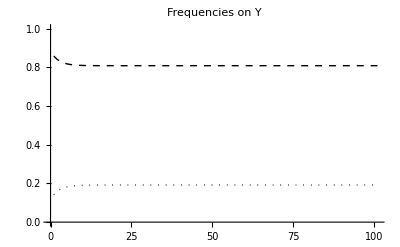

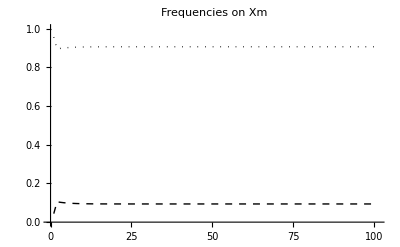

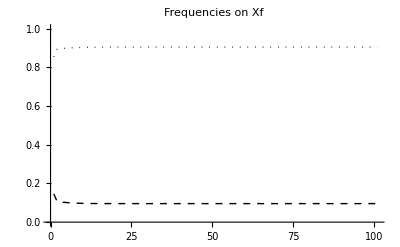

```mathematica
Show[
ListPlot[
Table[
nextYA[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,initialpXf+devXf,(1-initialpXf)-devXf,trypMXAf,trypMXaf,(1-tryα)(initialpXm+devXm),(1-tryα)((1-initialpXm)-devXm),trypMXAm,trypMXam,tryα*(initialpYm+devYm),tryα*((1-initialpYm)-devYm),trypMYAm,trypMYam]/tryα,
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dashed],
PlotRange->{0,1}],
ListPlot[
Table[
nextYa[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,initialpXf+devXf,(1-initialpXf)-devXf,trypMXAf,trypMXaf,(1-tryα)(initialpXm+devXm),(1-tryα)((1-initialpXm)-devXm),trypMXAm,trypMXam,tryα*(initialpYm+devYm),tryα*((1-initialpYm)-devYm),trypMYAm,trypMYam]/tryα,
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dotted],
PlotRange->{0,1}],
PlotLabel->"Frequencies on Y"]

Show[
ListPlot[
Table[
nextXAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,initialpXf+devXf,(1-initialpXf)-devXf,trypMXAf,trypMXaf,(1-tryα)(initialpXm+devXm),(1-tryα)((1-initialpXm)-devXm),trypMXAm,trypMXam,tryα*(initialpYm+devYm),tryα*((1-initialpYm)-devYm),trypMYAm,trypMYam]/(1-tryα),
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dashed],
PlotRange->{0,1}],
ListPlot[
Table[
nextXam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,initialpXf+devXf,(1-initialpXf)-devXf,trypMXAf,trypMXaf,(1-tryα)(initialpXm+devXm),(1-tryα)((1-initialpXm)-devXm),trypMXAm,trypMXam,tryα*(initialpYm+devYm),tryα*((1-initialpYm)-devYm),trypMYAm,trypMYam]/(1-tryα),
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dotted],
PlotRange->{0,1}],
PlotLabel->"Frequencies on Xm"]

Show[
ListPlot[
Table[
nextXAf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,initialpXf+devXf,(1-initialpXf)-devXf,trypMXAf,trypMXaf,(1-tryα)(initialpXm+devXm),(1-tryα)((1-initialpXm)-devXm),trypMXAm,trypMXam,tryα*(initialpYm+devYm),tryα*((1-initialpYm)-devYm),trypMYAm,trypMYam],
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dashed],
PlotRange->{0,1}],
ListPlot[
Table[
nextXaf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,initialpXf+devXf,(1-initialpXf)-devXf,trypMXAf,trypMXaf,(1-tryα)(initialpXm+devXm),(1-tryα)((1-initialpXm)-devXm),trypMXAm,trypMXam,tryα*(initialpYm+devYm),tryα*((1-initialpYm)-devYm),trypMYAm,trypMYam],
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dotted],
PlotRange->{0,1}],
PlotLabel->"Frequencies on Xf"]
```

#### Ext Stab

First, we need to decide on the initial frequency of the new mutation. We will assume that it appear in linkage equilibrium with the old type by introducing it at the same frequencies.

```mathematica
pM=0.0001;

trypMXAf=pM initialpXf;
trypMXaf=pM (1-initialpXf);
trypMXAm=pM(1-tryα) initialpXm;
trypMXam=pM (1-tryα)(1-initialpXm);
trypMYAm=pM (tryα)initialpYm;
trypMYam=pM(tryα)(1-initialpYm);
```

Several other parameters are needed for the plots, including the time (tmax) and interval at which the frequencies are registered (tinterval).

```mathematica
tmax=5000;
tinterval=100;
tplotinterval=1000;

(*plot parameters*)
inches=72;
lwd=0.006;(*line thickness as fraction of plot width*)
ticksize={0,0.01};
xplotmin=0;
xplotmax=tmax;
yplotmin=0;
yplotmax=1;
xsize=5inches;
aspectratio=1/Sqrt[2];
```

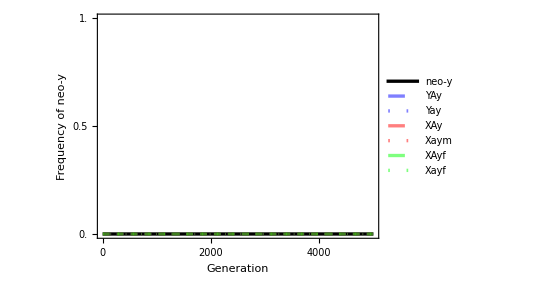

```mathematica
Legended[
ListPlot[{
Table[{t,
Total[{
nextYAy[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextYay[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextXAym[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextXaym[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam](*,
nextXAyf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextXayf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]*)
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextYAy[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextYay[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextXAym[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{
nextXaym[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextXAyf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{
nextXayf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}]
},
Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotmin,yplotmax,0.5}]},
FrameTicksStyle->Directive[Black,Thickness[lwd]],
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Generation","Frequency of neo-y"},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
Joined->True,
PlotStyle->{
Directive[Black,Thickness[lwd]],
Directive[Blue,Opacity[0.5],Thickness[lwd],Dashed],
Directive[Blue,Opacity[0.5],Thickness[lwd],Dotted],
Directive[Red,Opacity[0.5],Thickness[lwd],Dashed],
Directive[Red,Opacity[0.5],Thickness[lwd],Dotted],
Directive[Green,Opacity[0.5],Thickness[lwd],Dashed],
Directive[Green,Opacity[0.5],Thickness[lwd],Dotted]
},
PlotRange->{0,1},
PlotRangeClipping->False],
Placed[
LineLegend[{
Directive[Black,Thickness[20*lwd]],
Directive[Blue,Opacity[0.5],Thickness[20*lwd],Dashed],
Directive[Blue,Opacity[0.5],Thickness[20*lwd],Dotted],
Directive[Red,Opacity[0.5],Thickness[20*lwd],Dashed],
Directive[Red,Opacity[0.5],Thickness[20*lwd],Dotted],
Directive[Green,Opacity[0.5],Thickness[20*lwd],Dashed],
Directive[Green,Opacity[0.5],Thickness[20*lwd],Dotted]
},
{
Style["neo-y",16],
Style["YAy",16],
Style["Yay",16],
Style["XAy",16],
Style["Xaym",16],
Style["XAyf",16],
Style["Xayf",16]
},
LegendFunction->"Frame",
LegendLayout->"Row"
],
{0.52,0.75}
] 
]
```

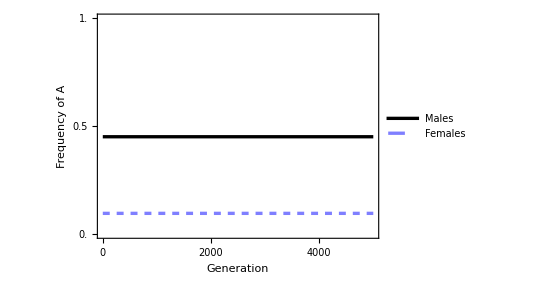

```mathematica
Legended[
ListPlot[{
Table[{t,
Total[{
nextYA[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextXAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextYAy[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextXAym[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{
nextXAf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextXAyf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}]
},
Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotmin,yplotmax,0.5}]},
FrameTicksStyle->Directive[Black,Thickness[lwd]],
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Generation","Frequency of A"},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
Joined->True,
PlotStyle->{Directive[Black,Thickness[lwd]],
Directive[Blue,Opacity[0.5],Thickness[lwd],Dashed],
Directive[Blue,Opacity[0.5],Thickness[lwd],Dotted],
Directive[Red,Opacity[0.5],Thickness[lwd],Dashed],
Directive[Red,Opacity[0.5],Thickness[lwd],Dotted],
Directive[Green,Opacity[0.5],Thickness[lwd],Dashed],
Directive[Green,Opacity[0.5],Thickness[lwd],Dotted]},
PlotRange->{0,1},
PlotRangeClipping->False],
Placed[
LineLegend[{
Directive[Black,Thickness[20*lwd]],
Directive[Blue,Opacity[0.5],Thickness[20*lwd],Dashed]
},
{
Style["Males",16],
Style["Females",16]
},
LegendFunction->"Frame",
LegendLayout->"Row"
],
{0.52,0.75}
] 
]
```

#### Sex ratio plot

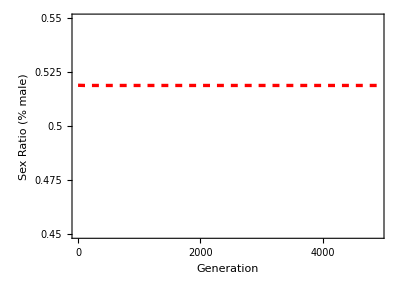

```mathematica
yplotminSexRatio=0.45;
yplotmaxSexRatio=0.55;
yplotintervalSexRatio=0.025;


ListPlot[{Table[{t,
Total[{
sexRatioAtBirth[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,1,tmax,tinterval}]
},
Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotminSexRatio,yplotmaxSexRatio,yplotintervalSexRatio}]},
FrameTicksStyle->Directive[Black,Thickness[lwd]],
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Generation","Sex Ratio (% male)"},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
Joined->True,
PlotStyle->{Directive[Red,Thickness[lwd],Dashed]},
PlotRange->{yplotminSexRatio,yplotmaxSexRatio}]
```

### Iterate Recursions (neo-Y invades and goes to 50% in male gametes)

#### Parameters:

```mathematica
tryFAA=0.9;
tryFAa=0.96;
tryFaa=1;
tryMAA=0.84;
tryMAa=0.95;
tryMaa=1;
trywA=1;
trywa=0.9;
tryr=0.5;
tryα=0.5;
```

Also need to specify tryR for full system: (n.b., χ=r R)

```mathematica
tryR=0.01;
```

#### Find equilibrium (equil and sieve functions) [enter]

```mathematica
initialpXf=Flatten[sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryα]][[1]]
initialpXm=Flatten[sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryα]][[2]]
initialYAf=0;
initialYaf=0;
initialpYm=Flatten[sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryα]][[3]]
```

0.157187

0.154864

0.154864

#### IntStab

We check stability by perturbing the system slightly and checking that allele frequencies return. dev gives the initial deviations:

```mathematica
devXf=0.05;
devXm=-0.05;
devYm=0.05;

trypMXAf=0;
trypMXaf=0;
trypMXAm=0;
trypMXam=0;
trypMYAm=0;
trypMYam=0;
tmax=1000;
tinterval=10;
```

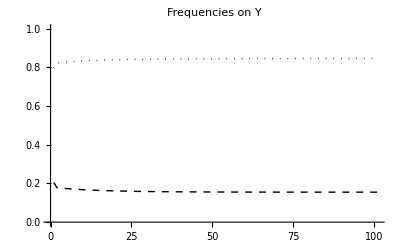

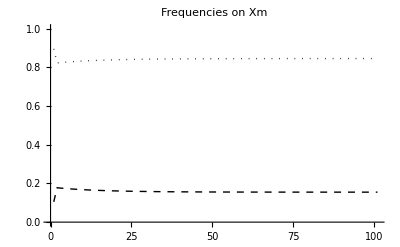

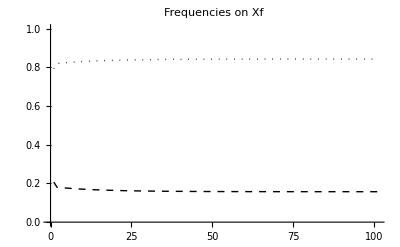

```mathematica
Show[
ListPlot[
Table[
nextYA[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,initialpXf+devXf,(1-initialpXf)-devXf,trypMXAf,trypMXaf,(1-tryα)(initialpXm+devXm),(1-tryα)((1-initialpXm)-devXm),trypMXAm,trypMXam,tryα*(initialpYm+devYm),tryα*((1-initialpYm)-devYm),trypMYAm,trypMYam]/tryα,
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dashed],
PlotRange->{0,1}],
ListPlot[
Table[
nextYa[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,initialpXf+devXf,(1-initialpXf)-devXf,trypMXAf,trypMXaf,(1-tryα)(initialpXm+devXm),(1-tryα)((1-initialpXm)-devXm),trypMXAm,trypMXam,tryα*(initialpYm+devYm),tryα*((1-initialpYm)-devYm),trypMYAm,trypMYam]/tryα,
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dotted],
PlotRange->{0,1}],
PlotLabel->"Frequencies on Y"]

Show[
ListPlot[
Table[
nextXAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,initialpXf+devXf,(1-initialpXf)-devXf,trypMXAf,trypMXaf,(1-tryα)(initialpXm+devXm),(1-tryα)((1-initialpXm)-devXm),trypMXAm,trypMXam,tryα*(initialpYm+devYm),tryα*((1-initialpYm)-devYm),trypMYAm,trypMYam]/(1-tryα),
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dashed],
PlotRange->{0,1}],
ListPlot[
Table[
nextXam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,initialpXf+devXf,(1-initialpXf)-devXf,trypMXAf,trypMXaf,(1-tryα)(initialpXm+devXm),(1-tryα)((1-initialpXm)-devXm),trypMXAm,trypMXam,tryα*(initialpYm+devYm),tryα*((1-initialpYm)-devYm),trypMYAm,trypMYam]/(1-tryα),
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dotted],
PlotRange->{0,1}],
PlotLabel->"Frequencies on Xm"]

Show[
ListPlot[
Table[
nextXAf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,initialpXf+devXf,(1-initialpXf)-devXf,trypMXAf,trypMXaf,(1-tryα)(initialpXm+devXm),(1-tryα)((1-initialpXm)-devXm),trypMXAm,trypMXam,tryα*(initialpYm+devYm),tryα*((1-initialpYm)-devYm),trypMYAm,trypMYam],
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dashed],
PlotRange->{0,1}],
ListPlot[
Table[
nextXaf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,initialpXf+devXf,(1-initialpXf)-devXf,trypMXAf,trypMXaf,(1-tryα)(initialpXm+devXm),(1-tryα)((1-initialpXm)-devXm),trypMXAm,trypMXam,tryα*(initialpYm+devYm),tryα*((1-initialpYm)-devYm),trypMYAm,trypMYam],
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dotted],
PlotRange->{0,1}],
PlotLabel->"Frequencies on Xf"]
```

#### Ext Stab

First, we need to decide on the initial frequency of the new mutation. We will assume that it appear in linkage equilibrium with the old type by introducing it at the same frequencies.

```mathematica
pM=0.0001;

trypMXAf=pM initialpXf;
trypMXaf=pM (1-initialpXf);
trypMXAm=pM(1-tryα) initialpXm;
trypMXam=pM (1-tryα)(1-initialpXm);
trypMYAm=pM (tryα)initialpYm;
trypMYam=pM(tryα)(1-initialpYm);
```

Several other parameters are needed for the plots, including the time (tmax) and interval at which the frequencies are registered (tinterval).

```mathematica
tmax=5000;
tinterval=100;
tplotinterval=1000;

(*plot parameters*)
inches=72;
lwd=0.006;(*line thickness as fraction of plot width*)
ticksize={0,0.01};
xplotmin=0;
xplotmax=tmax;
yplotmin=0;
yplotmax=1;
xsize=5inches;
aspectratio=1/Sqrt[2];
```

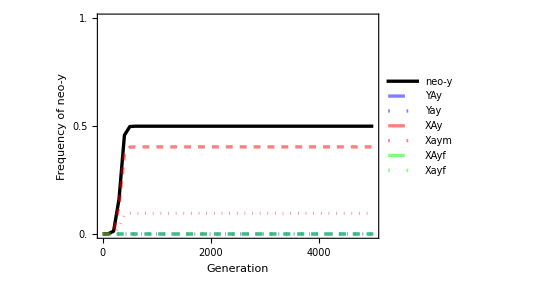

```mathematica
Legended[
ListPlot[{
Table[{t,
Total[{
nextYAy[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextYay[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextXAym[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextXaym[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam](*,
nextXAyf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextXayf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]*)
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextYAy[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextYay[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextXAym[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{
nextXaym[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextXAyf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{
nextXayf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}]
},
Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotmin,yplotmax,0.5}]},
FrameTicksStyle->Directive[Black,Thickness[lwd]],
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Generation","Frequency of neo-y"},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
Joined->True,
PlotStyle->{
Directive[Black,Thickness[lwd]],
Directive[Blue,Opacity[0.5],Thickness[lwd],Dashed],
Directive[Blue,Opacity[0.5],Thickness[lwd],Dotted],
Directive[Red,Opacity[0.5],Thickness[lwd],Dashed],
Directive[Red,Opacity[0.5],Thickness[lwd],Dotted],
Directive[Green,Opacity[0.5],Thickness[lwd],Dashed],
Directive[Green,Opacity[0.5],Thickness[lwd],Dotted]
},
PlotRange->{0,1},
PlotRangeClipping->False],
Placed[
LineLegend[{
Directive[Black,Thickness[20*lwd]],
Directive[Blue,Opacity[0.5],Thickness[20*lwd],Dashed],
Directive[Blue,Opacity[0.5],Thickness[20*lwd],Dotted],
Directive[Red,Opacity[0.5],Thickness[20*lwd],Dashed],
Directive[Red,Opacity[0.5],Thickness[20*lwd],Dotted],
Directive[Green,Opacity[0.5],Thickness[20*lwd],Dashed],
Directive[Green,Opacity[0.5],Thickness[20*lwd],Dotted]
},
{
Style["neo-y",16],
Style["YAy",16],
Style["Yay",16],
Style["XAy",16],
Style["Xaym",16],
Style["XAyf",16],
Style["Xayf",16]
},
LegendFunction->"Frame",
LegendLayout->"Row"
],
{0.52,0.75}
] 
]
```

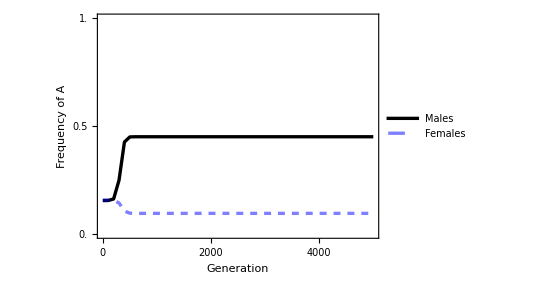

```mathematica
Legended[
ListPlot[{
Table[{t,
Total[{
nextYA[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextXAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextYAy[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextXAym[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{
nextXAf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextXAyf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}]
},
Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotmin,yplotmax,0.5}]},
FrameTicksStyle->Directive[Black,Thickness[lwd]],
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Generation","Frequency of A"},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
Joined->True,
PlotStyle->{Directive[Black,Thickness[lwd]],
Directive[Blue,Opacity[0.5],Thickness[lwd],Dashed],
Directive[Blue,Opacity[0.5],Thickness[lwd],Dotted],
Directive[Red,Opacity[0.5],Thickness[lwd],Dashed],
Directive[Red,Opacity[0.5],Thickness[lwd],Dotted],
Directive[Green,Opacity[0.5],Thickness[lwd],Dashed],
Directive[Green,Opacity[0.5],Thickness[lwd],Dotted]},
PlotRange->{0,1},
PlotRangeClipping->False],
Placed[
LineLegend[{
Directive[Black,Thickness[20*lwd]],
Directive[Blue,Opacity[0.5],Thickness[20*lwd],Dashed]
},
{
Style["Males",16],
Style["Females",16]
},
LegendFunction->"Frame",
LegendLayout->"Row"
],
{0.52,0.75}
] 
]
```

#### Sex ratio plot

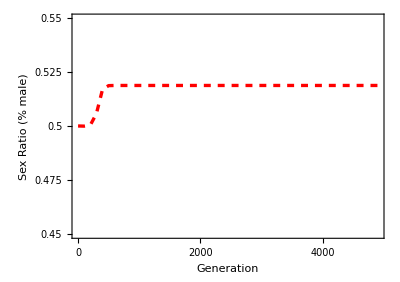

```mathematica
yplotminSexRatio=0.45;
yplotmaxSexRatio=0.55;
yplotintervalSexRatio=0.025;


ListPlot[{Table[{t,
Total[{
sexRatioAtBirth[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,1,tmax,tinterval}]
},
Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotminSexRatio,yplotmaxSexRatio,yplotintervalSexRatio}]},
FrameTicksStyle->Directive[Black,Thickness[lwd]],
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Generation","Sex Ratio (% male)"},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
Joined->True,
PlotStyle->{Directive[Red,Thickness[lwd],Dashed]},
PlotRange->{yplotminSexRatio,yplotmaxSexRatio}]
```

# neo-W invades XY

## Recursions [enter]

We consider three loci: 1) a diallelic autosomal locus, 2) an original diallelic sex-determining locus, and 3) a novel diallelic sex-determining locus. We assume that most gametes have the null/wild-type allele at the novel sex-determining locus, but a few have a new mutation w at this locus, which is feminizing and is dominant over the original diallelic sex-determining locus (making that locus superfluous).

### Haploid selection

We start with haploid selection, which occurs in sperm/pollen only. We assume male sperm/pollen compete for eggs, and that the allele at the autosomal locus determines their competitive ability (with relative fitnesses wA and wa). After selection on male gametes/pollen the frequencies of gametes in each sex are

```mathematica
(*non-mutant eggs*)
XAfs=XAf;
Xafs=Xaf;
YAfs=YAf;
Yafs=Yaf;

(*mutant eggs*)
XAwfs=XAwf;
Xawfs=Xawf;
YAwfs=YAwf;
Yawfs=Yawf;

(*mean fitness of male gametes*)
wbarHap=(wA XAm+wa Xam+wA XAwm+wa Xawm)+(wA YAm+wa Yam+wA YAwm+wa Yawm);

(*non-mutant male gametes*)
XAms=wA XAm/wbarHap;
Xams=wa Xam/wbarHap;
YAms= wA YAm/wbarHap;
Yams= wa Yam/wbarHap;

(*mutant male gametes*)
XAwms=wA XAwm/wbarHap;
Xawms=wa Xawm/wbarHap;
YAwms= wA YAwm/wbarHap;
Yawms= wa Yawm/wbarHap;
```

Check that frequencies sum to one in each sex after haploid selection:

```mathematica
1==XAms+Xams+YAms+Yams+XAwms+Xawms+YAwms+Yawms//Factor (*male gametes*)
1==XAfs+Xafs+XAwfs+Xawfs+YAfs+Yafs+YAwfs+Yawfs/.Xaf->1-XAf-Xawf-XAwf-YAf-Yaf-Yawf-YAwf//Factor (*eggs*)
```

True

True

### Random mating

After random mating, the frequencies of the diploid genotypes are

```mathematica
(*X-Y males*)
XAYA=XAfs YAms+YAfs XAms;
XAYa=XAfs Yams+Yafs XAms;
XaYA=Xafs YAms+YAfs Xams;
XaYa=Xafs Yams+Yafs Xams;

(*Y-Y males*)
YAYA=YAfs YAms;
YAYa=YAfs Yams+Yafs YAms;
YaYa=Yafs Yams;

(*non-mutant females*)
XAXA=XAfs XAms;
XAXa=XAfs Xams+Xafs XAms ;
XaXa=Xafs Xams;

(*X-Xw females*)
XAwXA=XAwfs XAms+XAfs XAwms;
XAwXa=XAwfs Xams+Xafs XAwms ;
XAXaw=XAfs Xawms+Xawfs XAms;
XawXa=Xawfs Xams+Xafs Xawms;

(*Xw-Xw females*)
XAwXAw=XAwfs XAwms;
XAwXaw=XAwfs Xawms+Xawfs XAwms ;
XawXaw=Xawfs Xawms;

(*X-Yw females*)
XAwYA=XAwfs YAms+YAfs XAwms;
XAwYa=XAwfs Yams+Yafs XAwms;
XawYA=Xawfs YAms+YAfs Xawms;
XawYa=Xawfs Yams+Yafs Xawms;

(*Xw-Y females*)
XAYAw=XAfs YAwms+YAwfs XAms;
XAYaw=XAfs Yawms+Yawfs XAms ;
XaYAw=Xafs YAwms+YAwfs Xams ;
XaYaw=Xafs Yawms+Yawfs Xams;

(*Xw-Yw females*)
XAwYAw=XAwfs YAwms+YAwfs XAwms ;
XAwYaw=XAwfs Yawms+Yawfs XAwms ;
XawYAw=Xawfs YAwms+YAwfs Xawms ;
XawYaw=Xawfs Yawms+Yawfs Xawms;

(*Yw-Y females*)
YAwYA=YAwfs YAms+YAfs YAwms;
YAwYa=YAwfs Yams+Yafs YAwms;
YawYA=Yawfs YAms+YAfs Yawms;
YawYa=Yawfs Yams+Yafs Yawms;

(*Yw-Yw females*)
YAwYAw=YAwfs YAwms;
YAwYaw=YAwfs Yawms+Yawfs YAwms;
YawYaw=Yawfs Yawms;
```

Check that they sum to one

```mathematica
XAXA+XAXa+XaXa+XAYA+XAwXA+XAwXa+XAXaw+XawXa+XAwYA+XAwYa+XawYA+XawYa+XAYAw+XAYaw+XaYAw+XaYaw+XAYa+XaYA+XaYa+XAwYAw+XAwYaw+XawYAw+XawYaw+XAwXAw+XAwXaw+XawXaw+YAwYA+YAwYa+YawYA+YawYa+YAwYAw+YAwYaw+YawYaw+YAYA+YAYa+YaYa/.Xaf->1-XAf-Xawf-XAwf-YAf-Yaf-Yawf-YAwf//Factor
```

1

### Diploid selection

We next model selection in diploids, which can differ among the sexes. Let FAA, FAa, and Faa be the relative fitnesses of females homozygous for allele A, heterozygous, or homozygous for allele a at the autosomal locus. Similarly we use MAA, MAa, and Maa in males. Then after diploid selection the frequencies of the diploid genotypes in each sex are

```mathematica
(*mean male fitness*)
wbarM=
MAA XAYA+MAa (XAYa+XaYA)+Maa XaYa+
MAA YAYA+MAa YAYa+Maa YaYa;

(*non-mutant males*)
XAYAs=MAA XAYA/wbarM;
XAYas=MAa XAYa/wbarM;
XaYAs=MAa XaYA/wbarM;
XaYas=Maa XaYa/wbarM;

YAYAs=MAA YAYA/wbarM;
YAYas=MAa YAYa/wbarM;
YaYas=Maa YaYa/wbarM;

(*mean female fitness*)
wbarF=FAA XAXA+FAa XAXa+Faa XaXa+
FAA XAwXA+FAa(XAwXa+XAXaw)+Faa XawXa+
FAA XAwXAw+FAa XAwXaw+Faa XawXaw+
FAA XAwYA+FAa(XAwYa+XawYA)+Faa XawYa+
FAA XAYAw+FAa(XAYaw+XaYAw)+Faa XaYaw+
FAA XAwYAw+FAa(XAwYaw+XawYAw)+Faa XawYaw+
FAA YAwYA+FAa(YAwYa+YawYA)+Faa YawYa+
FAA YAwYAw+FAa YAwYaw+Faa YawYaw; 

(*females*)
XAXAs=FAA XAXA/wbarF;
XAXas=FAa XAXa/wbarF;
XaXas=Faa XaXa/wbarF;

(*X-Xw females*)
XAwXAs=FAA XAwXA/wbarF;
XAwXas=FAa XAwXa/wbarF;
XAXaws=FAa XAXaw/wbarF;
XawXas=Faa XawXa/wbarF;

(*X-Yw females*)
XAYAws=FAA XAYAw/wbarF;
XAYaws=FAa XAYaw/wbarF;
XaYAws=FAa XaYAw/wbarF;
XaYaws=Faa XaYaw/wbarF;

(*Xw-Y females*)
XAwYAs=FAA XAwYA/wbarF;
XAwYas=FAa XAwYa/wbarF;
XawYAs=FAa XawYA/wbarF;
XawYas=Faa XawYa/wbarF;

(*Xw-Xw females*)
XAwXAws=FAA XAwXAw/wbarF;
XAwXaws=FAa XAwXaw/wbarF;
XawXaws=Faa XawXaw/wbarF;

(*Xw-Yw females*)
XAwYAws=FAA XAwYAw/wbarF;
XAwYaws=FAa XAwYaw/wbarF;
XawYAws=FAa XawYAw/wbarF;
XawYaws=Faa XawYaw/wbarF;

(*Yw-Y females*)
YAwYAs=FAA YAwYA/wbarF;
YAwYas=FAa YAwYa/wbarF;
YawYAs=FAa YawYA/wbarF;
YawYas=Faa YawYa/wbarF;

(*Yw-Yw females*)
YAwYAws=FAA YAwYAw/wbarF;
YAwYaws=FAa YAwYaw/wbarF;
YawYaws=Faa YawYaw/wbarF;
```

Check that frequencies of diploid genotypes in each sex sum to one after diploid selection:

```mathematica
(*females*)
1==XAXAs+XAXas+XaXas+
XAwXAs+XAwXas+XAXaws+XawXas+
XAwXAws+XAwXaws+XawXaws+
XAwYAs+XAwYas+XawYAs+XawYas+
XAYAws+XAYaws+XaYAws+XaYaws+
XAwYAws+XAwYaws+XawYAws+XawYaws+
YAwYAs+YAwYas+YawYAs+YawYas+YAwYAws+YAwYaws+YawYaws//Factor
(*males*)
1==(
XAYAs+XAYas+XaYAs+XaYas+YAYAs+YAYas+YaYas)//Factor
```

True

True

### Meiosis

Finally, meiosis occurs. We have three recombination rates to consider (we assume no interference):

r: the recombination rate between the autosomal locus and and the original sex-determining locus
R: the recombination rate between the novel sex-determining locus and the autosomal locus
χ: the recombination rate between the novel sex-determingin locus and the original sex-determing locus

We also assume that males produce α% of their gametes with the Y allele (original sex chromosome drive if α≠1/2).
The frequencies of haploid genotypes in gametes from each at the start of the next generation are then

```mathematica
(*male haploids*)
XAmprime=(1-α)(XAYAs+XAYas(1-r)+r XaYAs);
Xamprime=(1-α)(XaYas+XaYAs(1-r)+r XAYas);
YAmprime=α(XAYAs+XaYAs(1-r)+XAYas r)+YAYAs+YAYas/2;
Yamprime=α(XaYas+XAYas(1-r)+XaYAs r)+YaYas+YAYas/2;

(*eggs*)
XAfprime=XAXAs+XAXas/2+
XAwXAs/2 +XAwXas (R)/2+XAXaws (1-R)/2+
(1-α)((XAYAws(1-(r+R-2χ))+XAwYAs (r+R-2χ))+
(XAYaws (1-(r+R-χ))+XawYAs(r-χ)+XaYAws(χ)+XAwYas(R-χ)));
Xafprime=XaXas+XAXas/2+
XawXas/2 +XAwXas (1-R)/2+XAXaws (R)/2+
(1-α)((XaYaws (1-(r+R-2χ))+XawYas(r+R-2χ))+
(XAYaws(χ)+XawYAs(R-χ)+XaYAws(1-(r+R-χ))+XAwYas(r-χ)));
XAwfprime=XAwXAws+XAwXaws/2+
XAwXAs/2 +XAwXas (1-R)/2+XAXaws (R)/2+
(1-α)((XAYAws((r+R-2χ))+XAwYAs (1-(r+R-2χ)))+
(XAYaws (R-χ)+XawYAs(χ)+XaYAws(r-χ)+XAwYas(1-(r+R-χ)))+
XAwYAws+XAwYaws(1-r)+XawYAws r);
Xawfprime=XawXaws+XAwXaws/2+
XawXas/2 +XAwXas (R)/2+XAXaws (1-R)/2+
(1-α)((XaYaws((r+R-2χ))+XawYas (1-(r+R-2χ)))+
(XAYaws (r-χ)+XawYAs(1-(r+R-χ))+XaYAws(R-χ)+XAwYas(χ))+
XawYaws+XawYAws(1-r)+XAwYaws r);

YAfprime=(α)((XAYAws((r+R-2χ))+XAwYAs (1-(r+R-2χ)))+
(XAYaws (r-χ)+XawYAs(1-(r+R-χ))+XaYAws(R-χ)+XAwYas(χ)))+
YAwYAs/2+YAwYas(R)/2+YawYAs(1-R)/2;
Yafprime=α((XaYaws((r+R-2χ))+XawYas (1-(r+R-2χ)))+
(XAYaws (R-χ)+XawYAs(χ)+XaYAws(r-χ)+XAwYas(1-(r+R-χ))))+
YawYas/2+YAwYas(1-R)/2+YawYAs(R)/2;
YAwfprime=α((XAYAws(1-(r+R-2χ))+XAwYAs ((r+R-2χ)))+
(XAYaws (χ)+XawYAs(R-χ)+XaYAws(1-(r+R-χ))+XAwYas(r-χ))+
XAwYAws+XAwYaws(r)+XawYAws (1-r))+
YAwYAs/2+YAwYas(1-R)/2+YawYAs(R)/2+
YAwYAws+YAwYaws/2;
Yawfprime=α((XaYaws(1-(r+R-2χ))+XawYas ((r+R-2χ)))+
(XAYaws (1-(r+R-χ))+XawYAs(r-χ)+XaYAws(χ)+XAwYas(R-χ))+
XawYaws+XawYAws(r)+XAwYaws (1-r))+
YawYas/2+YAwYas(R)/2+YawYAs(1-R)/2+
YawYaws+YAwYaws/2;
```

Check

```mathematica
1==XAfprime+Xafprime+XAwfprime+Xawfprime+YAfprime+Yafprime+YAwfprime+Yawfprime//Factor
1==XAmprime+Xamprime+YAmprime+Yamprime//Factor
```

True

True

## Resident equilibrium (weaksel) [enter]

We first assume that the neoY is absent

```mathematica
subequil={
XAf->pXf,
Xaf->(1-pXf),
YAf->0,
Yaf->0,
XAm->pXm(1-α),
Xam->(1-pXm)(1-α),
YAm->pYm*α,
Yam->(1-pYm)*α,
XAwf->0,
Xawf->0,
XAwm->0,
Xawm->0,
YAwm->0,
Yawm->0,
YAwf->0,
Yawf->0
};
```

where pXf is the frequency of A in non-mutant eggs, pXm is the frequency of A in gametes from males with an X allele, and pY is the frequency of A in gametes from males with a Y allele.

We now wish to solve for the equilibrium frequencies of the haploid genotypes in gametes of each sex. Equilibrium is achieved when the following three equations are zero

```mathematica
differenceEqs={
XAfprime-XAf,
XAmprime-XAm,
YAmprime-YAm
}/.subequil;
```

To simplify the analysis we assume weak selection in both haploids (sperm/pollen) and diploids

```mathematica
weaksel={
MAA->1+sAm ϵ,
MAa->1+hAm sAm ϵ,
Maa->1,
FAA->1+sAf ϵ,
FAa->1+hAf sAf ϵ,
Faa->1,
wA->1+t ϵ,
wa->1
};
```

We can write the frequencies as Taylor series

```mathematica
frequenciessub={
pXf->pXf0+pXf1 ϵ,
pXm->pXm0+pXm1 ϵ,
pYm->pYm0+pYm1 ϵ
};
```

Without selection the recursions for the change in the frequencies are

```mathematica
differenceEqs0=Normal[Series[differenceEqs/.weaksel/.frequenciessub,{ϵ,0,0}]]
```

{1/2 (-pXf0+pXm0),-pXm0+(pXf0-pXf0 r+pYm0 r) (1-α)+pXm0 α,pXf0 r α-pYm0 r α}

And at equilibrium we have

```mathematica
sol0=Solve[differenceEqs0==0,{pXf0,pXm0}]
```

{{pXf0→pYm0,pXm0→pYm0}}

So, with no selection, the equilibrium frequency of A in each gamete/pollen type is equal (and we call this pA).

Now, looking at only the first order selection terms, the recursions for the change in frequency of A in each gamete/pollen type are

```mathematica
differenceEqs1=Collect[Normal[Series[differenceEqs/.weaksel/.frequenciessub/.sol0,{ϵ,0,1}]],ϵ,Factor]/.pYm0->pA//Flatten
```

{1/2 (-pXf1+pXm1+2 hAf pA sAf+2 pA^2 sAf-6 hAf pA^2 sAf-2 pA^3 sAf+4 hAf pA^3 sAf+pA t-pA^2 t) ϵ,(-pXf1+pXm1+pXf1 r-pYm1 r-hAm pA sAm-pA^2 sAm+3 hAm pA^2 sAm+pA^3 sAm-2 hAm pA^3 sAm-pA r t+pA^2 r t) (-1+α) ϵ,(pXf1 r-pYm1 r+hAm pA sAm+pA^2 sAm-3 hAm pA^2 sAm-pA^3 sAm+2 hAm pA^3 sAm+pA t-pA^2 t-pA r t+pA^2 r t) α ϵ}

Instead of solving for the first order genotype frequencies we will instead solve for the difference in the frequency of A in the different gamete/pollen types.

The difference in the frequency of A with X in females and X in males is (at equilibrium to first order in selection)

```mathematica
eqdpAXfXm=Solve[differenceEqs1[[1]]==0/.pXf1->dpAXfXm+pXm1,dpAXfXm]//Flatten
```

{dpAXfXm→2 hAf pA sAf+2 pA^2 sAf-6 hAf pA^2 sAf-2 pA^3 sAf+4 hAf pA^3 sAf+pA t-pA^2 t}

The difference in the frequency of A with X in males and Y is (at equilibrium to first order in selection)

```mathematica
eqdpAXmY=Solve[differenceEqs1[[2]]==0/.pXf1->dpAXfXm+pXm1/.eqdpAXfXm/.pXm1->dpAXmY+pYm1,dpAXmY]//Flatten
```

{dpAXmY→1/r(2 hAf pA sAf+2 pA^2 sAf-6 hAf pA^2 sAf-2 pA^3 sAf+4 hAf pA^3 sAf-2 hAf pA r sAf-2 pA^2 r sAf+6 hAf pA^2 r sAf+2 pA^3 r sAf-4 hAf pA^3 r sAf+hAm pA sAm+pA^2 sAm-3 hAm pA^2 sAm-pA^3 sAm+2 hAm pA^3 sAm+pA t-pA^2 t)}

The difference in the frequency of A with X in females and Y is (at equilibrium to first order in selection)

```mathematica
eqdpAXfY=Solve[differenceEqs1[[3]]==0/.pXf1->dpAXfY+pYm1,dpAXfY]//Flatten
```

{dpAXfY→(-hAm pA sAm-pA^2 sAm+3 hAm pA^2 sAm+pA^3 sAm-2 hAm pA^3 sAm-pA t+pA^2 t+pA r t-pA^2 r t)/r}

So then, to first order, the equilibrium frequencies of A in gametes of each type are

```mathematica
eqpXf=pXf0+ϵ dpAXfXm+ϵ dpAXmY/.sol0/.pYm0->pA/.eqdpAXfXm/.eqdpAXmY//Simplify
```

{(pA ((-1+pA) (2 hAf (-1+2 pA) sAf-hAm sAm-pA (2 sAf+sAm-2 hAm sAm)-t) ϵ+r (1+t (ϵ-pA ϵ))))/r}

```mathematica
eqpXm=pXm0-ϵ dpAXfXm+ϵ dpAXfY/.sol0/.pYm0->pA/.eqdpAXfXm/.eqdpAXfY//Simplify
```

{(pA (-(-1+pA) (-pA sAm+hAm (-1+2 pA) sAm-t) ϵ+r (1-2 pA sAf ϵ+2 pA^2 sAf ϵ-2 hAf (1-3 pA+2 pA^2) sAf ϵ)))/r}

```mathematica
eqpY=pYm0+ϵ dpAXfXm-ϵ dpAXfY/.sol0/.pYm0->pA/.eqdpAXfY/.eqdpAXfXm//Simplify
```

{(pA ((-1+pA) (-pA sAm+hAm (-1+2 pA) sAm-t) ϵ+r (1+2 pA sAf ϵ-2 pA^2 sAf ϵ+2 hAf (1-3 pA+2 pA^2) sAf ϵ)))/r}

The recursion for pA is given by

```mathematica
dpA=Collect[Normal[Series[ (2XAfprime+XAmprime/(1-α)+YAmprime/α)-(2XAf+XAm/(1-α)+YAm/α)/.weaksel/.subequil/.pXf->eqpXf/.pXm->eqpXm/.pYm->eqpY,{ϵ,0,1}]]/4,ϵ,Simplify]/.ϵ->1//Flatten
```

{1/2 (-1+pA) pA (hAf (-1+2 pA) sAf-hAm sAm-pA (sAf+sAm-2 hAm sAm)-t)}

And at equilibrium we have

```mathematica
equilpA=Solve[dpA==0,pA]
```

{{pA→0},{pA→1},{pA→(hAf sAf+hAm sAm+t)/(-sAf+2 hAf sAf-sAm+2 hAm sAm)}}

Notice that when t=0 we have equation “avgpASubs” in van Doorn & Kirkpatrick 2007 (SOM page 6). Sperm/pollen selection acts to increase the frequency of A (if selected for, t>0).

## Resident equilibrium (weakselmod) [enter]

We first assume that the neoY is absent

```mathematica
subequil={
XAf->pXf,
Xaf->(1-pXf),
YAf->0,
Yaf->0,
XAm->pXm(1-α),
Xam->(1-pXm)(1-α),
YAm->pYm*α,
Yam->(1-pYm)*α,
XAwf->0,
Xawf->0,
XAwm->0,
Xawm->0,
YAwm->0,
Yawm->0,
YAwf->0,
Yawf->0
};
```

where pXf is the frequency of A in non-mutant eggs, pXm is the frequency of A in gametes from males with an X allele, and pY is the frequency of A in gametes from males with a Y allele.

We now wish to solve for the equilibrium frequencies of the haploid genotypes in gametes of each sex. Equilibrium is achieved when the following three equations are zero

```mathematica
differenceEqs={
XAfprime-XAf,
XAmprime-XAm,
YAmprime-YAm
}/.subequil;
```

To simplify the analysis we assume weak selection in both haploids (sperm/pollen) and diploids

```mathematica
weakselmod={
MAA->1+δMAA ϵ,
MAa->1+δMAa ϵ,
Maa->1+δMaa ϵ,
FAA->1+δFAA ϵ,
FAa->1+δFAa ϵ,
Faa->1+δFaa ϵ,
wA->1+δwA ϵ,
wa->1+δwa ϵ};
```

We can write the frequencies as Taylor series

```mathematica
frequenciessub={
pXf->pXf0+pXf1 ϵ,
pXm->pXm0+pXm1 ϵ,
pYm->pYm0+pYm1 ϵ
};
```

Without selection the recursions for the change in the frequencies are

```mathematica
differenceEqs0=Normal[Series[differenceEqs/.weakselmod/.frequenciessub,{ϵ,0,0}]]
```

{1/2 (-pXf0+pXm0),-pXm0+(pXf0-pXf0 r+pYm0 r) (1-α)+pXm0 α,pXf0 r α-pYm0 r α}

And at equilibrium we have

```mathematica
sol0=Solve[differenceEqs0==0,{pXf0,pXm0}]
```

{{pXf0→pYm0,pXm0→pYm0}}

So, with no selection, the equilibrium frequency of A in each gamete/pollen type is equal (and we call this pA).

Now, looking at only the first order selection terms, the recursions for the change in frequency of A in each gamete/pollen type are

```mathematica
differenceEqs1=Collect[Normal[Series[differenceEqs/.weakselmod/.frequenciessub/.sol0,{ϵ,0,1}]],ϵ,Factor]/.pYm0->pA//Flatten
```

{1/2 (-pXf1+pXm1-2 pA δFaa+4 pA^2 δFaa-2 pA^3 δFaa+2 pA δFAa-6 pA^2 δFAa+4 pA^3 δFAa+2 pA^2 δFAA-2 pA^3 δFAA-pA δwa+pA^2 δwa+pA δwA-pA^2 δwA) ϵ,(-1+α) (-pXf1+pXm1+pXf1 r-pYm1 r+pA δMaa-2 pA^2 δMaa+pA^3 δMaa-pA δMAa+3 pA^2 δMAa-2 pA^3 δMAa-pA^2 δMAA+pA^3 δMAA+pA r δwa-pA^2 r δwa-pA r δwA+pA^2 r δwA) ϵ,α (pXf1 r-pYm1 r-pA δMaa+2 pA^2 δMaa-pA^3 δMaa+pA δMAa-3 pA^2 δMAa+2 pA^3 δMAa+pA^2 δMAA-pA^3 δMAA-pA δwa+pA^2 δwa+pA r δwa-pA^2 r δwa+pA δwA-pA^2 δwA-pA r δwA+pA^2 r δwA) ϵ}

Instead of solving for the first order genotype frequencies we will instead solve for the difference in the frequency of A in the different gamete/pollen types.

```mathematica
realsol=Solve[{differenceEqs1=={0,0,0}}/.pXf1->dpXfXm+pXm1/.pXm1-> dpXmYm+pYm1,{dpXfXm,dpXmYm,pA}]//Simplify
```

{{dpXfXm→0,dpXmYm→0,pA→0},{dpXfXm→0,dpXmYm→0,pA→1},{dpXfXm→-((δFaa-δFAa+δMaa-δMAa+δwa-δwA) (δFAa-δFAA+δMAa-δMAA+δwa-δwA) (2 δFaa δMAa-2 δFaa δMAA+δFaa δwa-δMaa δwa+2 δMAa δwa-δMAA δwa+δFAA (2 δMaa-2 δMAa+δwa-δwA)-2 δFAa (δMaa-δMAA+δwa-δwA)-δFaa δwA+δMaa δwA-2 δMAa δwA+δMAA δwA))/(δFaa-2 δFAa+δFAA+δMaa-2 δMAa+δMAA)^3,dpXmYm→((-1+2 r) (δFaa-δFAa+δMaa-δMAa+δwa-δwA) (δFAa-δFAA+δMAa-δMAA+δwa-δwA) (δFAA (δMaa-δMAa+δwa-δwA)+δFaa (δMAa-δMAA+δwa-δwA)+δFAa (-δMaa+δMAA-2 δwa+2 δwA)))/(r (δFaa-2 δFAa+δFAA+δMaa-2 δMAa+δMAA)^3),pA→(δFaa-δFAa+δMaa-δMAa+δwa-δwA)/(δFaa-2 δFAa+δFAA+δMaa-2 δMAa+δMAA)}}

Notice that when t=0 we have equation “avgpASubs” in van Doorn & Kirkpatrick 2007 (SOM page 6). Sperm/pollen selection acts to increase the frequency of A (if selected for, t>0).

## External stability [enter]

Here we are interested in the ability of a rare y mutant to invade the non-mutant resident population at equilibrium.

Remember that we don’t have recursions for XAyf or Xayf because y is a dominant male determining gene. However, we allowed these genotypes to create zygotes so we can include them in the stability matrix (with frequencies of 0 at the start of the next generation). The Jacobian for the mutants is

```mathematica
XAwmprime=0;
Xawmprime=0;
YAwmprime=0;
Yawmprime=0;
```

```mathematica
matExtFull=Transpose[{
D[{YAfprime,Yafprime,XAwfprime,Xawfprime,YAwfprime,Yawfprime,XAwmprime,Xawmprime,YAwmprime,Yawmprime},YAf],
D[{YAfprime,Yafprime,XAwfprime,Xawfprime,YAwfprime,Yawfprime,XAwmprime,Xawmprime,YAwmprime,Yawmprime},Yaf],
D[{YAfprime,Yafprime,XAwfprime,Xawfprime,YAwfprime,Yawfprime,XAwmprime,Xawmprime,YAwmprime,Yawmprime},XAwf],
D[{YAfprime,Yafprime,XAwfprime,Xawfprime,YAwfprime,Yawfprime,XAwmprime,Xawmprime,YAwmprime,Yawmprime},Xawf],
D[{YAfprime,Yafprime,XAwfprime,Xawfprime,YAwfprime,Yawfprime,XAwmprime,Xawmprime,YAwmprime,Yawmprime},YAwf],
D[{YAfprime,Yafprime,XAwfprime,Xawfprime,YAwfprime,Yawfprime,XAwmprime,Xawmprime,YAwmprime,Yawmprime},Yawf],
D[{YAfprime,Yafprime,XAwfprime,Xawfprime,YAwfprime,Yawfprime,XAwmprime,Xawmprime,YAwmprime,Yawmprime},XAwm],
D[{YAfprime,Yafprime,XAwfprime,Xawfprime,YAwfprime,Yawfprime,XAwmprime,Xawmprime,YAwmprime,Yawmprime},Xawm],
D[{YAfprime,Yafprime,XAwfprime,Xawfprime,YAwfprime,Yawfprime,XAwmprime,Xawmprime,YAwmprime,Yawmprime},YAwm],
D[{YAfprime,Yafprime,XAwfprime,Xawfprime,YAwfprime,Yawfprime,XAwmprime,Xawmprime,YAwmprime,Yawmprime},Yawm]
}]/.subequil//Factor;
```

Fairly certain we don’t need the first 2 columns or the last 4 rows...

```mathematica
MatrixForm[matExtFull]
```

(0 | 0 | -(α^2 (-FAA pYm wA+FAA pYm r wA+FAA pYm R wA-FAa wa χ+FAa pYm wa χ-2 FAA pYm wA χ))/((-Faa wa+Faa pXf wa-FAa pXf wa+Faa pXm wa-Faa pXf pXm wa+FAa pXf pXm wa-FAa pXm wA+FAa pXf pXm wA-FAA pXf pXm wA) (-1+α)) | -(FAa pYm wA α^2 (-1+r+R-χ))/((-Faa wa+Faa pXf wa-FAa pXf wa+Faa pXm wa-Faa pXf pXm wa+FAa pXf pXm wa-FAa pXm wA+FAa pXf pXm wA-FAA pXf pXm wA) (-1+α)) | -(α (-3 FAa R wa+2 FAa pXm R wa+FAa pYm R wa-FAA pYm wA-2 FAA pXm r wA-2 FAA pXm R wA+2 FAa R wa α-2 FAa pXm R wa α+2 FAA pXm r wA α+2 FAA pXm R wA α+2 FAa wa χ-2 FAa pXm wa χ+4 FAA pXm wA χ-2 FAa wa α χ+2 FAa pXm wa α χ-4 FAA pXm wA α χ))/(2 (-Faa wa+Faa pXf wa-FAa pXf wa+Faa pXm wa-Faa pXf pXm wa+FAa pXf pXm wa-FAa pXm wA+FAa pXf pXm wA-FAA pXf pXm wA) (-1+α)) | -(FAa wA α (-pYm-2 pXm r+pYm R+2 pXm r α+2 pXm χ-2 pXm α χ))/(2 (-Faa wa+Faa pXf wa-FAa pXf wa+Faa pXm wa-Faa pXf pXm wa+FAa pXf pXm wa-FAa pXm wA+FAa pXf pXm wA-FAA pXf pXm wA) (-1+α)) | 0 | 0 | -(wA α (FAA pXf r+FAa R-FAa pXf R+FAA pXf R-FAa χ+FAa pXf χ-2 FAA pXf χ))/((Faa wa-Faa pXf wa+FAa pXf wa-Faa pXm wa+Faa pXf pXm wa-FAa pXf pXm wa+FAa pXm wA-FAa pXf pXm wA+FAA pXf pXm wA) (-1+α)) | (FAa pXf wa α (r-χ))/((-Faa wa+Faa pXf wa-FAa pXf wa+Faa pXm wa-Faa pXf pXm wa+FAa pXf pXm wa-FAa pXm wA+FAa pXf pXm wA-FAA pXf pXm wA) (-1+α))
0 | 0 | (FAa (-1+pYm) wa α^2 (-1+r+R-χ))/((-Faa wa+Faa pXf wa-FAa pXf wa+Faa pXm wa-Faa pXf pXm wa+FAa pXf pXm wa-FAa pXm wA+FAa pXf pXm wA-FAA pXf pXm wA) (-1+α)) | (α^2 (Faa wa-Faa pYm wa-Faa r wa+Faa pYm r wa-Faa R wa+Faa pYm R wa+2 Faa wa χ-2 Faa pYm wa χ+FAa pYm wA χ))/((-Faa wa+Faa pXf wa-FAa pXf wa+Faa pXm wa-Faa pXf pXm wa+FAa pXf pXm wa-FAa pXm wA+FAa pXf pXm wA-FAA pXf pXm wA) (-1+α)) | (FAa wa α (1-pYm+2 r-2 pXm r-R+pYm R-2 r α+2 pXm r α-2 χ+2 pXm χ+2 α χ-2 pXm α χ))/(2 (-Faa wa+Faa pXf wa-FAa pXf wa+Faa pXm wa-Faa pXf pXm wa+FAa pXf pXm wa-FAa pXm wA+FAa pXf pXm wA-FAA pXf pXm wA) (-1+α)) | (α (-Faa wa+Faa pYm wa-2 Faa r wa+2 Faa pXm r wa-2 Faa R wa+2 Faa pXm R wa-2 FAa pXm R wA-FAa pYm R wA+2 Faa r wa α-2 Faa pXm r wa α+2 Faa R wa α-2 Faa pXm R wa α+2 FAa pXm R wA α+4 Faa wa χ-4 Faa pXm wa χ+2 FAa pXm wA χ-4 Faa wa α χ+4 Faa pXm wa α χ-2 FAa pXm wA α χ))/(2 (Faa wa-Faa pXf wa+FAa pXf wa-Faa pXm wa+Faa pXf pXm wa-FAa pXf pXm wa+FAa pXm wA-FAa pXf pXm wA+FAA pXf pXm wA) (-1+α)) | 0 | 0 | -(FAa (-1+pXf) wA α (r-χ))/((-Faa wa+Faa pXf wa-FAa pXf wa+Faa pXm wa-Faa pXf pXm wa+FAa pXf pXm wa-FAa pXm wA+FAa pXf pXm wA-FAA pXf pXm wA) (-1+α)) | (wa α (-Faa r+Faa pXf r-Faa R+Faa pXf R-FAa pXf R+2 Faa χ-2 Faa pXf χ+FAa pXf χ))/((Faa wa-Faa pXf wa+FAa pXf wa-Faa pXm wa+Faa pXf pXm wa-FAa pXf pXm wa+FAa pXm wA-FAa pXf pXm wA+FAA pXf pXm wA) (-1+α))
0 | 0 | -(FAa wa-FAa pXm wa-FAa R wa+FAa pXm R wa+FAA pXm wA+2 FAa wa α-2 FAa pYm wa α-2 FAa r wa α+2 FAa pYm r wa α-2 FAa R wa α+2 FAa pYm R wa α+2 FAA pYm wA α-2 FAA pYm r wA α-2 FAA pYm R wA α+2 FAa wa α χ-2 FAa pYm wa α χ+4 FAA pYm wA α χ)/(2 (-Faa wa+Faa pXf wa-FAa pXf wa+Faa pXm wa-Faa pXf pXm wa+FAa pXf pXm wa-FAa pXm wA+FAa pXf pXm wA-FAA pXf pXm wA)) | -(FAa wA (pXm R+2 pYm α χ))/(2 (-Faa wa+Faa pXf wa-FAa pXf wa+Faa pXm wa-Faa pXf pXm wa+FAa pXf pXm wa-FAa pXm wA+FAa pXf pXm wA-FAA pXf pXm wA)) | -((-1+α) (FAa r wa-FAa pXm r wa+FAA pXm r wA+FAA pXm R wA-FAa wa χ+FAa pXm wa χ-2 FAA pXm wA χ))/(Faa wa-Faa pXf wa+FAa pXf wa-Faa pXm wa+Faa pXf pXm wa-FAa pXf pXm wa+FAa pXm wA-FAa pXf pXm wA+FAA pXf pXm wA) | (FAa pXm wA (-1+α) (R-χ))/(-Faa wa+Faa pXf wa-FAa pXf wa+Faa pXm wa-Faa pXf pXm wa+FAa pXf pXm wa-FAa pXm wA+FAa pXf pXm wA-FAA pXf pXm wA) | -((FAa-FAa pXf+FAA pXf-FAa R+FAa pXf R) wA)/(2 (Faa wa-Faa pXf wa+FAa pXf wa-Faa pXm wa+Faa pXf pXm wa-FAa pXf pXm wa+FAa pXm wA-FAa pXf pXm wA+FAA pXf pXm wA) (-1+α)) | (FAa pXf R wa)/(2 (-Faa wa+Faa pXf wa-FAa pXf wa+Faa pXm wa-Faa pXf pXm wa+FAa pXf pXm wa-FAa pXm wA+FAa pXf pXm wA-FAA pXf pXm wA) (-1+α)) | (wA (FAa r-FAa pXf r+FAA pXf r+FAA pXf R-FAa χ+FAa pXf χ-2 FAA pXf χ))/(Faa wa-Faa pXf wa+FAa pXf wa-Faa pXm wa+Faa pXf pXm wa-FAa pXf pXm wa+FAa pXm wA-FAa pXf pXm wA+FAA pXf pXm wA) | -(FAa pXf wa (R-χ))/(-Faa wa+Faa pXf wa-FAa pXf wa+Faa pXm wa-Faa pXf pXm wa+FAa pXf pXm wa-FAa pXm wA+FAa pXf pXm wA-FAA pXf pXm wA)
0 | 0 | (FAa wa (-R+pXm R-2 α χ+2 pYm α χ))/(2 (-Faa wa+Faa pXf wa-FAa pXf wa+Faa pXm wa-Faa pXf pXm wa+FAa pXf pXm wa-FAa pXm wA+FAa pXf pXm wA-FAA pXf pXm wA)) | -(-Faa wa+Faa pXm wa-FAa pXm wA+FAa pXm R wA-2 Faa wa α+2 Faa pYm wa α+2 Faa r wa α-2 Faa pYm r wa α+2 Faa R wa α-2 Faa pYm R wa α-2 FAa pYm wA α+2 FAa pYm r wA α+2 FAa pYm R wA α-4 Faa wa α χ+4 Faa pYm wa α χ-2 FAa pYm wA α χ)/(2 (Faa wa-Faa pXf wa+FAa pXf wa-Faa pXm wa+Faa pXf pXm wa-FAa pXf pXm wa+FAa pXm wA-FAa pXf pXm wA+FAA pXf pXm wA)) | -(FAa (-1+pXm) wa (-1+α) (R-χ))/(-Faa wa+Faa pXf wa-FAa pXf wa+Faa pXm wa-Faa pXf pXm wa+FAa pXf pXm wa-FAa pXm wA+FAa pXf pXm wA-FAA pXf pXm wA) | ((-1+α) (-Faa r wa+Faa pXm r wa-Faa R wa+Faa pXm R wa-FAa pXm r wA+2 Faa wa χ-2 Faa pXm wa χ+FAa pXm wA χ))/(Faa wa-Faa pXf wa+FAa pXf wa-Faa pXm wa+Faa pXf pXm wa-FAa pXf pXm wa+FAa pXm wA-FAa pXf pXm wA+FAA pXf pXm wA) | -(FAa (-1+pXf) R wA)/(2 (-Faa wa+Faa pXf wa-FAa pXf wa+Faa pXm wa-Faa pXf pXm wa+FAa pXf pXm wa-FAa pXm wA+FAa pXf pXm wA-FAA pXf pXm wA) (-1+α)) | ((-Faa+Faa pXf-FAa pXf+FAa pXf R) wa)/(2 (Faa wa-Faa pXf wa+FAa pXf wa-Faa pXm wa+Faa pXf pXm wa-FAa pXf pXm wa+FAa pXm wA-FAa pXf pXm wA+FAA pXf pXm wA) (-1+α)) | (FAa (-1+pXf) wA (R-χ))/(-Faa wa+Faa pXf wa-FAa pXf wa+Faa pXm wa-Faa pXf pXm wa+FAa pXf pXm wa-FAa pXm wA+FAa pXf pXm wA-FAA pXf pXm wA) | -(wa (-Faa r+Faa pXf r-FAa pXf r-Faa R+Faa pXf R+2 Faa χ-2 Faa pXf χ+FAa pXf χ))/(Faa wa-Faa pXf wa+FAa pXf wa-Faa pXm wa+Faa pXf pXm wa-FAa pXf pXm wa+FAa pXm wA-FAa pXf pXm wA+FAA pXf pXm wA)
0 | 0 | -(α^2 (FAa r wa-FAa pYm r wa+FAA pYm r wA+FAA pYm R wA-FAa wa χ+FAa pYm wa χ-2 FAA pYm wA χ))/((Faa wa-Faa pXf wa+FAa pXf wa-Faa pXm wa+Faa pXf pXm wa-FAa pXf pXm wa+FAa pXm wA-FAa pXf pXm wA+FAA pXf pXm wA) (-1+α)) | (FAa pYm wA α^2 (R-χ))/((-Faa wa+Faa pXf wa-FAa pXf wa+Faa pXm wa-Faa pXf pXm wa+FAa pXf pXm wa-FAa pXm wA+FAa pXf pXm wA-FAA pXf pXm wA) (-1+α)) | (α (3 FAa wa-2 FAa pXm wa-FAa pYm wa-2 FAa r wa+2 FAa pXm r wa-3 FAa R wa+2 FAa pXm R wa+FAa pYm R wa+2 FAA pXm wA+FAA pYm wA-2 FAA pXm r wA-2 FAA pXm R wA-2 FAa wa α+2 FAa pXm wa α+2 FAa r wa α-2 FAa pXm r wa α+2 FAa R wa α-2 FAa pXm R wa α-2 FAA pXm wA α+2 FAA pXm r wA α+2 FAA pXm R wA α+2 FAa wa χ-2 FAa pXm wa χ+4 FAA pXm wA χ-2 FAa wa α χ+2 FAa pXm wa α χ-4 FAA pXm wA α χ))/(2 (-Faa wa+Faa pXf wa-FAa pXf wa+Faa pXm wa-Faa pXf pXm wa+FAa pXf pXm wa-FAa pXm wA+FAa pXf pXm wA-FAA pXf pXm wA) (-1+α)) | (FAa wA α (pYm R+2 pXm χ-2 pXm α χ))/(2 (-Faa wa+Faa pXf wa-FAa pXf wa+Faa pXm wa-Faa pXf pXm wa+FAa pXf pXm wa-FAa pXm wA+FAa pXf pXm wA-FAA pXf pXm wA) (-1+α)) | 0 | 0 | (wA α (FAa-FAa pXf+FAA pXf-FAa r+FAa pXf r-FAA pXf r-FAa R+FAa pXf R-FAA pXf R+FAa χ-FAa pXf χ+2 FAA pXf χ))/((-Faa wa+Faa pXf wa-FAa pXf wa+Faa pXm wa-Faa pXf pXm wa+FAa pXf pXm wa-FAa pXm wA+FAa pXf pXm wA-FAA pXf pXm wA) (-1+α)) | (FAa pXf wa α χ)/((-Faa wa+Faa pXf wa-FAa pXf wa+Faa pXm wa-Faa pXf pXm wa+FAa pXf pXm wa-FAa pXm wA+FAa pXf pXm wA-FAA pXf pXm wA) (-1+α))
0 | 0 | -(FAa (-1+pYm) wa α^2 (R-χ))/((-Faa wa+Faa pXf wa-FAa pXf wa+Faa pXm wa-Faa pXf pXm wa+FAa pXf pXm wa-FAa pXm wA+FAa pXf pXm wA-FAA pXf pXm wA) (-1+α)) | (α^2 (-Faa r wa+Faa pYm r wa-Faa R wa+Faa pYm R wa-FAa pYm r wA+2 Faa wa χ-2 Faa pYm wa χ+FAa pYm wA χ))/((Faa wa-Faa pXf wa+FAa pXf wa-Faa pXm wa+Faa pXf pXm wa-FAa pXf pXm wa+FAa pXm wA-FAa pXf pXm wA+FAA pXf pXm wA) (-1+α)) | -(FAa wa α (-R+pYm R-2 χ+2 pXm χ+2 α χ-2 pXm α χ))/(2 (-Faa wa+Faa pXf wa-FAa pXf wa+Faa pXm wa-Faa pXf pXm wa+FAa pXf pXm wa-FAa pXm wA+FAa pXf pXm wA-FAA pXf pXm wA) (-1+α)) | (α (-3 Faa wa+2 Faa pXm wa+Faa pYm wa+2 Faa r wa-2 Faa pXm r wa+2 Faa R wa-2 Faa pXm R wa-2 FAa pXm wA-FAa pYm wA+2 FAa pXm r wA+2 FAa pXm R wA+FAa pYm R wA+2 Faa wa α-2 Faa pXm wa α-2 Faa r wa α+2 Faa pXm r wa α-2 Faa R wa α+2 Faa pXm R wa α+2 FAa pXm wA α-2 FAa pXm r wA α-2 FAa pXm R wA α-4 Faa wa χ+4 Faa pXm wa χ-2 FAa pXm wA χ+4 Faa wa α χ-4 Faa pXm wa α χ+2 FAa pXm wA α χ))/(2 (Faa wa-Faa pXf wa+FAa pXf wa-Faa pXm wa+Faa pXf pXm wa-FAa pXf pXm wa+FAa pXm wA-FAa pXf pXm wA+FAA pXf pXm wA) (-1+α)) | 0 | 0 | -(FAa (-1+pXf) wA α χ)/((-Faa wa+Faa pXf wa-FAa pXf wa+Faa pXm wa-Faa pXf pXm wa+FAa pXf pXm wa-FAa pXm wA+FAa pXf pXm wA-FAA pXf pXm wA) (-1+α)) | -(wa α (-Faa+Faa pXf-FAa pXf+Faa r-Faa pXf r+FAa pXf r+Faa R-Faa pXf R+FAa pXf R-2 Faa χ+2 Faa pXf χ-FAa pXf χ))/((-Faa wa+Faa pXf wa-FAa pXf wa+Faa pXm wa-Faa pXf pXm wa+FAa pXf pXm wa-FAa pXm wA+FAa pXf pXm wA-FAA pXf pXm wA) (-1+α))
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
charpolyExt=Det[matExtFull-IdentityMatrix[10]*λ];
```

#### Weak linkage (r and R of order ~1)

Solving for the eigenvalues gives

```mathematica
Normal[Series[charpolyExt/.weakselmod,{ϵ,0,0}]]//Factor;
Solve[%==0,λ]//Flatten
```

{λ→0,λ→0,λ→0,λ→0,λ→0,λ→0,λ→1/(4 (-1+α))(-1+R-4 α+4 r α+4 R α+4 α^2-4 r α^2-4 R α^2-4 α χ+4 α^2 χ-√(1-2 R+R^2-4 α+8 R α-4 R^2 α+4 α^2+16 r^2 α^2-8 R α^2+4 R^2 α^2-32 r^2 α^3+16 r^2 α^4-32 r α^2 χ+64 r α^3 χ-32 r α^4 χ+16 α^2 χ^2-32 α^3 χ^2+16 α^4 χ^2)),λ→1/(4 (-1+α))(-1+R-4 α+4 r α+4 R α+4 α^2-4 r α^2-4 R α^2-4 α χ+4 α^2 χ+√(1-2 R+R^2-4 α+8 R α-4 R^2 α+4 α^2+16 r^2 α^2-8 R α^2+4 R^2 α^2-32 r^2 α^3+16 r^2 α^4-32 r α^2 χ+64 r α^3 χ-32 r α^4 χ+16 α^2 χ^2-32 α^3 χ^2+16 α^4 χ^2)),λ→1/(2 (4-4 α))(2+8 α-8 r α-8 R α-8 α^2+8 r α^2+8 R α^2+16 α χ-16 α^2 χ-√((-2-8 α+8 r α+8 R α+8 α^2-8 r α^2-8 R α^2-16 α χ+16 α^2 χ)^2-4 (4-4 α) (3 α-2 r α-2 R α+4 α^2-8 r α^2-8 R α^2-4 α^3+8 r α^3+8 R α^3+4 α χ+16 α^2 χ-16 α^3 χ))),λ→1/(2 (4-4 α))(2+8 α-8 r α-8 R α-8 α^2+8 r α^2+8 R α^2+16 α χ-16 α^2 χ+√((-2-8 α+8 r α+8 R α+8 α^2-8 r α^2-8 R α^2-16 α χ+16 α^2 χ)^2-4 (4-4 α) (3 α-2 r α-2 R α+4 α^2-8 r α^2-8 R α^2-4 α^3+8 r α^3+8 R α^3+4 α χ+16 α^2 χ-16 α^3 χ)))}

The zero order effect is on sex ratio.

Here we will assume that any deviations from α=1/2 are on the same order as haploid and diploid selection ϵ. Then the eigenvalues with no selection are

```mathematica
Normal[Series[charpolyExt/.weakselmod/.α->1/2+δα*ϵ,{ϵ,0,0}]]//Factor;
Solve[%==0,λ]//Flatten
```

{λ→0,λ→0,λ→0,λ→0,λ→0,λ→0,λ→1,λ→1-R,λ→1-r-R+χ,λ→1-r-R+2 χ}

On this order the leading eigenvalue is λ=1.

On the first order the eiganvalue is

```mathematica
Normal[Series[charpolyExt/.weakselmod/.α->1/2+δα*ϵ/.λ->1+δλ*ϵ/.frequenciessub/.sol0/.pYm0->pA,{ϵ,0,1}]]//Factor;
Solve[%==0,δλ]
```

{{δλ→2 δα}}

And sex ratio selection again dominates (if there is an excess of X-bearing pollen/sperm then α<1/2 and δα<0 and the male determiner invades).

If we instead assume that the X/Y skew in male gametes is on the order of ϵ^2, then this first order term disappears

```mathematica
Normal[Series[charpolyExt/.weakselmod/.α->1/2+δα*ϵ^2/.λ->1+δλ1*ϵ/.frequenciessub/.sol0/.pYm0->pA,{ϵ,0,1}]]//Factor;
Solve[%==0,δλ1]
```

{{δλ1→0}}

And going to the second order we have

```mathematica
(*Normal[Series[charpolyExt/.weakselmod/.α->1/2+δα*ϵ^2/.λ->1+δλ2*ϵ^2/.frequenciessub/.sol0/.pYm0->pA/.pXf1->dpAXfY+pYm1/.eqdpAXfY/.pXm1->dpAXmY+pYm1,{ϵ,0,2}]]//Factor;
Solve[%==0,δλ2];
solδλ2=Collect[δλ2/.%,{δα,dpAXmY},Simplify]*)
```

Alternatively, this can be written without substituting the differences

```mathematica
Normal[Series[charpolyExt/.weakselmod/.α->1/2+δα*ϵ^2/.λ->1+δλ2*ϵ^2/.frequenciessub/.sol0/.sol0/.pYm0->pA/.pXf1->dpXfXm+pXm1/.pXm1->dpXmYm+pYm1,{ϵ,0,2}]]//Factor;
Solve[%==0,δλ2];
lambda2diffs=Collect[δλ2/.%,{δα,dpXmYm,dpXfXm},Simplify]
```

{dpXfXm (δFaa-pA δFaa+(-1+2 pA) δFAa-pA δFAA)+1/2 dpXmYm (-2 (-1+pA) δFaa+(-2+4 pA) δFAa-2 pA δFAA+δwa-δwA)-((-1+pA) pA ((-1+pA) δFaa+δFAa-2 pA δFAa+pA δFAA) ((-1+pA) δFaa+δFAa-2 pA δFAa+pA δFAA-R δwa+R δwA))/R+2 δα}

Then we can put in all the differences

```mathematica
tester=Collect[Normal[Series[lambda2diffs/.weakselmod/.realsol[[3]],{ϵ,0,2}]],{δα,dpXmYm,dpXfXm},Simplify]/.δα->0
```

{((δFaa-δFAa+δMaa-δMAa+δwa-δwA) (δFAa-δFAA+δMAa-δMAA+δwa-δwA) (δFAA (δMaa-δMAa+δwa-δwA)+δFaa (δMAa-δMAA+δwa-δwA)+δFAa (-δMaa+δMAA-2 δwa+2 δwA)) (R (2 δFaa δMAa-2 δFaa δMAA+δFaa δwa-δMaa δwa+2 δMAa δwa-δMAA δwa+δFAA (2 δMaa-2 δMAa+δwa-δwA)-2 δFAa (δMaa-δMAA+δwa-δwA)-δFaa δwA+δMaa δwA-2 δMAa δwA+δMAA δwA)+2 r (-δFaa δMAa+δFaa δMAA-δFaa δwa+R δFaa δwa+R δMaa δwa-2 R δMAa δwa+R δMAA δwa+δFAa (δMaa-δMAA-2 (-1+R) (δwa-δwA))+δFAA (-δMaa+δMAa+(-1+R) (δwa-δwA))+δFaa δwA-R δFaa δwA-R δMaa δwA+2 R δMAa δwA-R δMAA δwA)))/(2 r R (δFaa-2 δFAa+δFAA+δMaa-2 δMAa+δMAA)^4)}

Under some situations this reduces to

```mathematica
subbackvDK={
δFaa->0,
δMaa->0,
δFAa->hAf sAf,
δFAA->sAf,
δMAa->hAm sAm,
δMAA->sAm,
δwA->t,
δwa->0
};
```

```mathematica
tester/(pA(1-pA))/.realsol[[3]]/.subbackvDK/.hAm->hA/.hAf->hA/.R->1/2//Simplify
```

{((-1+2 r) sAf (sAf-sAm) t^2)/(2 r (sAf+sAm)^2)}

Define these marginal fitnesses

```mathematica
backsub=Solve[{
aFemale==((1-pA) δFaa+pA δFAa)
,AFemale==((1-pA)δFAa+pA δFAA)
,aMale==((1-pA) δMaa+pA δMAa+δwa)
,AMale==((1-pA) δMAa+pA δMAA+δwA)},{ δFaa, δFAA,δMaa,δMAA}];
```

Then without haploid selection we have

```mathematica
aterm=tester/.backsub/.δwa->0/.δwA->0//Simplify
```

{{((-1+pA) pA (r-R) (aFemale+aMale-δFAa-δMAa) (-AFemale-AMale+δFAa+δMAa) ((-aMale+AMale) δFAa+AFemale (aMale-δMAa)+aFemale (-AMale+δMAa))^2)/(r R (AFemale (-1+pA)+AMale (-1+pA)-aFemale pA-aMale pA+δFAa+δMAa)^4)}}

Part of this looks a hell of a lot like this

```mathematica
bterm=1/2(pYm-pXm)/.pYm->-dpXmYm+pXm/.realsol[[3]]/.backsub/.δwa->0/.δwA->0//Simplify
```

{-((-1+pA) pA (-1+2 r) (aFemale+aMale-δFAa-δMAa) (-AFemale-AMale+δFAa+δMAa) ((-aMale+AMale) δFAa+AFemale (aMale-δMAa)+aFemale (-AMale+δMAa)))/(2 r (AFemale (-1+pA)+AMale (-1+pA)-aFemale pA-aMale pA+δFAa+δMAa)^3)}

which is explained under Eq 3 in van Doorn and Kirkpatrick 2010 Genetics.

#### Free recombination between the autosomal and novel sex-determining loci

Question: With sexually antagonistic selection, it is not possible for the new sex-determining locus to be favourable when the A locus is initially on the old sex chromosome because it will develop favourable associations with the old sex-determining region. Can the existence of haploid selection, causing sex bias, favour the invasion of a new feminizing mutation, even when the A locus resides on the original sex chromosome?

With free recombination between the autosomal locus and the novel sex-determining locus (i.e., the autosomal locus is on the original sex chromosome and a novel sex chromosome invades) this is

```mathematica
solδλ2AonOld=Collect[Normal[Series[dpAXfY (δFaa-pA δFaa+(-1+2 pA) δFAa-pA δFAA)+1/2 dpAXmY (δwa-δwA)-((-1+pA) pA ((-1+pA) δFaa+δFAa-2 pA δFAa+pA δFAA) ((-1+pA) δFaa+δFAa-2 pA δFAa+pA δFAA-R δwa+R δwA))/R+2 δα/.eqdpAXfY/.weakselmod,{ϵ,0,2}]],{δα,dpAXmY,dpAXfY},Simplify]/.equilpA[[3]]/.R->1/2//Simplify
```

ReplaceAll::reps: {eqdpAXfY} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification equilpA ⟦ 3 ⟧ is longer than depth of object.

ReplaceAll::reps: {equilpA ⟦ 3 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {eqdpAXfY} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::partd: Part specification equilpA ⟦ 3 ⟧ is longer than depth of object.

-dpAXfY ((-1+pA) δFaa+δFAa-2 pA δFAa+pA δFAA)+1/2 dpAXmY (δwa-δwA)-(-1+pA) pA ((-1+pA) δFaa+δFAa-2 pA δFAa+pA δFAA) (2 (-1+pA) δFaa+(2-4 pA) δFAa+2 pA δFAA-δwa+δwA)+2 δα/.eqdpAXfY/.equilpA⟦3⟧

We now check that thies reduces to van Doorn and Kirkpatrick’s result (with t and δα now added in)

```mathematica
0==solδλ2AonOld-(- LA VA SA+2δα-(dpAXmY t)/2)/.subbackvDK/.LA->(1-2r)/r/.VA->(1-pA)pA/.SA->σAm(σAm-σAf)/2/.σAm->(pA+hAm(1-pA))sAm-pA hAm sAm+t/.σAf->(pA+hAf(1-pA))sAf-pA hAf sAf/.pA->(hAf sAf+hAm sAm+t)/(-sAf+2 hAf sAf-sAm+2 hAm sAm)//Simplify
```

ReplaceAll::reps: {eqdpAXfY} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {equilpA ⟦ 3 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {eqdpAXfY} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

((-1+2 r) sAf^2 ((-1+hAf) sAf+(-1+hAm) sAm-t) (hAf sAf+hAm sAm+t) (hAm sAm+t-hAf (sAm+2 t))^2)/(r (sAf-2 hAf sAf+sAm-2 hAm sAm)^4)+2 δα==(dpAXmY t)/2+(-(dpAXmY t)/2-(dpAXfY sAf (hAm sAm+t-hAf (sAm+2 t)))/((-1+2 hAf) sAf+(-1+2 hAm) sAm)-1/(sAf-2 hAf sAf+sAm-2 hAm sAm)^4 sAf ((-1+hAf) sAf+(-1+hAm) sAm-t) (hAf sAf+hAm sAm+t) ((-sAf+sAm) t-2 hAm sAm (sAf+t)+2 hAf sAf (sAm+t)) (hAm sAm+t-hAf (sAm+2 t))+2 δα/.eqdpAXfY/.equilpA⟦3⟧)

Note, if r=1/2, this term is 0. In this case, the new sex determining region has the same association with the A locus as the old.

```mathematica
solδλ2AonOld/.eqdpAXmY/.equilpA[[3]]/.r->1/2/.δα->0//Factor
```

ReplaceAll::reps: {eqdpAXmY} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification equilpA ⟦ 3 ⟧ is longer than depth of object.

ReplaceAll::reps: {equilpA ⟦ 3 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {eqdpAXfY} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

-dpAXfY ((-1+pA) δFaa+δFAa-2 pA δFAa+pA δFAA)+1/2 dpAXmY (δwa-δwA)-(-1+pA) pA ((-1+pA) δFaa+δFAa-2 pA δFAa+pA δFAA) (2 (-1+pA) δFaa+(2-4 pA) δFAa+2 pA δFAA-δwa+δwA)/.eqdpAXfY/.equilpA⟦3⟧/.eqdpAXmY/.equilpA⟦3⟧

Interestingly, if there are no differences in selection between sexes (sAf=sAm and hAf=hAm), there is no selection on the feminizing mutation

```mathematica
solδλ2AonOld/.eqdpAXmY/.equilpA[[3]]/.subbackvDK/.sAf->sA/.sAm->sA/.hAf->hA/.hAm->hA/.δα->0//Factor
```

ReplaceAll::reps: {eqdpAXmY} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification equilpA ⟦ 3 ⟧ is longer than depth of object.

ReplaceAll::reps: {equilpA ⟦ 3 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {eqdpAXfY} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

-dpAXfY (hA sA+pA sA-2 hA pA sA)-(dpAXmY t)/2-(-1+pA) pA (hA sA+pA sA-2 hA pA sA) (hA (2-4 pA) sA+2 pA sA+t)/.eqdpAXfY/.equilpA⟦3⟧/.eqdpAXmY/.equilpA⟦3⟧

Check: when t=0, solδλ2AonOld is always negative

```mathematica
check=solδλ2AonOld/.eqdpAXmY/.equilpA[[3]]/.subbackvDK/.δα->0//Factor
```

ReplaceAll::reps: {eqdpAXmY} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification equilpA ⟦ 3 ⟧ is longer than depth of object.

ReplaceAll::reps: {equilpA ⟦ 3 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {eqdpAXfY} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

-dpAXfY (hAf sAf+pA sAf-2 hAf pA sAf)-(dpAXmY t)/2-(-1+pA) pA (hAf sAf+pA sAf-2 hAf pA sAf) (hAf (2-4 pA) sAf+2 pA sAf+t)/.eqdpAXfY/.equilpA⟦3⟧/.eqdpAXmY/.equilpA⟦3⟧

Including the stability conditions 0<1/2 (-sAf+hAf sAf-sAm+hAm sAm-t) and 0<1/2 (hAf sAf+hAm sAm+t)

```mathematica
stabconds={0<1/2 (-sAf+hAf sAf-sAm+hAm sAm-t),0<1/2 (hAf sAf+hAm sAm+t)};
```

```mathematica
Reduce[Flatten[{check>0,0<hAf<1,0<hAm<1,-1<sAf,-1<sAm,t==0,0<r<1/2,stabconds}]]
```

ReplaceAll::reps: {eqdpAXfY} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {Reduce`ReduceVar[1]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {eqdpAXmY} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Reduce::nsmet: This system cannot be solved with the methods available to Reduce.

Reduce[{(-dpAXfY (hAf sAf+pA sAf-2 hAf pA sAf)-(dpAXmY t)/2-(-1+pA) pA (hAf sAf+pA sAf-2 hAf pA sAf) (hAf (2-4 pA) sAf+2 pA sAf+t)/.eqdpAXfY/.equilpA⟦3⟧/.eqdpAXmY/.equilpA⟦3⟧)>0,0<hAf<1,0<hAm<1,-1<sAf,-1<sAm,t==0,0<r<1/2,0<1/2 (-sAf+hAf sAf-sAm+hAm sAm-t),0<1/2 (hAf sAf+hAm sAm+t)}]

If we assume that hAm==hAf, and that A has low haploid fitness (t<0), and that there is no underdonminance (0<hA), then invasion cannot occur when sAm<sAf

```mathematica
Reduce[Flatten[{check>0,hAm==hA,hAf==hA,0<hA,-1<sAf,-1<sAm,-1<t<0,0<r<1/2,sAm<sAf,stabconds}]]
```

ReplaceAll::reps: {eqdpAXfY} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {Reduce`ReduceVar[1]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {eqdpAXmY} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

$Aborted

As can be seen from re-writing in the following form:

```mathematica
solδλ2AonOld/.eqdpAXmY/.equilpA[[3]]/.subbackvDK/.hAf->hA/.hAm->hA/.δα->0//Factor;
%/(pA(1-pA))/.equilpA[[3]]/.subbackvDK/.hAf->hA/.hAm->hA/.δα->0//Factor
```

((-1+2 r) sAf (sAf-sAm) t^2)/(2 r (sAf+sAm)^2)

which suggests that the sign of solδλ2AonOld depends on whether sAf<sAm.

## A general solution for invasion fitness [enter] SALLY - THIS IS THE EIGENVALUE WE’RE LOOKING AT

#### terms in characteristic polynomial

Lets first define mean fitness of a non-mutant female

```mathematica
femaleMeanFit=(Faa (-1+pXf) (-1+pXm) wa+FAA pXf pXm wA+FAa (pXm wA+pXf (wa-pXm wa-pXm wA)));
```

We do not assume weak selection. Instead, just assume that equal proportions of X and Y sperm are produced. The characteristic polynomial is then

```mathematica
charpolyTRY=Det[(matExtFull*femaleMeanFit/meanF)-IdentityMatrix[10]*λ];
charpolyα=charpolyTRY/.α->1/2//Factor;
```

Two of the solutions are

```mathematica
eigens=Collect[λ/.Simplify[Solve[(charpolyα[[4]]/.pXm->-pYm+2pAveM)==0,λ],{0<R<1/2,0<Faa,0<FAa,0<FAA,0<pXm<1,0<pXf<1,0<wa,0<wA,0<meanF}],{meanF,Faa,FAa,FAA,wa,wA},Simplify]
```

{1/meanF(1/2 Faa (1-pAveM) wa+(FAA pAveM wA)/2+FAa (1/2 (-1+pAveM) (-1+R) wa+1/2 (pAveM-pAveM R) wA)-1/2 √((Faa (wa-pAveM wa)+FAA pAveM wA+FAa (-1+R) ((-1+pAveM) wa-pAveM wA))^2+4 (Faa (-1+pAveM) wa (FAa (-1+pAveM) (-1+R) wa+FAA pAveM wA)+FAa pAveM wA (FAa (-1+pAveM+2 R-2 pAveM R) wa+FAA pAveM (-1+R) wA)))),1/meanF(1/2 Faa (1-pAveM) wa+(FAA pAveM wA)/2+FAa (1/2 (-1+pAveM) (-1+R) wa+1/2 (pAveM-pAveM R) wA)+1/2 √((Faa (wa-pAveM wa)+FAA pAveM wA+FAa (-1+R) ((-1+pAveM) wa-pAveM wA))^2+4 (Faa (-1+pAveM) wa (FAa (-1+pAveM) (-1+R) wa+FAA pAveM wA)+FAa pAveM wA (FAa (-1+pAveM+2 R-2 pAveM R) wa+FAA pAveM (-1+R) wA))))}

The coefficients of our characteristic polynomial are

```mathematica
charpolyα1=Collect[charpolyα[[4]],λ];
acoef=Coefficient[charpolyα1,λ^2];
bcoef=Coefficient[charpolyα1,λ];
ccoef=charpolyα1-acoef λ^2-bcoef λ;
```

The a coefficient is just (4 times) mean female fitness [we can factor meanF out of all terms in the quadratic formula (b, a, and ac) ]

```mathematica
acoef/meanF
```

4 meanF

The b coefficient is

```mathematica
Collect[Collect[bcoef/(4meanF)/.pXm->-pYm+2pAveM//Factor,{meanF,FAA,FAa,Faa,wa,wA},Factor],{meanF,FAA,FAa,Faa,-1+R}]*4
```

4 (Faa (-1+pAveM) wa-FAA pAveM wA+FAa (-1+R) ((1-pAveM) wa+pAveM wA))

describing (4 times) the growth rate of w-a haplotypes plus the growth rate of w-A haplotypes over 1 generation.

When there is no recombination between the A and w loci, the c coefficient is

```mathematica
Factor[ccoef/.pXm->-pYm+2pAveM/.R->0]
```

4 (-Faa wa+Faa pAveM wa-FAa pAveM wA) (-FAa wa+FAa pAveM wa-FAA pAveM wA)

giving us a perfect square and invasion fitnesses

```mathematica
Collect[λ/.Simplify[Solve[(charpolyα[[4]]/.pXm->-pYm+2pAveM/.R->0)==0,λ],{0<R<1/2,0<Faa,0<FAa,0<FAA,0<pXm<1,0<pXf<1,0<wa,0<wA,0<meanF}][[1]],{meanF,Faa,FAa,FAA,wa,wA},Simplify]
```

(Faa (1-pAveM) wa+FAa pAveM wA)/meanF

```mathematica
Collect[λ/.Simplify[Solve[(charpolyα[[4]]/.pXm->-pYm+2pAveM/.R->0)==0,λ],{0<R<1/2,0<Faa,0<FAa,0<FAA,0<pXm<1,0<pXf<1,0<wa,0<wA,0<meanF}][[2]],{meanF,Faa,FAa,FAA,wa,wA},Simplify]
```

(FAa (1-pAveM) wa+FAA pAveM wA)/meanF

depending on whether the w mutant arises on an a or A background. These describe the growth rate of a mutant w associated (forever) with an a or an A.

The remaining portion of ccoef, describing recombination off the A locus background to the alternative allele (A or a), is

```mathematica
Collect[(ccoef-Factor[ccoef/.pXm->-pYm+2pAveM/.R->0]/.pXm->-pYm+2pAveM//Factor)/(4FAa),{R,FAa,Faa,FAA,wa,wA},Factor]*4FAa
```

4 FAa R (-Faa (-1+pAveM)^2 wa^2+2 FAa (-1+pAveM) pAveM wa wA-FAA pAveM^2 wA^2)

describing (4 times) the growth rate of w-a haplotypes plus the growth rate of w-A haplotypes when they become heterozygous at the A/a locus over 2 generations.

Summary:
acoef = mean fitness of ZZ (XX) females
bcoef = effect of having Y chromosomes and associated A/a alleles in W bearing females
ccoef = effect of W recombining off onto Y chromosomes

#### Check Comparison to Kozielska et al 2010,

This study finds that feminizing mutations invade, apparently to equalize the sex ratio

We also see the same result as Kozielska et al 2010 (Heredity 104:100), where, without diploid selection, the W invades if the Y is ‘driving’

```mathematica
tryKozi={pXf->1,pXm->1,pYm->0};
```

```mathematica
Solve[Normal[Series[(charpolyα/.meanF->femaleMeanFit/.weakselmod/.tryKozi/.λ->1+δλ*ϵ),{ϵ,0,1}]]==0,δλ]/.δFaa->1/.δFAa->1/.δFAA->1//Simplify
```

{{δλ→(δwa-δwA)/2}}

but this is not a stable resident equilibrium. It can only happen if r=0 and A mutates to a on the Y (or a mutates to A on the X) and no more mutations occur.

We can also do this without assuming weak selection

```mathematica
Simplify[eigens[[1]]/.meanF->femaleMeanFit/.pAveM->(pXm+pYm)/2/.tryKozi/.FAA->1/.FAa->1/.Faa->1,{R>0,wa>0,wA>0}]
```

(wa+wA)/(2 wA)

So, invasion occurs if the Y is ‘driving’ (wa>wA).

#### Sally’s idea: find out for what R the the mutant invades

First off, the eigenvalue is real if

```mathematica
Reduce[{bcoef^2+4acoef ccoef>0/.pXm->-pYm+2pAveM,0<R<1/2,0<Faa,0<FAa,0<FAA,0<pAveM<1,0<wa,0<wA,0<meanF},Reals]//Simplify
```

wA>0&&wa>0&&0<pAveM<1&&FAA>0&&Faa>0&&0<R<1/2&&FAa>0&&meanF>0

so it is always real.

The a coefficient is always positive

```mathematica
acoef
```

4 meanF^2

So the leading eigenvalue will be greater than one if 2a +b is negative. This requires

```mathematica
Reduce[{2acoef+bcoef<0/.pXm->-pYm+2pAveM,0<R<1/2,0<Faa,0<FAa,0<FAA,0<pAveM<1,0<wa,0<wA,0<meanF},Reals]//Simplify
```

0<pAveM<1&&0<R<1/2&&wA>0&&wa>0&&FAA>0&&Faa>0&&FAa>0&&0<meanF<1/2 (Faa (wa-pAveM wa)+FAA pAveM wA+FAa (-1+R) ((-1+pAveM) wa-pAveM wA))

which says that the average growth rate of w (the w-a haplotype plus the growth rate of the w-A haplotype over two) must be greater tha mean non-mutant female fitness.

Otherwise we need a more complicated condition

```mathematica
Reduce[{acoef+bcoef+ccoef<0/.pXm->-pYm+2pAveM,0<R<1/2,0<Faa,0<FAa,0<FAA,0<pAveM<1,0<wa,0<wA,0<meanF},Reals]
```

wA>0&&((0<wa<wA&&meanF>0&&(«1»))||(wa≥wA&&meanF>0&&(«1»)))

#### Mike version Sally’s idea:

Sally’s other idea is to write the eigenvalue in terms of the growth rates of the haplotypes without recombination

```mathematica
λasub=Solve[(Faa (1-pAveM) wa+FAa pAveM wA)/meanF==λa,Faa]//Flatten
```

{Faa→(FAa pAveM wA-meanF λa)/((-1+pAveM) wa)}

```mathematica
λAsub=Solve[(FAa (1-pAveM) wa+FAA pAveM wA)/meanF==λA,FAA]//Flatten
```

{FAA→(-FAa wa+FAa pAveM wa+meanF λA)/(pAveM wA)}

```mathematica
λsubback={λa->(Faa (1-pAveM) wa+(1-R)FAa pAveM wA)/meanF,λA->((1-R)FAa (1-pAveM) wa+FAA pAveM wA)/meanF};
```

Our 2a+b<0 condition is then

```mathematica
2acoef+bcoef<0/.pXm->-pYm+2pAveM/.λasub/.λAsub//Simplify
```

meanF (FAa R ((-1+pAveM) wa-pAveM wA)+meanF (-2+λa+λA))>0

n.b., if you re-define lambdas as the growth rates of the haplotypes without recombination this condition becomes λmean>1

```mathematica
λasubHaplo=Solve[(Faa (1-pAveM) wa+(1-R)FAa pAveM wA)/meanF==λa,Faa]//Flatten;
λAsubHaplo=Solve[((1-R)FAa (1-pAveM) wa+FAA pAveM wA)/meanF==λA,FAA]//Flatten;
```

```mathematica
2acoef+bcoef<0/.pXm->-pYm+2pAveM/.λasubHaplo/.λAsubHaplo/.λa->-λA+2λmean//Simplify
```

meanF^2 λmean>meanF^2

Using the normal λ definitions, our final condition is

```mathematica
(acoef+bcoef+ccoef)<0/.pXm->-pYm+2pAveM/.λasub/.λAsub//Simplify
```

meanF (FAa R ((-1+pAveM) wa (-1+λa)-pAveM wA (-1+λA))+meanF (-1+λa) (-1+λA))<0

If we assume that λA>1 and λa<1, the product (-1+λa) (-1+λA) is negative. Dividing through and flipping the sign:

```mathematica
FAa R ((-1+pAveM) wa (-1+λa)-pAveM wA (-1+λA))+meanF (-1+λa) (-1+λA)<0;
FAa R ((1-pAveM) wa /(1-λA)+pAveM wA /(1-λa))+meanF >0;
```

## Plots

### Recursions

#### First find the equilibrium frequency (equil and sieve functions)

```mathematica
{XAfprime-XAf,Xafprime-Xaf,XAmprime-XAm,Xamprime-Xam,YAmprime-YAm,Yamprime-Yam}/.subequil//Simplify
```

ReplaceAll::reps: {subequil} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

{-XAf+XAfprime,-Xaf+Xafprime,-XAm+XAmprime,-Xam+Xamprime,-YAm+YAmprime,-Yam+Yamprime}/.subequil

```mathematica
Clear[equil]
equil[FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,α_]:={pXf,pXm,pYm}/.NSolve[{(-2 Faa (-1+pXf) pXf (-1+pXm) wa-2 FAA (-1+pXf) pXf pXm wA+FAa (-1+2 pXf) (-pXm wA+pXf ((-1+pXm) wa+pXm wA)))/(2 (Faa (-1+pXf) (-1+pXm) wa+FAA pXf pXm wA+FAa (pXm wA+pXf (wa-pXm wa-pXm wA)))),(2 Faa (-1+pXf) pXf (-1+pXm) wa+2 FAA (-1+pXf) pXf pXm wA-FAa (-1+2 pXf) (-pXm wA+pXf ((-1+pXm) wa+pXm wA)))/(2 (Faa (-1+pXf) (-1+pXm) wa+FAA pXf pXm wA+FAa (pXm wA+pXf (wa-pXm wa-pXm wA)))),((Maa (-1+pXf) pXm (-1+pYm) wa+MAA pXf (-1+pXm) pYm wA+MAa (pYm (pXm-r) wA+pXf (-(-1+pYm) (-1+pXm+r) wa+pYm (-pXm+r) wA))) (-1+α))/(Maa (-1+pXf) (-1+pYm) wa+MAA pXf pYm wA+MAa (pYm wA+pXf (wa-pYm wa-pYm wA))),((Maa pXm (-1+pXf+pYm-pXf pYm) wa-MAA pXf (-1+pXm) pYm wA+MAa (pYm (-pXm+r) wA+pXf ((-1+pYm) (-1+pXm+r) wa+pYm (pXm-r) wA))) (-1+α))/(Maa (-1+pXf) (-1+pYm) wa+MAA pXf pYm wA+MAa (pYm wA+pXf (wa-pYm wa-pYm wA))),-((Maa (-1+pXf) (-1+pYm) pYm wa+MAA pXf (-1+pYm) pYm wA+MAa (pYm (-1+pYm+r) wA-pXf (r wa+pYm^2 (wa+wA)-pYm (wa+r wa+wA-r wA)))) α)/(Maa (-1+pXf) (-1+pYm) wa+MAA pXf pYm wA+MAa (pYm wA+pXf (wa-pYm wa-pYm wA))),((Maa (-1+pXf) (-1+pYm) pYm wa+MAA pXf (-1+pYm) pYm wA+MAa (pYm (-1+pYm+r) wA-pXf (r wa+pYm^2 (wa+wA)-pYm (wa+r wa+wA-r wA)))) α)/(Maa (-1+pXf) (-1+pYm) wa+MAA pXf pYm wA+MAa (pYm wA+pXf (wa-pYm wa-pYm wA)))}=={0,0,0,0,0,0},{pXf,pXm,pYm}]
```

this now sieves and excludes anything that is not 0 or 1.

```mathematica
cutoff=10^(-10);

Clear[sieve]
sieve[FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,α_]:=Block[{},For[i=1;write={},i≤(max=Length[eq=(equil[FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,α])]),i++,If[Length[test=Cases[eq[[i]],x_/;((cutoff≤Re[x]≤1-cutoff)&&Abs[Im[x]]<cutoff)]]==3,write=Append[write,eq[[i]]]]];
Sort[write]]
```

```mathematica
equil[1,1.1,1.15,1,1.1,1.15,1,0.9,1/2,1/2]
```

{{1.,1.,1.},{0.181818,0.181818,0.181818},{0.,0.,0.}}

```mathematica
Flatten[sieve[1,1.1,1.15,1,1.1,1.15,1,0.9,1/2,1/2]]
```

{0.181818,0.181818,0.181818}

#### Next Xf genotypes

```mathematica
Clear[nextXAf,nextXaf,nextXAwf,nextXawf]
```

```mathematica
nextXAf[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,R_,α_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=nextXAf[t,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=
Block[{XAf=nextXAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},
(* Next, the recursion equations are written out, we assume here that χ=R*r *)
(* We use another Block function in combination with an If statement to prevent frequencies from exceeding 0 or 1 *)
Block[{newXAf=(FAa (wa (XAf (Xam-(-1+R) (Xawm+2 (-1+r) Yawm (-1+α)))+R (Xam (XAwf-2 r YAwf (-1+α))+2 (r Xawm YAf-XAwf Yam+r XAwf Yam) (-1+α))-2 r Xawm YAf (-1+α))+wA (Xaf (XAm+R (XAwm-2 r YAwm (-1+α)))-(-1+R) XAm (Xawf+2 (-1+r) Yawf (-1+α))+2 (-r Xawf YAm+R ((-1+r) XAwm Yaf+r Xawf YAm)) (-1+α)))+FAA wA (XAm (XAwf-2 (1-R+r (-1+2 R)) YAwf (-1+α))+XAf (2 XAm+XAwm-2 (1-r-R+2 r R) YAwm (-1+α))+2 (-R+r (-1+2 R)) (XAwm YAf+XAwf YAm) (-1+α)))/(2 (Faa wa (Xawf Xawm+Xawm Yaf+Xawf Yam+Xawm Yawf+Yam Yawf+Xam (Xawf+Yawf)+Xawf Yawm+Yaf Yawm+Yawf Yawm+Xaf (Xam+Xawm+Yawm))+FAA wA (XAwf XAwm+XAwm YAf+XAwf YAm+XAwm YAwf+YAm YAwf+XAm (XAwf+YAwf)+XAwf YAwm+YAf YAwm+YAwf YAwm+XAf (XAm+XAwm+YAwm))+FAa (wa (XAwf Xawm+Xawm YAf+XAwf Yam+Xawm YAwf+Yam YAwf+Xam (XAwf+YAwf)+XAwf Yawm+YAf Yawm+YAwf Yawm+XAf (Xam+Xawm+Yawm))+wA (Xawf XAwm+XAwm Yaf+Xawf YAm+XAwm Yawf+YAm Yawf+XAm (Xawf+Yawf)+Xawf YAwm+Yaf YAwm+Yawf YAwm+Xaf (XAm+XAwm+YAwm)))))},
If[newXAf<0,0,If[newXAf>1,1,newXAf]]]
]

nextXaf[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,R_,α_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=
(* These functions are then repeated so that their values are saved *)
nextXaf[t,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=

Block[{XAf=nextXAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},
(* Next, the recursion equations are written out, we assume here that χ=R*r *)
(* We use another Block function in combination with an If statement to prevent frequencies from exceeding 0 or 1 *)
Block[{newXaf=(FAa (wA (Xaf (XAm-(-1+R) (XAwm+2 (-1+r) YAwm (-1+α)))+R (XAm (Xawf-2 r Yawf (-1+α))+2 (r XAwm Yaf-Xawf YAm+r Xawf YAm) (-1+α))-2 r XAwm Yaf (-1+α))+wa (XAf (Xam+R (Xawm-2 r Yawm (-1+α)))-(-1+R) Xam (XAwf+2 (-1+r) YAwf (-1+α))+2 (-r XAwf Yam+R ((-1+r) Xawm YAf+r XAwf Yam)) (-1+α)))+Faa wa (Xam (Xawf-2 (1-R+r (-1+2 R)) Yawf (-1+α))+Xaf (2 Xam+Xawm-2 (1-r-R+2 r R) Yawm (-1+α))+2 (-R+r (-1+2 R)) (Xawm Yaf+Xawf Yam) (-1+α)))/(2 (Faa wa (Xawf Xawm+Xawm Yaf+Xawf Yam+Xawm Yawf+Yam Yawf+Xam (Xawf+Yawf)+Xawf Yawm+Yaf Yawm+Yawf Yawm+Xaf (Xam+Xawm+Yawm))+FAA wA (XAwf XAwm+XAwm YAf+XAwf YAm+XAwm YAwf+YAm YAwf+XAm (XAwf+YAwf)+XAwf YAwm+YAf YAwm+YAwf YAwm+XAf (XAm+XAwm+YAwm))+FAa (wa (XAwf Xawm+Xawm YAf+XAwf Yam+Xawm YAwf+Yam YAwf+Xam (XAwf+YAwf)+XAwf Yawm+YAf Yawm+YAwf Yawm+XAf (Xam+Xawm+Yawm))+wA (Xawf XAwm+XAwm Yaf+Xawf YAm+XAwm Yawf+YAm Yawf+XAm (Xawf+Yawf)+Xawf YAwm+Yaf YAwm+Yawf YAwm+Xaf (XAm+XAwm+YAwm)))))},
If[newXaf<0,0,If[newXaf>1,1,newXaf]]]
]

nextXAwf[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,R_,α_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=
(* These functions are then repeated so that their values are saved *)
nextXAwf[t,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=

Block[{XAf=nextXAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},
(* Next, the recursion equations are written out, we assume here that χ=R*r *)
(* We use another Block function in combination with an If statement to prevent frequencies from exceeding 0 or 1 *)
Block[{newXAwf=(FAA wA (XAm (XAwf+2 (-r-R+2 r R) YAwf (-1+α))+2 (XAwf (XAwm-(YAm-r YAm-R YAm+2 r R YAm+YAwm) (-1+α))-XAwm ((1-r-R+2 r R) YAf+YAwf) (-1+α))+XAf (XAwm+2 (-r-R+2 r R) YAwm (-1+α)))+FAa (wa Xam XAwf+wa XAwf Xawm+wA Xaf XAwm+wA Xawf XAwm+2 wA XAwm Yaf-2 r wA XAwm Yaf+2 wa XAwf Yam-2 r wa XAwf Yam+2 wA XAwm Yawf-2 r wA XAwm Yawf+2 r wa Xam YAwf+2 r wa Xawm YAwf+2 wa XAwf Yawm-2 r wa XAwf Yawm+2 r wA Xaf YAwm+2 r wA Xawf YAwm+R (wa (-Xam (XAwf-2 r YAwf (-1+α))+XAf (Xawm+2 (-1+r) Yawm (-1+α))-2 (r Xawm YAf-XAwf Yam+r XAwf Yam) (-1+α))+wA (XAm (Xawf+2 (-1+r) Yawf (-1+α))-Xaf (XAwm-2 r YAwm (-1+α))-2 ((-1+r) XAwm Yaf+r Xawf YAm) (-1+α)))-2 wA XAwm Yaf α+2 r wA XAwm Yaf α-2 wa XAwf Yam α+2 r wa XAwf Yam α-2 wA XAwm Yawf α+2 r wA XAwm Yawf α-2 r wa Xam YAwf α-2 r wa Xawm YAwf α-2 wa XAwf Yawm α+2 r wa XAwf Yawm α-2 r wA Xaf YAwm α-2 r wA Xawf YAwm α))/(2 (Faa wa (Xawf Xawm+Xawm Yaf+Xawf Yam+Xawm Yawf+Yam Yawf+Xam (Xawf+Yawf)+Xawf Yawm+Yaf Yawm+Yawf Yawm+Xaf (Xam+Xawm+Yawm))+FAA wA (XAwf XAwm+XAwm YAf+XAwf YAm+XAwm YAwf+YAm YAwf+XAm (XAwf+YAwf)+XAwf YAwm+YAf YAwm+YAwf YAwm+XAf (XAm+XAwm+YAwm))+FAa (wa (XAwf Xawm+Xawm YAf+XAwf Yam+Xawm YAwf+Yam YAwf+Xam (XAwf+YAwf)+XAwf Yawm+YAf Yawm+YAwf Yawm+XAf (Xam+Xawm+Yawm))+wA (Xawf XAwm+XAwm Yaf+Xawf YAm+XAwm Yawf+YAm Yawf+XAm (Xawf+Yawf)+Xawf YAwm+Yaf YAwm+Yawf YAwm+Xaf (XAm+XAwm+YAwm)))))},
If[newXAwf<0,0,If[newXAwf>1,1,newXAwf]]]
]

nextXawf[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,R_,α_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=
(* These functions are then repeated so that their values are saved *)
nextXawf[t,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=

Block[{XAf=nextXAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},
(* Next, the recursion equations are written out, we assume here that χ=R*r *)
(* We use another Block function in combination with an If statement to prevent frequencies from exceeding 0 or 1 *)
Block[{newXawf=(Faa wa (Xam (Xawf+2 (-r-R+2 r R) Yawf (-1+α))+2 (Xawf (Xawm-(Yam-r Yam-R Yam+2 r R Yam+Yawm) (-1+α))-Xawm ((1-r-R+2 r R) Yaf+Yawf) (-1+α))+Xaf (Xawm+2 (-r-R+2 r R) Yawm (-1+α)))+FAa (wa (XAf Xawm+XAwf Xawm+2 Xawm YAf-2 r Xawm YAf+2 Xawm YAwf-2 r Xawm YAwf+2 r XAf Yawm+2 r XAwf Yawm+R (Xam (XAwf+2 (-1+r) YAwf (-1+α))-XAf (Xawm-2 r Yawm (-1+α))-2 ((-1+r) Xawm YAf+r XAwf Yam) (-1+α))-2 Xawm YAf α+2 r Xawm YAf α-2 Xawm YAwf α+2 r Xawm YAwf α-2 r XAf Yawm α-2 r XAwf Yawm α)+wA (Xawf XAwm+2 Xawf YAm-2 r Xawf YAm+2 r XAwm Yawf+2 Xawf YAwm-2 r Xawf YAwm+R (Xaf (XAwm+2 (-1+r) YAwm (-1+α))-2 (r XAwm Yaf-Xawf YAm+r Xawf YAm) (-1+α))-(-1+R) XAm (Xawf-2 r Yawf (-1+α))-2 Xawf YAm α+2 r Xawf YAm α-2 r XAwm Yawf α-2 Xawf YAwm α+2 r Xawf YAwm α)))/(2 (Faa wa (Xawf Xawm+Xawm Yaf+Xawf Yam+Xawm Yawf+Yam Yawf+Xam (Xawf+Yawf)+Xawf Yawm+Yaf Yawm+Yawf Yawm+Xaf (Xam+Xawm+Yawm))+FAA wA (XAwf XAwm+XAwm YAf+XAwf YAm+XAwm YAwf+YAm YAwf+XAm (XAwf+YAwf)+XAwf YAwm+YAf YAwm+YAwf YAwm+XAf (XAm+XAwm+YAwm))+FAa (wa (XAwf Xawm+Xawm YAf+XAwf Yam+Xawm YAwf+Yam YAwf+Xam (XAwf+YAwf)+XAwf Yawm+YAf Yawm+YAwf Yawm+XAf (Xam+Xawm+Yawm))+wA (Xawf XAwm+XAwm Yaf+Xawf YAm+XAwm Yawf+YAm Yawf+XAm (Xawf+Yawf)+Xawf YAwm+Yaf YAwm+Yawf YAwm+Xaf (XAm+XAwm+YAwm)))))},
If[newXawf<0,0,If[newXawf>1,1,newXawf]]]
]

nextXAf[0,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,R_,α_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=XAfinit
nextXaf[0,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,R_,α_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=Xafinit
nextXAwf[0,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,R_,α_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=XAwfinit
nextXawf[0,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,R_,α_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=Xawfinit
```

#### Next Xm genotypes

```mathematica
Clear[nextXAm,nextXam,nextXAwm,nextXawm]
```

```mathematica
nextXAm[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,R_,α_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=nextXAm[t,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=
Block[{XAf=nextXAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},
(* Next, the recursion equations are written out, we assume here that χ=R*r *)
(* We use another Block function in combination with an If statement to prevent frequencies from exceeding 0 or 1 *)
Block[{newXAm=-((MAA wA (XAm YAf+XAf YAm)+MAa (wa (r Xam YAf+XAf Yam-r XAf Yam)+wA (XAm Yaf-r XAm Yaf+r Xaf YAm))) (-1+α))/(Maa wa (Xam Yaf+(Xaf+Yaf) Yam)+MAA wA (XAm YAf+(XAf+YAf) YAm)+MAa (wa (Xam YAf+(XAf+YAf) Yam)+wA (XAm Yaf+(Xaf+Yaf) YAm)))},
If[newXAm<0,0,If[newXAm>1,1,newXAm]]]
]

nextXam[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,R_,α_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=
(* These functions are then repeated so that their values are saved *)
nextXam[t,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=

Block[{XAf=nextXAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},
(* Next, the recursion equations are written out, we assume here that χ=R*r *)
(* We use another Block function in combination with an If statement to prevent frequencies from exceeding 0 or 1 *)
Block[{newXam=-((Maa wa (Xam Yaf+Xaf Yam)+MAa (wa Xam YAf+wA Xaf YAm+r (wA XAm Yaf-wa Xam YAf+wa XAf Yam-wA Xaf YAm))) (-1+α))/(Maa wa (Xam Yaf+(Xaf+Yaf) Yam)+MAA wA (XAm YAf+(XAf+YAf) YAm)+MAa (wa (Xam YAf+(XAf+YAf) Yam)+wA (XAm Yaf+(Xaf+Yaf) YAm)))},
If[newXam<0,0,If[newXam>1,1,newXam]]]
]

nextXAwm[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,R_,α_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=
(* These functions are then repeated so that their values are saved *)
nextXAwm[t,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=

Block[{XAf=nextXAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},
(* Next, the recursion equations are written out, we assume here that χ=R*r *)
(* We use another Block function in combination with an If statement to prevent frequencies from exceeding 0 or 1 *)
Block[{newXAwm=0},
If[newXAwm<0,0,If[newXAwm>1,1,newXAwm]]]
]

nextXawm[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,R_,α_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=
(* These functions are then repeated so that their values are saved *)
nextXawm[t,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=

Block[{XAf=nextXAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},
(* Next, the recursion equations are written out, we assume here that χ=R*r *)
(* We use another Block function in combination with an If statement to prevent frequencies from exceeding 0 or 1 *)
Block[{newXawm=0},
If[newXawm<0,0,If[newXawm>1,1,newXawm]]]
]

nextXAm[0,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,R_,α_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=XAminit
nextXam[0,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,R_,α_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=Xaminit
nextXAwm[0,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,R_,α_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=XAwminit
nextXawm[0,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,R_,α_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=Xawminit
```

#### Next Yf genotypes

```mathematica
Clear[nextYAf,nextYaf,nextYAwf,nextYawf]
```

```mathematica
nextYAf[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,R_,α_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=nextYAf[t,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=
Block[{XAf=nextXAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},
(* Next, the recursion equations are written out, we assume here that χ=R*r *)
(* We use another Block function in combination with an If statement to prevent frequencies from exceeding 0 or 1 *)
Block[{newYAf=(FAA wA (-2 (-R+r (-1+2 R)) (XAm YAwf+XAf YAwm) α+YAm (YAwf+2 (1-r-R+2 r R) XAwf α)+YAf (YAwm+2 (1-r-R+2 r R) XAwm α))+FAa (wa (YAf Yawm+2 Xawm YAf α-2 r Xawm YAf α+2 r XAf Yawm α+R (-2 ((-1+r) Xam YAwf+r XAf Yawm) α+Yam (YAwf+2 r XAwf α)-YAf (Yawm-2 (-1+r) Xawm α)))+wA (2 r XAm Yawf α-(-1+R) YAm (Yawf-2 (-1+r) Xawf α)+R (-2 (r XAm Yawf-Xaf YAwm+r Xaf YAwm) α+Yaf (YAwm+2 r XAwm α)))))/(2 (Faa wa (Xawf Xawm+Xawm Yaf+Xawf Yam+Xawm Yawf+Yam Yawf+Xam (Xawf+Yawf)+Xawf Yawm+Yaf Yawm+Yawf Yawm+Xaf (Xam+Xawm+Yawm))+FAA wA (XAwf XAwm+XAwm YAf+XAwf YAm+XAwm YAwf+YAm YAwf+XAm (XAwf+YAwf)+XAwf YAwm+YAf YAwm+YAwf YAwm+XAf (XAm+XAwm+YAwm))+FAa (wa (XAwf Xawm+Xawm YAf+XAwf Yam+Xawm YAwf+Yam YAwf+Xam (XAwf+YAwf)+XAwf Yawm+YAf Yawm+YAwf Yawm+XAf (Xam+Xawm+Yawm))+wA (Xawf XAwm+XAwm Yaf+Xawf YAm+XAwm Yawf+YAm Yawf+XAm (Xawf+Yawf)+Xawf YAwm+Yaf YAwm+Yawf YAwm+Xaf (XAm+XAwm+YAwm)))))},
If[newYAf<0,0,If[newYAf>1,1,newYAf]]]
]

nextYaf[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,R_,α_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=
(* These functions are then repeated so that their values are saved *)
nextYaf[t,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=

Block[{XAf=nextXAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},
(* Next, the recursion equations are written out, we assume here that χ=R*r *)
(* We use another Block function in combination with an If statement to prevent frequencies from exceeding 0 or 1 *)
Block[{newYaf=(Faa wa (-2 (-R+r (-1+2 R)) (Xam Yawf+Xaf Yawm) α+Yam (Yawf+2 (1-r-R+2 r R) Xawf α)+Yaf (Yawm+2 (1-r-R+2 r R) Xawm α))+FAa (wa (2 r Xam YAwf α+Yam (YAwf-2 (-1+r) XAwf α))+wA (2 r Xaf YAwm α+Yaf (YAwm-2 (-1+r) XAwm α))+R (wa (-2 (r Xam YAwf-XAf Yawm+r XAf Yawm) α-Yam (YAwf-2 (-1+r) XAwf α)+YAf (Yawm+2 r Xawm α))+wA (-2 ((-1+r) XAm Yawf+r Xaf YAwm) α+YAm (Yawf+2 r Xawf α)-Yaf (YAwm-2 (-1+r) XAwm α)))))/(2 (Faa wa (Xawf Xawm+Xawm Yaf+Xawf Yam+Xawm Yawf+Yam Yawf+Xam (Xawf+Yawf)+Xawf Yawm+Yaf Yawm+Yawf Yawm+Xaf (Xam+Xawm+Yawm))+FAA wA (XAwf XAwm+XAwm YAf+XAwf YAm+XAwm YAwf+YAm YAwf+XAm (XAwf+YAwf)+XAwf YAwm+YAf YAwm+YAwf YAwm+XAf (XAm+XAwm+YAwm))+FAa (wa (XAwf Xawm+Xawm YAf+XAwf Yam+Xawm YAwf+Yam YAwf+Xam (XAwf+YAwf)+XAwf Yawm+YAf Yawm+YAwf Yawm+XAf (Xam+Xawm+Yawm))+wA (Xawf XAwm+XAwm Yaf+Xawf YAm+XAwm Yawf+YAm Yawf+XAm (Xawf+Yawf)+Xawf YAwm+Yaf YAwm+Yawf YAwm+Xaf (XAm+XAwm+YAwm)))))},
If[newYaf<0,0,If[newYaf>1,1,newYaf]]]
]

nextYAwf[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,R_,α_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=
(* These functions are then repeated so that their values are saved *)
nextYAwf[t,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=

Block[{XAf=nextXAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},
(* Next, the recursion equations are written out, we assume here that χ=R*r *)
(* We use another Block function in combination with an If statement to prevent frequencies from exceeding 0 or 1 *)
Block[{newYAwf=(FAA wA (YAm (YAwf+2 (r+R-2 r R) XAwf α)+YAf (YAwm+2 (r+R-2 r R) XAwm α)+2 (((1-r-R+2 r R) XAf+XAwf) YAwm α+YAwf (YAwm+(XAm-r XAm-R XAm+2 r R XAm+XAwm) α)))+FAa (wa (2 r XAwf Yawm α+Yam (YAwf+2 r XAwf α)+YAwf (Yawm-2 (-1+r) (Xam+Xawm) α))+wA (-2 (-1+r) (Xaf+Xawf) YAwm α+Yaf (YAwm+2 r XAwm α)+Yawf (YAwm+2 r XAwm α))+R (wa (2 ((-1+r) Xam YAwf+r XAf Yawm) α-Yam (YAwf+2 r XAwf α)+YAf (Yawm-2 (-1+r) Xawm α))+wA (2 (r XAm Yawf-Xaf YAwm+r Xaf YAwm) α+YAm (Yawf-2 (-1+r) Xawf α)-Yaf (YAwm+2 r XAwm α)))))/(2 (Faa wa (Xawf Xawm+Xawm Yaf+Xawf Yam+Xawm Yawf+Yam Yawf+Xam (Xawf+Yawf)+Xawf Yawm+Yaf Yawm+Yawf Yawm+Xaf (Xam+Xawm+Yawm))+FAA wA (XAwf XAwm+XAwm YAf+XAwf YAm+XAwm YAwf+YAm YAwf+XAm (XAwf+YAwf)+XAwf YAwm+YAf YAwm+YAwf YAwm+XAf (XAm+XAwm+YAwm))+FAa (wa (XAwf Xawm+Xawm YAf+XAwf Yam+Xawm YAwf+Yam YAwf+Xam (XAwf+YAwf)+XAwf Yawm+YAf Yawm+YAwf Yawm+XAf (Xam+Xawm+Yawm))+wA (Xawf XAwm+XAwm Yaf+Xawf YAm+XAwm Yawf+YAm Yawf+XAm (Xawf+Yawf)+Xawf YAwm+Yaf YAwm+Yawf YAwm+Xaf (XAm+XAwm+YAwm)))))},
If[newYAwf<0,0,If[newYAwf>1,1,newYAwf]]]
]

nextYawf[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,R_,α_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=
(* These functions are then repeated so that their values are saved *)
nextYawf[t,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=

Block[{XAf=nextXAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},
(* Next, the recursion equations are written out, we assume here that χ=R*r *)
(* We use another Block function in combination with an If statement to prevent frequencies from exceeding 0 or 1 *)
Block[{newYawf=(Faa wa (Yam (Yawf+2 (r+R-2 r R) Xawf α)+Yaf (Yawm+2 (r+R-2 r R) Xawm α)+2 (((1-r-R+2 r R) Xaf+Xawf) Yawm α+Yawf (Yawm+(Xam-r Xam-R Xam+2 r R Xam+Xawm) α)))+FAa (wa (YAf Yawm+YAwf Yawm+2 r Xawm YAf α+2 r Xawm YAwf α+2 XAf Yawm α-2 r XAf Yawm α+2 XAwf Yawm α-2 r XAwf Yawm α+R (2 (r Xam YAwf-XAf Yawm+r XAf Yawm) α+Yam (YAwf-2 (-1+r) XAwf α)-YAf (Yawm+2 r Xawm α)))+wA (Yawf YAwm+2 XAm Yawf α-2 r XAm Yawf α+2 XAwm Yawf α-2 r XAwm Yawf α+2 r Xawf YAwm α-(-1+R) YAm (Yawf+2 r Xawf α)+R (2 ((-1+r) XAm Yawf+r Xaf YAwm) α+Yaf (YAwm-2 (-1+r) XAwm α)))))/(2 (Faa wa (Xawf Xawm+Xawm Yaf+Xawf Yam+Xawm Yawf+Yam Yawf+Xam (Xawf+Yawf)+Xawf Yawm+Yaf Yawm+Yawf Yawm+Xaf (Xam+Xawm+Yawm))+FAA wA (XAwf XAwm+XAwm YAf+XAwf YAm+XAwm YAwf+YAm YAwf+XAm (XAwf+YAwf)+XAwf YAwm+YAf YAwm+YAwf YAwm+XAf (XAm+XAwm+YAwm))+FAa (wa (XAwf Xawm+Xawm YAf+XAwf Yam+Xawm YAwf+Yam YAwf+Xam (XAwf+YAwf)+XAwf Yawm+YAf Yawm+YAwf Yawm+XAf (Xam+Xawm+Yawm))+wA (Xawf XAwm+XAwm Yaf+Xawf YAm+XAwm Yawf+YAm Yawf+XAm (Xawf+Yawf)+Xawf YAwm+Yaf YAwm+Yawf YAwm+Xaf (XAm+XAwm+YAwm)))))},
If[newYawf<0,0,If[newYawf>1,1,newYawf]]]
]

nextYAf[0,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,R_,α_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=YAfinit
nextYaf[0,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,R_,α_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=Yafinit
nextYAwf[0,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,R_,α_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=YAwfinit
nextYawf[0,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,R_,α_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=Yawfinit
```

#### Next Ym genotypes

```mathematica
Clear[nextYAm,nextYam,nextYAwm,nextYawm]
```

```mathematica
nextYAm[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,R_,α_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=nextYAm[t,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=
Block[{XAf=nextXAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},
(* Next, the recursion equations are written out, we assume here that χ=R*r *)
(* We use another Block function in combination with an If statement to prevent frequencies from exceeding 0 or 1 *)
Block[{newYAm=(2 MAA wA (XAf YAm α+YAf (YAm+XAm α))+MAa (wa (2 r XAf Yam α+YAf (Yam-2 (-1+r) Xam α))+wA (-2 (-1+r) Xaf YAm α+Yaf (YAm+2 r XAm α))))/(2 (Maa wa (Xam Yaf+(Xaf+Yaf) Yam)+MAA wA (XAm YAf+(XAf+YAf) YAm)+MAa (wa (Xam YAf+(XAf+YAf) Yam)+wA (XAm Yaf+(Xaf+Yaf) YAm))))},
If[newYAm<0,0,If[newYAm>1,1,newYAm]]]
]

nextYam[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,R_,α_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=
(* These functions are then repeated so that their values are saved *)
nextYam[t,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=

Block[{XAf=nextXAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},
(* Next, the recursion equations are written out, we assume here that χ=R*r *)
(* We use another Block function in combination with an If statement to prevent frequencies from exceeding 0 or 1 *)
Block[{newYam=(2 Maa wa (Xaf Yam α+Yaf (Yam+Xam α))+MAa (wa (-2 (-1+r) XAf Yam α+YAf (Yam+2 r Xam α))+wA (2 r Xaf YAm α+Yaf (YAm-2 (-1+r) XAm α))))/(2 (Maa wa (Xam Yaf+(Xaf+Yaf) Yam)+MAA wA (XAm YAf+(XAf+YAf) YAm)+MAa (wa (Xam YAf+(XAf+YAf) Yam)+wA (XAm Yaf+(Xaf+Yaf) YAm))))},
If[newYam<0,0,If[newYam>1,1,newYam]]]
]

nextYAwm[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,R_,α_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=
(* These functions are then repeated so that their values are saved *)
nextYAwm[t,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=

Block[{XAf=nextXAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},
(* Next, the recursion equations are written out, we assume here that χ=R*r *)
(* We use another Block function in combination with an If statement to prevent frequencies from exceeding 0 or 1 *)
Block[{newYAwm=0},
If[newYAwm<0,0,If[newYAwm>1,1,newYAwm]]]
]

nextYawm[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,R_,α_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=
(* These functions are then repeated so that their values are saved *)
nextYawm[t,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=

Block[{XAf=nextXAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},
(* Next, the recursion equations are written out, we assume here that χ=R*r *)
(* We use another Block function in combination with an If statement to prevent frequencies from exceeding 0 or 1 *)
Block[{newYawm=0},
If[newYawm<0,0,If[newYawm>1,1,newYawm]]]
]

nextYAm[0,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,R_,α_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=YAminit
nextYam[0,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,R_,α_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=Yaminit
nextYAwm[0,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,R_,α_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=YAwminit
nextYawm[0,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,R_,α_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=Yawminit
```

#### Sex ratio function

What is the frequency of males/females at birth during the spread of the new feminizing mutation?

I use this to give the sex ratio at birth:

```mathematica
(*males*)(XAYA+ (XAYa+XaYA)+ XaYa+YAYA+ YAYa+ YaYa)/
(
 (*males*)(XAYA+ (XAYa+XaYA)+ XaYa+YAYA+ YAYa+ YaYa)+
(*females*)( XAXA+ XAXa+ XaXa+
 XAwXA+(XAwXa+XAXaw) +XawXa+
 XAwXAw+ XAwXaw+ XawXaw+
 XAwYA+(XAwYa+XawYA) +XawYa+
 XAYAw+(XAYaw+XaYAw)+ XaYaw+
 XAwYAw+(XAwYaw+XawYAw)+ XawYaw+
 YAwYA+(YAwYa+YawYA)+ YawYa+
 YAwYAw+ YAwYaw+ YawYaw)
)//Factor
```

(XaYa+XaYA+XAYa+XAYA+YaYa+YAYa+YAYA)/(XawXa+XAwXa+XAwXA+XawXaw+XAwXaw+XAwXAw+XawYa+XawYA+XAwYa+XAwYA+XawYaw+XawYAw+XAwYaw+XAwYAw+XaXa+XAXa+XAXA+XAXaw+XaYa+XaYA+XAYa+XAYA+XaYaw+XaYAw+XAYaw+XAYAw+YawYa+YawYA+YAwYa+YAwYA+YawYaw+YAwYaw+YAwYAw+YaYa+YAYa+YAYA)

Which is written in the following function (n.b. not defined for t=0).

```mathematica
Clear[sexRatioAtBirth]

sexRatioAtBirth[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,R_,α_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=sexRatioAtBirth[t,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=
Block[{XAf=nextXAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},
(wa Xam Yaf+wA XAm Yaf+wa Xam YAf+wA XAm YAf+wa Xaf Yam+wa XAf Yam+wa Yaf Yam+wa YAf Yam+wA Xaf YAm+wA XAf YAm+wA Yaf YAm+wA YAf YAm)/((Xaf+XAf+Xawf+XAwf+Yaf+YAf+Yawf+YAwf) (wa Xam+wA XAm+wa Xawm+wA XAwm+wa Yam+wA YAm+wa Yawm+wA YAwm))
]
```

### Iterate Recursions (w stops spreading because variation at A locus is lost)

#### Parameters:

```mathematica
tryFAA=0.94;
tryFAa=0.94;
tryFaa=1;
tryMAA=0.9;
tryMAa=0.96;
tryMaa=1;
trywA=1;
trywa=0.9;
tryr=0.01;
tryα=0.5;
```

Also need to specify tryR for full system: (n.b., χ=r R)

```mathematica
tryR=0.5;
```

#### Find equilibrium (equil and sieve functions) [enter]

```mathematica
initialpXf=Flatten[sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryα]][[1]]
initialpXm=Flatten[sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryα]][[2]]
initialYAf=0;
initialYaf=0;
initialpYm=Flatten[sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryα]][[3]]
```

0.146706

0.14646

0.858656

#### Plotting invasion fitness

Full eigenvalues

```mathematica
eigens={1/meanF(1/2 Faa (1-pAveM) wa+(FAA pAveM wA)/2+FAa (1/2 (-1+pAveM) (-1+R) wa+1/2 (pAveM-pAveM R) wA)+1/2 √((Faa (wa-pAveM wa)+FAA pAveM wA+FAa (-1+R) ((-1+pAveM) wa-pAveM wA))^2+4 (Faa (-1+pAveM) wa (FAa (-1+pAveM) (-1+R) wa+FAA pAveM wA)+FAa pAveM wA (FAa (-1+pAveM+2 R-2 pAveM R) wa+FAA pAveM (-1+R) wA)))),1/meanF(1/2 Faa (1-pAveM) wa+(FAA pAveM wA)/2+FAa (1/2 (-1+pAveM) (-1+R) wa+1/2 (pAveM-pAveM R) wA)-1/2 √((Faa (wa-pAveM wa)+FAA pAveM wA+FAa (-1+R) ((-1+pAveM) wa-pAveM wA))^2+4 (Faa (-1+pAveM) wa (FAa (-1+pAveM) (-1+R) wa+FAA pAveM wA)+FAa pAveM wA (FAa (-1+pAveM+2 R-2 pAveM R) wa+FAA pAveM (-1+R) wA))))}/.pAveM->(pXm+pYm)/2/.meanF->(Faa (-1+pXf) (-1+pXm) wa+FAA pXf pXm wA+FAa (pXm wA+pXf (wa-pXm wa-pXm wA)))/.FAA->tryFAA/.FAa->tryFAa/.Faa->tryFaa/.MAA->tryMAA/.MAa->tryMAa/.Maa->tryMaa/.wA->trywA/.wa->trywa/.pXm->initialpXm/.pYm->initialpYm/.pXf->initialpXf;
```

R=0

```mathematica
norec=(Faa (1-pAveM) wa+FAa pAveM wA)/meanF/.pAveM->(pXm+pYm)/2/.meanF->(Faa (-1+pXf) (-1+pXm) wa+FAA pXf pXm wA+FAa (pXm wA+pXf (wa-pXm wa-pXm wA)))/.FAA->tryFAA/.FAa->tryFAa/.Faa->tryFaa/.MAA->tryMAA/.MAa->tryMAa/.Maa->tryMaa/.wA->trywA/.wa->trywa/.pXm->initialpXm/.pYm->initialpYm/.pXf->initialpXf;
```

First order in R

```mathematica
smallrec=(Faa (wa-pAveM wa)-FAa pAveM (-1+R) wA)/meanF/.pAveM->(pXm+pYm)/2/.meanF->(Faa (-1+pXf) (-1+pXm) wa+FAA pXf pXm wA+FAa (pXm wA+pXf (wa-pXm wa-pXm wA)))/.FAA->tryFAA/.FAa->tryFAa/.Faa->tryFaa/.MAA->tryMAA/.MAa->tryMAa/.Maa->tryMaa/.wA->trywA/.wa->trywa/.pXm->initialpXm/.pYm->initialpYm/.pXf->initialpXf;
```

R->∞

```mathematica
largerec=-(Faa (-1+pAveM)^2 wa^2+pAveM wA (-2 FAa (-1+pAveM) wa+FAA pAveM wA))/(meanF ((-1+pAveM) wa-pAveM wA))/.pAveM->(pXm+pYm)/2/.meanF->(Faa (-1+pXf) (-1+pXm) wa+FAA pXf pXm wA+FAa (pXm wA+pXf (wa-pXm wa-pXm wA)))/.FAA->tryFAA/.FAa->tryFAa/.Faa->tryFaa/.MAA->tryMAA/.MAa->tryMAa/.Maa->tryMaa/.wA->trywA/.wa->trywa/.pXm->initialpXm/.pYm->initialpYm/.pXf->initialpXf;
```

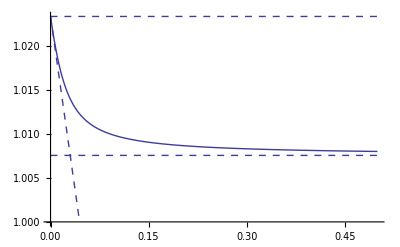

```mathematica
Show[
Plot[eigens,{R,0,1/2},PlotRange->{1,All}],
Plot[norec,{R,0,1/2},PlotRange->{1,All},PlotStyle->Dashed],
Plot[smallrec,{R,0,1/2},PlotRange->{1,All},PlotStyle->Dashed],
Plot[largerec,{R,0,1/2},PlotRange->{1,All},PlotStyle->Dashed]
]
```

```mathematica
Collect[-(Faa (-1+pAveM)^2 wa^2+pAveM wA (-2 FAa (-1+pAveM) wa+FAA pAveM wA))/(meanF ((-1+pAveM) wa-pAveM wA)),{meanF,FAA,FAa,Faa}]
```

(-(Faa (-1+pAveM)^2 wa^2)/((-1+pAveM) wa-pAveM wA)+(2 FAa (-1+pAveM) pAveM wa wA)/((-1+pAveM) wa-pAveM wA)-(FAA pAveM^2 wA^2)/((-1+pAveM) wa-pAveM wA))/meanF

#### IntStab

We check stability by perturbing the system slightly and checking that allele frequencies return. dev gives the initial deviations:

```mathematica
devXf=0.05;
devXm=-0.05;
devYm=0.05;

trypMXAf=0;
trypMXaf=0;
trypMXAm=0;
trypMXam=0;
trypMYAf=0;
trypMYaf=0;
trypMYAm=0;
trypMYam=0;
tmax=1000;
tinterval=10;
```

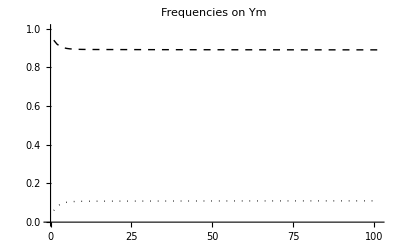

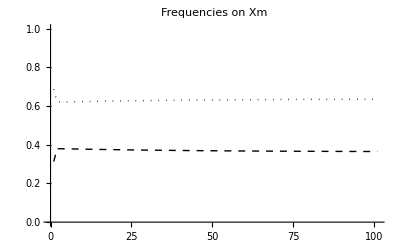

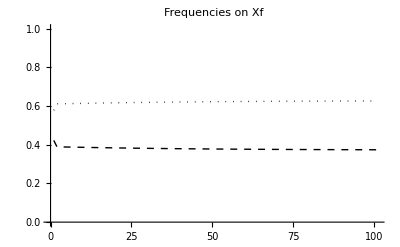

```mathematica
Show[
ListPlot[
Table[
nextYAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,initialpXf+devXf,(1-initialpXf)-devXf,trypMXAf,trypMXaf,(1-tryα)(initialpXm+devXm),(1-tryα)((1-initialpXm)-devXm),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,tryα*(initialpYm+devYm),tryα*((1-initialpYm)-devYm),trypMYAm,trypMYam]/tryα,
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dashed],
PlotRange->{0,1}],
ListPlot[
Table[
nextYam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,initialpXf+devXf,(1-initialpXf)-devXf,trypMXAf,trypMXaf,(1-tryα)(initialpXm+devXm),(1-tryα)((1-initialpXm)-devXm),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,tryα*(initialpYm+devYm),tryα*((1-initialpYm)-devYm),trypMYAm,trypMYam]/tryα,
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dotted],
PlotRange->{0,1}],
PlotLabel->"Frequencies on Ym"]

Show[
ListPlot[
Table[
nextXAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,initialpXf+devXf,(1-initialpXf)-devXf,trypMXAf,trypMXaf,(1-tryα)(initialpXm+devXm),(1-tryα)((1-initialpXm)-devXm),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,tryα*(initialpYm+devYm),tryα*((1-initialpYm)-devYm),trypMYAm,trypMYam]/(1-tryα),
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dashed],
PlotRange->{0,1}],
ListPlot[
Table[
nextXam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,initialpXf+devXf,(1-initialpXf)-devXf,trypMXAf,trypMXaf,(1-tryα)(initialpXm+devXm),(1-tryα)((1-initialpXm)-devXm),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,tryα*(initialpYm+devYm),tryα*((1-initialpYm)-devYm),trypMYAm,trypMYam]/(1-tryα),
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dotted],
PlotRange->{0,1}],
PlotLabel->"Frequencies on Xm"]

Show[
ListPlot[
Table[
nextXAf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,initialpXf+devXf,(1-initialpXf)-devXf,trypMXAf,trypMXaf,(1-tryα)(initialpXm+devXm),(1-tryα)((1-initialpXm)-devXm),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,tryα*(initialpYm+devYm),tryα*((1-initialpYm)-devYm),trypMYAm,trypMYam],
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dashed],
PlotRange->{0,1}],
ListPlot[
Table[
nextXaf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,initialpXf+devXf,(1-initialpXf)-devXf,trypMXAf,trypMXaf,(1-tryα)(initialpXm+devXm),(1-tryα)((1-initialpXm)-devXm),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,tryα*(initialpYm+devYm),tryα*((1-initialpYm)-devYm),trypMYAm,trypMYam],
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dotted],
PlotRange->{0,1}],
PlotLabel->"Frequencies on Xf"]
```

#### Ext Stab

First, we need to decide on the initial frequency of the new mutation. We will assume that it appear in linkage equilibrium with the old type by introducing it at the same frequencies.

```mathematica
pM=0.0001;

trypMXAf=pM initialpXf;
trypMXaf=pM (1-initialpXf);
trypMXAm=pM(1-tryα) initialpXm;
trypMXam=pM (1-tryα)(1-initialpXm);
trypMYAf=pM initialYAf;
trypMYaf=pM initialYaf;
trypMYAm=pM (tryα)initialpYm;
trypMYam=pM(tryα)(1-initialpYm);
```

Several other parameters are needed for the plots, including the time (tmax) and interval at which the frequencies are registered (tinterval).

```mathematica
tmax=5000;
tinterval=100;
tplotinterval=1000;

(*plot parameters*)
inches=72;
lwd=0.006;(*line thickness as fraction of plot width*)
ticksize={0,0.01};
xplotmin=0;
xplotmax=tmax;
yplotmin=0;
yplotmax=1;
xsize=5inches;
aspectratio=1/Sqrt[2];
```

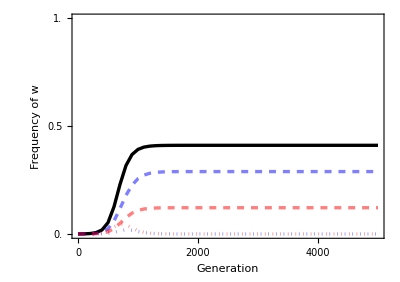

```mathematica
ListPlot[{Table[{t,
Total[{nextYAwf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextYawf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextXAwf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextXawf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextYAwf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextYawf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextXAwf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{
nextXawf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}]
},
Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotmin,yplotmax,0.5}]},
FrameTicksStyle->Directive[Black,Thickness[lwd]],
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Generation","Frequency of w"},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
Joined->True,
PlotStyle->{Directive[Black,Thickness[lwd]],
Directive[Blue,Opacity[0.5],Thickness[lwd],Dashed],
Directive[Blue,Opacity[0.5],Thickness[lwd],Dotted],
Directive[Red,Opacity[0.5],Thickness[lwd],Dashed],
Directive[Red,Opacity[0.5],Thickness[lwd],Dotted]},
PlotRange->{0,1}]
```

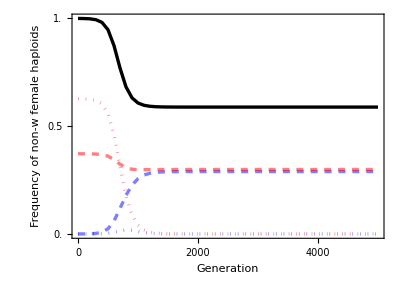

```mathematica
ListPlot[{Table[{t,
Total[{nextYAf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextYaf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextXAf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextXaf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextYAf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextYaf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextXAf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{
nextXaf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}]
},
Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotmin,yplotmax,0.5}]},
FrameTicksStyle->Directive[Black,Thickness[lwd]],
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Generation","Frequency of non-w female haploids"},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
Joined->True,
PlotStyle->{Directive[Black,Thickness[lwd]],
Directive[Blue,Opacity[0.5],Thickness[lwd],Dashed],
Directive[Blue,Opacity[0.5],Thickness[lwd],Dotted],
Directive[Red,Opacity[0.5],Thickness[lwd],Dashed],
Directive[Red,Opacity[0.5],Thickness[lwd],Dotted]},
PlotRange->{0,1}]
```

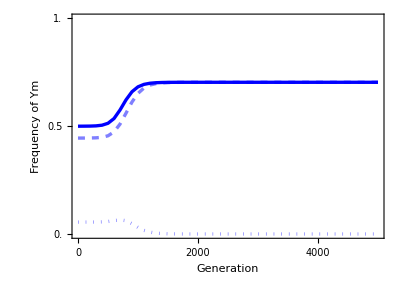

```mathematica
ListPlot[{Table[{t,
Total[{nextYAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextYam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextYAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextYam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}]
},
Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotmin,yplotmax,0.5}]},
FrameTicksStyle->Directive[Black,Thickness[lwd]],
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Generation","Frequency of Ym"},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
Joined->True,
PlotStyle->{Directive[Blue,Thickness[lwd]],
Directive[Blue,Opacity[0.5],Thickness[lwd],Dashed],
Directive[Blue,Opacity[0.5],Thickness[lwd],Dotted]},
PlotRange->{0,1}]
```

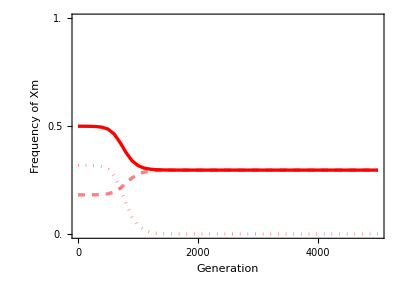

```mathematica
ListPlot[{Table[{t,
Total[{nextXAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextXam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextXAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextXam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}]
},
Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotmin,yplotmax,0.5}]},
FrameTicksStyle->Directive[Black,Thickness[lwd]],
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Generation","Frequency of Xm"},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
Joined->True,
PlotStyle->{Directive[Red,Thickness[lwd]],
Directive[Red,Opacity[0.5],Thickness[lwd],Dashed],
Directive[Red,Opacity[0.5],Thickness[lwd],Dotted]},
PlotRange->{0,1}]
```

#### Sex ratio plot

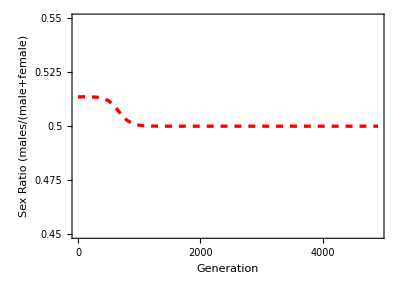

```mathematica
yplotminSexRatio=0.45;
yplotmaxSexRatio=0.55;
yplotintervalSexRatio=0.025;


ListPlot[{Table[{t,
Total[{
sexRatioAtBirth[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,1,tmax,tinterval}]
},
Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotminSexRatio,yplotmaxSexRatio,yplotintervalSexRatio}]},
FrameTicksStyle->Directive[Black,Thickness[lwd]],
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Generation","Sex Ratio (males/(male+female)"},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
Joined->True,
PlotStyle->{Directive[Red,Thickness[lwd],Dashed]},
PlotRange->{yplotminSexRatio,yplotmaxSexRatio}]
```

### Iterate Recursions (W appears to reach 50% after a long time, X not yet completely lost at the end of simulation though)

#### Parameters:

```mathematica
trysAf=0.07;
tryhAf=0.7;
tryhAm=0.7;
trysAm=0.15;
tryt=-0.1;

tryFAA=1+trysAf;
tryFAa=1+tryhAf trysAf;
tryFaa=1;
tryMAA=1+trysAm;
tryMAa=1+tryhAm trysAm;
tryMaa=1;
trywA=1+tryt;
trywa=1;
tryr=0.01;
tryα=0.5;
```

Our invasion analysis indicates that invasion should occur when the following is positive (which assumes that hAm=hAf)

```mathematica
((-1+2 tryr) trysAf (trysAf-trysAm) tryt^2)/(2 tryr (trysAf+trysAm)^2)
```

0.0566942

Also need to specify tryR for full system: (n.b., χ=r R)

```mathematica
tryR=0.5;
```

#### Find equilibrium (equil and sieve functions) [enter]

```mathematica
initialpXf=Flatten[sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryα]][[1]]
initialpXm=Flatten[sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryα]][[2]]
initialYAf=0;
initialYaf=0;
initialpYm=Flatten[sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryα]][[3]]
```

0.770449

0.77974

0.147112

#### IntStab

We check stability by perturbing the system slightly and checking that allele frequencies return. dev gives the initial deviations:

```mathematica
devXf=0.05;
devXm=-0.05;
devYm=0.05;

trypMXAf=0;
trypMXaf=0;
trypMXAm=0;
trypMXam=0;
trypMYAf=0;
trypMYaf=0;
trypMYAm=0;
trypMYam=0;
tmax=1000;
tinterval=10;
```

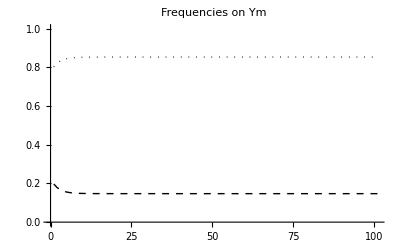

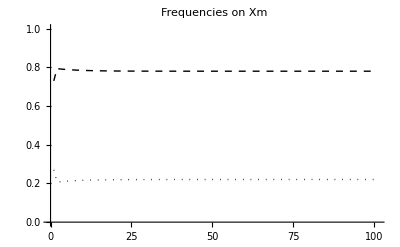

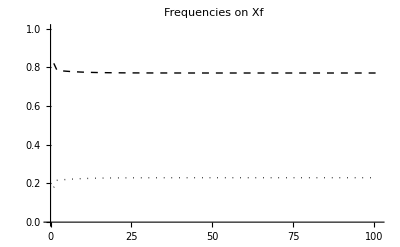

```mathematica
Show[
ListPlot[
Table[
nextYAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,initialpXf+devXf,(1-initialpXf)-devXf,trypMXAf,trypMXaf,(1-tryα)(initialpXm+devXm),(1-tryα)((1-initialpXm)-devXm),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,tryα*(initialpYm+devYm),tryα*((1-initialpYm)-devYm),trypMYAm,trypMYam]/tryα,
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dashed],
PlotRange->{0,1}],
ListPlot[
Table[
nextYam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,initialpXf+devXf,(1-initialpXf)-devXf,trypMXAf,trypMXaf,(1-tryα)(initialpXm+devXm),(1-tryα)((1-initialpXm)-devXm),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,tryα*(initialpYm+devYm),tryα*((1-initialpYm)-devYm),trypMYAm,trypMYam]/tryα,
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dotted],
PlotRange->{0,1}],
PlotLabel->"Frequencies on Ym"]

Show[
ListPlot[
Table[
nextXAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,initialpXf+devXf,(1-initialpXf)-devXf,trypMXAf,trypMXaf,(1-tryα)(initialpXm+devXm),(1-tryα)((1-initialpXm)-devXm),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,tryα*(initialpYm+devYm),tryα*((1-initialpYm)-devYm),trypMYAm,trypMYam]/(1-tryα),
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dashed],
PlotRange->{0,1}],
ListPlot[
Table[
nextXam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,initialpXf+devXf,(1-initialpXf)-devXf,trypMXAf,trypMXaf,(1-tryα)(initialpXm+devXm),(1-tryα)((1-initialpXm)-devXm),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,tryα*(initialpYm+devYm),tryα*((1-initialpYm)-devYm),trypMYAm,trypMYam]/(1-tryα),
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dotted],
PlotRange->{0,1}],
PlotLabel->"Frequencies on Xm"]

Show[
ListPlot[
Table[
nextXAf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,initialpXf+devXf,(1-initialpXf)-devXf,trypMXAf,trypMXaf,(1-tryα)(initialpXm+devXm),(1-tryα)((1-initialpXm)-devXm),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,tryα*(initialpYm+devYm),tryα*((1-initialpYm)-devYm),trypMYAm,trypMYam],
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dashed],
PlotRange->{0,1}],
ListPlot[
Table[
nextXaf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,initialpXf+devXf,(1-initialpXf)-devXf,trypMXAf,trypMXaf,(1-tryα)(initialpXm+devXm),(1-tryα)((1-initialpXm)-devXm),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,tryα*(initialpYm+devYm),tryα*((1-initialpYm)-devYm),trypMYAm,trypMYam],
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dotted],
PlotRange->{0,1}],
PlotLabel->"Frequencies on Xf"]
```

#### Ext Stab

First, we need to decide on the initial frequency of the new mutation. We will assume that it appear in linkage equilibrium with the old type by introducing it at the same frequencies.

```mathematica
pM=0.0001;

trypMXAf=pM initialpXf;
trypMXaf=pM (1-initialpXf);
trypMXAm=pM(1-tryα) initialpXm;
trypMXam=pM (1-tryα)(1-initialpXm);
trypMYAf=pM initialYAf;
trypMYaf=pM initialYaf;
trypMYAm=pM (tryα)initialpYm;
trypMYam=pM(tryα)(1-initialpYm);
```

Several other parameters are needed for the plots, including the time (tmax) and interval at which the frequencies are registered (tinterval).

```mathematica
tmax=70000;
tinterval=100;
tplotinterval=10000;

(*plot parameters*)
inches=72;
lwd=0.006;(*line thickness as fraction of plot width*)
ticksize={0,0.01};
xplotmin=0;
xplotmax=tmax;
yplotmin=0;
yplotmax=1;
xsize=5inches;
aspectratio=1/Sqrt[2];
```

```mathematica
ListPlot[{Table[{t,
Total[{nextYAwf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextYawf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextXAwf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextXawf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextYAwf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextYawf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextXAwf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{
nextXawf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}]
},
Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotmin,yplotmax,0.5}]},
FrameTicksStyle->Directive[Black,Thickness[lwd]],
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Generation","Frequency of w"},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
Joined->True,
PlotStyle->{Directive[Black,Thickness[lwd]],
Directive[Blue,Opacity[0.5],Thickness[lwd],Dashed],
Directive[Blue,Opacity[0.5],Thickness[lwd],Dotted],
Directive[Red,Opacity[0.5],Thickness[lwd],Dashed],
Directive[Red,Opacity[0.5],Thickness[lwd],Dotted]},
PlotRange->{0,1}]
```

$Aborted

Frequency of w at the end of the simulation:

```mathematica
Total[{nextYAwf[tmax,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextYawf[tmax,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextXAwf[tmax,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextXawf[tmax,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]
```

0.499104

which is increasing slightly.

```mathematica
Total[{nextYAwf[tmax,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextYawf[tmax,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextXAwf[tmax,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextXawf[tmax,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]-
Total[{nextYAwf[69000,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextYawf[69000,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextXAwf[69000,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextXawf[69000,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]
```

0.0000192522

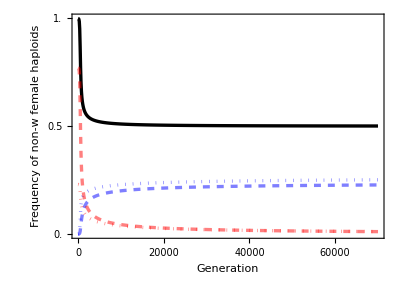

```mathematica
ListPlot[{Table[{t,
Total[{nextYAf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextYaf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextXAf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextXaf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextYAf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextYaf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextXAf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{
nextXaf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}]
},
Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotmin,yplotmax,0.5}]},
FrameTicksStyle->Directive[Black,Thickness[lwd]],
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Generation","Frequency of non-w female haploids"},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
Joined->True,
PlotStyle->{Directive[Black,Thickness[lwd]],
Directive[Blue,Opacity[0.5],Thickness[lwd],Dashed],
Directive[Blue,Opacity[0.5],Thickness[lwd],Dotted],
Directive[Red,Opacity[0.5],Thickness[lwd],Dashed],
Directive[Red,Opacity[0.5],Thickness[lwd],Dotted]},
PlotRange->{0,1}]
```

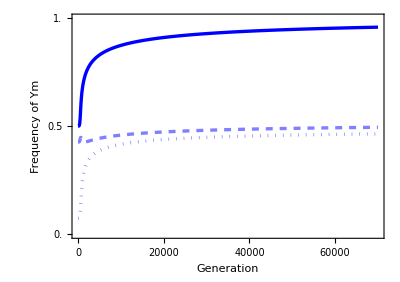

```mathematica
ListPlot[{Table[{t,
Total[{nextYAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextYam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextYam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextYAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}]
},
Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotmin,yplotmax,0.5}]},
FrameTicksStyle->Directive[Black,Thickness[lwd]],
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Generation","Frequency of Ym"},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
Joined->True,
PlotStyle->{Directive[Blue,Thickness[lwd]],
Directive[Blue,Opacity[0.5],Thickness[lwd],Dashed],
Directive[Blue,Opacity[0.5],Thickness[lwd],Dotted]},
PlotRange->{0,1}]
```

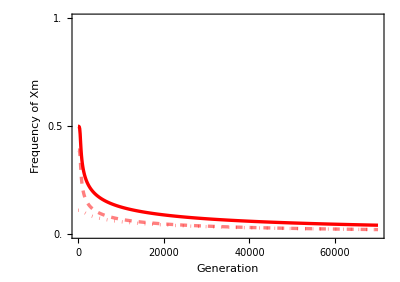

```mathematica
ListPlot[{Table[{t,
Total[{nextXAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextXam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextXAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextXam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}]
},
Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotmin,yplotmax,0.5}]},
FrameTicksStyle->Directive[Black,Thickness[lwd]],
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Generation","Frequency of Xm"},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
Joined->True,
PlotStyle->{Directive[Red,Thickness[lwd]],
Directive[Red,Opacity[0.5],Thickness[lwd],Dashed],
Directive[Red,Opacity[0.5],Thickness[lwd],Dotted]},
PlotRange->{0,1}]
```

#### Sex ratio plot

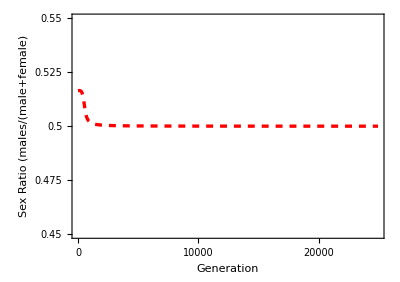

```mathematica
yplotminSexRatio=0.45;
yplotmaxSexRatio=0.55;
yplotintervalSexRatio=0.025;


ListPlot[{Table[{t,
Total[{
sexRatioAtBirth[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,1,tmax,tinterval}]
},
Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotminSexRatio,yplotmaxSexRatio,yplotintervalSexRatio}]},
FrameTicksStyle->Directive[Black,Thickness[lwd]],
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Generation","Sex Ratio (males/(male+female)"},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
Joined->True,
PlotStyle->{Directive[Red,Thickness[lwd],Dashed]},
PlotRange->{yplotminSexRatio,yplotmaxSexRatio}]
```

### Iterate Recursions (W invades but does not replace XY, polymorphic sex determination maintained without loss of variation)

#### Parameters:

```mathematica
trysAf=0.1;
tryhAf=0.7;
tryhAm=0.7;
trysAm=0.15;
tryt=-0.1;

tryFAA=1+trysAf;
tryFAa=1+tryhAf trysAf;
tryFaa=1;
tryMAA=1+trysAm;
tryMAa=1+tryhAm trysAm;
tryMaa=1;
trywA=1+tryt;
trywa=1;
tryr=0.01;
tryα=0.5;
```

Our invasion analysis indicates that invasion should occur when the following is positive (which assumes that hAm=hAf)

```mathematica
((-1+2 tryr) trysAf (trysAf-trysAm) tryt^2)/(2 tryr (trysAf+trysAm)^2)
```

0.0392

Also need to specify tryR for full system: (n.b., χ=r R)

```mathematica
tryR=1/2;
```

#### Find equilibrium (equil and sieve functions) [enter]

```mathematica
initialpXf=Flatten[sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryα]][[1]]
initialpXm=Flatten[sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryα]][[2]]
initialYAf=0;
initialYaf=0;
initialpYm=Flatten[sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryα]][[3]]
```

0.834904

0.840045

0.15054

#### IntStab

We check stability by perturbing the system slightly and checking that allele frequencies return. dev gives the initial deviations:

```mathematica
devXf=0.05;
devXm=-0.05;
devYm=0.05;

trypMXAf=0;
trypMXaf=0;
trypMXAm=0;
trypMXam=0;
trypMYAf=0;
trypMYaf=0;
trypMYAm=0;
trypMYam=0;
tmax=1000;
tinterval=10;
```

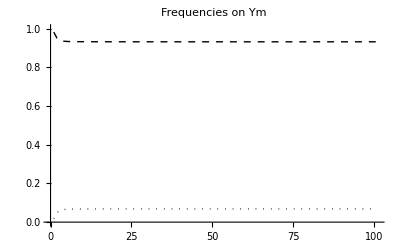

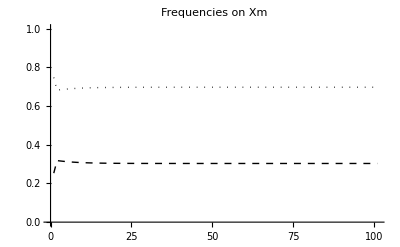

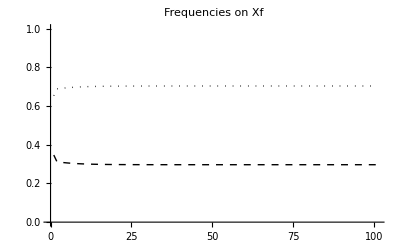

```mathematica
Show[
ListPlot[
Table[
nextYAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,initialpXf+devXf,(1-initialpXf)-devXf,trypMXAf,trypMXaf,(1-tryα)(initialpXm+devXm),(1-tryα)((1-initialpXm)-devXm),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,tryα*(initialpYm+devYm),tryα*((1-initialpYm)-devYm),trypMYAm,trypMYam]/tryα,
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dashed],
PlotRange->{0,1}],
ListPlot[
Table[
nextYam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,initialpXf+devXf,(1-initialpXf)-devXf,trypMXAf,trypMXaf,(1-tryα)(initialpXm+devXm),(1-tryα)((1-initialpXm)-devXm),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,tryα*(initialpYm+devYm),tryα*((1-initialpYm)-devYm),trypMYAm,trypMYam]/tryα,
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dotted],
PlotRange->{0,1}],
PlotLabel->"Frequencies on Ym"]

Show[
ListPlot[
Table[
nextXAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,initialpXf+devXf,(1-initialpXf)-devXf,trypMXAf,trypMXaf,(1-tryα)(initialpXm+devXm),(1-tryα)((1-initialpXm)-devXm),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,tryα*(initialpYm+devYm),tryα*((1-initialpYm)-devYm),trypMYAm,trypMYam]/(1-tryα),
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dashed],
PlotRange->{0,1}],
ListPlot[
Table[
nextXam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,initialpXf+devXf,(1-initialpXf)-devXf,trypMXAf,trypMXaf,(1-tryα)(initialpXm+devXm),(1-tryα)((1-initialpXm)-devXm),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,tryα*(initialpYm+devYm),tryα*((1-initialpYm)-devYm),trypMYAm,trypMYam]/(1-tryα),
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dotted],
PlotRange->{0,1}],
PlotLabel->"Frequencies on Xm"]

Show[
ListPlot[
Table[
nextXAf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,initialpXf+devXf,(1-initialpXf)-devXf,trypMXAf,trypMXaf,(1-tryα)(initialpXm+devXm),(1-tryα)((1-initialpXm)-devXm),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,tryα*(initialpYm+devYm),tryα*((1-initialpYm)-devYm),trypMYAm,trypMYam],
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dashed],
PlotRange->{0,1}],
ListPlot[
Table[
nextXaf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,initialpXf+devXf,(1-initialpXf)-devXf,trypMXAf,trypMXaf,(1-tryα)(initialpXm+devXm),(1-tryα)((1-initialpXm)-devXm),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,tryα*(initialpYm+devYm),tryα*((1-initialpYm)-devYm),trypMYAm,trypMYam],
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dotted],
PlotRange->{0,1}],
PlotLabel->"Frequencies on Xf"]
```

#### Ext Stab

First, we need to decide on the initial frequency of the new mutation. We will assume that it appear in linkage equilibrium with the old type by introducing it at the same frequencies.

```mathematica
pM=0.0001;

trypMXAf=pM initialpXf;
trypMXaf=pM (1-initialpXf);
trypMXAm=pM(1-tryα) initialpXm;
trypMXam=pM (1-tryα)(1-initialpXm);
trypMYAf=pM initialYAf;
trypMYaf=pM initialYaf;
trypMYAm=pM (tryα)initialpYm;
trypMYam=pM(tryα)(1-initialpYm);
```

Several other parameters are needed for the plots, including the time (tmax) and interval at which the frequencies are registered (tinterval).

```mathematica
tmax=10000;
tinterval=100;
tplotinterval=2500;

(*plot parameters*)
inches=72;
lwd=0.006;(*line thickness as fraction of plot width*)
ticksize={0,0.01};
xplotmin=0;
xplotmax=tmax;
yplotmin=0;
yplotmax=1;
xsize=5inches;
aspectratio=1/Sqrt[2];
```

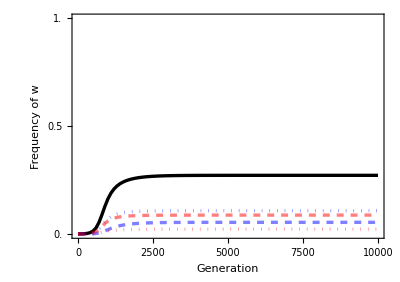

```mathematica
ListPlot[{Table[{t,
Total[{nextYAwf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextYawf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextXAwf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextXawf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextYAwf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextYawf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextXAwf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{
nextXawf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}]
},
Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotmin,yplotmax,0.5}]},
FrameTicksStyle->Directive[Black,Thickness[lwd]],
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Generation","Frequency of w"},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
Joined->True,
PlotStyle->{Directive[Black,Thickness[lwd]],
Directive[Blue,Opacity[0.5],Thickness[lwd],Dashed],
Directive[Blue,Opacity[0.5],Thickness[lwd],Dotted],
Directive[Red,Opacity[0.5],Thickness[lwd],Dashed],
Directive[Red,Opacity[0.5],Thickness[lwd],Dotted]},
PlotRange->{0,1}]
```

Frequency of w at the end of the simulation:

```mathematica
Total[{nextYAwf[tmax,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextYawf[tmax,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextXAwf[tmax,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextXawf[tmax,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]
```

0.272086

which is barely changing:

```mathematica
Total[{nextYAwf[tmax,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextYawf[tmax,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextXAwf[tmax,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextXawf[tmax,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]-
Total[{nextYAwf[tmax-1000,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextYawf[tmax-1000,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextXAwf[tmax-1000,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextXawf[tmax-1000,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]
```

3.70147×10^-8

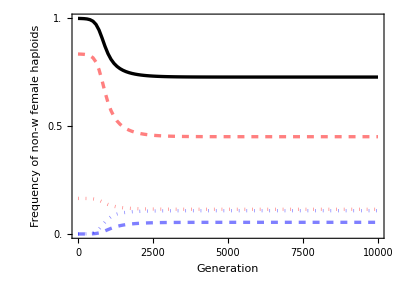

```mathematica
ListPlot[{Table[{t,
Total[{nextYAf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextYaf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextXAf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextXaf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextYAf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextYaf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextXAf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{
nextXaf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}]
},
Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotmin,yplotmax,0.5}]},
FrameTicksStyle->Directive[Black,Thickness[lwd]],
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Generation","Frequency of non-w female haploids"},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
Joined->True,
PlotStyle->{Directive[Black,Thickness[lwd]],
Directive[Blue,Opacity[0.5],Thickness[lwd],Dashed],
Directive[Blue,Opacity[0.5],Thickness[lwd],Dotted],
Directive[Red,Opacity[0.5],Thickness[lwd],Dashed],
Directive[Red,Opacity[0.5],Thickness[lwd],Dotted]},
PlotRange->{0,1}]
```

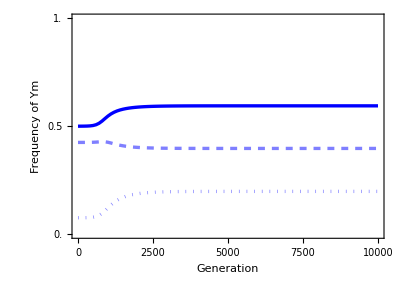

```mathematica
ListPlot[{Table[{t,
Total[{nextYAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextYam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextYam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextYAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}]
},
Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotmin,yplotmax,0.5}]},
FrameTicksStyle->Directive[Black,Thickness[lwd]],
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Generation","Frequency of Ym"},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
Joined->True,
PlotStyle->{Directive[Blue,Thickness[lwd]],
Directive[Blue,Opacity[0.5],Thickness[lwd],Dashed],
Directive[Blue,Opacity[0.5],Thickness[lwd],Dotted]},
PlotRange->{0,1}]
```

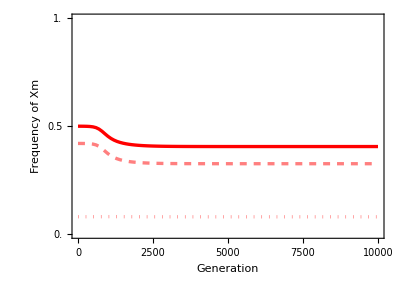

```mathematica
ListPlot[{Table[{t,
Total[{nextXAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextXam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextXAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextXam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}]
},
Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotmin,yplotmax,0.5}]},
FrameTicksStyle->Directive[Black,Thickness[lwd]],
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Generation","Frequency of Xm"},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
Joined->True,
PlotStyle->{Directive[Red,Thickness[lwd]],
Directive[Red,Opacity[0.5],Thickness[lwd],Dashed],
Directive[Red,Opacity[0.5],Thickness[lwd],Dotted]},
PlotRange->{0,1}]
```

#### Sex ratio plot

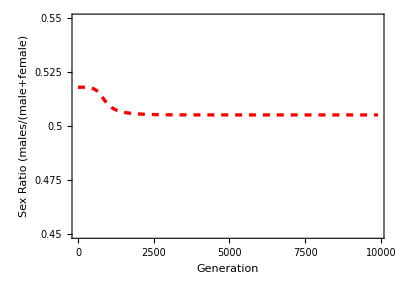

```mathematica
yplotminSexRatio=0.45;
yplotmaxSexRatio=0.55;
yplotintervalSexRatio=0.025;


ListPlot[{Table[{t,
Total[{
sexRatioAtBirth[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,1,tmax,tinterval}]
},
Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotminSexRatio,yplotmaxSexRatio,yplotintervalSexRatio}]},
FrameTicksStyle->Directive[Black,Thickness[lwd]],
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Generation","Sex Ratio (males/(male+female)"},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
Joined->True,
PlotStyle->{Directive[Red,Thickness[lwd],Dashed]},
PlotRange->{yplotminSexRatio,yplotmaxSexRatio}]
```

```mathematica
sexRatioAtBirth[tmax,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
```

0.505227

# neo-Y invades ZW

## (Actually, selection only occurs among female haploids and XY replaced with ZW)

Here we repeat the analysis from above but switch what the names mean. i.e., Y means W and X means Z. We will consider selection among the XX ‘eggs’ only (or selection only occurs among male ZZ haploids with new nomeclature). Since all haploids experiencing haploid selection have the same sex chromosome, the sex ratio among diploids is not affected by haploid selection.

## Recursions

### Haploid selection

We start with haploid selection, which occurs in sperm/pollen only. We assume male sperm/pollen compete for eggs, and that the allele at the autosomal locus determines their competitive ability (with relative fitnesses wA and wa). After selection on male gametes/pollen the frequencies of gametes in each sex are

```mathematica
(*mean fitness of eggs*)
wbarHap=(wA XAf+wa Xaf+wA XAwf+wa Xawf)+(wA YAf+wa Yaf+wA YAwf+wa Yawf);

(*non-mutant eggs*)
XAfs=wA XAf/wbarHap;
Xafs=wa Xaf/wbarHap;
YAfs=wA YAf/wbarHap;
Yafs=wa Yaf/wbarHap;

(*mutant eggs*)
XAwfs=wA XAwf/wbarHap;
Xawfs=wa Xawf/wbarHap;
YAwfs=wA YAwf/wbarHap;
Yawfs=wa Yawf/wbarHap;

(*non-mutant male gametes*)
XAms= XAm;
Xams= Xam;
YAms=  YAm;
Yams=  Yam;

(*mutant male gametes*)
XAwms= XAwm;
Xawms= Xawm;
YAwms=  YAwm;
Yawms=  Yawm;
```

Check that frequencies sum to one in each sex after haploid selection:

```mathematica
1==XAms+Xams+YAms+Yams+XAwms+Xawms+YAwms+Yawms/.Xam->1-XAm-Xawm-XAwm-YAm-Yam-Yawm-YAwm//Factor(*male gametes*)
1==XAfs+Xafs+XAwfs+Xawfs+YAfs+Yafs+YAwfs+Yawfs//Factor (*eggs*)
```

True

True

### Random mating

After random mating, the frequencies of the diploid genotypes are

```mathematica
(*X-Y males*)
XAYA=XAfs YAms+YAfs XAms;
XAYa=XAfs Yams+Yafs XAms;
XaYA=Xafs YAms+YAfs Xams;
XaYa=Xafs Yams+Yafs Xams;

(*Y-Y males*)
YAYA=YAfs YAms;
YAYa=YAfs Yams+Yafs YAms;
YaYa=Yafs Yams;

(*non-mutant females*)
XAXA=XAfs XAms;
XAXa=XAfs Xams+Xafs XAms ;
XaXa=Xafs Xams;

(*X-Xw females*)
XAwXA=XAwfs XAms+XAfs XAwms;
XAwXa=XAwfs Xams+Xafs XAwms ;
XAXaw=XAfs Xawms+Xawfs XAms;
XawXa=Xawfs Xams+Xafs Xawms;

(*Xw-Xw females*)
XAwXAw=XAwfs XAwms;
XAwXaw=XAwfs Xawms+Xawfs XAwms ;
XawXaw=Xawfs Xawms;

(*X-Yw females*)
XAwYA=XAwfs YAms+YAfs XAwms;
XAwYa=XAwfs Yams+Yafs XAwms;
XawYA=Xawfs YAms+YAfs Xawms;
XawYa=Xawfs Yams+Yafs Xawms;

(*Xw-Y females*)
XAYAw=XAfs YAwms+YAwfs XAms;
XAYaw=XAfs Yawms+Yawfs XAms ;
XaYAw=Xafs YAwms+YAwfs Xams ;
XaYaw=Xafs Yawms+Yawfs Xams;

(*Xw-Yw females*)
XAwYAw=XAwfs YAwms+YAwfs XAwms ;
XAwYaw=XAwfs Yawms+Yawfs XAwms ;
XawYAw=Xawfs YAwms+YAwfs Xawms ;
XawYaw=Xawfs Yawms+Yawfs Xawms;

(*Yw-Y females*)
YAwYA=YAwfs YAms+YAfs YAwms;
YAwYa=YAwfs Yams+Yafs YAwms;
YawYA=Yawfs YAms+YAfs Yawms;
YawYa=Yawfs Yams+Yafs Yawms;

(*Yw-Yw females*)
YAwYAw=YAwfs YAwms;
YAwYaw=YAwfs Yawms+Yawfs YAwms;
YawYaw=Yawfs Yawms;
```

Check that they sum to one

```mathematica
XAXA+XAXa+XaXa+XAYA+XAwXA+XAwXa+XAXaw+XawXa+XAwYA+XAwYa+XawYA+XawYa+XAYAw+XAYaw+XaYAw+XaYaw+XAYa+XaYA+XaYa+XAwYAw+XAwYaw+XawYAw+XawYaw+XAwXAw+XAwXaw+XawXaw+YAwYA+YAwYa+YawYA+YawYa+YAwYAw+YAwYaw+YawYaw+YAYA+YAYa+YaYa/.Xaf->1-XAf-Xawf-XAwf-YAf-Yaf-Yawf-YAwf//Factor
```

Xam+XAm+Xawm+XAwm+Yam+YAm+Yawm+YAwm

### Diploid selection

We next model selection in diploids, which can differ among the sexes. Let FAA, FAa, and Faa be the relative fitnesses of females homozygous for allele A, heterozygous, or homozygous for allele a at the autosomal locus. Similarly we use MAA, MAa, and Maa in males. Then after diploid selection the frequencies of the diploid genotypes in each sex are

```mathematica
(*mean male fitness*)
wbarM=
MAA XAYA+MAa (XAYa+XaYA)+Maa XaYa+
MAA YAYA+MAa YAYa+Maa YaYa;

(*non-mutant males*)
XAYAs=MAA XAYA/wbarM;
XAYas=MAa XAYa/wbarM;
XaYAs=MAa XaYA/wbarM;
XaYas=Maa XaYa/wbarM;

YAYAs=MAA YAYA/wbarM;
YAYas=MAa YAYa/wbarM;
YaYas=Maa YaYa/wbarM;

(*mean female fitness*)
wbarF=FAA XAXA+FAa XAXa+Faa XaXa+
FAA XAwXA+FAa(XAwXa+XAXaw)+Faa XawXa+
FAA XAwXAw+FAa XAwXaw+Faa XawXaw+
FAA XAwYA+FAa(XAwYa+XawYA)+Faa XawYa+
FAA XAYAw+FAa(XAYaw+XaYAw)+Faa XaYaw+
FAA XAwYAw+FAa(XAwYaw+XawYAw)+Faa XawYaw+
FAA YAwYA+FAa(YAwYa+YawYA)+Faa YawYa+
FAA YAwYAw+FAa YAwYaw+Faa YawYaw; 

(*females*)
XAXAs=FAA XAXA/wbarF;
XAXas=FAa XAXa/wbarF;
XaXas=Faa XaXa/wbarF;

(*X-Xw females*)
XAwXAs=FAA XAwXA/wbarF;
XAwXas=FAa XAwXa/wbarF;
XAXaws=FAa XAXaw/wbarF;
XawXas=Faa XawXa/wbarF;

(*X-Yw females*)
XAYAws=FAA XAYAw/wbarF;
XAYaws=FAa XAYaw/wbarF;
XaYAws=FAa XaYAw/wbarF;
XaYaws=Faa XaYaw/wbarF;

(*Xw-Y females*)
XAwYAs=FAA XAwYA/wbarF;
XAwYas=FAa XAwYa/wbarF;
XawYAs=FAa XawYA/wbarF;
XawYas=Faa XawYa/wbarF;

(*Xw-Xw females*)
XAwXAws=FAA XAwXAw/wbarF;
XAwXaws=FAa XAwXaw/wbarF;
XawXaws=Faa XawXaw/wbarF;

(*Xw-Yw females*)
XAwYAws=FAA XAwYAw/wbarF;
XAwYaws=FAa XAwYaw/wbarF;
XawYAws=FAa XawYAw/wbarF;
XawYaws=Faa XawYaw/wbarF;

(*Yw-Y females*)
YAwYAs=FAA YAwYA/wbarF;
YAwYas=FAa YAwYa/wbarF;
YawYAs=FAa YawYA/wbarF;
YawYas=Faa YawYa/wbarF;

(*Yw-Yw females*)
YAwYAws=FAA YAwYAw/wbarF;
YAwYaws=FAa YAwYaw/wbarF;
YawYaws=Faa YawYaw/wbarF;
```

Check that frequencies of diploid genotypes in each sex sum to one after diploid selection:

```mathematica
(*females*)
1==XAXAs+XAXas+XaXas+
XAwXAs+XAwXas+XAXaws+XawXas+
XAwXAws+XAwXaws+XawXaws+
XAwYAs+XAwYas+XawYAs+XawYas+
XAYAws+XAYaws+XaYAws+XaYaws+
XAwYAws+XAwYaws+XawYAws+XawYaws+
YAwYAs+YAwYas+YawYAs+YawYas+YAwYAws+YAwYaws+YawYaws//Factor
(*males*)
1==(
XAYAs+XAYas+XaYAs+XaYas+YAYAs+YAYas+YaYas)//Factor
```

True

True

### Meiosis

Finally, meiosis occurs. We have three recombination rates to consider (we assume no interference):

r: the recombination rate between the autosomal locus and and the original sex-determining locus
R: the recombination rate between the novel sex-determining locus and the autosomal locus
χ: the recombination rate between the novel sex-determingin locus and the original sex-determing locus

We also assume that males produce α% of their gametes with the Y allele (original sex chromosome drive if α≠1/2).
The frequencies of haploid genotypes in gametes from each at the start of the next generation are then

```mathematica
(*male haploids*)
XAmprime=(1-α)(XAYAs+XAYas(1-r)+r XaYAs);
Xamprime=(1-α)(XaYas+XaYAs(1-r)+r XAYas);
YAmprime=α(XAYAs+XaYAs(1-r)+XAYas r)+YAYAs+YAYas/2;
Yamprime=α(XaYas+XAYas(1-r)+XaYAs r)+YaYas+YAYas/2;

(*eggs*)
XAfprime=XAXAs+XAXas/2+
XAwXAs/2 +XAwXas (R)/2+XAXaws (1-R)/2+
(1-α)((XAYAws(1-(r+R-2χ))+XAwYAs (r+R-2χ))+
(XAYaws (1-(r+R-χ))+XawYAs(r-χ)+XaYAws(χ)+XAwYas(R-χ)));
Xafprime=XaXas+XAXas/2+
XawXas/2 +XAwXas (1-R)/2+XAXaws (R)/2+
(1-α)((XaYaws (1-(r+R-2χ))+XawYas(r+R-2χ))+
(XAYaws(χ)+XawYAs(R-χ)+XaYAws(1-(r+R-χ))+XAwYas(r-χ)));
XAwfprime=XAwXAws+XAwXaws/2+
XAwXAs/2 +XAwXas (1-R)/2+XAXaws (R)/2+
(1-α)((XAYAws((r+R-2χ))+XAwYAs (1-(r+R-2χ)))+
(XAYaws (R-χ)+XawYAs(χ)+XaYAws(r-χ)+XAwYas(1-(r+R-χ)))+
XAwYAws+XAwYaws(1-r)+XawYAws r);
Xawfprime=XawXaws+XAwXaws/2+
XawXas/2 +XAwXas (R)/2+XAXaws (1-R)/2+
(1-α)((XaYaws((r+R-2χ))+XawYas (1-(r+R-2χ)))+
(XAYaws (r-χ)+XawYAs(1-(r+R-χ))+XaYAws(R-χ)+XAwYas(χ))+
XawYaws+XawYAws(1-r)+XAwYaws r);

YAfprime=(α)((XAYAws((r+R-2χ))+XAwYAs (1-(r+R-2χ)))+
(XAYaws (r-χ)+XawYAs(1-(r+R-χ))+XaYAws(R-χ)+XAwYas(χ)))+
YAwYAs/2+YAwYas(R)/2+YawYAs(1-R)/2;
Yafprime=α((XaYaws((r+R-2χ))+XawYas (1-(r+R-2χ)))+
(XAYaws (R-χ)+XawYAs(χ)+XaYAws(r-χ)+XAwYas(1-(r+R-χ))))+
YawYas/2+YAwYas(1-R)/2+YawYAs(R)/2;
YAwfprime=α((XAYAws(1-(r+R-2χ))+XAwYAs ((r+R-2χ)))+
(XAYaws (χ)+XawYAs(R-χ)+XaYAws(1-(r+R-χ))+XAwYas(r-χ))+
XAwYAws+XAwYaws(r)+XawYAws (1-r))+
YAwYAs/2+YAwYas(1-R)/2+YawYAs(R)/2+
YAwYAws+YAwYaws/2;
Yawfprime=α((XaYaws(1-(r+R-2χ))+XawYas ((r+R-2χ)))+
(XAYaws (1-(r+R-χ))+XawYAs(r-χ)+XaYAws(χ)+XAwYas(R-χ))+
XawYaws+XawYAws(r)+XAwYaws (1-r))+
YawYas/2+YAwYas(R)/2+YawYAs(1-R)/2+
YawYaws+YAwYaws/2;
```

Check

```mathematica
1==XAfprime+Xafprime+XAwfprime+Xawfprime+YAfprime+Yafprime+YAwfprime+Yawfprime//Factor
1==XAmprime+Xamprime+YAmprime+Yamprime//Factor
```

True

True

## Resident equilibrium (weakselmod)

We first assume that the neoY is absent

```mathematica
subequil={
XAf->pXf,
Xaf->(1-pXf),
YAf->0,
Yaf->0,
XAm->pXm(1-α),
Xam->(1-pXm)(1-α),
YAm->pYm*α,
Yam->(1-pYm)*α,
XAwf->0,
Xawf->0,
XAwm->0,
Xawm->0,
YAwm->0,
Yawm->0,
YAwf->0,
Yawf->0
};
```

where pXf is the frequency of A in non-mutant eggs, pXm is the frequency of A in gametes from males with an X allele, and pY is the frequency of A in gametes from males with a Y allele.

We now wish to solve for the equilibrium frequencies of the haploid genotypes in gametes of each sex. Equilibrium is achieved when the following three equations are zero

```mathematica
differenceEqs={
XAfprime-XAf,
XAmprime-XAm,
YAmprime-YAm
}/.subequil;
```

To simplify the analysis we assume weak selection in both haploids (sperm/pollen) and diploids

```mathematica
weakselmod={
MAA->1+δMAA ϵ,
MAa->1+δMAa ϵ,
Maa->1+δMaa ϵ,
FAA->1+δFAA ϵ,
FAa->1+δFAa ϵ,
Faa->1+δFaa ϵ,
wA->1+δwA ϵ,
wa->1+δwa ϵ};
```

We can write the frequencies as Taylor series

```mathematica
frequenciessub={
pXf->pXf0+pXf1 ϵ,
pXm->pXm0+pXm1 ϵ,
pYm->pYm0+pYm1 ϵ
};
```

Without selection the recursions for the change in the frequencies are

```mathematica
differenceEqs0=Normal[Series[differenceEqs/.weakselmod/.frequenciessub,{ϵ,0,0}]]
```

{1/2 (-pXf0+pXm0),-pXm0+(pXf0-pXf0 r+pYm0 r) (1-α)+pXm0 α,pXf0 r α-pYm0 r α}

And at equilibrium we have

```mathematica
sol0=Solve[differenceEqs0==0,{pXf0,pXm0}]
```

{{pXf0→pYm0,pXm0→pYm0}}

So, with no selection, the equilibrium frequency of A in each gamete/pollen type is equal (and we call this pA).

Now, looking at only the first order selection terms, the recursions for the change in frequency of A in each gamete/pollen type are

```mathematica
differenceEqs1=Collect[Normal[Series[differenceEqs/.weakselmod/.frequenciessub/.sol0,{ϵ,0,1}]],ϵ,Factor]/.pYm0->pA//Flatten
```

{1/2 (-pXf1+pXm1-2 pA δFaa+4 pA^2 δFaa-2 pA^3 δFaa+2 pA δFAa-6 pA^2 δFAa+4 pA^3 δFAa+2 pA^2 δFAA-2 pA^3 δFAA-pA δwa+pA^2 δwa+pA δwA-pA^2 δwA) ϵ,(-1+α) (-pXf1+pXm1+pXf1 r-pYm1 r+pA δMaa-2 pA^2 δMaa+pA^3 δMaa-pA δMAa+3 pA^2 δMAa-2 pA^3 δMAa-pA^2 δMAA+pA^3 δMAA+pA δwa-pA^2 δwa-pA r δwa+pA^2 r δwa-pA δwA+pA^2 δwA+pA r δwA-pA^2 r δwA) ϵ,α (pXf1 r-pYm1 r-pA δMaa+2 pA^2 δMaa-pA^3 δMaa+pA δMAa-3 pA^2 δMAa+2 pA^3 δMAa+pA^2 δMAA-pA^3 δMAA-pA r δwa+pA^2 r δwa+pA r δwA-pA^2 r δwA) ϵ}

Instead of solving for the first order genotype frequencies we will instead solve for the difference in the frequency of A in the different gamete/pollen types.

The difference in the frequency of A with X in females and X in males is (at equilibrium to first order in selection)

```mathematica
eqdpAXfXm=Solve[differenceEqs1[[1]]==0/.pXf1->dpAXfXm+pXm1,dpAXfXm]//Flatten
```

{dpAXfXm→-2 pA δFaa+4 pA^2 δFaa-2 pA^3 δFaa+2 pA δFAa-6 pA^2 δFAa+4 pA^3 δFAa+2 pA^2 δFAA-2 pA^3 δFAA-pA δwa+pA^2 δwa+pA δwA-pA^2 δwA}

The difference in the frequency of A with X in males and Y is (at equilibrium to first order in selection)

```mathematica
eqdpAXmY=Solve[differenceEqs1[[2]]==0/.pXf1->dpAXfXm+pXm1/.eqdpAXfXm/.pXm1->dpAXmY+pYm1,dpAXmY]//Flatten
```

{dpAXmY→1/r(-2 pA δFaa+4 pA^2 δFaa-2 pA^3 δFaa+2 pA r δFaa-4 pA^2 r δFaa+2 pA^3 r δFaa+2 pA δFAa-6 pA^2 δFAa+4 pA^3 δFAa-2 pA r δFAa+6 pA^2 r δFAa-4 pA^3 r δFAa+2 pA^2 δFAA-2 pA^3 δFAA-2 pA^2 r δFAA+2 pA^3 r δFAA-pA δMaa+2 pA^2 δMaa-pA^3 δMaa+pA δMAa-3 pA^2 δMAa+2 pA^3 δMAa+pA^2 δMAA-pA^3 δMAA-2 pA δwa+2 pA^2 δwa+2 pA r δwa-2 pA^2 r δwa+2 pA δwA-2 pA^2 δwA-2 pA r δwA+2 pA^2 r δwA)}

The difference in the frequency of A with X in females and Y is (at equilibrium to first order in selection)

```mathematica
eqdpAXfY=Solve[differenceEqs1[[3]]==0/.pXf1->dpAXfY+pYm1,dpAXfY]//Flatten
```

{dpAXfY→(pA δMaa-2 pA^2 δMaa+pA^3 δMaa-pA δMAa+3 pA^2 δMAa-2 pA^3 δMAa-pA^2 δMAA+pA^3 δMAA+pA r δwa-pA^2 r δwa-pA r δwA+pA^2 r δwA)/r}

So then, to first order, the equilibrium frequencies of A in gametes of each type are

```mathematica
eqpXf=pXf0+ϵ dpAXfXm+ϵ dpAXmY/.sol0/.pYm0->pA/.eqdpAXfXm/.eqdpAXmY//Simplify
```

{1/r pA (-(-1+pA) (2 (-1+pA) δFaa+(2-4 pA) δFAa+2 pA δFAA-δMaa+pA δMaa+δMAa-2 pA δMAa+pA δMAA-2 δwa+2 δwA) ϵ+r (1+(-1+pA) δwA ϵ+δwa (ϵ-pA ϵ)))}

```mathematica
eqpXm=pXm0-ϵ dpAXfXm+ϵ dpAXfY/.sol0/.pYm0->pA/.eqdpAXfXm/.eqdpAXfY//Simplify
```

{1/r pA ((-1+pA) ((-1+pA) δMaa+δMAa-2 pA δMAa+pA δMAA) ϵ+r (1+2 (-1+pA)^2 δFaa ϵ-2 (1-3 pA+2 pA^2) δFAa ϵ-2 pA δFAA ϵ+2 pA^2 δFAA ϵ+2 δwa ϵ-2 pA δwa ϵ-2 δwA ϵ+2 pA δwA ϵ))}

```mathematica
eqpY=pYm0+ϵ dpAXfXm-ϵ dpAXfY/.sol0/.pYm0->pA/.eqdpAXfY/.eqdpAXfXm//Simplify
```

{1/r pA (-(-1+pA) ((-1+pA) δMaa+δMAa-2 pA δMAa+pA δMAA) ϵ+r (1-2 (-1+pA)^2 δFaa ϵ+2 (1-3 pA+2 pA^2) δFAa ϵ+2 pA δFAA ϵ-2 pA^2 δFAA ϵ-2 δwa ϵ+2 pA δwa ϵ+2 δwA ϵ-2 pA δwA ϵ))}

The recursion for pA is given by

```mathematica
dpA=Collect[Normal[Series[ (2XAfprime+XAmprime/(1-α)+YAmprime/α)-(2XAf+XAm/(1-α)+YAm/α)/.weakselmod/.subequil/.pXf->eqpXf/.pXm->eqpXm/.pYm->eqpY,{ϵ,0,1}]]/4,ϵ,Simplify]/.ϵ->1//Flatten
```

{-1/2 (-1+pA) pA ((-1+pA) δFaa+δFAa-2 pA δFAa+pA δFAA-δMaa+pA δMaa+δMAa-2 pA δMAa+pA δMAA-δwa+δwA)}

And at equilibrium we have

```mathematica
equilpA=Solve[dpA==0,pA]
```

{{pA→0},{pA→1},{pA→(δFaa-δFAa+δMaa-δMAa+δwa-δwA)/(δFaa-2 δFAa+δFAA+δMaa-2 δMAa+δMAA)}}

Notice that when t=0 we have equation “avgpASubs” in van Doorn & Kirkpatrick 2007 (SOM page 6). Sperm/pollen selection acts to increase the frequency of A (if selected for, t>0).

## External stability (weakselmod)

Here we are interested in the ability of a rare y mutant to invade the non-mutant resident population at equilibrium.

Remember that we don’t have recursions for XAyf or Xayf because y is a dominant male determining gene. However, we allowed these genotypes to create zygotes so we can include them in the stability matrix (with frequencies of 0 at the start of the next generation). The Jacobian for the mutants is

```mathematica
XAwmprime=0;
Xawmprime=0;
YAwmprime=0;
Yawmprime=0;
```

```mathematica
matExtFull=Transpose[{
D[{YAfprime,Yafprime,XAwfprime,Xawfprime,YAwfprime,Yawfprime,XAwmprime,Xawmprime,YAwmprime,Yawmprime},YAf],
D[{YAfprime,Yafprime,XAwfprime,Xawfprime,YAwfprime,Yawfprime,XAwmprime,Xawmprime,YAwmprime,Yawmprime},Yaf],
D[{YAfprime,Yafprime,XAwfprime,Xawfprime,YAwfprime,Yawfprime,XAwmprime,Xawmprime,YAwmprime,Yawmprime},XAwf],
D[{YAfprime,Yafprime,XAwfprime,Xawfprime,YAwfprime,Yawfprime,XAwmprime,Xawmprime,YAwmprime,Yawmprime},Xawf],
D[{YAfprime,Yafprime,XAwfprime,Xawfprime,YAwfprime,Yawfprime,XAwmprime,Xawmprime,YAwmprime,Yawmprime},YAwf],
D[{YAfprime,Yafprime,XAwfprime,Xawfprime,YAwfprime,Yawfprime,XAwmprime,Xawmprime,YAwmprime,Yawmprime},Yawf],
D[{YAfprime,Yafprime,XAwfprime,Xawfprime,YAwfprime,Yawfprime,XAwmprime,Xawmprime,YAwmprime,Yawmprime},XAwm],
D[{YAfprime,Yafprime,XAwfprime,Xawfprime,YAwfprime,Yawfprime,XAwmprime,Xawmprime,YAwmprime,Yawmprime},Xawm],
D[{YAfprime,Yafprime,XAwfprime,Xawfprime,YAwfprime,Yawfprime,XAwmprime,Xawmprime,YAwmprime,Yawmprime},YAwm],
D[{YAfprime,Yafprime,XAwfprime,Xawfprime,YAwfprime,Yawfprime,XAwmprime,Xawmprime,YAwmprime,Yawmprime},Yawm]
}]/.subequil//Factor;
```

Fairly certain we don’t need the first 2 columns or the last 4 rows...

```mathematica
MatrixForm[matExtFull]
```

(0 | 0 | -(wA α^2 (-FAA pYm+FAA pYm r+FAA pYm R-FAa χ+FAa pYm χ-2 FAA pYm χ))/((-Faa wa+Faa pXf wa+Faa pXm wa-FAa pXm wa-Faa pXf pXm wa+FAa pXf pXm wa-FAa pXf wA+FAa pXf pXm wA-FAA pXf pXm wA) (-1+α)) | -(FAa pYm wa α^2 (-1+r+R-χ))/((-Faa wa+Faa pXf wa+Faa pXm wa-FAa pXm wa-Faa pXf pXm wa+FAa pXf pXm wa-FAa pXf wA+FAa pXf pXm wA-FAA pXf pXm wA) (-1+α)) | -(wA α (FAA pYm+2 FAA pXm r+3 FAa R-2 FAa pXm R+2 FAA pXm R-FAa pYm R-2 FAA pXm r α-2 FAa R α+2 FAa pXm R α-2 FAA pXm R α-2 FAa χ+2 FAa pXm χ-4 FAA pXm χ+2 FAa α χ-2 FAa pXm α χ+4 FAA pXm α χ))/(2 (Faa wa-Faa pXf wa-Faa pXm wa+FAa pXm wa+Faa pXf pXm wa-FAa pXf pXm wa+FAa pXf wA-FAa pXf pXm wA+FAA pXf pXm wA) (-1+α)) | -(FAa wa α (-pYm-2 pXm r+pYm R+2 pXm r α+2 pXm χ-2 pXm α χ))/(2 (-Faa wa+Faa pXf wa+Faa pXm wa-FAa pXm wa-Faa pXf pXm wa+FAa pXf pXm wa-FAa pXf wA+FAa pXf pXm wA-FAA pXf pXm wA) (-1+α)) | 0 | 0 | -(α (FAa R wa-FAa pXf R wa+FAA pXf r wA+FAA pXf R wA-FAa wa χ+FAa pXf wa χ-2 FAA pXf wA χ))/((Faa wa-Faa pXf wa-Faa pXm wa+FAa pXm wa+Faa pXf pXm wa-FAa pXf pXm wa+FAa pXf wA-FAa pXf pXm wA+FAA pXf pXm wA) (-1+α)) | (FAa pXf wA α (r-χ))/((-Faa wa+Faa pXf wa+Faa pXm wa-FAa pXm wa-Faa pXf pXm wa+FAa pXf pXm wa-FAa pXf wA+FAa pXf pXm wA-FAA pXf pXm wA) (-1+α))
0 | 0 | (FAa (-1+pYm) wA α^2 (-1+r+R-χ))/((-Faa wa+Faa pXf wa+Faa pXm wa-FAa pXm wa-Faa pXf pXm wa+FAa pXf pXm wa-FAa pXf wA+FAa pXf pXm wA-FAA pXf pXm wA) (-1+α)) | (wa α^2 (Faa-Faa pYm-Faa r+Faa pYm r-Faa R+Faa pYm R+2 Faa χ-2 Faa pYm χ+FAa pYm χ))/((-Faa wa+Faa pXf wa+Faa pXm wa-FAa pXm wa-Faa pXf pXm wa+FAa pXf pXm wa-FAa pXf wA+FAa pXf pXm wA-FAA pXf pXm wA) (-1+α)) | (FAa wA α (1-pYm+2 r-2 pXm r-R+pYm R-2 r α+2 pXm r α-2 χ+2 pXm χ+2 α χ-2 pXm α χ))/(2 (-Faa wa+Faa pXf wa+Faa pXm wa-FAa pXm wa-Faa pXf pXm wa+FAa pXf pXm wa-FAa pXf wA+FAa pXf pXm wA-FAA pXf pXm wA) (-1+α)) | (wa α (-Faa+Faa pYm-2 Faa r+2 Faa pXm r-2 Faa R+2 Faa pXm R-2 FAa pXm R-FAa pYm R+2 Faa r α-2 Faa pXm r α+2 Faa R α-2 Faa pXm R α+2 FAa pXm R α+4 Faa χ-4 Faa pXm χ+2 FAa pXm χ-4 Faa α χ+4 Faa pXm α χ-2 FAa pXm α χ))/(2 (Faa wa-Faa pXf wa-Faa pXm wa+FAa pXm wa+Faa pXf pXm wa-FAa pXf pXm wa+FAa pXf wA-FAa pXf pXm wA+FAA pXf pXm wA) (-1+α)) | 0 | 0 | -(FAa (-1+pXf) wa α (r-χ))/((-Faa wa+Faa pXf wa+Faa pXm wa-FAa pXm wa-Faa pXf pXm wa+FAa pXf pXm wa-FAa pXf wA+FAa pXf pXm wA-FAA pXf pXm wA) (-1+α)) | (α (-Faa r wa+Faa pXf r wa-Faa R wa+Faa pXf R wa-FAa pXf R wA+2 Faa wa χ-2 Faa pXf wa χ+FAa pXf wA χ))/((Faa wa-Faa pXf wa-Faa pXm wa+FAa pXm wa+Faa pXf pXm wa-FAa pXf pXm wa+FAa pXf wA-FAa pXf pXm wA+FAA pXf pXm wA) (-1+α))
0 | 0 | (wA (FAa-FAa pXm+FAA pXm-FAa R+FAa pXm R+2 FAa α-2 FAa pYm α+2 FAA pYm α-2 FAa r α+2 FAa pYm r α-2 FAA pYm r α-2 FAa R α+2 FAa pYm R α-2 FAA pYm R α+2 FAa α χ-2 FAa pYm α χ+4 FAA pYm α χ))/(2 (Faa wa-Faa pXf wa-Faa pXm wa+FAa pXm wa+Faa pXf pXm wa-FAa pXf pXm wa+FAa pXf wA-FAa pXf pXm wA+FAA pXf pXm wA)) | -(FAa wa (pXm R+2 pYm α χ))/(2 (-Faa wa+Faa pXf wa+Faa pXm wa-FAa pXm wa-Faa pXf pXm wa+FAa pXf pXm wa-FAa pXf wA+FAa pXf pXm wA-FAA pXf pXm wA)) | -(wA (-1+α) (FAa r-FAa pXm r+FAA pXm r+FAA pXm R-FAa χ+FAa pXm χ-2 FAA pXm χ))/(Faa wa-Faa pXf wa-Faa pXm wa+FAa pXm wa+Faa pXf pXm wa-FAa pXf pXm wa+FAa pXf wA-FAa pXf pXm wA+FAA pXf pXm wA) | (FAa pXm wa (-1+α) (R-χ))/(-Faa wa+Faa pXf wa+Faa pXm wa-FAa pXm wa-Faa pXf pXm wa+FAa pXf pXm wa-FAa pXf wA+FAa pXf pXm wA-FAA pXf pXm wA) | (FAa wa-FAa pXf wa-FAa R wa+FAa pXf R wa+FAA pXf wA)/(2 (-Faa wa+Faa pXf wa+Faa pXm wa-FAa pXm wa-Faa pXf pXm wa+FAa pXf pXm wa-FAa pXf wA+FAa pXf pXm wA-FAA pXf pXm wA) (-1+α)) | (FAa pXf R wA)/(2 (-Faa wa+Faa pXf wa+Faa pXm wa-FAa pXm wa-Faa pXf pXm wa+FAa pXf pXm wa-FAa pXf wA+FAa pXf pXm wA-FAA pXf pXm wA) (-1+α)) | (FAa r wa-FAa pXf r wa+FAA pXf r wA+FAA pXf R wA-FAa wa χ+FAa pXf wa χ-2 FAA pXf wA χ)/(Faa wa-Faa pXf wa-Faa pXm wa+FAa pXm wa+Faa pXf pXm wa-FAa pXf pXm wa+FAa pXf wA-FAa pXf pXm wA+FAA pXf pXm wA) | -(FAa pXf wA (R-χ))/(-Faa wa+Faa pXf wa+Faa pXm wa-FAa pXm wa-Faa pXf pXm wa+FAa pXf pXm wa-FAa pXf wA+FAa pXf pXm wA-FAA pXf pXm wA)
0 | 0 | (FAa wA (-R+pXm R-2 α χ+2 pYm α χ))/(2 (-Faa wa+Faa pXf wa+Faa pXm wa-FAa pXm wa-Faa pXf pXm wa+FAa pXf pXm wa-FAa pXf wA+FAa pXf pXm wA-FAA pXf pXm wA)) | -(wa (-Faa+Faa pXm-FAa pXm+FAa pXm R-2 Faa α+2 Faa pYm α-2 FAa pYm α+2 Faa r α-2 Faa pYm r α+2 FAa pYm r α+2 Faa R α-2 Faa pYm R α+2 FAa pYm R α-4 Faa α χ+4 Faa pYm α χ-2 FAa pYm α χ))/(2 (Faa wa-Faa pXf wa-Faa pXm wa+FAa pXm wa+Faa pXf pXm wa-FAa pXf pXm wa+FAa pXf wA-FAa pXf pXm wA+FAA pXf pXm wA)) | -(FAa (-1+pXm) wA (-1+α) (R-χ))/(-Faa wa+Faa pXf wa+Faa pXm wa-FAa pXm wa-Faa pXf pXm wa+FAa pXf pXm wa-FAa pXf wA+FAa pXf pXm wA-FAA pXf pXm wA) | (wa (-1+α) (-Faa r+Faa pXm r-FAa pXm r-Faa R+Faa pXm R+2 Faa χ-2 Faa pXm χ+FAa pXm χ))/(Faa wa-Faa pXf wa-Faa pXm wa+FAa pXm wa+Faa pXf pXm wa-FAa pXf pXm wa+FAa pXf wA-FAa pXf pXm wA+FAA pXf pXm wA) | -(FAa (-1+pXf) R wa)/(2 (-Faa wa+Faa pXf wa+Faa pXm wa-FAa pXm wa-Faa pXf pXm wa+FAa pXf pXm wa-FAa pXf wA+FAa pXf pXm wA-FAA pXf pXm wA) (-1+α)) | (-Faa wa+Faa pXf wa-FAa pXf wA+FAa pXf R wA)/(2 (Faa wa-Faa pXf wa-Faa pXm wa+FAa pXm wa+Faa pXf pXm wa-FAa pXf pXm wa+FAa pXf wA-FAa pXf pXm wA+FAA pXf pXm wA) (-1+α)) | (FAa (-1+pXf) wa (R-χ))/(-Faa wa+Faa pXf wa+Faa pXm wa-FAa pXm wa-Faa pXf pXm wa+FAa pXf pXm wa-FAa pXf wA+FAa pXf pXm wA-FAA pXf pXm wA) | -(-Faa r wa+Faa pXf r wa-Faa R wa+Faa pXf R wa-FAa pXf r wA+2 Faa wa χ-2 Faa pXf wa χ+FAa pXf wA χ)/(Faa wa-Faa pXf wa-Faa pXm wa+FAa pXm wa+Faa pXf pXm wa-FAa pXf pXm wa+FAa pXf wA-FAa pXf pXm wA+FAA pXf pXm wA)
0 | 0 | -(wA α^2 (FAa r-FAa pYm r+FAA pYm r+FAA pYm R-FAa χ+FAa pYm χ-2 FAA pYm χ))/((Faa wa-Faa pXf wa-Faa pXm wa+FAa pXm wa+Faa pXf pXm wa-FAa pXf pXm wa+FAa pXf wA-FAa pXf pXm wA+FAA pXf pXm wA) (-1+α)) | (FAa pYm wa α^2 (R-χ))/((-Faa wa+Faa pXf wa+Faa pXm wa-FAa pXm wa-Faa pXf pXm wa+FAa pXf pXm wa-FAa pXf wA+FAa pXf pXm wA-FAA pXf pXm wA) (-1+α)) | -(wA α (3 FAa-2 FAa pXm+2 FAA pXm-FAa pYm+FAA pYm-2 FAa r+2 FAa pXm r-2 FAA pXm r-3 FAa R+2 FAa pXm R-2 FAA pXm R+FAa pYm R-2 FAa α+2 FAa pXm α-2 FAA pXm α+2 FAa r α-2 FAa pXm r α+2 FAA pXm r α+2 FAa R α-2 FAa pXm R α+2 FAA pXm R α+2 FAa χ-2 FAa pXm χ+4 FAA pXm χ-2 FAa α χ+2 FAa pXm α χ-4 FAA pXm α χ))/(2 (Faa wa-Faa pXf wa-Faa pXm wa+FAa pXm wa+Faa pXf pXm wa-FAa pXf pXm wa+FAa pXf wA-FAa pXf pXm wA+FAA pXf pXm wA) (-1+α)) | (FAa wa α (pYm R+2 pXm χ-2 pXm α χ))/(2 (-Faa wa+Faa pXf wa+Faa pXm wa-FAa pXm wa-Faa pXf pXm wa+FAa pXf pXm wa-FAa pXf wA+FAa pXf pXm wA-FAA pXf pXm wA) (-1+α)) | 0 | 0 | (α (FAa wa-FAa pXf wa-FAa r wa+FAa pXf r wa-FAa R wa+FAa pXf R wa+FAA pXf wA-FAA pXf r wA-FAA pXf R wA+FAa wa χ-FAa pXf wa χ+2 FAA pXf wA χ))/((-Faa wa+Faa pXf wa+Faa pXm wa-FAa pXm wa-Faa pXf pXm wa+FAa pXf pXm wa-FAa pXf wA+FAa pXf pXm wA-FAA pXf pXm wA) (-1+α)) | (FAa pXf wA α χ)/((-Faa wa+Faa pXf wa+Faa pXm wa-FAa pXm wa-Faa pXf pXm wa+FAa pXf pXm wa-FAa pXf wA+FAa pXf pXm wA-FAA pXf pXm wA) (-1+α))
0 | 0 | -(FAa (-1+pYm) wA α^2 (R-χ))/((-Faa wa+Faa pXf wa+Faa pXm wa-FAa pXm wa-Faa pXf pXm wa+FAa pXf pXm wa-FAa pXf wA+FAa pXf pXm wA-FAA pXf pXm wA) (-1+α)) | (wa α^2 (-Faa r+Faa pYm r-FAa pYm r-Faa R+Faa pYm R+2 Faa χ-2 Faa pYm χ+FAa pYm χ))/((Faa wa-Faa pXf wa-Faa pXm wa+FAa pXm wa+Faa pXf pXm wa-FAa pXf pXm wa+FAa pXf wA-FAa pXf pXm wA+FAA pXf pXm wA) (-1+α)) | -(FAa wA α (-R+pYm R-2 χ+2 pXm χ+2 α χ-2 pXm α χ))/(2 (-Faa wa+Faa pXf wa+Faa pXm wa-FAa pXm wa-Faa pXf pXm wa+FAa pXf pXm wa-FAa pXf wA+FAa pXf pXm wA-FAA pXf pXm wA) (-1+α)) | (wa α (-3 Faa+2 Faa pXm-2 FAa pXm+Faa pYm-FAa pYm+2 Faa r-2 Faa pXm r+2 FAa pXm r+2 Faa R-2 Faa pXm R+2 FAa pXm R+FAa pYm R+2 Faa α-2 Faa pXm α+2 FAa pXm α-2 Faa r α+2 Faa pXm r α-2 FAa pXm r α-2 Faa R α+2 Faa pXm R α-2 FAa pXm R α-4 Faa χ+4 Faa pXm χ-2 FAa pXm χ+4 Faa α χ-4 Faa pXm α χ+2 FAa pXm α χ))/(2 (Faa wa-Faa pXf wa-Faa pXm wa+FAa pXm wa+Faa pXf pXm wa-FAa pXf pXm wa+FAa pXf wA-FAa pXf pXm wA+FAA pXf pXm wA) (-1+α)) | 0 | 0 | -(FAa (-1+pXf) wa α χ)/((-Faa wa+Faa pXf wa+Faa pXm wa-FAa pXm wa-Faa pXf pXm wa+FAa pXf pXm wa-FAa pXf wA+FAa pXf pXm wA-FAA pXf pXm wA) (-1+α)) | -(α (-Faa wa+Faa pXf wa+Faa r wa-Faa pXf r wa+Faa R wa-Faa pXf R wa-FAa pXf wA+FAa pXf r wA+FAa pXf R wA-2 Faa wa χ+2 Faa pXf wa χ-FAa pXf wA χ))/((-Faa wa+Faa pXf wa+Faa pXm wa-FAa pXm wa-Faa pXf pXm wa+FAa pXf pXm wa-FAa pXf wA+FAa pXf pXm wA-FAA pXf pXm wA) (-1+α))
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
charpolyExt=Det[matExtFull-IdentityMatrix[10]*λ];
```

### Weak linkage (r and R of order ~1)

Solving for the eigenvalues gives

```mathematica
Normal[Series[charpolyExt/.weakselmod,{ϵ,0,0}]]//Factor;
Solve[%==0,λ]//Flatten
```

{λ→0,λ→0,λ→0,λ→0,λ→0,λ→0,λ→1/(4 (-1+α))(-1+R-4 α+4 r α+4 R α+4 α^2-4 r α^2-4 R α^2-4 α χ+4 α^2 χ-√(1-2 R+R^2-4 α+8 R α-4 R^2 α+4 α^2+16 r^2 α^2-8 R α^2+4 R^2 α^2-32 r^2 α^3+16 r^2 α^4-32 r α^2 χ+64 r α^3 χ-32 r α^4 χ+16 α^2 χ^2-32 α^3 χ^2+16 α^4 χ^2)),λ→1/(4 (-1+α))(-1+R-4 α+4 r α+4 R α+4 α^2-4 r α^2-4 R α^2-4 α χ+4 α^2 χ+√(1-2 R+R^2-4 α+8 R α-4 R^2 α+4 α^2+16 r^2 α^2-8 R α^2+4 R^2 α^2-32 r^2 α^3+16 r^2 α^4-32 r α^2 χ+64 r α^3 χ-32 r α^4 χ+16 α^2 χ^2-32 α^3 χ^2+16 α^4 χ^2)),λ→1/(2 (4-4 α))(2+8 α-8 r α-8 R α-8 α^2+8 r α^2+8 R α^2+16 α χ-16 α^2 χ-√((-2-8 α+8 r α+8 R α+8 α^2-8 r α^2-8 R α^2-16 α χ+16 α^2 χ)^2-4 (4-4 α) (3 α-2 r α-2 R α+4 α^2-8 r α^2-8 R α^2-4 α^3+8 r α^3+8 R α^3+4 α χ+16 α^2 χ-16 α^3 χ))),λ→1/(2 (4-4 α))(2+8 α-8 r α-8 R α-8 α^2+8 r α^2+8 R α^2+16 α χ-16 α^2 χ+√((-2-8 α+8 r α+8 R α+8 α^2-8 r α^2-8 R α^2-16 α χ+16 α^2 χ)^2-4 (4-4 α) (3 α-2 r α-2 R α+4 α^2-8 r α^2-8 R α^2-4 α^3+8 r α^3+8 R α^3+4 α χ+16 α^2 χ-16 α^3 χ)))}

The zero order effect is on sex ratio.

Here we will assume that any deviations from α=1/2 are on the same order as haploid and diploid selection ϵ. Then the eigenvalues with no selection are

```mathematica
Normal[Series[charpolyExt/.weakselmod/.α->1/2+δα*ϵ,{ϵ,0,0}]]//Factor;
Solve[%==0,λ]//Flatten
```

{λ→0,λ→0,λ→0,λ→0,λ→0,λ→0,λ→1,λ→1-R,λ→1-r-R+χ,λ→1-r-R+2 χ}

On this order the leading eigenvalue is λ=1.

On the first order the eiganvalue is

```mathematica
Normal[Series[charpolyExt/.weakselmod/.α->1/2+δα*ϵ/.λ->1+δλ*ϵ/.frequenciessub/.sol0/.pYm0->pA/.pXf1->dpAXfY+pYm1/.eqdpAXfY,{ϵ,0,1}]]//Factor;
Solve[%==0,δλ]
```

{{δλ→2 δα}}

And sex ratio selection again dominates (if there is an excess of X-bearing pollen/sperm then α<1/2 and δα<0 and the male determiner invades).

If we instead assume that the X/Y skew in male gametes is on the order of ϵ^2, then this first order term disappears

```mathematica
Normal[Series[charpolyExt/.weakselmod/.α->1/2+δα*ϵ^2/.λ->1+δλ1*ϵ/.frequenciessub/.sol0/.pYm0->pA/.pXf1->dpAXfY+pYm1/.eqdpAXfY,{ϵ,0,1}]]//Factor;
Solve[%==0,δλ1]
```

{{δλ1→0}}

And going to the second order we have

```mathematica
(*Normal[Series[charpolyExt/.weakselmod/.α->1/2+δα*ϵ^2/.λ->1+δλ2*ϵ^2/.frequenciessub/.sol0/.pYm0->pA/.pXf1->dpAXfY+pYm1/.eqdpAXfY/.pXm1->dpAXmY+pYm1,{ϵ,0,2}]]//Factor;
Solve[%==0,δλ2];
solδλ2=Collect[δλ2/.%,{δα,dpAXmY},Simplify]*)
```

Alternatively, this can be written without substituting dpAXfY

```mathematica
Normal[Series[charpolyExt/.weakselmod/.α->1/2+δα*ϵ^2/.λ->1+δλ2*ϵ^2/.frequenciessub/.sol0/.pYm0->pA/.pXf1->dpAXfY+pYm1/.pXm1->dpAXmY+pYm1,{ϵ,0,2}]]//Factor;
Solve[%==0,δλ2];
Collect[δλ2/.%,{δα,dpAXmY,dpAXfY},Simplify]
```

{dpAXfY (δFaa-pA δFaa+(-1+2 pA) δFAa-pA δFAA+δwa-δwA)+1/2 dpAXmY (-δwa+δwA)-1/R(-1+pA) pA ((-1+pA) δFaa+δFAa-2 pA δFAa+pA δFAA-δwa+δwA) ((-1+pA) δFaa+δFAa-2 pA δFAa+pA δFAA-δwa+R δwa+δwA-R δwA)+2 δα}

```mathematica
Collect[Normal[Series[dpAXfY (δFaa-pA δFaa+(-1+2 pA) δFAa-pA δFAA)+1/2 dpAXmY (δwa-δwA)-((-1+pA) pA ((-1+pA) δFaa+δFAa-2 pA δFAa+pA δFAA) ((-1+pA) δFaa+δFAa-2 pA δFAa+pA δFAA-R δwa+R δwA))/R+2 δα/.eqdpAXfY/.weakselmod,{ϵ,0,2}]],{δα,dpAXmY},Simplify]
```

1/2 dpAXmY (δwa-δwA)-1/(r R)(-1+pA) pA ((-1+pA) δFaa+δFAa-2 pA δFAa+pA δFAA) (R ((-1+pA) δMaa+δMAa-2 pA δMAa+pA δMAA)+r ((-1+pA) δFaa+δFAa-2 pA δFAa+pA δFAA-2 R δwa+2 R δwA))+2 δα

#### Free recombination between the autosomal and novel sex-determining loci

Question: With sexually antagonistic selection, it is not possible for the new sex-determining locus to be favourable when the A locus is initially on the old sex chromosome because it will develop favourable associations with the old sex-determining region. Can the existence of haploid selection, causing sex bias, favour the invasion of a new feminizing mutation, even when the A locus resides on the original sex chromosome?

With free recombination between the autosomal locus and the novel sex-determining locus (i.e., the autosomal locus is on the original sex chromosome and a novel sex chromosome invades) this is

```mathematica
solδλ2AonOld=Collect[Normal[Series[dpAXfY (δFaa-pA δFaa+(-1+2 pA) δFAa-pA δFAA+δwa-δwA)+1/2 dpAXmY (-δwa+δwA)-1/R(-1+pA) pA ((-1+pA) δFaa+δFAa-2 pA δFAa+pA δFAA-δwa+δwA) ((-1+pA) δFaa+δFAa-2 pA δFAa+pA δFAA-δwa+R δwa+δwA-R δwA)+2 δα/.eqdpAXfY/.weakselmod,{ϵ,0,2}]],{δα,dpAXmY,dpAXfY},Simplify]/.equilpA[[3]]/.R->1/2//Simplify
```

1/2 dpAXmY (-δwa+δwA)-((-1+2 r) (δFaa-δFAa+δMaa-δMAa+δwa-δwA) (δFAa-δFAA+δMAa-δMAA+δwa-δwA) (δFAa δMaa-δFAA δMaa-δFaa δMAa+δFAA δMAa+δFaa δMAA-δFAa δMAA+δMaa δwa-2 δMAa δwa+δMAA δwa-δMaa δwA+2 δMAa δwA-δMAA δwA)^2)/(r (δFaa-2 δFAa+δFAA+δMaa-2 δMAa+δMAA)^4)+2 δα

We now check that thies reduces to van Doorn and Kirkpatrick’s result (with t and δα now added in)

```mathematica
subbackvDK={
δFaa->0,
δMaa->0,
δFAa->hAf sAf,
δFAA->sAf,
δMAa->hAm sAm,
δMAA->sAm,
δwA->t,
δwa->0
};
```

```mathematica
solδλ2AonOld/.subbackvDK//Simplify
```

(dpAXmY t)/2+((-1+2 r) sAm^2 ((-1+hAf) sAf+(-1+hAm) sAm-t) (hAf sAf+hAm sAm+t) (hAf sAf+t-hAm (sAf+2 t))^2)/(r (sAf-2 hAf sAf+sAm-2 hAm sAm)^4)+2 δα

```mathematica
0==solδλ2AonOld-(- LA VA SA+2δα-(dpAXmY t)/2)/.subbackvDK/.LA->(1-2r)/r/.VA->(1-pA)pA/.SA->σAm(σAm-σAf)/2/.σAm->(pA+hAm(1-pA))sAm-pA hAm sAm+t/.σAf->(pA+hAf(1-pA))sAf-pA hAf sAf/.pA->(hAf sAf+hAm sAm+t)/(-sAf+2 hAf sAf-sAm+2 hAm sAm)//Simplify
```

((-1+2 r) sAf^2 ((-1+hAf) sAf+(-1+hAm) sAm-t) (hAf sAf+hAm sAm+t) (hAm sAm+t-hAf (sAm+2 t))^2)/(r (sAf-2 hAf sAf+sAm-2 hAm sAm)^4)==dpAXmY t+((-1+2 r) sAm^2 ((-1+hAf) sAf+(-1+hAm) sAm-t) (hAf sAf+hAm sAm+t) (hAf sAf+t-hAm (sAf+2 t))^2)/(r (sAf-2 hAf sAf+sAm-2 hAm sAm)^4)

Note, if r=1/2, this term is 0. In this case, the new sex determining region has the same association with the A locus as the old.

```mathematica
solδλ2AonOld/.eqdpAXmY/.equilpA[[3]]/.r->1/2/.δα->0//Factor
```

0

Interestingly, if there are no differences in selection between sexes (sAf=sAm and hAf=hAm), there is no selection on the feminizing mutation

```mathematica
solδλ2AonOld/.eqdpAXmY/.equilpA[[3]]/.subbackvDK/.sAf->sA/.sAm->sA/.hAf->hA/.hAm->hA/.δα->0//Factor
```

0

Check: when t=0, solδλ2AonOld is always negative

```mathematica
check=solδλ2AonOld/.eqdpAXmY/.equilpA[[3]]/.subbackvDK/.δα->0//Factor
```

((-1+2 r) sAm (-sAf+hAf sAf-sAm+hAm sAm-t) (hAf sAf+hAm sAm+t) (hAf sAf-hAm sAf+t-2 hAm t) (2 hAf sAf sAm-2 hAm sAf sAm-sAf t+2 hAf sAf t+sAm t-2 hAm sAm t))/(2 r (-sAf+2 hAf sAf-sAm+2 hAm sAm)^4)

Including the stability conditions 0<1/2 (-sAf+hAf sAf-sAm+hAm sAm-t) and 0<1/2 (hAf sAf+hAm sAm+t)

```mathematica
stabconds={0<1/2 (-sAf+hAf sAf-sAm+hAm sAm-t),0<1/2 (hAf sAf+hAm sAm+t)};
```

```mathematica
Reduce[Flatten[{check>0,0<hAf<1,0<hAm<1,-1<sAf,-1<sAm,t==0,0<r<1/2,stabconds}]]
```

False

If we assume that hAm==hAf, and that A has low haploid fitness (t<0), and that there is no underdonminance (0<hA), then invasion cannot occur when sAm<sAf

As can be seen from re-writing in the following form:

```mathematica
solδλ2AonOld/.eqdpAXmY/.equilpA[[3]]/.subbackvDK/.hAf->hA/.hAm->hA/.δα->0//Factor;
%/(pA(1-pA))/.equilpA[[3]]/.subbackvDK/.hAf->hA/.hAm->hA/.δα->0//Factor
```

-((-1+2 r) (sAf-sAm) sAm t^2)/(2 r (sAf+sAm)^2)

which suggests that the sign of solδλ2AonOld depends on whether sAf<sAm.

## A general solution for invasion fitness

Lets first define mean fitness of a non-mutant female

```mathematica
femaleMeanFit=Collect[Faa wa-Faa pXf wa-Faa pXm wa+FAa pXm wa+Faa pXf pXm wa-FAa pXf pXm wa+FAa pXf wA-FAa pXf pXm wA+FAA pXf pXm wA,{Faa,FAa,FAA,wa,wA},Factor]
```

Faa (-1+pXf) (-1+pXm) wa+FAA pXf pXm wA+FAa (-(-1+pXf) pXm wa-pXf (-1+pXm) wA)

We do not assume weak selection. Instead, just assume that equal proportions of X and Y sperm are produced. The characteristic polynomial is then

```mathematica
charpolyTRY=Det[(matExtFull*femaleMeanFit/meanF)-IdentityMatrix[10]*λ];
charpolyα=charpolyTRY/.α->1/2//Factor;
```

Two of the solutions are

```mathematica
eigens=Collect[λ/.Simplify[Solve[(charpolyα[[4]])==0,λ],{0<R<1/2,0<Faa,0<FAa,0<FAA,0<pXm<1,0<pXf<1,0<pYm<1,0<wa,0<wA,0<meanF}],{meanF,Faa,FAa,FAA,wa,wA},Simplify]
```

{1/meanF(1/4 Faa (2-pXm-pYm) wa+1/4 FAA (pXm+pYm) wA+FAa (-1/4 (pXm+pYm) (-1+R) wa+1/4 (-2+pXm+pYm) (-1+R) wA)-1/4 √(4 (Faa (-2+pXm+pYm) (FAA (pXm+pYm)+FAa (-2+pXm+pYm) (-1+R))-FAa (pXm+pYm) (-FAA (pXm+pYm) (-1+R)+FAa (-2+pXm+pYm) (-1+2 R))) wa wA+(Faa (-2+pXm+pYm) wa-FAA (pXm+pYm) wA+FAa (-1+R) (pXm wa+pYm wa+2 wA-pXm wA-pYm wA))^2)),1/meanF(1/4 Faa (2-pXm-pYm) wa+1/4 FAA (pXm+pYm) wA+FAa (-1/4 (pXm+pYm) (-1+R) wa+1/4 (-2+pXm+pYm) (-1+R) wA)+1/4 √(4 (Faa (-2+pXm+pYm) (FAA (pXm+pYm)+FAa (-2+pXm+pYm) (-1+R))-FAa (pXm+pYm) (-FAA (pXm+pYm) (-1+R)+FAa (-2+pXm+pYm) (-1+2 R))) wa wA+(Faa (-2+pXm+pYm) wa-FAA (pXm+pYm) wA+FAa (-1+R) (pXm wa+pYm wa+2 wA-pXm wA-pYm wA))^2))}

The coefficients of our characteristic polynomial are

```mathematica
charpolyα1=Collect[charpolyα[[4]],λ];
acoef=Coefficient[charpolyα1,λ^2];
bcoef=Coefficient[charpolyα1,λ];
ccoef=charpolyα1-acoef λ^2-bcoef λ;
```

The a coefficient is just (4 times) mean female fitness [we can factor meanF out of all terms in the quadratic formula (b, a, and ac) ]

```mathematica
acoef/meanF
```

4 meanF

The b coefficient is

```mathematica
Collect[Collect[bcoef/(4meanF)/.pXm->-pYm+2pAveM//Factor,{meanF,FAA,FAa,Faa,wa,wA},Factor],{meanF,FAA,FAa,Faa,-1+R}]*4
```

4 (Faa (-1+pAveM) wa-FAA pAveM wA+FAa (-1+R) (pAveM wa+(1-pAveM) wA))

describing (4 times) the growth rate of w-a haplotypes plus the growth rate of w-A haplotypes over 1 generation.

When there is no recombination between the A and w loci, the c coefficient is

```mathematica
Factor[ccoef/.pXm->-pYm+2pAveM/.R->0]
```

4 (-Faa+Faa pAveM-FAa pAveM) (-FAa+FAa pAveM-FAA pAveM) wa wA

giving us a perfect square and invasion fitnesses

```mathematica
Collect[λ/.Simplify[Solve[(charpolyα[[4]]/.pXm->-pYm+2pAveM/.R->0)==0,λ],{0<R<1/2,0<Faa,0<FAa,0<FAA,0<pXm<1,0<pXf<1,0<wa,0<wA,0<meanF}][[1]],{meanF,Faa,FAa,FAA,wa,wA},Simplify]
```

(Faa (1-pAveM) wa+FAa pAveM wa)/meanF

```mathematica
Collect[λ/.Simplify[Solve[(charpolyα[[4]]/.pXm->-pYm+2pAveM/.R->0)==0,λ],{0<R<1/2,0<Faa,0<FAa,0<FAA,0<pXm<1,0<pXf<1,0<wa,0<wA,0<meanF}][[2]],{meanF,Faa,FAa,FAA,wa,wA},Simplify]
```

(FAa (1-pAveM) wA+FAA pAveM wA)/meanF

depending on whether the w mutant arises on an a or A background. These describe the growth rate of a mutant w associated (forever) with an a or an A.

The remaining portion of ccoef, describing recombination off the A locus background to the alternative allele (A or a), is

```mathematica
Collect[(ccoef-Factor[ccoef/.pXm->-pYm+2pAveM/.R->0]/.pXm->-pYm+2pAveM//Factor)/(4FAa),{R,FAa,Faa,FAA,wa,wA},Factor]*4FAa
```

4 FAa R (-Faa (-1+pAveM)^2 wa wA+2 FAa (-1+pAveM) pAveM wa wA-FAA pAveM^2 wa wA)

describing (4 times) the growth rate of w-a haplotypes plus the growth rate of w-A haplotypes when they become heterozygous at the A/a locus over 2 generations.

Summary:
acoef = mean fitness of ZZ (XX) females
bcoef = effect of having Y chromosomes and associated A/a alleles in W bearing females
ccoef = effect of W recombining off onto Y chromosomes

We also see the same result as Kozielska et al 2010 (Heredity 104:100), where, without diploid selection, the W invades if the Y is driving

```mathematica
tryKozi={pXf->1,pXm->1,pYm->0};
```

```mathematica
Solve[Normal[Series[(charpolyα/.meanF->femaleMeanFit/.weakselmod/.tryKozi/.λ->1+δλ*ϵ),{ϵ,0,1}]]==0,δλ]/.δFaa->1/.δFAa->1/.δFAA->1//Simplify
```

{{δλ→(δwa-δwA)/2}}

but this is not a stable resident equilibrium. It can only happen if r=0 and A mutates to a on the Y (or a mutates to A on the X) and no more mutations occur.

We can also do this without assuming weak selection

With no recombination between the neo-Y and selected locus, the neo-Y can only invade if

```mathematica
FullSimplify[eigens/.meanF->femaleMeanFit/.tryKozi/.FAA->1/.FAa->1/.Faa->1/.R->0,{1/2>R>0,wa>0,wA>0}]
```

{Piecewise[{{1, wa≥wA}, {wa/wA, True}}],Piecewise[{{1, wa<wA}, {wa/wA, True}}]}

```mathematica
((-2+R) wa+(-2+R) wA)^2//Expand//Factor
```

(-2+R)^2 (wa+wA)^2

## Plots

### Recursions

#### First find the equilibrium frequency (equil and sieve functions)

```mathematica
{XAfprime-XAf,Xafprime-Xaf,XAmprime-XAm,Xamprime-Xam,YAmprime-YAm,Yamprime-Yam}/.subequil//Simplify
```

{(-2 Faa (-1+pXf) pXf (-1+pXm) wa-2 FAA (-1+pXf) pXf pXm wA+FAa (-1+2 pXf) (-pXf wA+pXm ((-1+pXf) wa+pXf wA)))/(2 (Faa (-1+pXf) (-1+pXm) wa+FAA pXf pXm wA+FAa (pXf wA+pXm (wa-pXf wa-pXf wA)))),(2 Faa (-1+pXf) pXf (-1+pXm) wa+2 FAA (-1+pXf) pXf pXm wA-FAa (-1+2 pXf) (-pXf wA+pXm ((-1+pXf) wa+pXf wA)))/(2 (Faa (-1+pXf) (-1+pXm) wa+FAA pXf pXm wA+FAa (pXf wA+pXm (wa-pXf wa-pXf wA)))),((Maa (-1+pXf) pXm (-1+pYm) wa+MAA pXf (-1+pXm) pYm wA+MAa (pXf (-1+r) wA+pYm (pXf wA+r ((-1+pXf) wa-pXf wA))+pXm (pXf wA+pYm (wa-pXf wa-pXf wA)))) (-1+α))/(Maa (-1+pXf) (-1+pYm) wa+MAA pXf pYm wA+MAa (pXf wA+pYm (wa-pXf wa-pXf wA))),-((Maa (-1+pXf) pXm (-1+pYm) wa+MAA pXf (-1+pXm) pYm wA+MAa (pXf (-1+r) wA+pYm (pXf wA+r ((-1+pXf) wa-pXf wA))+pXm (pXf wA+pYm (wa-pXf wa-pXf wA)))) (-1+α))/(Maa (-1+pXf) (-1+pYm) wa+MAA pXf pYm wA+MAa (pXf wA+pYm (wa-pXf wa-pXf wA))),((Maa pYm (-1+pXf+pYm-pXf pYm) wa-MAA pXf (-1+pYm) pYm wA+MAa (pXf r wA+pYm^2 ((-1+pXf) wa+pXf wA)+pYm ((-1+pXf) (-1+r) wa-pXf (1+r) wA))) α)/(Maa (-1+pXf) (-1+pYm) wa+MAA pXf pYm wA+MAa (pXf wA+pYm (wa-pXf wa-pXf wA))),((Maa (-1+pXf) (-1+pYm) pYm wa+MAA pXf (-1+pYm) pYm wA+MAa (-pXf r wA+pYm^2 (wa-pXf wa-pXf wA)+pYm ((-1+pXf+r-pXf r) wa+pXf (1+r) wA))) α)/(Maa (-1+pXf) (-1+pYm) wa+MAA pXf pYm wA+MAa (pXf wA+pYm (wa-pXf wa-pXf wA)))}

```mathematica
Clear[equil]
equil[FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,α_]:={pXf,pXm,pYm}/.NSolve[{(-2 Faa (-1+pXf) pXf (-1+pXm) wa-2 FAA (-1+pXf) pXf pXm wA+FAa (-1+2 pXf) (-pXf wA+pXm ((-1+pXf) wa+pXf wA)))/(2 (Faa (-1+pXf) (-1+pXm) wa+FAA pXf pXm wA+FAa (pXf wA+pXm (wa-pXf wa-pXf wA)))),(2 Faa (-1+pXf) pXf (-1+pXm) wa+2 FAA (-1+pXf) pXf pXm wA-FAa (-1+2 pXf) (-pXf wA+pXm ((-1+pXf) wa+pXf wA)))/(2 (Faa (-1+pXf) (-1+pXm) wa+FAA pXf pXm wA+FAa (pXf wA+pXm (wa-pXf wa-pXf wA)))),((Maa (-1+pXf) pXm (-1+pYm) wa+MAA pXf (-1+pXm) pYm wA+MAa (pXf (-1+r) wA+pYm (pXf wA+r ((-1+pXf) wa-pXf wA))+pXm (pXf wA+pYm (wa-pXf wa-pXf wA)))) (-1+α))/(Maa (-1+pXf) (-1+pYm) wa+MAA pXf pYm wA+MAa (pXf wA+pYm (wa-pXf wa-pXf wA))),-((Maa (-1+pXf) pXm (-1+pYm) wa+MAA pXf (-1+pXm) pYm wA+MAa (pXf (-1+r) wA+pYm (pXf wA+r ((-1+pXf) wa-pXf wA))+pXm (pXf wA+pYm (wa-pXf wa-pXf wA)))) (-1+α))/(Maa (-1+pXf) (-1+pYm) wa+MAA pXf pYm wA+MAa (pXf wA+pYm (wa-pXf wa-pXf wA))),((Maa pYm (-1+pXf+pYm-pXf pYm) wa-MAA pXf (-1+pYm) pYm wA+MAa (pXf r wA+pYm^2 ((-1+pXf) wa+pXf wA)+pYm ((-1+pXf) (-1+r) wa-pXf (1+r) wA))) α)/(Maa (-1+pXf) (-1+pYm) wa+MAA pXf pYm wA+MAa (pXf wA+pYm (wa-pXf wa-pXf wA))),((Maa (-1+pXf) (-1+pYm) pYm wa+MAA pXf (-1+pYm) pYm wA+MAa (-pXf r wA+pYm^2 (wa-pXf wa-pXf wA)+pYm ((-1+pXf+r-pXf r) wa+pXf (1+r) wA))) α)/(Maa (-1+pXf) (-1+pYm) wa+MAA pXf pYm wA+MAa (pXf wA+pYm (wa-pXf wa-pXf wA)))}=={0,0,0,0,0,0},{pXf,pXm,pYm}]
```

this now sieves and excludes anything that is not 0 or 1.

```mathematica
cutoff=10^(-10);

Clear[sieve]
sieve[FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,α_]:=Block[{},For[i=1;write={},i≤(max=Length[eq=(equil[FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,α])]),i++,If[Length[test=Cases[eq[[i]],x_/;((cutoff≤Re[x]≤1-cutoff)&&Abs[Im[x]]<cutoff)]]==3,write=Append[write,eq[[i]]]]];
Sort[write]]
```

```mathematica
equil[1,1.1,1.15,1,1.1,1.15,1,0.9,1/2,1/2]
```

{{1.,1.,1.},{0.181818,0.181818,0.181818},{0.,0.,0.}}

```mathematica
Flatten[sieve[1,1.1,1.15,1,1.1,1.15,1,0.9,1/2,1/2]]
```

{0.181818,0.181818,0.181818}

#### Next Xf genotypes

```mathematica
Clear[nextXAf,nextXaf,nextXAwf,nextXawf]
```

```mathematica
nextXAf[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,R_,α_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=nextXAf[t,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=
Block[{XAf=nextXAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},
(* Next, the recursion equations are written out, we assume here that χ=R*r *)
(* We use another Block function in combination with an If statement to prevent frequencies from exceeding 0 or 1 *)
Block[{newXAf=(FAa (wA (XAf (Xam-(-1+R) (Xawm+2 (-1+r) Yawm (-1+α)))+R (Xam (XAwf-2 r YAwf (-1+α))+2 (r Xawm YAf-XAwf Yam+r XAwf Yam) (-1+α))-2 r Xawm YAf (-1+α))+wa (Xaf (XAm+R (XAwm-2 r YAwm (-1+α)))-(-1+R) XAm (Xawf+2 (-1+r) Yawf (-1+α))+2 (-r Xawf YAm+R ((-1+r) XAwm Yaf+r Xawf YAm)) (-1+α)))+FAA wA (XAm (XAwf-2 (1-R+r (-1+2 R)) YAwf (-1+α))+XAf (2 XAm+XAwm-2 (1-r-R+2 r R) YAwm (-1+α))+2 (-R+r (-1+2 R)) (XAwm YAf+XAwf YAm) (-1+α)))/(2 (Faa wa (Xawf Xawm+Xawm Yaf+Xawf Yam+Xawm Yawf+Yam Yawf+Xam (Xawf+Yawf)+Xawf Yawm+Yaf Yawm+Yawf Yawm+Xaf (Xam+Xawm+Yawm))+FAA wA (XAwf XAwm+XAwm YAf+XAwf YAm+XAwm YAwf+YAm YAwf+XAm (XAwf+YAwf)+XAwf YAwm+YAf YAwm+YAwf YAwm+XAf (XAm+XAwm+YAwm))+FAa (wA (XAwf Xawm+Xawm YAf+XAwf Yam+Xawm YAwf+Yam YAwf+Xam (XAwf+YAwf)+XAwf Yawm+YAf Yawm+YAwf Yawm+XAf (Xam+Xawm+Yawm))+wa (Xawf XAwm+XAwm Yaf+Xawf YAm+XAwm Yawf+YAm Yawf+XAm (Xawf+Yawf)+Xawf YAwm+Yaf YAwm+Yawf YAwm+Xaf (XAm+XAwm+YAwm)))))},
If[newXAf<0,0,If[newXAf>1,1,newXAf]]]
]

nextXaf[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,R_,α_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=
(* These functions are then repeated so that their values are saved *)
nextXaf[t,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=

Block[{XAf=nextXAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},
(* Next, the recursion equations are written out, we assume here that χ=R*r *)
(* We use another Block function in combination with an If statement to prevent frequencies from exceeding 0 or 1 *)
Block[{newXaf=(FAa (wa (Xaf (XAm-(-1+R) (XAwm+2 (-1+r) YAwm (-1+α)))+R (XAm (Xawf-2 r Yawf (-1+α))+2 (r XAwm Yaf-Xawf YAm+r Xawf YAm) (-1+α))-2 r XAwm Yaf (-1+α))+wA (XAf (Xam+R (Xawm-2 r Yawm (-1+α)))-(-1+R) Xam (XAwf+2 (-1+r) YAwf (-1+α))+2 (-r XAwf Yam+R ((-1+r) Xawm YAf+r XAwf Yam)) (-1+α)))+Faa wa (Xam (Xawf-2 (1-R+r (-1+2 R)) Yawf (-1+α))+Xaf (2 Xam+Xawm-2 (1-r-R+2 r R) Yawm (-1+α))+2 (-R+r (-1+2 R)) (Xawm Yaf+Xawf Yam) (-1+α)))/(2 (Faa wa (Xawf Xawm+Xawm Yaf+Xawf Yam+Xawm Yawf+Yam Yawf+Xam (Xawf+Yawf)+Xawf Yawm+Yaf Yawm+Yawf Yawm+Xaf (Xam+Xawm+Yawm))+FAA wA (XAwf XAwm+XAwm YAf+XAwf YAm+XAwm YAwf+YAm YAwf+XAm (XAwf+YAwf)+XAwf YAwm+YAf YAwm+YAwf YAwm+XAf (XAm+XAwm+YAwm))+FAa (wA (XAwf Xawm+Xawm YAf+XAwf Yam+Xawm YAwf+Yam YAwf+Xam (XAwf+YAwf)+XAwf Yawm+YAf Yawm+YAwf Yawm+XAf (Xam+Xawm+Yawm))+wa (Xawf XAwm+XAwm Yaf+Xawf YAm+XAwm Yawf+YAm Yawf+XAm (Xawf+Yawf)+Xawf YAwm+Yaf YAwm+Yawf YAwm+Xaf (XAm+XAwm+YAwm)))))},
If[newXaf<0,0,If[newXaf>1,1,newXaf]]]
]

nextXAwf[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,R_,α_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=
(* These functions are then repeated so that their values are saved *)
nextXAwf[t,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=

Block[{XAf=nextXAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},
(* Next, the recursion equations are written out, we assume here that χ=R*r *)
(* We use another Block function in combination with an If statement to prevent frequencies from exceeding 0 or 1 *)
Block[{newXAwf=(FAA wA (XAm (XAwf+2 (-r-R+2 r R) YAwf (-1+α))+2 (XAwf (XAwm-(YAm-r YAm-R YAm+2 r R YAm+YAwm) (-1+α))-XAwm ((1-r-R+2 r R) YAf+YAwf) (-1+α))+XAf (XAwm+2 (-r-R+2 r R) YAwm (-1+α)))+FAa (wA Xam XAwf+wA XAwf Xawm+wa Xaf XAwm+wa Xawf XAwm+2 wa XAwm Yaf-2 r wa XAwm Yaf+2 wA XAwf Yam-2 r wA XAwf Yam+2 wa XAwm Yawf-2 r wa XAwm Yawf+2 r wA Xam YAwf+2 r wA Xawm YAwf+2 wA XAwf Yawm-2 r wA XAwf Yawm+2 r wa Xaf YAwm+2 r wa Xawf YAwm+R (wA (-Xam (XAwf-2 r YAwf (-1+α))+XAf (Xawm+2 (-1+r) Yawm (-1+α))-2 (r Xawm YAf-XAwf Yam+r XAwf Yam) (-1+α))+wa (XAm (Xawf+2 (-1+r) Yawf (-1+α))-Xaf (XAwm-2 r YAwm (-1+α))-2 ((-1+r) XAwm Yaf+r Xawf YAm) (-1+α)))-2 wa XAwm Yaf α+2 r wa XAwm Yaf α-2 wA XAwf Yam α+2 r wA XAwf Yam α-2 wa XAwm Yawf α+2 r wa XAwm Yawf α-2 r wA Xam YAwf α-2 r wA Xawm YAwf α-2 wA XAwf Yawm α+2 r wA XAwf Yawm α-2 r wa Xaf YAwm α-2 r wa Xawf YAwm α))/(2 (Faa wa (Xawf Xawm+Xawm Yaf+Xawf Yam+Xawm Yawf+Yam Yawf+Xam (Xawf+Yawf)+Xawf Yawm+Yaf Yawm+Yawf Yawm+Xaf (Xam+Xawm+Yawm))+FAA wA (XAwf XAwm+XAwm YAf+XAwf YAm+XAwm YAwf+YAm YAwf+XAm (XAwf+YAwf)+XAwf YAwm+YAf YAwm+YAwf YAwm+XAf (XAm+XAwm+YAwm))+FAa (wA (XAwf Xawm+Xawm YAf+XAwf Yam+Xawm YAwf+Yam YAwf+Xam (XAwf+YAwf)+XAwf Yawm+YAf Yawm+YAwf Yawm+XAf (Xam+Xawm+Yawm))+wa (Xawf XAwm+XAwm Yaf+Xawf YAm+XAwm Yawf+YAm Yawf+XAm (Xawf+Yawf)+Xawf YAwm+Yaf YAwm+Yawf YAwm+Xaf (XAm+XAwm+YAwm)))))},
If[newXAwf<0,0,If[newXAwf>1,1,newXAwf]]]
]

nextXawf[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,R_,α_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=
(* These functions are then repeated so that their values are saved *)
nextXawf[t,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=

Block[{XAf=nextXAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},
(* Next, the recursion equations are written out, we assume here that χ=R*r *)
(* We use another Block function in combination with an If statement to prevent frequencies from exceeding 0 or 1 *)
Block[{newXawf=(Faa wa (Xam (Xawf+2 (-r-R+2 r R) Yawf (-1+α))+2 (Xawf (Xawm-(Yam-r Yam-R Yam+2 r R Yam+Yawm) (-1+α))-Xawm ((1-r-R+2 r R) Yaf+Yawf) (-1+α))+Xaf (Xawm+2 (-r-R+2 r R) Yawm (-1+α)))+FAa (wA (XAf Xawm+XAwf Xawm+2 Xawm YAf-2 r Xawm YAf+2 Xawm YAwf-2 r Xawm YAwf+2 r XAf Yawm+2 r XAwf Yawm+R (Xam (XAwf+2 (-1+r) YAwf (-1+α))-XAf (Xawm-2 r Yawm (-1+α))-2 ((-1+r) Xawm YAf+r XAwf Yam) (-1+α))-2 Xawm YAf α+2 r Xawm YAf α-2 Xawm YAwf α+2 r Xawm YAwf α-2 r XAf Yawm α-2 r XAwf Yawm α)+wa (Xawf XAwm+2 Xawf YAm-2 r Xawf YAm+2 r XAwm Yawf+2 Xawf YAwm-2 r Xawf YAwm+R (Xaf (XAwm+2 (-1+r) YAwm (-1+α))-2 (r XAwm Yaf-Xawf YAm+r Xawf YAm) (-1+α))-(-1+R) XAm (Xawf-2 r Yawf (-1+α))-2 Xawf YAm α+2 r Xawf YAm α-2 r XAwm Yawf α-2 Xawf YAwm α+2 r Xawf YAwm α)))/(2 (Faa wa (Xawf Xawm+Xawm Yaf+Xawf Yam+Xawm Yawf+Yam Yawf+Xam (Xawf+Yawf)+Xawf Yawm+Yaf Yawm+Yawf Yawm+Xaf (Xam+Xawm+Yawm))+FAA wA (XAwf XAwm+XAwm YAf+XAwf YAm+XAwm YAwf+YAm YAwf+XAm (XAwf+YAwf)+XAwf YAwm+YAf YAwm+YAwf YAwm+XAf (XAm+XAwm+YAwm))+FAa (wA (XAwf Xawm+Xawm YAf+XAwf Yam+Xawm YAwf+Yam YAwf+Xam (XAwf+YAwf)+XAwf Yawm+YAf Yawm+YAwf Yawm+XAf (Xam+Xawm+Yawm))+wa (Xawf XAwm+XAwm Yaf+Xawf YAm+XAwm Yawf+YAm Yawf+XAm (Xawf+Yawf)+Xawf YAwm+Yaf YAwm+Yawf YAwm+Xaf (XAm+XAwm+YAwm)))))},
If[newXawf<0,0,If[newXawf>1,1,newXawf]]]
]

nextXAf[0,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,R_,α_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=XAfinit
nextXaf[0,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,R_,α_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=Xafinit
nextXAwf[0,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,R_,α_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=XAwfinit
nextXawf[0,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,R_,α_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=Xawfinit
```

#### Next Xm genotypes

```mathematica
Clear[nextXAm,nextXam,nextXAwm,nextXawm]
```

```mathematica
nextXAm[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,R_,α_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=nextXAm[t,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=
Block[{XAf=nextXAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},
(* Next, the recursion equations are written out, we assume here that χ=R*r *)
(* We use another Block function in combination with an If statement to prevent frequencies from exceeding 0 or 1 *)
Block[{newXAm=-((MAA wA (XAm YAf+XAf YAm)+MAa (wA (r Xam YAf+XAf Yam-r XAf Yam)+wa (XAm Yaf-r XAm Yaf+r Xaf YAm))) (-1+α))/(Maa wa (Xam Yaf+(Xaf+Yaf) Yam)+MAA wA (XAm YAf+(XAf+YAf) YAm)+MAa (wA (Xam YAf+(XAf+YAf) Yam)+wa (XAm Yaf+(Xaf+Yaf) YAm)))},
If[newXAm<0,0,If[newXAm>1,1,newXAm]]]
]

nextXam[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,R_,α_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=
(* These functions are then repeated so that their values are saved *)
nextXam[t,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=

Block[{XAf=nextXAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},
(* Next, the recursion equations are written out, we assume here that χ=R*r *)
(* We use another Block function in combination with an If statement to prevent frequencies from exceeding 0 or 1 *)
Block[{newXam=-((Maa wa (Xam Yaf+Xaf Yam)+MAa (wA Xam YAf+wa Xaf YAm+r (wa XAm Yaf-wA Xam YAf+wA XAf Yam-wa Xaf YAm))) (-1+α))/(Maa wa (Xam Yaf+(Xaf+Yaf) Yam)+MAA wA (XAm YAf+(XAf+YAf) YAm)+MAa (wA (Xam YAf+(XAf+YAf) Yam)+wa (XAm Yaf+(Xaf+Yaf) YAm)))},
If[newXam<0,0,If[newXam>1,1,newXam]]]
]

nextXAwm[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,R_,α_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=
(* These functions are then repeated so that their values are saved *)
nextXAwm[t,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=

Block[{XAf=nextXAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},
(* Next, the recursion equations are written out, we assume here that χ=R*r *)
(* We use another Block function in combination with an If statement to prevent frequencies from exceeding 0 or 1 *)
Block[{newXAwm=0},
If[newXAwm<0,0,If[newXAwm>1,1,newXAwm]]]
]

nextXawm[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,R_,α_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=
(* These functions are then repeated so that their values are saved *)
nextXawm[t,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=

Block[{XAf=nextXAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},
(* Next, the recursion equations are written out, we assume here that χ=R*r *)
(* We use another Block function in combination with an If statement to prevent frequencies from exceeding 0 or 1 *)
Block[{newXawm=0},
If[newXawm<0,0,If[newXawm>1,1,newXawm]]]
]

nextXAm[0,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,R_,α_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=XAminit
nextXam[0,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,R_,α_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=Xaminit
nextXAwm[0,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,R_,α_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=XAwminit
nextXawm[0,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,R_,α_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=Xawminit
```

#### Next Yf genotypes

```mathematica
Clear[nextYAf,nextYaf,nextYAwf,nextYawf]
```

```mathematica
nextYAf[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,R_,α_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=nextYAf[t,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=
Block[{XAf=nextXAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},
(* Next, the recursion equations are written out, we assume here that χ=R*r *)
(* We use another Block function in combination with an If statement to prevent frequencies from exceeding 0 or 1 *)
Block[{newYAf=(FAA wA (-2 (-R+r (-1+2 R)) (XAm YAwf+XAf YAwm) α+YAm (YAwf+2 (1-r-R+2 r R) XAwf α)+YAf (YAwm+2 (1-r-R+2 r R) XAwm α))+FAa (wA (YAf Yawm+2 Xawm YAf α-2 r Xawm YAf α+2 r XAf Yawm α+R (-2 ((-1+r) Xam YAwf+r XAf Yawm) α+Yam (YAwf+2 r XAwf α)-YAf (Yawm-2 (-1+r) Xawm α)))+wa (2 r XAm Yawf α-(-1+R) YAm (Yawf-2 (-1+r) Xawf α)+R (-2 (r XAm Yawf-Xaf YAwm+r Xaf YAwm) α+Yaf (YAwm+2 r XAwm α)))))/(2 (Faa wa (Xawf Xawm+Xawm Yaf+Xawf Yam+Xawm Yawf+Yam Yawf+Xam (Xawf+Yawf)+Xawf Yawm+Yaf Yawm+Yawf Yawm+Xaf (Xam+Xawm+Yawm))+FAA wA (XAwf XAwm+XAwm YAf+XAwf YAm+XAwm YAwf+YAm YAwf+XAm (XAwf+YAwf)+XAwf YAwm+YAf YAwm+YAwf YAwm+XAf (XAm+XAwm+YAwm))+FAa (wA (XAwf Xawm+Xawm YAf+XAwf Yam+Xawm YAwf+Yam YAwf+Xam (XAwf+YAwf)+XAwf Yawm+YAf Yawm+YAwf Yawm+XAf (Xam+Xawm+Yawm))+wa (Xawf XAwm+XAwm Yaf+Xawf YAm+XAwm Yawf+YAm Yawf+XAm (Xawf+Yawf)+Xawf YAwm+Yaf YAwm+Yawf YAwm+Xaf (XAm+XAwm+YAwm)))))},
If[newYAf<0,0,If[newYAf>1,1,newYAf]]]
]

nextYaf[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,R_,α_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=
(* These functions are then repeated so that their values are saved *)
nextYaf[t,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=

Block[{XAf=nextXAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},
(* Next, the recursion equations are written out, we assume here that χ=R*r *)
(* We use another Block function in combination with an If statement to prevent frequencies from exceeding 0 or 1 *)
Block[{newYaf=(Faa wa (-2 (-R+r (-1+2 R)) (Xam Yawf+Xaf Yawm) α+Yam (Yawf+2 (1-r-R+2 r R) Xawf α)+Yaf (Yawm+2 (1-r-R+2 r R) Xawm α))+FAa (wA (2 r Xam YAwf α+Yam (YAwf-2 (-1+r) XAwf α))+wa (2 r Xaf YAwm α+Yaf (YAwm-2 (-1+r) XAwm α))+R (wA (-2 (r Xam YAwf-XAf Yawm+r XAf Yawm) α-Yam (YAwf-2 (-1+r) XAwf α)+YAf (Yawm+2 r Xawm α))+wa (-2 ((-1+r) XAm Yawf+r Xaf YAwm) α+YAm (Yawf+2 r Xawf α)-Yaf (YAwm-2 (-1+r) XAwm α)))))/(2 (Faa wa (Xawf Xawm+Xawm Yaf+Xawf Yam+Xawm Yawf+Yam Yawf+Xam (Xawf+Yawf)+Xawf Yawm+Yaf Yawm+Yawf Yawm+Xaf (Xam+Xawm+Yawm))+FAA wA (XAwf XAwm+XAwm YAf+XAwf YAm+XAwm YAwf+YAm YAwf+XAm (XAwf+YAwf)+XAwf YAwm+YAf YAwm+YAwf YAwm+XAf (XAm+XAwm+YAwm))+FAa (wA (XAwf Xawm+Xawm YAf+XAwf Yam+Xawm YAwf+Yam YAwf+Xam (XAwf+YAwf)+XAwf Yawm+YAf Yawm+YAwf Yawm+XAf (Xam+Xawm+Yawm))+wa (Xawf XAwm+XAwm Yaf+Xawf YAm+XAwm Yawf+YAm Yawf+XAm (Xawf+Yawf)+Xawf YAwm+Yaf YAwm+Yawf YAwm+Xaf (XAm+XAwm+YAwm)))))},
If[newYaf<0,0,If[newYaf>1,1,newYaf]]]
]

nextYAwf[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,R_,α_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=
(* These functions are then repeated so that their values are saved *)
nextYAwf[t,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=

Block[{XAf=nextXAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},
(* Next, the recursion equations are written out, we assume here that χ=R*r *)
(* We use another Block function in combination with an If statement to prevent frequencies from exceeding 0 or 1 *)
Block[{newYAwf=(FAA wA (YAm (YAwf+2 (r+R-2 r R) XAwf α)+YAf (YAwm+2 (r+R-2 r R) XAwm α)+2 (((1-r-R+2 r R) XAf+XAwf) YAwm α+YAwf (YAwm+(XAm-r XAm-R XAm+2 r R XAm+XAwm) α)))+FAa (wA (2 r XAwf Yawm α+Yam (YAwf+2 r XAwf α)+YAwf (Yawm-2 (-1+r) (Xam+Xawm) α))+wa (-2 (-1+r) (Xaf+Xawf) YAwm α+Yaf (YAwm+2 r XAwm α)+Yawf (YAwm+2 r XAwm α))+R (wA (2 ((-1+r) Xam YAwf+r XAf Yawm) α-Yam (YAwf+2 r XAwf α)+YAf (Yawm-2 (-1+r) Xawm α))+wa (2 (r XAm Yawf-Xaf YAwm+r Xaf YAwm) α+YAm (Yawf-2 (-1+r) Xawf α)-Yaf (YAwm+2 r XAwm α)))))/(2 (Faa wa (Xawf Xawm+Xawm Yaf+Xawf Yam+Xawm Yawf+Yam Yawf+Xam (Xawf+Yawf)+Xawf Yawm+Yaf Yawm+Yawf Yawm+Xaf (Xam+Xawm+Yawm))+FAA wA (XAwf XAwm+XAwm YAf+XAwf YAm+XAwm YAwf+YAm YAwf+XAm (XAwf+YAwf)+XAwf YAwm+YAf YAwm+YAwf YAwm+XAf (XAm+XAwm+YAwm))+FAa (wA (XAwf Xawm+Xawm YAf+XAwf Yam+Xawm YAwf+Yam YAwf+Xam (XAwf+YAwf)+XAwf Yawm+YAf Yawm+YAwf Yawm+XAf (Xam+Xawm+Yawm))+wa (Xawf XAwm+XAwm Yaf+Xawf YAm+XAwm Yawf+YAm Yawf+XAm (Xawf+Yawf)+Xawf YAwm+Yaf YAwm+Yawf YAwm+Xaf (XAm+XAwm+YAwm)))))},
If[newYAwf<0,0,If[newYAwf>1,1,newYAwf]]]
]

nextYawf[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,R_,α_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=
(* These functions are then repeated so that their values are saved *)
nextYawf[t,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=

Block[{XAf=nextXAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},
(* Next, the recursion equations are written out, we assume here that χ=R*r *)
(* We use another Block function in combination with an If statement to prevent frequencies from exceeding 0 or 1 *)
Block[{newYawf=(Faa wa (Yam (Yawf+2 (r+R-2 r R) Xawf α)+Yaf (Yawm+2 (r+R-2 r R) Xawm α)+2 (((1-r-R+2 r R) Xaf+Xawf) Yawm α+Yawf (Yawm+(Xam-r Xam-R Xam+2 r R Xam+Xawm) α)))+FAa (wA (YAf Yawm+YAwf Yawm+2 r Xawm YAf α+2 r Xawm YAwf α+2 XAf Yawm α-2 r XAf Yawm α+2 XAwf Yawm α-2 r XAwf Yawm α+R (2 (r Xam YAwf-XAf Yawm+r XAf Yawm) α+Yam (YAwf-2 (-1+r) XAwf α)-YAf (Yawm+2 r Xawm α)))+wa (Yawf YAwm+2 XAm Yawf α-2 r XAm Yawf α+2 XAwm Yawf α-2 r XAwm Yawf α+2 r Xawf YAwm α-(-1+R) YAm (Yawf+2 r Xawf α)+R (2 ((-1+r) XAm Yawf+r Xaf YAwm) α+Yaf (YAwm-2 (-1+r) XAwm α)))))/(2 (Faa wa (Xawf Xawm+Xawm Yaf+Xawf Yam+Xawm Yawf+Yam Yawf+Xam (Xawf+Yawf)+Xawf Yawm+Yaf Yawm+Yawf Yawm+Xaf (Xam+Xawm+Yawm))+FAA wA (XAwf XAwm+XAwm YAf+XAwf YAm+XAwm YAwf+YAm YAwf+XAm (XAwf+YAwf)+XAwf YAwm+YAf YAwm+YAwf YAwm+XAf (XAm+XAwm+YAwm))+FAa (wA (XAwf Xawm+Xawm YAf+XAwf Yam+Xawm YAwf+Yam YAwf+Xam (XAwf+YAwf)+XAwf Yawm+YAf Yawm+YAwf Yawm+XAf (Xam+Xawm+Yawm))+wa (Xawf XAwm+XAwm Yaf+Xawf YAm+XAwm Yawf+YAm Yawf+XAm (Xawf+Yawf)+Xawf YAwm+Yaf YAwm+Yawf YAwm+Xaf (XAm+XAwm+YAwm)))))},
If[newYawf<0,0,If[newYawf>1,1,newYawf]]]
]

nextYAf[0,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,R_,α_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=YAfinit
nextYaf[0,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,R_,α_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=Yafinit
nextYAwf[0,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,R_,α_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=YAwfinit
nextYawf[0,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,R_,α_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=Yawfinit
```

#### Next Ym genotypes

```mathematica
Clear[nextYAm,nextYam,nextYAwm,nextYawm]
```

```mathematica
nextYAm[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,R_,α_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=nextYAm[t,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=
Block[{XAf=nextXAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},
(* Next, the recursion equations are written out, we assume here that χ=R*r *)
(* We use another Block function in combination with an If statement to prevent frequencies from exceeding 0 or 1 *)
Block[{newYAm=(2 MAA wA (XAf YAm α+YAf (YAm+XAm α))+MAa (wA (2 r XAf Yam α+YAf (Yam-2 (-1+r) Xam α))+wa (-2 (-1+r) Xaf YAm α+Yaf (YAm+2 r XAm α))))/(2 (Maa wa (Xam Yaf+(Xaf+Yaf) Yam)+MAA wA (XAm YAf+(XAf+YAf) YAm)+MAa (wA (Xam YAf+(XAf+YAf) Yam)+wa (XAm Yaf+(Xaf+Yaf) YAm))))},
If[newYAm<0,0,If[newYAm>1,1,newYAm]]]
]

nextYam[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,R_,α_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=
(* These functions are then repeated so that their values are saved *)
nextYam[t,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=

Block[{XAf=nextXAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},
(* Next, the recursion equations are written out, we assume here that χ=R*r *)
(* We use another Block function in combination with an If statement to prevent frequencies from exceeding 0 or 1 *)
Block[{newYam=(2 Maa wa (Xaf Yam α+Yaf (Yam+Xam α))+MAa (wA (-2 (-1+r) XAf Yam α+YAf (Yam+2 r Xam α))+wa (2 r Xaf YAm α+Yaf (YAm-2 (-1+r) XAm α))))/(2 (Maa wa (Xam Yaf+(Xaf+Yaf) Yam)+MAA wA (XAm YAf+(XAf+YAf) YAm)+MAa (wA (Xam YAf+(XAf+YAf) Yam)+wa (XAm Yaf+(Xaf+Yaf) YAm))))},
If[newYam<0,0,If[newYam>1,1,newYam]]]
]

nextYAwm[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,R_,α_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=
(* These functions are then repeated so that their values are saved *)
nextYAwm[t,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=

Block[{XAf=nextXAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},
(* Next, the recursion equations are written out, we assume here that χ=R*r *)
(* We use another Block function in combination with an If statement to prevent frequencies from exceeding 0 or 1 *)
Block[{newYAwm=0},
If[newYAwm<0,0,If[newYAwm>1,1,newYAwm]]]
]

nextYawm[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,R_,α_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=
(* These functions are then repeated so that their values are saved *)
nextYawm[t,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=

Block[{XAf=nextXAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},
(* Next, the recursion equations are written out, we assume here that χ=R*r *)
(* We use another Block function in combination with an If statement to prevent frequencies from exceeding 0 or 1 *)
Block[{newYawm=0},
If[newYawm<0,0,If[newYawm>1,1,newYawm]]]
]

nextYAm[0,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,R_,α_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=YAminit
nextYam[0,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,R_,α_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=Yaminit
nextYAwm[0,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,R_,α_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=YAwminit
nextYawm[0,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,R_,α_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=Yawminit
```

#### Sex ratio function

What is the frequency of males/females at birth during the spread of the new feminizing mutation?

I use this to give the sex ratio at birth:

```mathematica
(*males*)(XAYA+ (XAYa+XaYA)+ XaYa+YAYA+ YAYa+ YaYa)/
(
 (*males*)(XAYA+ (XAYa+XaYA)+ XaYa+YAYA+ YAYa+ YaYa)+
(*females*)( XAXA+ XAXa+ XaXa+
 XAwXA+(XAwXa+XAXaw) +XawXa+
 XAwXAw+ XAwXaw+ XawXaw+
 XAwYA+(XAwYa+XawYA) +XawYa+
 XAYAw+(XAYaw+XaYAw)+ XaYaw+
 XAwYAw+(XAwYaw+XawYAw)+ XawYaw+
 YAwYA+(YAwYa+YawYA)+ YawYa+
 YAwYAw+ YAwYaw+ YawYaw)
)//Factor
```

(wa Xam Yaf+wa XAm Yaf+wA Xam YAf+wA XAm YAf+wa Xaf Yam+wA XAf Yam+wa Yaf Yam+wA YAf Yam+wa Xaf YAm+wA XAf YAm+wa Yaf YAm+wA YAf YAm)/((wa Xaf+wA XAf+wa Xawf+wA XAwf+wa Yaf+wA YAf+wa Yawf+wA YAwf) (Xam+XAm+Xawm+XAwm+Yam+YAm+Yawm+YAwm))

Which is written in the following function (n.b. not defined for t=0).

```mathematica
Clear[sexRatioAtBirth]

sexRatioAtBirth[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,R_,α_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=sexRatioAtBirth[t,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=
Block[{XAf=nextXAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},
(wa Xam Yaf+wa XAm Yaf+wA Xam YAf+wA XAm YAf+wa Xaf Yam+wA XAf Yam+wa Yaf Yam+wA YAf Yam+wa Xaf YAm+wA XAf YAm+wa Yaf YAm+wA YAf YAm)/((wa Xaf+wA XAf+wa Xawf+wA XAwf+wa Yaf+wA YAf+wa Yawf+wA YAwf) (Xam+XAm+Xawm+XAwm+Yam+YAm+Yawm+YAwm))
]
```

### Iterate Recursions (w stops spreading because variation at A locus is lost)

#### Parameters:

```mathematica
tryFAA=0.9;
tryFAa=0.96;
tryFaa=1;
tryMAA=0.94;
tryMAa=0.96;
tryMaa=1;
trywA=1;
trywa=0.9;
tryr=0.01;
tryα=0.5;
```

Also need to specify tryR for full system: (n.b., χ=r R)

```mathematica
tryR=0.5;
```

#### Find equilibrium (equil and sieve functions) [enter]

```mathematica
initialpXf=Flatten[sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryα]][[1]]
initialpXm=Flatten[sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryα]][[2]]
initialYAf=0;
initialYaf=0;
initialpYm=Flatten[sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryα]][[3]]
```

0.879255

0.881304

0.358306

#### IntStab

We check stability by perturbing the system slightly and checking that allele frequencies return. dev gives the initial deviations:

```mathematica
devXf=0.05;
devXm=-0.05;
devYm=0.05;

trypMXAf=0;
trypMXaf=0;
trypMXAm=0;
trypMXam=0;
trypMYAf=0;
trypMYaf=0;
trypMYAm=0;
trypMYam=0;
tmax=1000;
tinterval=10;
```

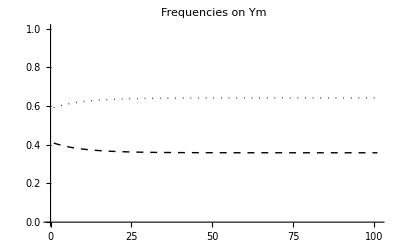

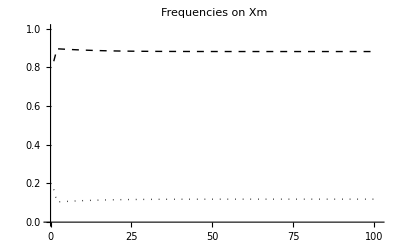

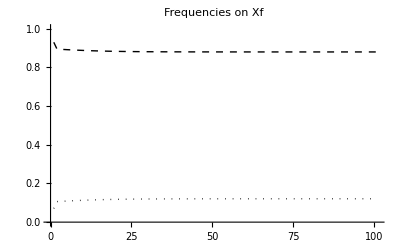

```mathematica
Show[
ListPlot[
Table[
nextYAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,initialpXf+devXf,(1-initialpXf)-devXf,trypMXAf,trypMXaf,(1-tryα)(initialpXm+devXm),(1-tryα)((1-initialpXm)-devXm),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,tryα*(initialpYm+devYm),tryα*((1-initialpYm)-devYm),trypMYAm,trypMYam]/tryα,
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dashed],
PlotRange->{0,1}],
ListPlot[
Table[
nextYam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,initialpXf+devXf,(1-initialpXf)-devXf,trypMXAf,trypMXaf,(1-tryα)(initialpXm+devXm),(1-tryα)((1-initialpXm)-devXm),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,tryα*(initialpYm+devYm),tryα*((1-initialpYm)-devYm),trypMYAm,trypMYam]/tryα,
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dotted],
PlotRange->{0,1}],
PlotLabel->"Frequencies on Ym"]

Show[
ListPlot[
Table[
nextXAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,initialpXf+devXf,(1-initialpXf)-devXf,trypMXAf,trypMXaf,(1-tryα)(initialpXm+devXm),(1-tryα)((1-initialpXm)-devXm),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,tryα*(initialpYm+devYm),tryα*((1-initialpYm)-devYm),trypMYAm,trypMYam]/(1-tryα),
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dashed],
PlotRange->{0,1}],
ListPlot[
Table[
nextXam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,initialpXf+devXf,(1-initialpXf)-devXf,trypMXAf,trypMXaf,(1-tryα)(initialpXm+devXm),(1-tryα)((1-initialpXm)-devXm),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,tryα*(initialpYm+devYm),tryα*((1-initialpYm)-devYm),trypMYAm,trypMYam]/(1-tryα),
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dotted],
PlotRange->{0,1}],
PlotLabel->"Frequencies on Xm"]

Show[
ListPlot[
Table[
nextXAf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,initialpXf+devXf,(1-initialpXf)-devXf,trypMXAf,trypMXaf,(1-tryα)(initialpXm+devXm),(1-tryα)((1-initialpXm)-devXm),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,tryα*(initialpYm+devYm),tryα*((1-initialpYm)-devYm),trypMYAm,trypMYam],
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dashed],
PlotRange->{0,1}],
ListPlot[
Table[
nextXaf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,initialpXf+devXf,(1-initialpXf)-devXf,trypMXAf,trypMXaf,(1-tryα)(initialpXm+devXm),(1-tryα)((1-initialpXm)-devXm),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,tryα*(initialpYm+devYm),tryα*((1-initialpYm)-devYm),trypMYAm,trypMYam],
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dotted],
PlotRange->{0,1}],
PlotLabel->"Frequencies on Xf"]
```

#### Ext Stab

First, we need to decide on the initial frequency of the new mutation. We will assume that it appear in linkage equilibrium with the old type by introducing it at the same frequencies.

```mathematica
pM=0.0001;

trypMXAf=pM initialpXf;
trypMXaf=pM (1-initialpXf);
trypMXAm=pM(1-tryα) initialpXm;
trypMXam=pM (1-tryα)(1-initialpXm);
trypMYAf=pM initialYAf;
trypMYaf=pM initialYaf;
trypMYAm=pM (tryα)initialpYm;
trypMYam=pM(tryα)(1-initialpYm);
```

Several other parameters are needed for the plots, including the time (tmax) and interval at which the frequencies are registered (tinterval).

```mathematica
tmax=5000;
tinterval=100;
tplotinterval=1000;

(*plot parameters*)
inches=72;
lwd=0.006;(*line thickness as fraction of plot width*)
ticksize={0,0.01};
xplotmin=0;
xplotmax=tmax;
yplotmin=0;
yplotmax=1;
xsize=5inches;
aspectratio=1/Sqrt[2];
```

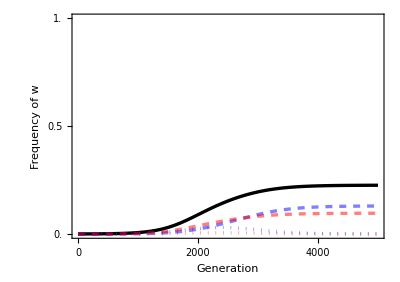

```mathematica
ListPlot[{Table[{t,
Total[{nextYAwf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextYawf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextXAwf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextXawf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextYAwf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextYawf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextXAwf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{
nextXawf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}]
},
Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotmin,yplotmax,0.5}]},
FrameTicksStyle->Directive[Black,Thickness[lwd]],
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Generation","Frequency of w"},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
Joined->True,
PlotStyle->{Directive[Black,Thickness[lwd]],
Directive[Blue,Opacity[0.5],Thickness[lwd],Dashed],
Directive[Blue,Opacity[0.5],Thickness[lwd],Dotted],
Directive[Red,Opacity[0.5],Thickness[lwd],Dashed],
Directive[Red,Opacity[0.5],Thickness[lwd],Dotted]},
PlotRange->{0,1}]
```

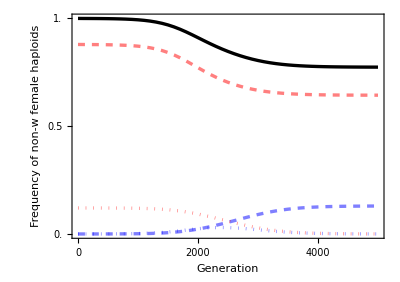

```mathematica
ListPlot[{Table[{t,
Total[{nextYAf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextYaf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextXAf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextXaf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextYAf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextYaf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextXAf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{
nextXaf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}]
},
Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotmin,yplotmax,0.5}]},
FrameTicksStyle->Directive[Black,Thickness[lwd]],
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Generation","Frequency of non-w female haploids"},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
Joined->True,
PlotStyle->{Directive[Black,Thickness[lwd]],
Directive[Blue,Opacity[0.5],Thickness[lwd],Dashed],
Directive[Blue,Opacity[0.5],Thickness[lwd],Dotted],
Directive[Red,Opacity[0.5],Thickness[lwd],Dashed],
Directive[Red,Opacity[0.5],Thickness[lwd],Dotted]},
PlotRange->{0,1}]
```

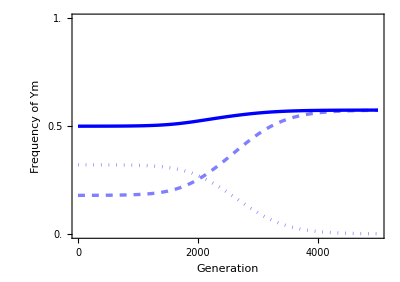

```mathematica
ListPlot[{Table[{t,
Total[{nextYAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextYam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextYAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextYam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}]
},
Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotmin,yplotmax,0.5}]},
FrameTicksStyle->Directive[Black,Thickness[lwd]],
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Generation","Frequency of Ym"},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
Joined->True,
PlotStyle->{Directive[Blue,Thickness[lwd]],
Directive[Blue,Opacity[0.5],Thickness[lwd],Dashed],
Directive[Blue,Opacity[0.5],Thickness[lwd],Dotted]},
PlotRange->{0,1}]
```

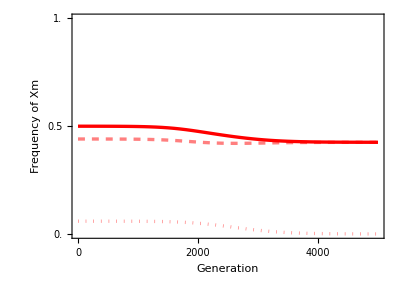

```mathematica
ListPlot[{Table[{t,
Total[{nextXAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextXam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextXAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextXam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}]
},
Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotmin,yplotmax,0.5}]},
FrameTicksStyle->Directive[Black,Thickness[lwd]],
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Generation","Frequency of Xm"},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
Joined->True,
PlotStyle->{Directive[Red,Thickness[lwd]],
Directive[Red,Opacity[0.5],Thickness[lwd],Dashed],
Directive[Red,Opacity[0.5],Thickness[lwd],Dotted]},
PlotRange->{0,1}]
```

#### Sex ratio plot

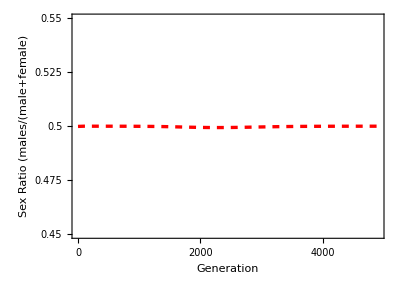

```mathematica
yplotminSexRatio=0.45;
yplotmaxSexRatio=0.55;
yplotintervalSexRatio=0.025;


ListPlot[{Table[{t,
Total[{
sexRatioAtBirth[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,1,tmax,tinterval}]
},
Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotminSexRatio,yplotmaxSexRatio,yplotintervalSexRatio}]},
FrameTicksStyle->Directive[Black,Thickness[lwd]],
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Generation","Sex Ratio (males/(male+female)"},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
Joined->True,
PlotStyle->{Directive[Red,Thickness[lwd],Dashed]},
PlotRange->{yplotminSexRatio,yplotmaxSexRatio}]
```

```mathematica
sexRatioAtBirth[1000,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
```

0.499944

### Iterate Recursions (W appears to reach 50% after a long time, X not yet completely lost at the end of simulation though)

#### Parameters:

```mathematica
trysAf=0.15;
tryhAf=0.7;
tryhAm=0.7;
trysAm=0.07;
tryt=-0.1;

tryFAA=1+trysAf;
tryFAa=1+tryhAf trysAf;
tryFaa=1;
tryMAA=1+trysAm;
tryMAa=1+tryhAm trysAm;
tryMaa=1;
trywA=1+tryt;
trywa=1;
tryr=0.01;
tryα=0.5;
```

Our invasion analysis indicates that invasion should occur when the following is positive (which assumes that hAm=hAf)

```mathematica
((-1+2 tryr) trysAf (trysAf-trysAm) tryt^2)/(2 tryr (trysAf+trysAm)^2)
```

-0.121488

Also need to specify tryR for full system: (n.b., χ=r R)

```mathematica
tryR=0.5;
```

#### Find equilibrium (equil and sieve functions) [enter]

```mathematica
initialpXf=Flatten[sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryα]][[1]]
initialpXm=Flatten[sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryα]][[2]]
initialYAf=0;
initialYaf=0;
initialpYm=Flatten[sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryα]][[3]]
```

0.323703

0.31156

0.834699

#### IntStab

We check stability by perturbing the system slightly and checking that allele frequencies return. dev gives the initial deviations:

```mathematica
devXf=0.05;
devXm=-0.05;
devYm=0.05;

trypMXAf=0;
trypMXaf=0;
trypMXAm=0;
trypMXam=0;
trypMYAf=0;
trypMYaf=0;
trypMYAm=0;
trypMYam=0;
tmax=1000;
tinterval=10;
```

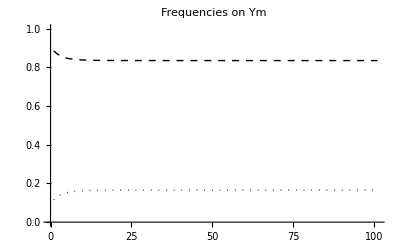

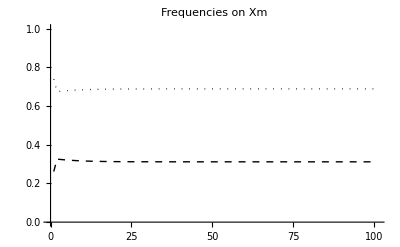

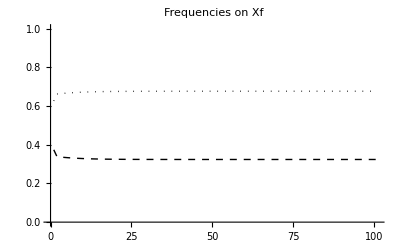

```mathematica
Show[
ListPlot[
Table[
nextYAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,initialpXf+devXf,(1-initialpXf)-devXf,trypMXAf,trypMXaf,(1-tryα)(initialpXm+devXm),(1-tryα)((1-initialpXm)-devXm),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,tryα*(initialpYm+devYm),tryα*((1-initialpYm)-devYm),trypMYAm,trypMYam]/tryα,
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dashed],
PlotRange->{0,1}],
ListPlot[
Table[
nextYam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,initialpXf+devXf,(1-initialpXf)-devXf,trypMXAf,trypMXaf,(1-tryα)(initialpXm+devXm),(1-tryα)((1-initialpXm)-devXm),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,tryα*(initialpYm+devYm),tryα*((1-initialpYm)-devYm),trypMYAm,trypMYam]/tryα,
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dotted],
PlotRange->{0,1}],
PlotLabel->"Frequencies on Ym"]

Show[
ListPlot[
Table[
nextXAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,initialpXf+devXf,(1-initialpXf)-devXf,trypMXAf,trypMXaf,(1-tryα)(initialpXm+devXm),(1-tryα)((1-initialpXm)-devXm),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,tryα*(initialpYm+devYm),tryα*((1-initialpYm)-devYm),trypMYAm,trypMYam]/(1-tryα),
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dashed],
PlotRange->{0,1}],
ListPlot[
Table[
nextXam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,initialpXf+devXf,(1-initialpXf)-devXf,trypMXAf,trypMXaf,(1-tryα)(initialpXm+devXm),(1-tryα)((1-initialpXm)-devXm),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,tryα*(initialpYm+devYm),tryα*((1-initialpYm)-devYm),trypMYAm,trypMYam]/(1-tryα),
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dotted],
PlotRange->{0,1}],
PlotLabel->"Frequencies on Xm"]

Show[
ListPlot[
Table[
nextXAf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,initialpXf+devXf,(1-initialpXf)-devXf,trypMXAf,trypMXaf,(1-tryα)(initialpXm+devXm),(1-tryα)((1-initialpXm)-devXm),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,tryα*(initialpYm+devYm),tryα*((1-initialpYm)-devYm),trypMYAm,trypMYam],
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dashed],
PlotRange->{0,1}],
ListPlot[
Table[
nextXaf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,initialpXf+devXf,(1-initialpXf)-devXf,trypMXAf,trypMXaf,(1-tryα)(initialpXm+devXm),(1-tryα)((1-initialpXm)-devXm),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,tryα*(initialpYm+devYm),tryα*((1-initialpYm)-devYm),trypMYAm,trypMYam],
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dotted],
PlotRange->{0,1}],
PlotLabel->"Frequencies on Xf"]
```

#### Ext Stab

First, we need to decide on the initial frequency of the new mutation. We will assume that it appear in linkage equilibrium with the old type by introducing it at the same frequencies.

```mathematica
pM=0.0001;

trypMXAf=pM initialpXf;
trypMXaf=pM (1-initialpXf);
trypMXAm=pM(1-tryα) initialpXm;
trypMXam=pM (1-tryα)(1-initialpXm);
trypMYAf=pM initialYAf;
trypMYaf=pM initialYaf;
trypMYAm=pM (tryα)initialpYm;
trypMYam=pM(tryα)(1-initialpYm);
```

Several other parameters are needed for the plots, including the time (tmax) and interval at which the frequencies are registered (tinterval).

```mathematica
tmax=25000;
tinterval=100;
tplotinterval=10000;

(*plot parameters*)
inches=72;
lwd=0.006;(*line thickness as fraction of plot width*)
ticksize={0,0.01};
xplotmin=0;
xplotmax=tmax;
yplotmin=0;
yplotmax=1;
xsize=5inches;
aspectratio=1/Sqrt[2];
```

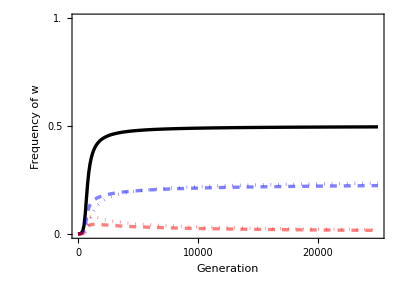

```mathematica
ListPlot[{Table[{t,
Total[{nextYAwf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextYawf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextXAwf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextXawf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextYAwf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextYawf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextXAwf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{
nextXawf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}]
},
Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotmin,yplotmax,0.5}]},
FrameTicksStyle->Directive[Black,Thickness[lwd]],
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Generation","Frequency of w"},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
Joined->True,
PlotStyle->{Directive[Black,Thickness[lwd]],
Directive[Blue,Opacity[0.5],Thickness[lwd],Dashed],
Directive[Blue,Opacity[0.5],Thickness[lwd],Dotted],
Directive[Red,Opacity[0.5],Thickness[lwd],Dashed],
Directive[Red,Opacity[0.5],Thickness[lwd],Dotted]},
PlotRange->{0,1}]
```

Frequency of w at the end of the simulation:

```mathematica
Total[{nextYAwf[tmax,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextYawf[tmax,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextXAwf[tmax,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextXawf[tmax,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]
```

0.496841

which is increasing slightly.

```mathematica
Total[{nextYAwf[tmax,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextYawf[tmax,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextXAwf[tmax,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextXawf[tmax,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]-
Total[{nextYAwf[tmax-1000,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextYawf[tmax-1000,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextXAwf[tmax-1000,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextXawf[tmax-1000,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]
```

0.000160696

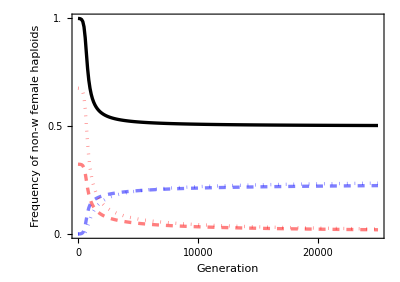

```mathematica
ListPlot[{Table[{t,
Total[{nextYAf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextYaf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextXAf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextXaf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextYAf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextYaf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextXAf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{
nextXaf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}]
},
Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotmin,yplotmax,0.5}]},
FrameTicksStyle->Directive[Black,Thickness[lwd]],
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Generation","Frequency of non-w female haploids"},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
Joined->True,
PlotStyle->{Directive[Black,Thickness[lwd]],
Directive[Blue,Opacity[0.5],Thickness[lwd],Dashed],
Directive[Blue,Opacity[0.5],Thickness[lwd],Dotted],
Directive[Red,Opacity[0.5],Thickness[lwd],Dashed],
Directive[Red,Opacity[0.5],Thickness[lwd],Dotted]},
PlotRange->{0,1}]
```

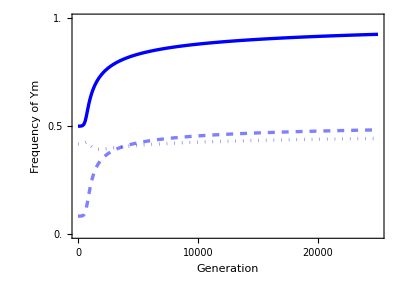

```mathematica
ListPlot[{Table[{t,
Total[{nextYAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextYam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextYam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextYAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}]
},
Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotmin,yplotmax,0.5}]},
FrameTicksStyle->Directive[Black,Thickness[lwd]],
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Generation","Frequency of Ym"},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
Joined->True,
PlotStyle->{Directive[Blue,Thickness[lwd]],
Directive[Blue,Opacity[0.5],Thickness[lwd],Dashed],
Directive[Blue,Opacity[0.5],Thickness[lwd],Dotted]},
PlotRange->{0,1}]
```

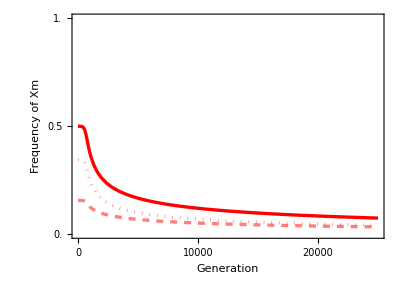

```mathematica
ListPlot[{Table[{t,
Total[{nextXAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextXam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextXAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextXam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}]
},
Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotmin,yplotmax,0.5}]},
FrameTicksStyle->Directive[Black,Thickness[lwd]],
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Generation","Frequency of Xm"},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
Joined->True,
PlotStyle->{Directive[Red,Thickness[lwd]],
Directive[Red,Opacity[0.5],Thickness[lwd],Dashed],
Directive[Red,Opacity[0.5],Thickness[lwd],Dotted]},
PlotRange->{0,1}]
```

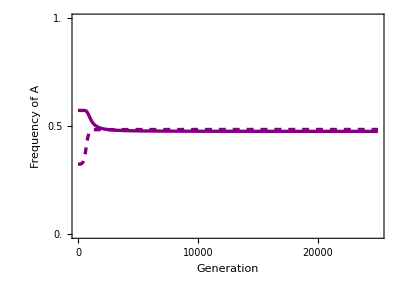

```mathematica
ListPlot[{Table[{t,
Total[{nextYAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextXAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextYAwf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextXAwf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextYAf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextXAf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}]
},
Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotmin,yplotmax,0.5}]},
FrameTicksStyle->Directive[Black,Thickness[lwd]],
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Generation","Frequency of A"},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
Joined->True,
PlotStyle->{Directive[Purple,Thickness[lwd]],
Directive[Purple,Thickness[lwd],Dashed]},
PlotRange->{0,1}]
```

#### Sex ratio plot

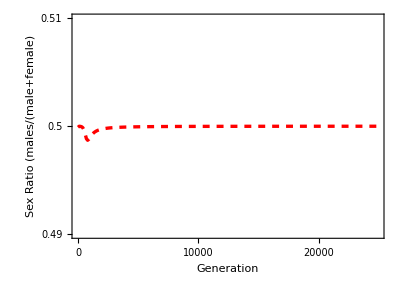

```mathematica
yplotminSexRatio=0.49;
yplotmaxSexRatio=0.51;
yplotintervalSexRatio=0.01;


ListPlot[{Table[{t,
Total[{
sexRatioAtBirth[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,1,tmax,tinterval}]
},
Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotminSexRatio,yplotmaxSexRatio,yplotintervalSexRatio}]},
FrameTicksStyle->Directive[Black,Thickness[lwd]],
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Generation","Sex Ratio (males/(male+female)"},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
Joined->True,
PlotStyle->{Directive[Red,Thickness[lwd],Dashed]},
PlotRange->{yplotminSexRatio,yplotmaxSexRatio}]
```

# ESD invades XY (offspring control)

## Recursions

We consider three loci: 1) a diallelic genetic sex-determining (GSD) locus, 2) a diallelic locus under viability selection (VS), and 3) a diallelic environmentally sex-determining (ESD) locus. We assume that initially, the ESD locus is fixed for a null allele E, that does nothing and thus sex is determined by the GSD locus. We will then look at the invasion of a rare mutant allele e at the ESD locus, which is dominant over E and the GSD locus and causes a proportion k of its diploid carriers to be female and a proportion 1-k to be male (i.e., e is sensitive to an environmental trigger that determines sex).

We will call the alleles at the GSD locus X and Y with Y masculinizing and dominant over X. We can easily convert to a ZW system by making Z=X and W=Y and male=female and female=male.

Haploid selection: starting with haploid genotype frequencies fHap in each sex, the frequencies after selection fHapSel are

```mathematica
wbarHap[sex_]:=wbarHap[sex]=
Sum[wHap[x,y,z,sex]fHap[x,y,z,sex],{x,1,2},{y,1,2},{z,1,2}];
fHapSel[x_,y_,z_,sex_]:=fHapSel[x,y,z,sex]=
wHap[x,y,z,sex]fHap[x,y,z,sex]/wbarHap[sex]
Sum[fHapSel[x,y,z,sex],{x,1,2},{y,1,2},{z,1,2}]//Factor
```

1

where x is the allele at the GSD locus, y is the allele at the VS locus, z is the allele at the ESD locus, and sex is male or female. Notice that the fitness of a haploid genotype wHap depends on the sex of its parent and gametes of the opposite sex do not compete with one another (wbarHap is mean fitness of gametes in each sex).

Gametic union: haploid genotypes pair at random giving diploid genotype frequencies fDip

```mathematica
fDip[x1_,y1_,z1_,x2_,y2_,z2_]:=fDip[x1,y1,z1,x2,y2,z2]=
fHapSel[x1,y1,z1,female]fHapSel[x2,y2,z2,male]
Sum[fDip[x1,y1,z1,x2,y2,z2],{x1,1,2},{y1,1,2},{z1,1,2},{x2,1,2},{y2,1,2},{z2,1,2}]//FullSimplify
```

1

Sex determination:

```mathematica
fDipSex[x1_,y1_,z1_,x2_,y2_,z2_,sex_]:=fDipSex[x1,y1,z1,x2,y2,z2,sex]=
fDip[x1,y1,z1,x2,y2,z2]psex[x1,y1,z1,x2,y2,z2,sex]
```

where an individual must be male or female

```mathematica
sumsex=Solve[1==Sum[psex[x1,y1,z1,x2,y2,z2,sex],{sex,{male,female}}],psex[x1,y1,z1,x2,y2,z2,female]]/.psex[x1,y1,z1,x2,y2,z2,female]->psex[x1_,y1_,z1_,x2_,y2_,z2_,female]//Flatten;
```

Here we will be concerned with environmental sex determination invading male heterogamy:

```mathematica
ESDXY={psex[2,y1_,1,x2_,y2_,1,male]->1,psex[x1_,y1_,1,2,y2_,1,male]->1,psex[1,y1_,1,1,y2_,1,male]->0, fHap[2,y_,1,female]->0,psex[x1_,y1_,2,x2_,y2_,z2_,male]->1-k,psex[x1_,y1_,z1_,x2_,y2_,2,male]->1-k};
```

Diploid selection: if all individuals compete with one another then the frequencies of diploid genotypes after selection fDipSel are

```mathematica
wbarDip=Sum[wDip[x1,y1,z1,x2,y2,z2,sex]fDipSex[x1,y1,z1,x2,y2,z2,sex],{x1,1,2},{y1,1,2},{z1,1,2},{x2,1,2},{y2,1,2},{z2,1,2},{sex,{male,female}}];
fDipSel[x1_,y1_,z1_,x2_,y2_,z2_,sex_]:=fDipSel[x1,y1,z1,x2,y2,z2,sex]=
wDip[x1,y1,z1,x2,y2,z2,sex]fDipSex[x1,y1,z1,x2,y2,z2,sex]/wbarDip;
Sum[fDipSel[x1,y1,z1,x2,y2,z2,sex],{x1,1,2},{y1,1,2},{z1,1,2},{x2,1,2},{y2,1,2},{z2,1,2},{sex,{male,female}}]/.sumsex/.ESDXY//Factor
```

1

Note that this is different from what we were doing before, where we assumed males compete with males and females with females.

Alternatively, males could compete with males and female with females. Then

```mathematica
wbarDipMale=Sum[wDip[x1,y1,z1,x2,y2,z2,sex]fDipSex[x1,y1,z1,x2,y2,z2,sex],{x1,1,2},{y1,1,2},{z1,1,2},{x2,1,2},{y2,1,2},{z2,1,2},{sex,{male}}];
wbarDipFemale=Sum[wDip[x1,y1,z1,x2,y2,z2,sex]fDipSex[x1,y1,z1,x2,y2,z2,sex],{x1,1,2},{y1,1,2},{z1,1,2},{x2,1,2},{y2,1,2},{z2,1,2},{sex,{female}}];
fDipSel[x1_,y1_,z1_,x2_,y2_,z2_,male]:=fDipSel[x1,y1,z1,x2,y2,z2,male]=
wDip[x1,y1,z1,x2,y2,z2,male]fDipSex[x1,y1,z1,x2,y2,z2,male]/wbarDipMale;
fDipSel[x1_,y1_,z1_,x2_,y2_,z2_,female]:=fDipSel[x1,y1,z1,x2,y2,z2,female]=
wDip[x1,y1,z1,x2,y2,z2,female]fDipSex[x1,y1,z1,x2,y2,z2,female]/wbarDipFemale;
Sum[fDipSel[x1,y1,z1,x2,y2,z2,sex],{x1,1,2},{y1,1,2},{z1,1,2},{x2,1,2},{y2,1,2},{z2,1,2},{sex,{male,female}}]/.sumsex/.ESDXY//Factor
```

1

Meiosis: if pseg is the probability that a diploid genotype of a particular sex produces a gamete of a given haploid genoytpe, then the frequencies of haploid genotypes in the next generation are

```mathematica
fHapNextTot[x_,y_,z_,sex_]:=fHapNextTot[x,y,z,sex]=
Sum[fDipSel[x1,y1,z1,x2,y2,z2,sex]pseg[x1,y1,z1,x2,y2,z2,sex,x,y,z],{x1,1,2},{y1,1,2},{z1,1,2},{x2,1,2},{y2,1,2},{z2,1,2}];
```

And the frequency from each sex is

```mathematica
fHapNext[x_,y_,z_,sex_]:=fHapNext[x,y,z,sex]=
fHapNextTot[x,y,z,sex]/Sum[fHapNextTot[x1,y1,z1,sex],{x1,1,2},{y1,1,2},{z1,1,2}]
```

With recombination and no meiotic drive (and with linear arrangement x-y-z with recombination probability r between x and y and probability R between y and z) we have

```mathematica
WithRec={
(*triple homozygote*)
pseg[x1_,y1_,z1_,x1_,y1_,z1_,sex_,x1_,y1_,z1_]->1,
(*single heterozygotes*)
pseg[x1_,y1_,z1_,x2_,y1_,z1_,sex_,x1_,y1_,z1_]->1/2,
pseg[x1_,y1_,z1_,x2_,y1_,z1_,sex_,x2_,y1_,z1_]->1/2,
pseg[x1_,y1_,z1_,x1_,y2_,z1_,sex_,x1_,y1_,z1_]->1/2,
pseg[x1_,y1_,z1_,x1_,y2_,z1_,sex_,x1_,y2_,z1_]->1/2,
pseg[x1_,y1_,z1_,x1_,y1_,z2_,sex_,x1_,y1_,z1_]->1/2,
pseg[x1_,y1_,z1_,x1_,y1_,z2_,sex_,x1_,y1_,z2_]->1/2,
(*double heterozygotes*)
pseg[x1_,y1_,z1_,x2_,y2_,z1_,sex_,x1_,y1_,z1_]->(1-r)/2,
pseg[x1_,y1_,z1_,x2_,y2_,z1_,sex_,x2_,y2_,z1_]->(1-r)/2,
pseg[x1_,y1_,z1_,x2_,y2_,z1_,sex_,x2_,y1_,z1_]->r/2,
pseg[x1_,y1_,z1_,x2_,y2_,z1_,sex_,x1_,y2_,z1_]->r/2,
pseg[x1_,y1_,z1_,x1_,y2_,z2_,sex_,x1_,y1_,z1_]->(1-R)/2,
pseg[x1_,y1_,z1_,x1_,y2_,z2_,sex_,x1_,y2_,z2_]->(1-R)/2,
pseg[x1_,y1_,z1_,x1_,y2_,z2_,sex_,x1_,y2_,z1_]->R/2,
pseg[x1_,y1_,z1_,x1_,y2_,z2_,sex_,x1_,y1_,z2_]->R/2,
pseg[x1_,y1_,z1_,x2_,y1_,z2_,sex_,x1_,y1_,z1_]->((1-r)(1-R)+r R)/2,
pseg[x1_,y1_,z1_,x2_,y1_,z2_,sex_,x2_,y1_,z2_]->((1-r)(1-R)+r R)/2,
pseg[x1_,y1_,z1_,x2_,y1_,z2_,sex_,x2_,y1_,z1_]->(r(1-R)+(1-r)R)/2,
pseg[x1_,y1_,z1_,x2_,y1_,z2_,sex_,x1_,y1_,z2_]->(r(1-R)+(1-r)R)/2,
(*triple heterozygote*)
pseg[x1_,y1_,z1_,x2_,y2_,z2_,sex_,x1_,y1_,z1_]->(1-r)(1-R)/2,
pseg[x1_,y1_,z1_,x2_,y2_,z2_,sex_,x2_,y2_,z2_]->(1-r)(1-R)/2,
pseg[x1_,y1_,z1_,x2_,y2_,z2_,sex_,x2_,y1_,z1_]->r(1-R)/2,
pseg[x1_,y1_,z1_,x2_,y2_,z2_,sex_,x1_,y2_,z2_]->r(1-R)/2,
pseg[x1_,y1_,z1_,x2_,y2_,z2_,sex_,x1_,y2_,z1_]->r R/2,
pseg[x1_,y1_,z1_,x2_,y2_,z2_,sex_,x2_,y1_,z2_]->r R/2,
pseg[x1_,y1_,z1_,x2_,y2_,z2_,sex_,x1_,y1_,z2_]->(1-r)R/2,
pseg[x1_,y1_,z1_,x2_,y2_,z2_,sex_,x2_,y2_,z1_]->(1-r)R/2
};
pseg0=pseg[x1_,y1_,z1_,x2_,y2_,z2_,sex_,x_,y_,z_]->0;
```

And the frequencies of gametes from each sex in the next generation sum to one (this takes a minute)

```mathematica
(*Sum[fHapNext[a,b,c,female]/.sumsex/.ESDXY/.WithRec/.pseg0,{a,1,2},{b,1,2},{c,1,2}]//Factor*)
```

## Resident equilibrium (weak selection)

We first assume that the ESD locus is fixed for the null allele

```mathematica
subequil={
fHap[1,1,1,female]->pXf,
fHap[1,2,1,female]->1-pXf,
fHap[1,1,1,male]->(1-α)pXm,
fHap[1,2,1,male]->(1-α)(1-pXm),
fHap[2,1,1,male]->α pYm,
fHap[2,2,1,male]->α(1-pYm),
fHap[x_,y_,2,sex_]->0
}/.α->1/2;
```

where pXf is the frequency of A in non-mutant eggs, pXm is the frequency of A in gametes from males with an X allele, and pY is the frequency of A in gametes from males with a Y allele. α is the frequency of male gametes that are Y bearing (we assume α=1/2 ie no drive).

We now wish to solve for the equilibrium frequencies of the haploid genotypes in gametes of each sex. Equilibrium is achieved when the following three equations are zero (this takes a minute)

```mathematica
differenceEqs={
fHapNext[1,1,1,female]-fHap[1,1,1,female],
fHapNext[1,1,1,male]-fHap[1,1,1,male],
fHapNext[2,1,1,male]-fHap[2,1,1,male]
}/.sumsex/.ESDXY/.WithRec/.pseg0/.subequil;
```

To simplify the analysis we assume weak selection in both haploids and diploids. In addition, we assume selection acts on the VS locus only

```mathematica
weaksel={
wHap[x_,1,z_,sex_]->1,
wHap[x_,2,z_,sex_]->1+sHap[sex] ϵ,
wDip[x1_,1,z1_,x2_,1,z2_,sex_]->1,
wDip[x1_,1,z1_,x2_,2,z2_,sex_]->1+h[sex] sDip[sex] ϵ,
wDip[x1_,2,z1_,x2_,1,z2_,sex_]->1+h[sex] sDip[sex] ϵ,
wDip[x1_,2,z1_,x2_,2,z2_,sex_]->1+ sDip[sex] ϵ
};
```

We can write the frequencies as Taylor series

```mathematica
frequenciessub={
pXf->pXf0+pXf1 ϵ,
pXm->pXm0+pXm1 ϵ,
pYm->pYm0+pYm1 ϵ
};
```

Without selection the recursions for the change in the frequencies are

```mathematica
differenceEqs0=Normal[Series[differenceEqs/.weaksel/.frequenciessub,{ϵ,0,0}]]//Factor
```

{1/2 (-pXf0+pXm0),1/2 (pXf0-pXm0-pXf0 r+pYm0 r),1/2 (pXf0-pYm0) r}

And at equilibrium we have

```mathematica
sol0=Solve[differenceEqs0==0,{pYm0,pXm0}]
```

{{pYm0→pXf0,pXm0→pXf0}}

So, with no selection, the equilibrium frequency of A in each gamete/pollen type is equal (and we call this pA).

Now, looking at only the first order selection terms, the recursions for the change in frequency of A in each gamete/pollen type are

```mathematica
differenceEqs1=Collect[Normal[Series[differenceEqs/.weaksel/.frequenciessub/.sol0,{ϵ,0,1}]],ϵ,Factor]/.pXf0->pA//Flatten
```

{1/2 ϵ (-pXf1+pXm1-2 pA sDip[female]+4 pA^2 sDip[female]-2 pA^3 sDip[female]+2 pA h[female] sDip[female]-6 pA^2 h[female] sDip[female]+4 pA^3 h[female] sDip[female]-pA sHap[female]+pA^2 sHap[female]-pA sHap[male]+pA^2 sHap[male]),1/2 ϵ (pXf1-pXm1-pXf1 r+pYm1 r-pA sDip[male]+2 pA^2 sDip[male]-pA^3 sDip[male]+pA h[male] sDip[male]-3 pA^2 h[male] sDip[male]+2 pA^3 h[male] sDip[male]-pA sHap[female]+pA^2 sHap[female]+pA r sHap[female]-pA^2 r sHap[female]-pA r sHap[male]+pA^2 r sHap[male]),1/2 ϵ (pXf1 r-pYm1 r-pA sDip[male]+2 pA^2 sDip[male]-pA^3 sDip[male]+pA h[male] sDip[male]-3 pA^2 h[male] sDip[male]+2 pA^3 h[male] sDip[male]-pA r sHap[female]+pA^2 r sHap[female]-pA sHap[male]+pA^2 sHap[male]+pA r sHap[male]-pA^2 r sHap[male])}

And we can solve for the two of the first order differences and the mean frequency of A

```mathematica
realsol=Solve[differenceEqs1==0/.pXm1->dpAXmXf+pXf1/.pYm1->dpAYmXf+pXf1,{dpAXmXf,dpAYmXf,pA}]//Factor
```

{{dpAXmXf→0,dpAYmXf→0,pA→0},{dpAXmXf→0,dpAYmXf→0,pA→1},{dpAXmXf→-((-sDip[female]+h[female] sDip[female]-sDip[male]+h[male] sDip[male]-sHap[female]-sHap[male]) (h[female] sDip[female]+h[male] sDip[male]+sHap[female]+sHap[male]) (2 h[female] sDip[female] sDip[male]-2 h[male] sDip[female] sDip[male]-sDip[female] sHap[female]+2 h[female] sDip[female] sHap[female]+sDip[male] sHap[female]-2 h[male] sDip[male] sHap[female]-sDip[female] sHap[male]+2 h[female] sDip[female] sHap[male]+sDip[male] sHap[male]-2 h[male] sDip[male] sHap[male]))/(-sDip[female]+2 h[female] sDip[female]-sDip[male]+2 h[male] sDip[male])^3,dpAYmXf→-((-sDip[female]+h[female] sDip[female]-sDip[male]+h[male] sDip[male]-sHap[female]-sHap[male]) (h[female] sDip[female]+h[male] sDip[male]+sHap[female]+sHap[male]) (h[female] sDip[female] sDip[male]-h[male] sDip[female] sDip[male]-r sDip[female] sHap[female]+2 r h[female] sDip[female] sHap[female]+sDip[male] sHap[female]-r sDip[male] sHap[female]-2 h[male] sDip[male] sHap[female]+2 r h[male] sDip[male] sHap[female]-sDip[female] sHap[male]+r sDip[female] sHap[male]+2 h[female] sDip[female] sHap[male]-2 r h[female] sDip[female] sHap[male]+r sDip[male] sHap[male]-2 r h[male] sDip[male] sHap[male]))/(r (-sDip[female]+2 h[female] sDip[female]-sDip[male]+2 h[male] sDip[male])^3),pA→(-sDip[female]+h[female] sDip[female]-sDip[male]+h[male] sDip[male]-sHap[female]-sHap[male])/(-sDip[female]+2 h[female] sDip[female]-sDip[male]+2 h[male] sDip[male])}}

## Internal stability (weak selection)

Here we use linear stability analysis to examine when the resident equilibrium (i.e., no mutants) derived above is stable.

The Jacobian for the residents is (this takes a couple minutes)

```mathematica
eqs=Join[Table[fHapNext[1,y,1,female],{y,1,2,1}],Table[fHapNext[x,y,1,male],{x,1,2,1},{y,1,2,1}]//Flatten]/.sumsex/.ESDXY/.WithRec/.pseg0;
matIntFull=Transpose[{
D[eqs,fHap[1,1,1,female]],
D[eqs,fHap[1,2,1,female]],
D[eqs,fHap[1,1,1,male]],
D[eqs,fHap[1,2,1,male]],
D[eqs,fHap[2,1,1,male]],
D[eqs,fHap[2,2,1,male]]
}]/.subequil//Factor;
```

From this we can derive the characteristic polynomial

```mathematica
charpolyIntFull=Det[matIntFull-IdentityMatrix[6]*λ];
```

Instead of examining when the non-trivial equilibrium (A not fixed or lost) is stable we will look for when the trivial equilibria (loss or fixation of A) are unstable.

When A is fixed the characteristic polynomial with no selection gives eigenvalues

```mathematica
charpolyInt1=charpolyIntFull/.pXm->1/.pXf->1/.pYm->1;
Normal[Series[charpolyInt1/.weaksel,{ϵ,0,0}]]//Factor;
Solve[%==0,λ]//Factor//Flatten
```

{λ→0,λ→0,λ→0,λ→1,λ→1/4 (1-2 r-√(9-20 r+4 r^2)),λ→1/4 (1-2 r+√(9-20 r+4 r^2))}

and λ=1 is the leading eigenvalue.

With weak selection first order term in the eigenvalues is

```mathematica
Normal[Series[charpolyInt1/.weaksel/.λ->1+δλ1*ϵ,{ϵ,0,1}]]/.ϵ->1//Factor;
δλ1fix=Solve[%==0,δλ1]//Flatten
```

{δλ1→1/2 (h[female] sDip[female]+h[male] sDip[male]+sHap[female]+sHap[male])}

And so the fixation of A is unstable when this expression is positive.

When A is lost the characteristic polynomial with no selection gives eigenvalues

```mathematica
charpolyInt0=charpolyIntFull/.pXm->0/.pXf->0/.pYm->0;
Normal[Series[charpolyInt0/.weaksel,{ϵ,0,0}]]//Factor;
Solve[%==0,λ]//Flatten
```

{λ→0,λ→0,λ→0,λ→1,λ→1/4 (1-2 r-√(9-20 r+4 r^2)),λ→1/4 (1-2 r+√(9-20 r+4 r^2))}

With weak selection first order term in the eigenvalues is

```mathematica
Normal[Series[charpolyInt0/.weaksel/.λ->1+δλ1*ϵ,{ϵ,0,1}]]/.ϵ->1//Factor;
δλ1loss=Solve[%==0,δλ1]//Flatten
```

{δλ1→1/2 (-sDip[female]+h[female] sDip[female]-sDip[male]+h[male] sDip[male]-sHap[female]-sHap[male])}

And so the loss of A is unstable when this expression is positive.

Combining the two results, the protected polymorphism (non-trivial equilibrium) requires that

```mathematica
stabconds={(δλ1/.δλ1fix)<0,(δλ1/.δλ1loss)<0};
```

## External stability (weak selection)

Here we are interested in the ability of a rare mutant at the ESD locus to invade the non-mutant resident population at equilibrium.

The Jacobian for the mutants is (this takes a minute or two, or ten)

```mathematica
eqsmut=Table[fHapNext[x,y,2,sex],{sex,{female,male}},{y,1,2},{x,1,2}]/.sumsex/.ESDXY/.WithRec/.pseg0//Flatten;
matExtFull=Transpose[Flatten[Table[D[eqsmut,fHap[i,j,2,sex]],{sex,{female,male}},{j,1,2},{i,1,2}],2]]/.subequil//Factor;
```

Giving characteristic polynomial

```mathematica
charpolyExt=Det[matExtFull-IdentityMatrix[8]*λ];
```

Solving for the eigenvalues with no selection gives

```mathematica
Normal[Series[charpolyExt/.weaksel,{ϵ,0,0}]]//Factor;
Solve[%==0,λ]//Flatten
```

{λ→0,λ→0,λ→0,λ→0,λ→1,λ→1-R,λ→(-1+r) (-1+R),λ→1-r-R+2 r R}

On this order the leading eigenvalue is λ=1.

On the first order the eiganvalue is

```mathematica
Normal[Series[charpolyExt/.weaksel/.λ->1+δλ*ϵ/.frequenciessub/.sol0/.pXf0->pA,{ϵ,0,1}]]//Factor;
Solve[%==0,δλ]
```

{{δλ→0}}

And on the 2nd order (this takes a few minutes)

```mathematica
Normal[Series[charpolyExt/.weaksel/.λ->1+δλ2*ϵ^2/.frequenciessub/.sol0/.pXf0->pA/.pXm1->dpAXmXf+pXf1/.pYm1->dpAYmXf+pXf1,{ϵ,0,2}]]//Factor;
Solve[%==0,δλ2];
lambda2diffs=Collect[δλ2/.%,{dpAXmXf,dpAYmXf},Simplify]
```

{-1/2 dpAXmXf k (2 (-1+k) (1-pA+(-1+2 pA) h[female]) sDip[female]-2 (-1+k) (1-pA+(-1+2 pA) h[male]) sDip[male]+k (sHap[female]-sHap[male]))+dpAYmXf (k^2 (-1+pA+h[female]-2 pA h[female]) sDip[female]+(-1+k)^2 (1-pA+(-1+2 pA) h[male]) sDip[male]-1/2 k^2 sHap[female]+sHap[male]-2 k sHap[male]+1/2 k^2 sHap[male])-1/R(-1+pA) pA (k^2 (1-pA+(-1+2 pA) h[female])^2 sDip[female]^2+(-1+k)^2 (-1+pA+h[male]-2 pA h[male])^2 sDip[male]^2+(-1+k) (1-pA+(-1+2 pA) h[male]) sDip[male] ((-R+k (-2+3 R)) sHap[female]+(-2+k (2-3 R)+R) sHap[male])-k (1-pA+(-1+2 pA) h[female]) sDip[female] (2 (-1+k) (1-pA+(-1+2 pA) h[male]) sDip[male]+(-2 k-2 R+3 k R) sHap[female]+(-2+2 k+2 R-3 k R) sHap[male])-(k sHap[female]+sHap[male]-k sHap[male]) ((-R+k (-1+2 R)) sHap[female]+(-1+k+R-2 k R) sHap[male]))}

Then we can put in all the differences

```mathematica
tester=Collect[Normal[Series[lambda2diffs/.weaksel/.realsol[[3]],{ϵ,0,2}]],{dpAXmXf,dpAYmXf},Simplify]
```

{-(((-1+h[female]) sDip[female]+(-1+h[male]) sDip[male]-sHap[female]-sHap[male]) (h[female] sDip[female]+h[male] sDip[male]+sHap[female]+sHap[male]) (sDip[male] sHap[female]-h[male] sDip[male] (sDip[female]+2 sHap[female])-sDip[female] sHap[male]+h[female] sDip[female] (sDip[male]+2 sHap[male])) (-k^2 R sDip[female] sHap[female]+2 k^2 r R sDip[female] sHap[female]-2 r sDip[male] sHap[female]+8 k r sDip[male] sHap[female]-8 k^2 r sDip[male] sHap[female]+2 R sDip[male] sHap[female]-4 k R sDip[male] sHap[female]+3 k^2 R sDip[male] sHap[female]-8 k r R sDip[male] sHap[female]+10 k^2 r R sDip[male] sHap[female]+2 r sDip[female] sHap[male]-8 k r sDip[female] sHap[male]+8 k^2 r sDip[female] sHap[male]-2 R sDip[female] sHap[male]+4 k R sDip[female] sHap[male]-3 k^2 R sDip[female] sHap[male]+8 k r R sDip[female] sHap[male]-10 k^2 r R sDip[female] sHap[male]+k^2 R sDip[male] sHap[male]-2 k^2 r R sDip[male] sHap[male]-2 h[male] sDip[male] ((r (-1-4 k (-1+R)+4 k^2 (-1+R))+(1-2 k+2 k^2) R) sDip[female]+((2-4 k+3 k^2) R+2 r (-1-4 k (-1+R)+k^2 (-4+5 R))) sHap[female]+k^2 (1-2 r) R sHap[male])+2 h[female] sDip[female] ((r (-1-4 k (-1+R)+4 k^2 (-1+R))+(1-2 k+2 k^2) R) sDip[male]+k^2 (1-2 r) R sHap[female]+((2-4 k+3 k^2) R+2 r (-1-4 k (-1+R)+k^2 (-4+5 R))) sHap[male])))/(2 r R (sDip[female]-2 h[female] sDip[female]+sDip[male]-2 h[male] sDip[male])^4)}

Under some situations this reduces to (dividing by van Doorn and Kirkpatricks VA>0 and LA>0):

a) dominant feminizer with no competition among eggs and free recombination with VS locus (and equal dominance coefficients)

```mathematica
Collect[tester/(pA(1-pA))/(1-2r)*r/.realsol[[3]]/.h[sex_]->h/.k->1/.sHap[female]->0/.R->1/2//Simplify,{sHap[male]},FullSimplify]
```

{(sDip[female] (-sDip[female]+sDip[male]) sHap[male]^2)/(2 (sDip[female]+sDip[male])^2)}

b) dominant masculinizer with no competition among eggs  (and equal dominance coefficients)

```mathematica
Collect[tester/(pA(1-pA))/(1-2r)*r/.realsol[[3]]/.h[sex_]->h/.k->0/.sHap[female]->0//Simplify,{sHap[male]},FullSimplify]
```

{((-r+R) sDip[female]^2 sHap[male]^2)/((-1+2 r) R (sDip[female]+sDip[male])^2)}

c) ESD with no competition among eggs (and equal dominance coefficients)

```mathematica
Collect[tester/(pA(1-pA))/(1-2r)*r/.realsol[[3]]/.h[sex_]->h/.k->1/2/.sHap[female]->0//Simplify,{sHap[female],sHap[male]},Simplify]
```

{(sDip[female] (-3 sDip[female]+sDip[male]) sHap[male]^2)/(8 (sDip[female]+sDip[male])^2)}

d) ESD (and equal dominance coefficients)

```mathematica
Collect[tester/(pA(1-pA))/(1-2r)*r/.realsol[[3]]/.h[sex_]->h/.k->1/2//Simplify,{sHap[female],sHap[male]},Simplify]
```

{((sDip[female]-3 sDip[male]) sDip[male] sHap[female]^2)/(8 (sDip[female]+sDip[male])^2)-((sDip[female]^2-6 sDip[female] sDip[male]+sDip[male]^2) sHap[female] sHap[male])/(8 (sDip[female]+sDip[male])^2)+(sDip[female] (-3 sDip[female]+sDip[male]) sHap[male]^2)/(8 (sDip[female]+sDip[male])^2)}

#### Mike

There is a weird looking 3 in (c) above. I think this comes from averaging gains in males versus females:

```mathematica
selFeminizer=(sDip[female] (-sDip[female]+sDip[male]) sHap[male]^2)/(2 (sDip[female]+sDip[male])^2);
selMasculinizer=((-r+R) sDip[female]^2 sHap[male]^2)/((-1+2 r) R (sDip[female]+sDip[male])^2)/.R->1/2;
selESDsimp=(sDip[female] (-3 sDip[female]+sDip[male]) sHap[male]^2)/(8 (sDip[female]+sDip[male])^2);
```

```mathematica
Factor[1/2*(selFeminizer+selMasculinizer)/2]
%-selESDsimp//Factor
```

-(sDip[female] (3 sDip[female]-sDip[male]) sHap[male]^2)/(8 (sDip[female]+sDip[male])^2)

0

Interestingly, this does not involve R (but can be written as the average of the invasion of unlinked masculinizer and feminizer.

re-enter tester and realson because running all of the above is very slow:

```mathematica
tester={-(((-1+h[female]) sDip[female]+(-1+h[male]) sDip[male]-sHap[female]-sHap[male]) (h[female] sDip[female]+h[male] sDip[male]+sHap[female]+sHap[male]) (sDip[male] sHap[female]-h[male] sDip[male] (sDip[female]+2 sHap[female])-sDip[female] sHap[male]+h[female] sDip[female] (sDip[male]+2 sHap[male])) (-k^2 R sDip[female] sHap[female]+2 k^2 r R sDip[female] sHap[female]-2 r sDip[male] sHap[female]+8 k r sDip[male] sHap[female]-8 k^2 r sDip[male] sHap[female]+2 R sDip[male] sHap[female]-4 k R sDip[male] sHap[female]+3 k^2 R sDip[male] sHap[female]-8 k r R sDip[male] sHap[female]+10 k^2 r R sDip[male] sHap[female]+2 r sDip[female] sHap[male]-8 k r sDip[female] sHap[male]+8 k^2 r sDip[female] sHap[male]-2 R sDip[female] sHap[male]+4 k R sDip[female] sHap[male]-3 k^2 R sDip[female] sHap[male]+8 k r R sDip[female] sHap[male]-10 k^2 r R sDip[female] sHap[male]+k^2 R sDip[male] sHap[male]-2 k^2 r R sDip[male] sHap[male]-2 h[male] sDip[male] ((r (-1-4 k (-1+R)+4 k^2 (-1+R))+(1-2 k+2 k^2) R) sDip[female]+((2-4 k+3 k^2) R+2 r (-1-4 k (-1+R)+k^2 (-4+5 R))) sHap[female]+k^2 (1-2 r) R sHap[male])+2 h[female] sDip[female] ((r (-1-4 k (-1+R)+4 k^2 (-1+R))+(1-2 k+2 k^2) R) sDip[male]+k^2 (1-2 r) R sHap[female]+((2-4 k+3 k^2) R+2 r (-1-4 k (-1+R)+k^2 (-4+5 R))) sHap[male])))/(2 r R (sDip[female]-2 h[female] sDip[female]+sDip[male]-2 h[male] sDip[male])^4)};
realsol={{dpAXmXf->0,dpAYmXf->0,pA->0},{dpAXmXf->0,dpAYmXf->0,pA->1},{dpAXmXf->-((-sDip[female]+h[female] sDip[female]-sDip[male]+h[male] sDip[male]-sHap[female]-sHap[male]) (h[female] sDip[female]+h[male] sDip[male]+sHap[female]+sHap[male]) (2 h[female] sDip[female] sDip[male]-2 h[male] sDip[female] sDip[male]-sDip[female] sHap[female]+2 h[female] sDip[female] sHap[female]+sDip[male] sHap[female]-2 h[male] sDip[male] sHap[female]-sDip[female] sHap[male]+2 h[female] sDip[female] sHap[male]+sDip[male] sHap[male]-2 h[male] sDip[male] sHap[male]))/(-sDip[female]+2 h[female] sDip[female]-sDip[male]+2 h[male] sDip[male])^3,dpAYmXf->-((-sDip[female]+h[female] sDip[female]-sDip[male]+h[male] sDip[male]-sHap[female]-sHap[male]) (h[female] sDip[female]+h[male] sDip[male]+sHap[female]+sHap[male]) (h[female] sDip[female] sDip[male]-h[male] sDip[female] sDip[male]-r sDip[female] sHap[female]+2 r h[female] sDip[female] sHap[female]+sDip[male] sHap[female]-r sDip[male] sHap[female]-2 h[male] sDip[male] sHap[female]+2 r h[male] sDip[male] sHap[female]-sDip[female] sHap[male]+r sDip[female] sHap[male]+2 h[female] sDip[female] sHap[male]-2 r h[female] sDip[female] sHap[male]+r sDip[male] sHap[male]-2 r h[male] sDip[male] sHap[male]))/(r (-sDip[female]+2 h[female] sDip[female]-sDip[male]+2 h[male] sDip[male])^3),pA->(-sDip[female]+h[female] sDip[female]-sDip[male]+h[male] sDip[male]-sHap[female]-sHap[male])/(-sDip[female]+2 h[female] sDip[female]-sDip[male]+2 h[male] sDip[male])}};
```

R is involved if k =/= 1/2.

```mathematica
Collect[tester/(pA(1-pA))/(1-2r)*r/.realsol[[3]]/.h[sex_]->h/.sHap[female]->0//Simplify,{sHap[female],sHap[male]},Simplify]
```

{(sDip[female] (((2-4 k+3 k^2) R+2 r (-1-4 k (-1+R)+k^2 (-4+5 R))) sDip[female]+k^2 (-1+2 r) R sDip[male]) sHap[male]^2)/(2 (-1+2 r) R (sDip[female]+sDip[male])^2)}

## A general solution for invasion fitness [not finished?]

Lets first define mean fitness of a non-mutant female

```mathematica
femaleMeanFit=
pXf pXm wDip[1,1,1,1,1,1,female] wHap[1,1,1,female] wHap[1,1,1,male]+(1-pXf) pXm wDip[1,2,1,1,1,1,female]wHap[1,2,1,female] wHap[1,1,1,male] +(1-pXm) pXf wDip[1,1,1,1,2,1,female] wHap[1,1,1,female] wHap[1,2,1,male]+(1-pXm)(1-pXf) wDip[1,2,1,1,2,1,female] wHap[1,2,1,female] wHap[1,2,1,male];
```

We do not assume weak selection. The characteristic polynomial is then

```mathematica
charpolyTRY=Det[(matExtFull*femaleMeanFit/meanF)-IdentityMatrix[8]*λ];
```

### Masculinizer

If we make the mutant factor a masculinizer

```mathematica
charpolyk=charpolyTRY/.k->0//Factor;
```

```mathematica
charpolyk1=Collect[charpolyk[[4]],λ];
```

The coefficients of our characteristic polynomial are

```mathematica
acoef=Coefficient[charpolyk1,λ^2];
bcoef=Coefficient[charpolyk1,λ];
ccoef=charpolyk1-acoef λ^2-bcoef λ;
```

The a coefficient is just mean female fitness squared times mean male fitness squared (non-mutants)

```mathematica
maleMeanFit=
pXf pYm wDip[1,1,1,2,1,1,male] wHap[1,1,1,female] wHap[2,1,1,male]+pYm(1-pXf) wDip[1,2,1,2,1,1,male] wHap[1,2,1,female] wHap[2,1,1,male]+pXf(1-pYm) wDip[1,1,1,2,2,1,male] wHap[1,1,1,female] wHap[2,2,1,male]+(1-pXf)(1-pYm)wDip[1,2,1,2,2,1,male] wHap[1,2,1,female] wHap[2,2,1,male];
```

```mathematica
acoef/maleMeanFit^2*meanM^2//Factor
```

meanF^2 meanM^2

The b coefficient is

```mathematica
Collect[bcoef/femaleMeanFit*meanF/maleMeanFit*meanM,{meanF,meanM,R},Simplify]
```

meanF^2 meanM (-pXf wDip[1,1,1,1,1,2,male] wHap[1,1,1,female] wHap[1,1,2,male]+(-1+pXf) wDip[1,2,1,1,1,2,male] wHap[1,1,2,male] wHap[1,2,1,female]-(pXf wDip[1,1,1,1,2,2,male] wHap[1,1,1,female]-(-1+pXf) wDip[1,2,1,1,2,2,male] wHap[1,2,1,female]) wHap[1,2,2,male]+R (-(-1+pXf) wDip[1,2,1,1,1,2,male] wHap[1,1,2,male] wHap[1,2,1,female]+pXf wDip[1,1,1,1,2,2,male] wHap[1,1,1,female] wHap[1,2,2,male]))

When there is no recombination between the A and w loci, the c coefficient is

```mathematica
Factor[ccoef/.R->0//Simplify]/femaleMeanFit^2*meanF^2//Factor
```

meanF^2 wHap[1,1,2,male] (pXf wDip[1,1,1,1,1,2,male] wHap[1,1,1,female]+wDip[1,2,1,1,1,2,male] wHap[1,2,1,female]-pXf wDip[1,2,1,1,1,2,male] wHap[1,2,1,female]) (pXf wDip[1,1,1,1,2,2,male] wHap[1,1,1,female]+wDip[1,2,1,1,2,2,male] wHap[1,2,1,female]-pXf wDip[1,2,1,1,2,2,male] wHap[1,2,1,female]) wHap[1,2,2,male]

giving us a perfect square and invasion fitnesses

```mathematica
Factor[Factor[Collect[λ/.Simplify[Solve[(charpolyk[[4]]/.R->0)==0,λ],{0<R<1/2,0<Faa,0<FAa,0<FAA,0<pXm<1,0<pXf<1,0<wa,0<wA,0<meanF}][[1]],{meanF,Faa,FAa,FAA,wa,wA},Simplify]/femaleMeanFit*meanF]*maleMeanFit/meanM]
```

1/meanM wHap[1,1,2,male] (pXf wDip[1,1,1,1,1,2,male] wHap[1,1,1,female]+wDip[1,2,1,1,1,2,male] wHap[1,2,1,female]-pXf wDip[1,2,1,1,1,2,male] wHap[1,2,1,female])

```mathematica
Factor[Factor[Collect[λ/.Simplify[Solve[(charpolyk[[4]]/.R->0)==0,λ],{0<R<1/2,0<Faa,0<FAa,0<FAA,0<pXm<1,0<pXf<1,0<wa,0<wA,0<meanF}][[2]],{meanF,Faa,FAa,FAA,wa,wA},Simplify]/femaleMeanFit*meanF]*maleMeanFit/meanM]
```

1/meanM(pXf wDip[1,1,1,1,2,2,male] wHap[1,1,1,female]+wDip[1,2,1,1,2,2,male] wHap[1,2,1,female]-pXf wDip[1,2,1,1,2,2,male] wHap[1,2,1,female]) wHap[1,2,2,male]

depending on whether the w mutant arises on an a or A background. These describe the growth rate of a mutant w associated (forever) with an a or an A.

The remaining portion of ccoef, describing recombination off the A locus background to the alternative allele (A or a), is

```mathematica
Collect[(ccoef-Factor[ccoef/.R->0])//Factor,Factor]/femaleMeanFit^2*meanF^2//Factor
```

-meanF^2 R wHap[1,1,2,male] (pXf^2 wDip[1,1,1,1,1,2,male] wDip[1,1,1,1,2,2,male] wHap[1,1,1,female]^2+2 pXf wDip[1,1,1,1,2,2,male] wDip[1,2,1,1,1,2,male] wHap[1,1,1,female] wHap[1,2,1,female]-2 pXf^2 wDip[1,1,1,1,2,2,male] wDip[1,2,1,1,1,2,male] wHap[1,1,1,female] wHap[1,2,1,female]+wDip[1,2,1,1,1,2,male] wDip[1,2,1,1,2,2,male] wHap[1,2,1,female]^2-2 pXf wDip[1,2,1,1,1,2,male] wDip[1,2,1,1,2,2,male] wHap[1,2,1,female]^2+pXf^2 wDip[1,2,1,1,1,2,male] wDip[1,2,1,1,2,2,male] wHap[1,2,1,female]^2) wHap[1,2,2,male]

### Feminizer

If we make the mutant factor a feminizer

```mathematica
charpolyk=charpolyTRY/.k->1/2//Factor;
```

$Aborted

```mathematica
charpolyk[[4]]
```

Part::partw: Part 5 of λ^4\ (« 75 » + « 14729 »)/16\ meanF^4 does not exist.

(λ^4 («1»))/(16 meanF^4)⟦5⟧

```mathematica
charpolyk1=Collect[charpolyk[[4]],λ];
```

The coefficients of our characteristic polynomial are

```mathematica
acoef=Coefficient[charpolyk1,λ^2];
bcoef=Coefficient[charpolyk1,λ];
ccoef=charpolyk1-acoef λ^2-bcoef λ;
```

The a coefficient is just mean female fitness squared times mean male fitness squared (non-mutants)

```mathematica
maleMeanFit=
pXf pYm wDip[1,1,1,2,1,1,male] wHap[1,1,1,female] wHap[2,1,1,male]+pYm(1-pXf) wDip[1,2,1,2,1,1,male] wHap[1,2,1,female] wHap[2,1,1,male]+pXf(1-pYm) wDip[1,1,1,2,2,1,male] wHap[1,1,1,female] wHap[2,2,1,male]+(1-pXf)(1-pYm)wDip[1,2,1,2,2,1,male] wHap[1,2,1,female] wHap[2,2,1,male];
```

```mathematica
acoef/maleMeanFit^2*meanM^2//Factor
```

(4 meanF^2 meanM^2 («1»))/(«1»)^2

The b coefficient is

```mathematica
Collect[bcoef/femaleMeanFit*meanF/maleMeanFit*meanM,{meanF,meanM,R},Simplify]
```

meanF^2 meanM (-pXf wDip[1,1,1,1,1,2,male] wHap[1,1,1,female] wHap[1,1,2,male]+(-1+pXf) wDip[1,2,1,1,1,2,male] wHap[1,1,2,male] wHap[1,2,1,female]-(pXf wDip[1,1,1,1,2,2,male] wHap[1,1,1,female]-(-1+pXf) wDip[1,2,1,1,2,2,male] wHap[1,2,1,female]) wHap[1,2,2,male]+R (-(-1+pXf) wDip[1,2,1,1,1,2,male] wHap[1,1,2,male] wHap[1,2,1,female]+pXf wDip[1,1,1,1,2,2,male] wHap[1,1,1,female] wHap[1,2,2,male]))

When there is no recombination between the A and w loci, the c coefficient is

```mathematica
Factor[ccoef/.R->0//Simplify]/femaleMeanFit^2*meanF^2//Factor
```

meanF^2 wHap[1,1,2,male] (pXf wDip[1,1,1,1,1,2,male] wHap[1,1,1,female]+wDip[1,2,1,1,1,2,male] wHap[1,2,1,female]-pXf wDip[1,2,1,1,1,2,male] wHap[1,2,1,female]) (pXf wDip[1,1,1,1,2,2,male] wHap[1,1,1,female]+wDip[1,2,1,1,2,2,male] wHap[1,2,1,female]-pXf wDip[1,2,1,1,2,2,male] wHap[1,2,1,female]) wHap[1,2,2,male]

giving us a perfect square and invasion fitnesses

```mathematica
Factor[Factor[Collect[λ/.Simplify[Solve[(charpolyk[[4]]/.R->0)==0,λ],{0<R<1/2,0<Faa,0<FAa,0<FAA,0<pXm<1,0<pXf<1,0<wa,0<wA,0<meanF}][[1]],{meanF,Faa,FAa,FAA,wa,wA},Simplify]/femaleMeanFit*meanF]*maleMeanFit/meanM]
```

1/meanM wHap[1,1,2,male] (pXf wDip[1,1,1,1,1,2,male] wHap[1,1,1,female]+wDip[1,2,1,1,1,2,male] wHap[1,2,1,female]-pXf wDip[1,2,1,1,1,2,male] wHap[1,2,1,female])

```mathematica
Factor[Factor[Collect[λ/.Simplify[Solve[(charpolyk[[4]]/.R->0)==0,λ],{0<R<1/2,0<Faa,0<FAa,0<FAA,0<pXm<1,0<pXf<1,0<wa,0<wA,0<meanF}][[2]],{meanF,Faa,FAa,FAA,wa,wA},Simplify]/femaleMeanFit*meanF]*maleMeanFit/meanM]
```

1/meanM(pXf wDip[1,1,1,1,2,2,male] wHap[1,1,1,female]+wDip[1,2,1,1,2,2,male] wHap[1,2,1,female]-pXf wDip[1,2,1,1,2,2,male] wHap[1,2,1,female]) wHap[1,2,2,male]

depending on whether the w mutant arises on an a or A background. These describe the growth rate of a mutant w associated (forever) with an a or an A.

The remaining portion of ccoef, describing recombination off the A locus background to the alternative allele (A or a), is

```mathematica
Collect[(ccoef-Factor[ccoef/.R->0])//Factor,Factor]/femaleMeanFit^2*meanF^2//Factor
```

-meanF^2 R wHap[1,1,2,male] (pXf^2 wDip[1,1,1,1,1,2,male] wDip[1,1,1,1,2,2,male] wHap[1,1,1,female]^2+2 pXf wDip[1,1,1,1,2,2,male] wDip[1,2,1,1,1,2,male] wHap[1,1,1,female] wHap[1,2,1,female]-2 pXf^2 wDip[1,1,1,1,2,2,male] wDip[1,2,1,1,1,2,male] wHap[1,1,1,female] wHap[1,2,1,female]+wDip[1,2,1,1,1,2,male] wDip[1,2,1,1,2,2,male] wHap[1,2,1,female]^2-2 pXf wDip[1,2,1,1,1,2,male] wDip[1,2,1,1,2,2,male] wHap[1,2,1,female]^2+pXf^2 wDip[1,2,1,1,1,2,male] wDip[1,2,1,1,2,2,male] wHap[1,2,1,female]^2) wHap[1,2,2,male]

## Plots [not done]

### Recursions

#### First find the equilibrium frequency (equil and sieve functions)

```mathematica
{XAfprime-XAf,Xafprime-Xaf,XAmprime-XAm,Xamprime-Xam,YAmprime-YAm,Yamprime-Yam}/.subequil//Simplify
```

{(-2 Faa (-1+pXf) pXf (-1+pXm) wa-2 FAA (-1+pXf) pXf pXm wA+FAa (-1+2 pXf) (-pXm wA+pXf ((-1+pXm) wa+pXm wA)))/(2 (Faa (-1+pXf) (-1+pXm) wa+FAA pXf pXm wA+FAa (pXm wA+pXf (wa-pXm wa-pXm wA)))),(2 Faa (-1+pXf) pXf (-1+pXm) wa+2 FAA (-1+pXf) pXf pXm wA-FAa (-1+2 pXf) (-pXm wA+pXf ((-1+pXm) wa+pXm wA)))/(2 (Faa (-1+pXf) (-1+pXm) wa+FAA pXf pXm wA+FAa (pXm wA+pXf (wa-pXm wa-pXm wA)))),((Maa (-1+pXf) pXm (-1+pYm) wa+MAA pXf (-1+pXm) pYm wA+MAa (pYm (pXm-r) wA+pXf (-(-1+pYm) (-1+pXm+r) wa+pYm (-pXm+r) wA))) (-1+α))/(Maa (-1+pXf) (-1+pYm) wa+MAA pXf pYm wA+MAa (pYm wA+pXf (wa-pYm wa-pYm wA))),((Maa pXm (-1+pXf+pYm-pXf pYm) wa-MAA pXf (-1+pXm) pYm wA+MAa (pYm (-pXm+r) wA+pXf ((-1+pYm) (-1+pXm+r) wa+pYm (pXm-r) wA))) (-1+α))/(Maa (-1+pXf) (-1+pYm) wa+MAA pXf pYm wA+MAa (pYm wA+pXf (wa-pYm wa-pYm wA))),-((Maa (-1+pXf) (-1+pYm) pYm wa+MAA pXf (-1+pYm) pYm wA+MAa (pYm (-1+pYm+r) wA-pXf (r wa+pYm^2 (wa+wA)-pYm (wa+r wa+wA-r wA)))) α)/(Maa (-1+pXf) (-1+pYm) wa+MAA pXf pYm wA+MAa (pYm wA+pXf (wa-pYm wa-pYm wA))),((Maa (-1+pXf) (-1+pYm) pYm wa+MAA pXf (-1+pYm) pYm wA+MAa (pYm (-1+pYm+r) wA-pXf (r wa+pYm^2 (wa+wA)-pYm (wa+r wa+wA-r wA)))) α)/(Maa (-1+pXf) (-1+pYm) wa+MAA pXf pYm wA+MAa (pYm wA+pXf (wa-pYm wa-pYm wA)))}

```mathematica
Clear[equil]
equil[FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,α_]:={pXf,pXm,pYm}/.NSolve[{(-2 Faa (-1+pXf) pXf (-1+pXm) wa-2 FAA (-1+pXf) pXf pXm wA+FAa (-1+2 pXf) (-pXm wA+pXf ((-1+pXm) wa+pXm wA)))/(2 (Faa (-1+pXf) (-1+pXm) wa+FAA pXf pXm wA+FAa (pXm wA+pXf (wa-pXm wa-pXm wA)))),(2 Faa (-1+pXf) pXf (-1+pXm) wa+2 FAA (-1+pXf) pXf pXm wA-FAa (-1+2 pXf) (-pXm wA+pXf ((-1+pXm) wa+pXm wA)))/(2 (Faa (-1+pXf) (-1+pXm) wa+FAA pXf pXm wA+FAa (pXm wA+pXf (wa-pXm wa-pXm wA)))),((Maa (-1+pXf) pXm (-1+pYm) wa+MAA pXf (-1+pXm) pYm wA+MAa (pYm (pXm-r) wA+pXf (-(-1+pYm) (-1+pXm+r) wa+pYm (-pXm+r) wA))) (-1+α))/(Maa (-1+pXf) (-1+pYm) wa+MAA pXf pYm wA+MAa (pYm wA+pXf (wa-pYm wa-pYm wA))),((Maa pXm (-1+pXf+pYm-pXf pYm) wa-MAA pXf (-1+pXm) pYm wA+MAa (pYm (-pXm+r) wA+pXf ((-1+pYm) (-1+pXm+r) wa+pYm (pXm-r) wA))) (-1+α))/(Maa (-1+pXf) (-1+pYm) wa+MAA pXf pYm wA+MAa (pYm wA+pXf (wa-pYm wa-pYm wA))),-((Maa (-1+pXf) (-1+pYm) pYm wa+MAA pXf (-1+pYm) pYm wA+MAa (pYm (-1+pYm+r) wA-pXf (r wa+pYm^2 (wa+wA)-pYm (wa+r wa+wA-r wA)))) α)/(Maa (-1+pXf) (-1+pYm) wa+MAA pXf pYm wA+MAa (pYm wA+pXf (wa-pYm wa-pYm wA))),((Maa (-1+pXf) (-1+pYm) pYm wa+MAA pXf (-1+pYm) pYm wA+MAa (pYm (-1+pYm+r) wA-pXf (r wa+pYm^2 (wa+wA)-pYm (wa+r wa+wA-r wA)))) α)/(Maa (-1+pXf) (-1+pYm) wa+MAA pXf pYm wA+MAa (pYm wA+pXf (wa-pYm wa-pYm wA)))}=={0,0,0,0,0,0},{pXf,pXm,pYm}]
```

this now sieves and excludes anything that is not 0 or 1.

```mathematica
cutoff=10^(-10);

Clear[sieve]
sieve[FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,α_]:=Block[{},For[i=1;write={},i≤(max=Length[eq=(equil[FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,α])]),i++,If[Length[test=Cases[eq[[i]],x_/;((cutoff≤Re[x]≤1-cutoff)&&Abs[Im[x]]<cutoff)]]==3,write=Append[write,eq[[i]]]]];
Sort[write]]
```

```mathematica
equil[1,1.1,1.15,1,1.1,1.15,1,0.9,1/2,1/2]
```

{{1.,1.,1.},{0.181818,0.181818,0.181818},{0.,0.,0.}}

```mathematica
Flatten[sieve[1,1.1,1.15,1,1.1,1.15,1,0.9,1/2,1/2]]
```

{0.181818,0.181818,0.181818}

#### Next Xf genotypes

```mathematica
Clear[nextXAf,nextXaf,nextXAwf,nextXawf]
```

```mathematica
nextXAf[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,R_,α_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=nextXAf[t,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=
Block[{XAf=nextXAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},
(* Next, the recursion equations are written out, we assume here that χ=R*r *)
(* We use another Block function in combination with an If statement to prevent frequencies from exceeding 0 or 1 *)
Block[{newXAf=(FAa (wa (XAf (Xam-(-1+R) (Xawm+2 (-1+r) Yawm (-1+α)))+R (Xam (XAwf-2 r YAwf (-1+α))+2 (r Xawm YAf-XAwf Yam+r XAwf Yam) (-1+α))-2 r Xawm YAf (-1+α))+wA (Xaf (XAm+R (XAwm-2 r YAwm (-1+α)))-(-1+R) XAm (Xawf+2 (-1+r) Yawf (-1+α))+2 (-r Xawf YAm+R ((-1+r) XAwm Yaf+r Xawf YAm)) (-1+α)))+FAA wA (XAm (XAwf-2 (1-R+r (-1+2 R)) YAwf (-1+α))+XAf (2 XAm+XAwm-2 (1-r-R+2 r R) YAwm (-1+α))+2 (-R+r (-1+2 R)) (XAwm YAf+XAwf YAm) (-1+α)))/(2 (Faa wa (Xawf Xawm+Xawm Yaf+Xawf Yam+Xawm Yawf+Yam Yawf+Xam (Xawf+Yawf)+Xawf Yawm+Yaf Yawm+Yawf Yawm+Xaf (Xam+Xawm+Yawm))+FAA wA (XAwf XAwm+XAwm YAf+XAwf YAm+XAwm YAwf+YAm YAwf+XAm (XAwf+YAwf)+XAwf YAwm+YAf YAwm+YAwf YAwm+XAf (XAm+XAwm+YAwm))+FAa (wa (XAwf Xawm+Xawm YAf+XAwf Yam+Xawm YAwf+Yam YAwf+Xam (XAwf+YAwf)+XAwf Yawm+YAf Yawm+YAwf Yawm+XAf (Xam+Xawm+Yawm))+wA (Xawf XAwm+XAwm Yaf+Xawf YAm+XAwm Yawf+YAm Yawf+XAm (Xawf+Yawf)+Xawf YAwm+Yaf YAwm+Yawf YAwm+Xaf (XAm+XAwm+YAwm)))))},
If[newXAf<0,0,If[newXAf>1,1,newXAf]]]
]

nextXaf[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,R_,α_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=
(* These functions are then repeated so that their values are saved *)
nextXaf[t,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=

Block[{XAf=nextXAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},
(* Next, the recursion equations are written out, we assume here that χ=R*r *)
(* We use another Block function in combination with an If statement to prevent frequencies from exceeding 0 or 1 *)
Block[{newXaf=(FAa (wA (Xaf (XAm-(-1+R) (XAwm+2 (-1+r) YAwm (-1+α)))+R (XAm (Xawf-2 r Yawf (-1+α))+2 (r XAwm Yaf-Xawf YAm+r Xawf YAm) (-1+α))-2 r XAwm Yaf (-1+α))+wa (XAf (Xam+R (Xawm-2 r Yawm (-1+α)))-(-1+R) Xam (XAwf+2 (-1+r) YAwf (-1+α))+2 (-r XAwf Yam+R ((-1+r) Xawm YAf+r XAwf Yam)) (-1+α)))+Faa wa (Xam (Xawf-2 (1-R+r (-1+2 R)) Yawf (-1+α))+Xaf (2 Xam+Xawm-2 (1-r-R+2 r R) Yawm (-1+α))+2 (-R+r (-1+2 R)) (Xawm Yaf+Xawf Yam) (-1+α)))/(2 (Faa wa (Xawf Xawm+Xawm Yaf+Xawf Yam+Xawm Yawf+Yam Yawf+Xam (Xawf+Yawf)+Xawf Yawm+Yaf Yawm+Yawf Yawm+Xaf (Xam+Xawm+Yawm))+FAA wA (XAwf XAwm+XAwm YAf+XAwf YAm+XAwm YAwf+YAm YAwf+XAm (XAwf+YAwf)+XAwf YAwm+YAf YAwm+YAwf YAwm+XAf (XAm+XAwm+YAwm))+FAa (wa (XAwf Xawm+Xawm YAf+XAwf Yam+Xawm YAwf+Yam YAwf+Xam (XAwf+YAwf)+XAwf Yawm+YAf Yawm+YAwf Yawm+XAf (Xam+Xawm+Yawm))+wA (Xawf XAwm+XAwm Yaf+Xawf YAm+XAwm Yawf+YAm Yawf+XAm (Xawf+Yawf)+Xawf YAwm+Yaf YAwm+Yawf YAwm+Xaf (XAm+XAwm+YAwm)))))},
If[newXaf<0,0,If[newXaf>1,1,newXaf]]]
]

nextXAwf[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,R_,α_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=
(* These functions are then repeated so that their values are saved *)
nextXAwf[t,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=

Block[{XAf=nextXAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},
(* Next, the recursion equations are written out, we assume here that χ=R*r *)
(* We use another Block function in combination with an If statement to prevent frequencies from exceeding 0 or 1 *)
Block[{newXAwf=(FAA wA (XAm (XAwf+2 (-r-R+2 r R) YAwf (-1+α))+2 (XAwf (XAwm-(YAm-r YAm-R YAm+2 r R YAm+YAwm) (-1+α))-XAwm ((1-r-R+2 r R) YAf+YAwf) (-1+α))+XAf (XAwm+2 (-r-R+2 r R) YAwm (-1+α)))+FAa (wa Xam XAwf+wa XAwf Xawm+wA Xaf XAwm+wA Xawf XAwm+2 wA XAwm Yaf-2 r wA XAwm Yaf+2 wa XAwf Yam-2 r wa XAwf Yam+2 wA XAwm Yawf-2 r wA XAwm Yawf+2 r wa Xam YAwf+2 r wa Xawm YAwf+2 wa XAwf Yawm-2 r wa XAwf Yawm+2 r wA Xaf YAwm+2 r wA Xawf YAwm+R (wa (-Xam (XAwf-2 r YAwf (-1+α))+XAf (Xawm+2 (-1+r) Yawm (-1+α))-2 (r Xawm YAf-XAwf Yam+r XAwf Yam) (-1+α))+wA (XAm (Xawf+2 (-1+r) Yawf (-1+α))-Xaf (XAwm-2 r YAwm (-1+α))-2 ((-1+r) XAwm Yaf+r Xawf YAm) (-1+α)))-2 wA XAwm Yaf α+2 r wA XAwm Yaf α-2 wa XAwf Yam α+2 r wa XAwf Yam α-2 wA XAwm Yawf α+2 r wA XAwm Yawf α-2 r wa Xam YAwf α-2 r wa Xawm YAwf α-2 wa XAwf Yawm α+2 r wa XAwf Yawm α-2 r wA Xaf YAwm α-2 r wA Xawf YAwm α))/(2 (Faa wa (Xawf Xawm+Xawm Yaf+Xawf Yam+Xawm Yawf+Yam Yawf+Xam (Xawf+Yawf)+Xawf Yawm+Yaf Yawm+Yawf Yawm+Xaf (Xam+Xawm+Yawm))+FAA wA (XAwf XAwm+XAwm YAf+XAwf YAm+XAwm YAwf+YAm YAwf+XAm (XAwf+YAwf)+XAwf YAwm+YAf YAwm+YAwf YAwm+XAf (XAm+XAwm+YAwm))+FAa (wa (XAwf Xawm+Xawm YAf+XAwf Yam+Xawm YAwf+Yam YAwf+Xam (XAwf+YAwf)+XAwf Yawm+YAf Yawm+YAwf Yawm+XAf (Xam+Xawm+Yawm))+wA (Xawf XAwm+XAwm Yaf+Xawf YAm+XAwm Yawf+YAm Yawf+XAm (Xawf+Yawf)+Xawf YAwm+Yaf YAwm+Yawf YAwm+Xaf (XAm+XAwm+YAwm)))))},
If[newXAwf<0,0,If[newXAwf>1,1,newXAwf]]]
]

nextXawf[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,R_,α_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=
(* These functions are then repeated so that their values are saved *)
nextXawf[t,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=

Block[{XAf=nextXAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},
(* Next, the recursion equations are written out, we assume here that χ=R*r *)
(* We use another Block function in combination with an If statement to prevent frequencies from exceeding 0 or 1 *)
Block[{newXawf=(Faa wa (Xam (Xawf+2 (-r-R+2 r R) Yawf (-1+α))+2 (Xawf (Xawm-(Yam-r Yam-R Yam+2 r R Yam+Yawm) (-1+α))-Xawm ((1-r-R+2 r R) Yaf+Yawf) (-1+α))+Xaf (Xawm+2 (-r-R+2 r R) Yawm (-1+α)))+FAa (wa (XAf Xawm+XAwf Xawm+2 Xawm YAf-2 r Xawm YAf+2 Xawm YAwf-2 r Xawm YAwf+2 r XAf Yawm+2 r XAwf Yawm+R (Xam (XAwf+2 (-1+r) YAwf (-1+α))-XAf (Xawm-2 r Yawm (-1+α))-2 ((-1+r) Xawm YAf+r XAwf Yam) (-1+α))-2 Xawm YAf α+2 r Xawm YAf α-2 Xawm YAwf α+2 r Xawm YAwf α-2 r XAf Yawm α-2 r XAwf Yawm α)+wA (Xawf XAwm+2 Xawf YAm-2 r Xawf YAm+2 r XAwm Yawf+2 Xawf YAwm-2 r Xawf YAwm+R (Xaf (XAwm+2 (-1+r) YAwm (-1+α))-2 (r XAwm Yaf-Xawf YAm+r Xawf YAm) (-1+α))-(-1+R) XAm (Xawf-2 r Yawf (-1+α))-2 Xawf YAm α+2 r Xawf YAm α-2 r XAwm Yawf α-2 Xawf YAwm α+2 r Xawf YAwm α)))/(2 (Faa wa (Xawf Xawm+Xawm Yaf+Xawf Yam+Xawm Yawf+Yam Yawf+Xam (Xawf+Yawf)+Xawf Yawm+Yaf Yawm+Yawf Yawm+Xaf (Xam+Xawm+Yawm))+FAA wA (XAwf XAwm+XAwm YAf+XAwf YAm+XAwm YAwf+YAm YAwf+XAm (XAwf+YAwf)+XAwf YAwm+YAf YAwm+YAwf YAwm+XAf (XAm+XAwm+YAwm))+FAa (wa (XAwf Xawm+Xawm YAf+XAwf Yam+Xawm YAwf+Yam YAwf+Xam (XAwf+YAwf)+XAwf Yawm+YAf Yawm+YAwf Yawm+XAf (Xam+Xawm+Yawm))+wA (Xawf XAwm+XAwm Yaf+Xawf YAm+XAwm Yawf+YAm Yawf+XAm (Xawf+Yawf)+Xawf YAwm+Yaf YAwm+Yawf YAwm+Xaf (XAm+XAwm+YAwm)))))},
If[newXawf<0,0,If[newXawf>1,1,newXawf]]]
]

nextXAf[0,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,R_,α_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=XAfinit
nextXaf[0,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,R_,α_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=Xafinit
nextXAwf[0,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,R_,α_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=XAwfinit
nextXawf[0,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,R_,α_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=Xawfinit
```

#### Next Xm genotypes

```mathematica
Clear[nextXAm,nextXam,nextXAwm,nextXawm]
```

```mathematica
nextXAm[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,R_,α_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=nextXAm[t,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=
Block[{XAf=nextXAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},
(* Next, the recursion equations are written out, we assume here that χ=R*r *)
(* We use another Block function in combination with an If statement to prevent frequencies from exceeding 0 or 1 *)
Block[{newXAm=-((MAA wA (XAm YAf+XAf YAm)+MAa (wa (r Xam YAf+XAf Yam-r XAf Yam)+wA (XAm Yaf-r XAm Yaf+r Xaf YAm))) (-1+α))/(Maa wa (Xam Yaf+(Xaf+Yaf) Yam)+MAA wA (XAm YAf+(XAf+YAf) YAm)+MAa (wa (Xam YAf+(XAf+YAf) Yam)+wA (XAm Yaf+(Xaf+Yaf) YAm)))},
If[newXAm<0,0,If[newXAm>1,1,newXAm]]]
]

nextXam[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,R_,α_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=
(* These functions are then repeated so that their values are saved *)
nextXam[t,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=

Block[{XAf=nextXAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},
(* Next, the recursion equations are written out, we assume here that χ=R*r *)
(* We use another Block function in combination with an If statement to prevent frequencies from exceeding 0 or 1 *)
Block[{newXam=-((Maa wa (Xam Yaf+Xaf Yam)+MAa (wa Xam YAf+wA Xaf YAm+r (wA XAm Yaf-wa Xam YAf+wa XAf Yam-wA Xaf YAm))) (-1+α))/(Maa wa (Xam Yaf+(Xaf+Yaf) Yam)+MAA wA (XAm YAf+(XAf+YAf) YAm)+MAa (wa (Xam YAf+(XAf+YAf) Yam)+wA (XAm Yaf+(Xaf+Yaf) YAm)))},
If[newXam<0,0,If[newXam>1,1,newXam]]]
]

nextXAwm[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,R_,α_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=
(* These functions are then repeated so that their values are saved *)
nextXAwm[t,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=

Block[{XAf=nextXAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},
(* Next, the recursion equations are written out, we assume here that χ=R*r *)
(* We use another Block function in combination with an If statement to prevent frequencies from exceeding 0 or 1 *)
Block[{newXAwm=0},
If[newXAwm<0,0,If[newXAwm>1,1,newXAwm]]]
]

nextXawm[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,R_,α_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=
(* These functions are then repeated so that their values are saved *)
nextXawm[t,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=

Block[{XAf=nextXAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},
(* Next, the recursion equations are written out, we assume here that χ=R*r *)
(* We use another Block function in combination with an If statement to prevent frequencies from exceeding 0 or 1 *)
Block[{newXawm=0},
If[newXawm<0,0,If[newXawm>1,1,newXawm]]]
]

nextXAm[0,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,R_,α_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=XAminit
nextXam[0,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,R_,α_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=Xaminit
nextXAwm[0,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,R_,α_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=XAwminit
nextXawm[0,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,R_,α_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=Xawminit
```

#### Next Yf genotypes

```mathematica
Clear[nextYAf,nextYaf,nextYAwf,nextYawf]
```

```mathematica
nextYAf[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,R_,α_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=nextYAf[t,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=
Block[{XAf=nextXAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},
(* Next, the recursion equations are written out, we assume here that χ=R*r *)
(* We use another Block function in combination with an If statement to prevent frequencies from exceeding 0 or 1 *)
Block[{newYAf=(FAA wA (-2 (-R+r (-1+2 R)) (XAm YAwf+XAf YAwm) α+YAm (YAwf+2 (1-r-R+2 r R) XAwf α)+YAf (YAwm+2 (1-r-R+2 r R) XAwm α))+FAa (wa (YAf Yawm+2 Xawm YAf α-2 r Xawm YAf α+2 r XAf Yawm α+R (-2 ((-1+r) Xam YAwf+r XAf Yawm) α+Yam (YAwf+2 r XAwf α)-YAf (Yawm-2 (-1+r) Xawm α)))+wA (2 r XAm Yawf α-(-1+R) YAm (Yawf-2 (-1+r) Xawf α)+R (-2 (r XAm Yawf-Xaf YAwm+r Xaf YAwm) α+Yaf (YAwm+2 r XAwm α)))))/(2 (Faa wa (Xawf Xawm+Xawm Yaf+Xawf Yam+Xawm Yawf+Yam Yawf+Xam (Xawf+Yawf)+Xawf Yawm+Yaf Yawm+Yawf Yawm+Xaf (Xam+Xawm+Yawm))+FAA wA (XAwf XAwm+XAwm YAf+XAwf YAm+XAwm YAwf+YAm YAwf+XAm (XAwf+YAwf)+XAwf YAwm+YAf YAwm+YAwf YAwm+XAf (XAm+XAwm+YAwm))+FAa (wa (XAwf Xawm+Xawm YAf+XAwf Yam+Xawm YAwf+Yam YAwf+Xam (XAwf+YAwf)+XAwf Yawm+YAf Yawm+YAwf Yawm+XAf (Xam+Xawm+Yawm))+wA (Xawf XAwm+XAwm Yaf+Xawf YAm+XAwm Yawf+YAm Yawf+XAm (Xawf+Yawf)+Xawf YAwm+Yaf YAwm+Yawf YAwm+Xaf (XAm+XAwm+YAwm)))))},
If[newYAf<0,0,If[newYAf>1,1,newYAf]]]
]

nextYaf[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,R_,α_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=
(* These functions are then repeated so that their values are saved *)
nextYaf[t,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=

Block[{XAf=nextXAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},
(* Next, the recursion equations are written out, we assume here that χ=R*r *)
(* We use another Block function in combination with an If statement to prevent frequencies from exceeding 0 or 1 *)
Block[{newYaf=(Faa wa (-2 (-R+r (-1+2 R)) (Xam Yawf+Xaf Yawm) α+Yam (Yawf+2 (1-r-R+2 r R) Xawf α)+Yaf (Yawm+2 (1-r-R+2 r R) Xawm α))+FAa (wa (2 r Xam YAwf α+Yam (YAwf-2 (-1+r) XAwf α))+wA (2 r Xaf YAwm α+Yaf (YAwm-2 (-1+r) XAwm α))+R (wa (-2 (r Xam YAwf-XAf Yawm+r XAf Yawm) α-Yam (YAwf-2 (-1+r) XAwf α)+YAf (Yawm+2 r Xawm α))+wA (-2 ((-1+r) XAm Yawf+r Xaf YAwm) α+YAm (Yawf+2 r Xawf α)-Yaf (YAwm-2 (-1+r) XAwm α)))))/(2 (Faa wa (Xawf Xawm+Xawm Yaf+Xawf Yam+Xawm Yawf+Yam Yawf+Xam (Xawf+Yawf)+Xawf Yawm+Yaf Yawm+Yawf Yawm+Xaf (Xam+Xawm+Yawm))+FAA wA (XAwf XAwm+XAwm YAf+XAwf YAm+XAwm YAwf+YAm YAwf+XAm (XAwf+YAwf)+XAwf YAwm+YAf YAwm+YAwf YAwm+XAf (XAm+XAwm+YAwm))+FAa (wa (XAwf Xawm+Xawm YAf+XAwf Yam+Xawm YAwf+Yam YAwf+Xam (XAwf+YAwf)+XAwf Yawm+YAf Yawm+YAwf Yawm+XAf (Xam+Xawm+Yawm))+wA (Xawf XAwm+XAwm Yaf+Xawf YAm+XAwm Yawf+YAm Yawf+XAm (Xawf+Yawf)+Xawf YAwm+Yaf YAwm+Yawf YAwm+Xaf (XAm+XAwm+YAwm)))))},
If[newYaf<0,0,If[newYaf>1,1,newYaf]]]
]

nextYAwf[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,R_,α_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=
(* These functions are then repeated so that their values are saved *)
nextYAwf[t,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=

Block[{XAf=nextXAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},
(* Next, the recursion equations are written out, we assume here that χ=R*r *)
(* We use another Block function in combination with an If statement to prevent frequencies from exceeding 0 or 1 *)
Block[{newYAwf=(FAA wA (YAm (YAwf+2 (r+R-2 r R) XAwf α)+YAf (YAwm+2 (r+R-2 r R) XAwm α)+2 (((1-r-R+2 r R) XAf+XAwf) YAwm α+YAwf (YAwm+(XAm-r XAm-R XAm+2 r R XAm+XAwm) α)))+FAa (wa (2 r XAwf Yawm α+Yam (YAwf+2 r XAwf α)+YAwf (Yawm-2 (-1+r) (Xam+Xawm) α))+wA (-2 (-1+r) (Xaf+Xawf) YAwm α+Yaf (YAwm+2 r XAwm α)+Yawf (YAwm+2 r XAwm α))+R (wa (2 ((-1+r) Xam YAwf+r XAf Yawm) α-Yam (YAwf+2 r XAwf α)+YAf (Yawm-2 (-1+r) Xawm α))+wA (2 (r XAm Yawf-Xaf YAwm+r Xaf YAwm) α+YAm (Yawf-2 (-1+r) Xawf α)-Yaf (YAwm+2 r XAwm α)))))/(2 (Faa wa (Xawf Xawm+Xawm Yaf+Xawf Yam+Xawm Yawf+Yam Yawf+Xam (Xawf+Yawf)+Xawf Yawm+Yaf Yawm+Yawf Yawm+Xaf (Xam+Xawm+Yawm))+FAA wA (XAwf XAwm+XAwm YAf+XAwf YAm+XAwm YAwf+YAm YAwf+XAm (XAwf+YAwf)+XAwf YAwm+YAf YAwm+YAwf YAwm+XAf (XAm+XAwm+YAwm))+FAa (wa (XAwf Xawm+Xawm YAf+XAwf Yam+Xawm YAwf+Yam YAwf+Xam (XAwf+YAwf)+XAwf Yawm+YAf Yawm+YAwf Yawm+XAf (Xam+Xawm+Yawm))+wA (Xawf XAwm+XAwm Yaf+Xawf YAm+XAwm Yawf+YAm Yawf+XAm (Xawf+Yawf)+Xawf YAwm+Yaf YAwm+Yawf YAwm+Xaf (XAm+XAwm+YAwm)))))},
If[newYAwf<0,0,If[newYAwf>1,1,newYAwf]]]
]

nextYawf[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,R_,α_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=
(* These functions are then repeated so that their values are saved *)
nextYawf[t,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=

Block[{XAf=nextXAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},
(* Next, the recursion equations are written out, we assume here that χ=R*r *)
(* We use another Block function in combination with an If statement to prevent frequencies from exceeding 0 or 1 *)
Block[{newYawf=(Faa wa (Yam (Yawf+2 (r+R-2 r R) Xawf α)+Yaf (Yawm+2 (r+R-2 r R) Xawm α)+2 (((1-r-R+2 r R) Xaf+Xawf) Yawm α+Yawf (Yawm+(Xam-r Xam-R Xam+2 r R Xam+Xawm) α)))+FAa (wa (YAf Yawm+YAwf Yawm+2 r Xawm YAf α+2 r Xawm YAwf α+2 XAf Yawm α-2 r XAf Yawm α+2 XAwf Yawm α-2 r XAwf Yawm α+R (2 (r Xam YAwf-XAf Yawm+r XAf Yawm) α+Yam (YAwf-2 (-1+r) XAwf α)-YAf (Yawm+2 r Xawm α)))+wA (Yawf YAwm+2 XAm Yawf α-2 r XAm Yawf α+2 XAwm Yawf α-2 r XAwm Yawf α+2 r Xawf YAwm α-(-1+R) YAm (Yawf+2 r Xawf α)+R (2 ((-1+r) XAm Yawf+r Xaf YAwm) α+Yaf (YAwm-2 (-1+r) XAwm α)))))/(2 (Faa wa (Xawf Xawm+Xawm Yaf+Xawf Yam+Xawm Yawf+Yam Yawf+Xam (Xawf+Yawf)+Xawf Yawm+Yaf Yawm+Yawf Yawm+Xaf (Xam+Xawm+Yawm))+FAA wA (XAwf XAwm+XAwm YAf+XAwf YAm+XAwm YAwf+YAm YAwf+XAm (XAwf+YAwf)+XAwf YAwm+YAf YAwm+YAwf YAwm+XAf (XAm+XAwm+YAwm))+FAa (wa (XAwf Xawm+Xawm YAf+XAwf Yam+Xawm YAwf+Yam YAwf+Xam (XAwf+YAwf)+XAwf Yawm+YAf Yawm+YAwf Yawm+XAf (Xam+Xawm+Yawm))+wA (Xawf XAwm+XAwm Yaf+Xawf YAm+XAwm Yawf+YAm Yawf+XAm (Xawf+Yawf)+Xawf YAwm+Yaf YAwm+Yawf YAwm+Xaf (XAm+XAwm+YAwm)))))},
If[newYawf<0,0,If[newYawf>1,1,newYawf]]]
]

nextYAf[0,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,R_,α_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=YAfinit
nextYaf[0,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,R_,α_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=Yafinit
nextYAwf[0,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,R_,α_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=YAwfinit
nextYawf[0,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,R_,α_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=Yawfinit
```

#### Next Ym genotypes

```mathematica
Clear[nextYAm,nextYam,nextYAwm,nextYawm]
```

```mathematica
nextYAm[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,R_,α_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=nextYAm[t,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=
Block[{XAf=nextXAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},
(* Next, the recursion equations are written out, we assume here that χ=R*r *)
(* We use another Block function in combination with an If statement to prevent frequencies from exceeding 0 or 1 *)
Block[{newYAm=(2 MAA wA (XAf YAm α+YAf (YAm+XAm α))+MAa (wa (2 r XAf Yam α+YAf (Yam-2 (-1+r) Xam α))+wA (-2 (-1+r) Xaf YAm α+Yaf (YAm+2 r XAm α))))/(2 (Maa wa (Xam Yaf+(Xaf+Yaf) Yam)+MAA wA (XAm YAf+(XAf+YAf) YAm)+MAa (wa (Xam YAf+(XAf+YAf) Yam)+wA (XAm Yaf+(Xaf+Yaf) YAm))))},
If[newYAm<0,0,If[newYAm>1,1,newYAm]]]
]

nextYam[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,R_,α_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=
(* These functions are then repeated so that their values are saved *)
nextYam[t,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=

Block[{XAf=nextXAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},
(* Next, the recursion equations are written out, we assume here that χ=R*r *)
(* We use another Block function in combination with an If statement to prevent frequencies from exceeding 0 or 1 *)
Block[{newYam=(2 Maa wa (Xaf Yam α+Yaf (Yam+Xam α))+MAa (wa (-2 (-1+r) XAf Yam α+YAf (Yam+2 r Xam α))+wA (2 r Xaf YAm α+Yaf (YAm-2 (-1+r) XAm α))))/(2 (Maa wa (Xam Yaf+(Xaf+Yaf) Yam)+MAA wA (XAm YAf+(XAf+YAf) YAm)+MAa (wa (Xam YAf+(XAf+YAf) Yam)+wA (XAm Yaf+(Xaf+Yaf) YAm))))},
If[newYam<0,0,If[newYam>1,1,newYam]]]
]

nextYAwm[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,R_,α_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=
(* These functions are then repeated so that their values are saved *)
nextYAwm[t,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=

Block[{XAf=nextXAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},
(* Next, the recursion equations are written out, we assume here that χ=R*r *)
(* We use another Block function in combination with an If statement to prevent frequencies from exceeding 0 or 1 *)
Block[{newYAwm=0},
If[newYAwm<0,0,If[newYAwm>1,1,newYAwm]]]
]

nextYawm[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,R_,α_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=
(* These functions are then repeated so that their values are saved *)
nextYawm[t,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=

Block[{XAf=nextXAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},
(* Next, the recursion equations are written out, we assume here that χ=R*r *)
(* We use another Block function in combination with an If statement to prevent frequencies from exceeding 0 or 1 *)
Block[{newYawm=0},
If[newYawm<0,0,If[newYawm>1,1,newYawm]]]
]

nextYAm[0,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,R_,α_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=YAminit
nextYam[0,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,R_,α_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=Yaminit
nextYAwm[0,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,R_,α_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=YAwminit
nextYawm[0,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,R_,α_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=Yawminit
```

#### Sex ratio function

What is the frequency of males/females at birth during the spread of the new feminizing mutation?

I use this to give the sex ratio at birth:

```mathematica
(*males*)(XAYA+ (XAYa+XaYA)+ XaYa+YAYA+ YAYa+ YaYa)/
(
 (*males*)(XAYA+ (XAYa+XaYA)+ XaYa+YAYA+ YAYa+ YaYa)+
(*females*)( XAXA+ XAXa+ XaXa+
 XAwXA+(XAwXa+XAXaw) +XawXa+
 XAwXAw+ XAwXaw+ XawXaw+
 XAwYA+(XAwYa+XawYA) +XawYa+
 XAYAw+(XAYaw+XaYAw)+ XaYaw+
 XAwYAw+(XAwYaw+XawYAw)+ XawYaw+
 YAwYA+(YAwYa+YawYA)+ YawYa+
 YAwYAw+ YAwYaw+ YawYaw)
)//Factor
```

(XaYa+XaYA+XAYa+XAYA+YaYa+YAYa+YAYA)/(XawXa+XAwXa+XAwXA+XawXaw+XAwXaw+XAwXAw+XawYa+XawYA+XAwYa+XAwYA+XawYaw+XawYAw+XAwYaw+XAwYAw+XaXa+XAXa+XAXA+XAXaw+XaYa+XaYA+XAYa+XAYA+XaYaw+XaYAw+XAYaw+XAYAw+YawYa+YawYA+YAwYa+YAwYA+YawYaw+YAwYaw+YAwYAw+YaYa+YAYa+YAYA)

Which is written in the following function (n.b. not defined for t=0).

```mathematica
Clear[sexRatioAtBirth]

sexRatioAtBirth[t_,FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,R_,α_,XAfinit_,Xafinit_,XAwfinit_,Xawfinit_,XAminit_,Xaminit_,XAwminit_,Xawminit_,YAfinit_,Yafinit_,YAwfinit_,Yawfinit_,YAminit_,Yaminit_,YAwminit_,Yawminit_]:=sexRatioAtBirth[t,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]=
Block[{XAf=nextXAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xaf=nextXaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwf=nextXAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawf=nextXawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

XAm=nextXAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xam=nextXam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
XAwm=nextXAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Xawm=nextXawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAf=nextYAf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yaf=nextYaf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwf=nextYAwf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawf=nextYawf[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],

YAm=nextYAm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yam=nextYam[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
YAwm=nextYAwm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit],
Yawm=nextYawm[t-1,FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,R,α,XAfinit,Xafinit,XAwfinit,Xawfinit,XAminit,Xaminit,XAwminit,Xawminit,YAfinit,Yafinit,YAwfinit,Yawfinit,YAminit,Yaminit,YAwminit,Yawminit]},
(wa Xam Yaf+wA XAm Yaf+wa Xam YAf+wA XAm YAf+wa Xaf Yam+wa XAf Yam+wa Yaf Yam+wa YAf Yam+wA Xaf YAm+wA XAf YAm+wA Yaf YAm+wA YAf YAm)/((Xaf+XAf+Xawf+XAwf+Yaf+YAf+Yawf+YAwf) (wa Xam+wA XAm+wa Xawm+wA XAwm+wa Yam+wA YAm+wa Yawm+wA YAwm))
]
```

### Iterate Recursions (w stops spreading because variation at A locus is lost)

#### Parameters:

```mathematica
tryFAA=0.94;
tryFAa=0.96;
tryFaa=1;
tryMAA=0.9;
tryMAa=0.96;
tryMaa=1;
trywA=1;
trywa=0.9;
tryr=0.01;
tryα=0.5;
```

Also need to specify tryR for full system: (n.b., χ=r R)

```mathematica
tryR=0.5;
```

#### Find equilibrium (equil and sieve functions) [enter]

```mathematica
initialpXf=Flatten[sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryα]][[1]]
initialpXm=Flatten[sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryα]][[2]]
initialYAf=0;
initialYaf=0;
initialpYm=Flatten[sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryα]][[3]]
```

0.372195

0.363189

0.889781

#### IntStab

We check stability by perturbing the system slightly and checking that allele frequencies return. dev gives the initial deviations:

```mathematica
devXf=0.05;
devXm=-0.05;
devYm=0.05;

trypMXAf=0;
trypMXaf=0;
trypMXAm=0;
trypMXam=0;
trypMYAf=0;
trypMYaf=0;
trypMYAm=0;
trypMYam=0;
tmax=1000;
tinterval=10;
```

```mathematica
Show[
ListPlot[
Table[
nextYAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,initialpXf+devXf,(1-initialpXf)-devXf,trypMXAf,trypMXaf,(1-tryα)(initialpXm+devXm),(1-tryα)((1-initialpXm)-devXm),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,tryα*(initialpYm+devYm),tryα*((1-initialpYm)-devYm),trypMYAm,trypMYam]/tryα,
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dashed],
PlotRange->{0,1}],
ListPlot[
Table[
nextYam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,initialpXf+devXf,(1-initialpXf)-devXf,trypMXAf,trypMXaf,(1-tryα)(initialpXm+devXm),(1-tryα)((1-initialpXm)-devXm),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,tryα*(initialpYm+devYm),tryα*((1-initialpYm)-devYm),trypMYAm,trypMYam]/tryα,
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dotted],
PlotRange->{0,1}],
PlotLabel->"Frequencies on Ym"]

Show[
ListPlot[
Table[
nextXAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,initialpXf+devXf,(1-initialpXf)-devXf,trypMXAf,trypMXaf,(1-tryα)(initialpXm+devXm),(1-tryα)((1-initialpXm)-devXm),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,tryα*(initialpYm+devYm),tryα*((1-initialpYm)-devYm),trypMYAm,trypMYam]/(1-tryα),
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dashed],
PlotRange->{0,1}],
ListPlot[
Table[
nextXam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,initialpXf+devXf,(1-initialpXf)-devXf,trypMXAf,trypMXaf,(1-tryα)(initialpXm+devXm),(1-tryα)((1-initialpXm)-devXm),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,tryα*(initialpYm+devYm),tryα*((1-initialpYm)-devYm),trypMYAm,trypMYam]/(1-tryα),
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dotted],
PlotRange->{0,1}],
PlotLabel->"Frequencies on Xm"]

Show[
ListPlot[
Table[
nextXAf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,initialpXf+devXf,(1-initialpXf)-devXf,trypMXAf,trypMXaf,(1-tryα)(initialpXm+devXm),(1-tryα)((1-initialpXm)-devXm),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,tryα*(initialpYm+devYm),tryα*((1-initialpYm)-devYm),trypMYAm,trypMYam],
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dashed],
PlotRange->{0,1}],
ListPlot[
Table[
nextXaf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,initialpXf+devXf,(1-initialpXf)-devXf,trypMXAf,trypMXaf,(1-tryα)(initialpXm+devXm),(1-tryα)((1-initialpXm)-devXm),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,tryα*(initialpYm+devYm),tryα*((1-initialpYm)-devYm),trypMYAm,trypMYam],
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dotted],
PlotRange->{0,1}],
PlotLabel->"Frequencies on Xf"]
```

-Graphics-

-Graphics-

-Graphics-

#### Ext Stab

First, we need to decide on the initial frequency of the new mutation. We will assume that it appear in linkage equilibrium with the old type by introducing it at the same frequencies.

```mathematica
pM=0.0001;

trypMXAf=pM initialpXf;
trypMXaf=pM (1-initialpXf);
trypMXAm=pM(1-tryα) initialpXm;
trypMXam=pM (1-tryα)(1-initialpXm);
trypMYAf=pM initialYAf;
trypMYaf=pM initialYaf;
trypMYAm=pM (tryα)initialpYm;
trypMYam=pM(tryα)(1-initialpYm);
```

Several other parameters are needed for the plots, including the time (tmax) and interval at which the frequencies are registered (tinterval).

```mathematica
tmax=5000;
tinterval=100;
tplotinterval=1000;

(*plot parameters*)
inches=72;
lwd=0.006;(*line thickness as fraction of plot width*)
ticksize={0,0.01};
xplotmin=0;
xplotmax=tmax;
yplotmin=0;
yplotmax=1;
xsize=5inches;
aspectratio=1/Sqrt[2];
```

```mathematica
ListPlot[{Table[{t,
Total[{nextYAwf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextYawf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextXAwf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextXawf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextYAwf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextYawf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextXAwf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{
nextXawf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}]
},
Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotmin,yplotmax,0.5}]},
FrameTicksStyle->Directive[Black,Thickness[lwd]],
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Generation","Frequency of w"},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
Joined->True,
PlotStyle->{Directive[Black,Thickness[lwd]],
Directive[Blue,Opacity[0.5],Thickness[lwd],Dashed],
Directive[Blue,Opacity[0.5],Thickness[lwd],Dotted],
Directive[Red,Opacity[0.5],Thickness[lwd],Dashed],
Directive[Red,Opacity[0.5],Thickness[lwd],Dotted]},
PlotRange->{0,1}]
```

-Graphics-

```mathematica
ListPlot[{Table[{t,
Total[{nextYAf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextYaf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextXAf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextXaf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextYAf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextYaf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextXAf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{
nextXaf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}]
},
Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotmin,yplotmax,0.5}]},
FrameTicksStyle->Directive[Black,Thickness[lwd]],
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Generation","Frequency of non-w female haploids"},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
Joined->True,
PlotStyle->{Directive[Black,Thickness[lwd]],
Directive[Blue,Opacity[0.5],Thickness[lwd],Dashed],
Directive[Blue,Opacity[0.5],Thickness[lwd],Dotted],
Directive[Red,Opacity[0.5],Thickness[lwd],Dashed],
Directive[Red,Opacity[0.5],Thickness[lwd],Dotted]},
PlotRange->{0,1}]
```

-Graphics-

```mathematica
ListPlot[{Table[{t,
Total[{nextYAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextYam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextYAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextYam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}]
},
Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotmin,yplotmax,0.5}]},
FrameTicksStyle->Directive[Black,Thickness[lwd]],
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Generation","Frequency of Ym"},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
Joined->True,
PlotStyle->{Directive[Blue,Thickness[lwd]],
Directive[Blue,Opacity[0.5],Thickness[lwd],Dashed],
Directive[Blue,Opacity[0.5],Thickness[lwd],Dotted]},
PlotRange->{0,1}]
```

-Graphics-

```mathematica
ListPlot[{Table[{t,
Total[{nextXAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextXam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextXAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextXam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}]
},
Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotmin,yplotmax,0.5}]},
FrameTicksStyle->Directive[Black,Thickness[lwd]],
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Generation","Frequency of Xm"},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
Joined->True,
PlotStyle->{Directive[Red,Thickness[lwd]],
Directive[Red,Opacity[0.5],Thickness[lwd],Dashed],
Directive[Red,Opacity[0.5],Thickness[lwd],Dotted]},
PlotRange->{0,1}]
```

-Graphics-

#### Sex ratio plot

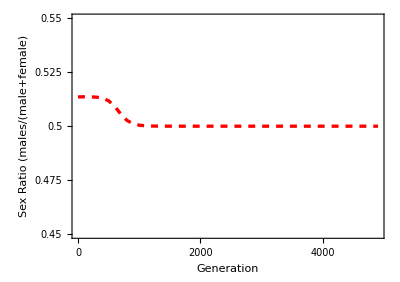

```mathematica
yplotminSexRatio=0.45;
yplotmaxSexRatio=0.55;
yplotintervalSexRatio=0.025;


ListPlot[{Table[{t,
Total[{
sexRatioAtBirth[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,1,tmax,tinterval}]
},
Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotminSexRatio,yplotmaxSexRatio,yplotintervalSexRatio}]},
FrameTicksStyle->Directive[Black,Thickness[lwd]],
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Generation","Sex Ratio (males/(male+female)"},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
Joined->True,
PlotStyle->{Directive[Red,Thickness[lwd],Dashed]},
PlotRange->{yplotminSexRatio,yplotmaxSexRatio}]
```

### Iterate Recursions (W appears to reach 50% after a long time, X not yet completely lost at the end of simulation though)

#### Parameters:

```mathematica
trysAf=0.07;
tryhAf=0.7;
tryhAm=0.7;
trysAm=0.15;
tryt=-0.1;

tryFAA=1+trysAf;
tryFAa=1+tryhAf trysAf;
tryFaa=1;
tryMAA=1+trysAm;
tryMAa=1+tryhAm trysAm;
tryMaa=1;
trywA=1+tryt;
trywa=1;
tryr=0.01;
tryα=0.5;
```

Our invasion analysis indicates that invasion should occur when the following is positive (which assumes that hAm=hAf)

```mathematica
((-1+2 tryr) trysAf (trysAf-trysAm) tryt^2)/(2 tryr (trysAf+trysAm)^2)
```

0.0566942

Also need to specify tryR for full system: (n.b., χ=r R)

```mathematica
tryR=0.5;
```

#### Find equilibrium (equil and sieve functions) [enter]

```mathematica
initialpXf=Flatten[sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryα]][[1]]
initialpXm=Flatten[sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryα]][[2]]
initialYAf=0;
initialYaf=0;
initialpYm=Flatten[sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryα]][[3]]
```

0.770449

0.77974

0.147112

#### IntStab

We check stability by perturbing the system slightly and checking that allele frequencies return. dev gives the initial deviations:

```mathematica
devXf=0.05;
devXm=-0.05;
devYm=0.05;

trypMXAf=0;
trypMXaf=0;
trypMXAm=0;
trypMXam=0;
trypMYAf=0;
trypMYaf=0;
trypMYAm=0;
trypMYam=0;
tmax=1000;
tinterval=10;
```

```mathematica
Show[
ListPlot[
Table[
nextYAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,initialpXf+devXf,(1-initialpXf)-devXf,trypMXAf,trypMXaf,(1-tryα)(initialpXm+devXm),(1-tryα)((1-initialpXm)-devXm),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,tryα*(initialpYm+devYm),tryα*((1-initialpYm)-devYm),trypMYAm,trypMYam]/tryα,
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dashed],
PlotRange->{0,1}],
ListPlot[
Table[
nextYam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,initialpXf+devXf,(1-initialpXf)-devXf,trypMXAf,trypMXaf,(1-tryα)(initialpXm+devXm),(1-tryα)((1-initialpXm)-devXm),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,tryα*(initialpYm+devYm),tryα*((1-initialpYm)-devYm),trypMYAm,trypMYam]/tryα,
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dotted],
PlotRange->{0,1}],
PlotLabel->"Frequencies on Ym"]

Show[
ListPlot[
Table[
nextXAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,initialpXf+devXf,(1-initialpXf)-devXf,trypMXAf,trypMXaf,(1-tryα)(initialpXm+devXm),(1-tryα)((1-initialpXm)-devXm),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,tryα*(initialpYm+devYm),tryα*((1-initialpYm)-devYm),trypMYAm,trypMYam]/(1-tryα),
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dashed],
PlotRange->{0,1}],
ListPlot[
Table[
nextXam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,initialpXf+devXf,(1-initialpXf)-devXf,trypMXAf,trypMXaf,(1-tryα)(initialpXm+devXm),(1-tryα)((1-initialpXm)-devXm),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,tryα*(initialpYm+devYm),tryα*((1-initialpYm)-devYm),trypMYAm,trypMYam]/(1-tryα),
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dotted],
PlotRange->{0,1}],
PlotLabel->"Frequencies on Xm"]

Show[
ListPlot[
Table[
nextXAf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,initialpXf+devXf,(1-initialpXf)-devXf,trypMXAf,trypMXaf,(1-tryα)(initialpXm+devXm),(1-tryα)((1-initialpXm)-devXm),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,tryα*(initialpYm+devYm),tryα*((1-initialpYm)-devYm),trypMYAm,trypMYam],
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dashed],
PlotRange->{0,1}],
ListPlot[
Table[
nextXaf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,initialpXf+devXf,(1-initialpXf)-devXf,trypMXAf,trypMXaf,(1-tryα)(initialpXm+devXm),(1-tryα)((1-initialpXm)-devXm),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,tryα*(initialpYm+devYm),tryα*((1-initialpYm)-devYm),trypMYAm,trypMYam],
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dotted],
PlotRange->{0,1}],
PlotLabel->"Frequencies on Xf"]
```

-Graphics-

-Graphics-

-Graphics-

#### Ext Stab

First, we need to decide on the initial frequency of the new mutation. We will assume that it appear in linkage equilibrium with the old type by introducing it at the same frequencies.

```mathematica
pM=0.0001;

trypMXAf=pM initialpXf;
trypMXaf=pM (1-initialpXf);
trypMXAm=pM(1-tryα) initialpXm;
trypMXam=pM (1-tryα)(1-initialpXm);
trypMYAf=pM initialYAf;
trypMYaf=pM initialYaf;
trypMYAm=pM (tryα)initialpYm;
trypMYam=pM(tryα)(1-initialpYm);
```

Several other parameters are needed for the plots, including the time (tmax) and interval at which the frequencies are registered (tinterval).

```mathematica
tmax=70000;
tinterval=100;
tplotinterval=10000;

(*plot parameters*)
inches=72;
lwd=0.006;(*line thickness as fraction of plot width*)
ticksize={0,0.01};
xplotmin=0;
xplotmax=tmax;
yplotmin=0;
yplotmax=1;
xsize=5inches;
aspectratio=1/Sqrt[2];
```

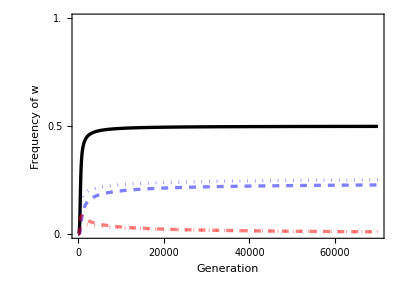

```mathematica
ListPlot[{Table[{t,
Total[{nextYAwf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextYawf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextXAwf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextXawf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextYAwf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextYawf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextXAwf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{
nextXawf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}]
},
Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotmin,yplotmax,0.5}]},
FrameTicksStyle->Directive[Black,Thickness[lwd]],
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Generation","Frequency of w"},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
Joined->True,
PlotStyle->{Directive[Black,Thickness[lwd]],
Directive[Blue,Opacity[0.5],Thickness[lwd],Dashed],
Directive[Blue,Opacity[0.5],Thickness[lwd],Dotted],
Directive[Red,Opacity[0.5],Thickness[lwd],Dashed],
Directive[Red,Opacity[0.5],Thickness[lwd],Dotted]},
PlotRange->{0,1}]
```

Frequency of w at the end of the simulation:

```mathematica
Total[{nextYAwf[tmax,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextYawf[tmax,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextXAwf[tmax,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextXawf[tmax,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]
```

0.499104

which is increasing slightly.

```mathematica
Total[{nextYAwf[tmax,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextYawf[tmax,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextXAwf[tmax,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextXawf[tmax,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]-
Total[{nextYAwf[69000,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextYawf[69000,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextXAwf[69000,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextXawf[69000,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]
```

0.0000192522

```mathematica
ListPlot[{Table[{t,
Total[{nextYAf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextYaf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextXAf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextXaf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextYAf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextYaf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextXAf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{
nextXaf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}]
},
Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotmin,yplotmax,0.5}]},
FrameTicksStyle->Directive[Black,Thickness[lwd]],
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Generation","Frequency of non-w female haploids"},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
Joined->True,
PlotStyle->{Directive[Black,Thickness[lwd]],
Directive[Blue,Opacity[0.5],Thickness[lwd],Dashed],
Directive[Blue,Opacity[0.5],Thickness[lwd],Dotted],
Directive[Red,Opacity[0.5],Thickness[lwd],Dashed],
Directive[Red,Opacity[0.5],Thickness[lwd],Dotted]},
PlotRange->{0,1}]
```

-Graphics-

```mathematica
ListPlot[{Table[{t,
Total[{nextYAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextYam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextYam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextYAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}]
},
Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotmin,yplotmax,0.5}]},
FrameTicksStyle->Directive[Black,Thickness[lwd]],
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Generation","Frequency of Ym"},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
Joined->True,
PlotStyle->{Directive[Blue,Thickness[lwd]],
Directive[Blue,Opacity[0.5],Thickness[lwd],Dashed],
Directive[Blue,Opacity[0.5],Thickness[lwd],Dotted]},
PlotRange->{0,1}]
```

-Graphics-

```mathematica
ListPlot[{Table[{t,
Total[{nextXAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextXam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextXAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextXam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}]
},
Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotmin,yplotmax,0.5}]},
FrameTicksStyle->Directive[Black,Thickness[lwd]],
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Generation","Frequency of Xm"},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
Joined->True,
PlotStyle->{Directive[Red,Thickness[lwd]],
Directive[Red,Opacity[0.5],Thickness[lwd],Dashed],
Directive[Red,Opacity[0.5],Thickness[lwd],Dotted]},
PlotRange->{0,1}]
```

-Graphics-

#### Sex ratio plot

```mathematica
yplotminSexRatio=0.45;
yplotmaxSexRatio=0.55;
yplotintervalSexRatio=0.025;


ListPlot[{Table[{t,
Total[{
sexRatioAtBirth[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,1,tmax,tinterval}]
},
Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotminSexRatio,yplotmaxSexRatio,yplotintervalSexRatio}]},
FrameTicksStyle->Directive[Black,Thickness[lwd]],
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Generation","Sex Ratio (males/(male+female)"},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
Joined->True,
PlotStyle->{Directive[Red,Thickness[lwd],Dashed]},
PlotRange->{yplotminSexRatio,yplotmaxSexRatio}]
```

-Graphics-

### Iterate Recursions (W invades but does not replace XY, polymorphic sex determination maintained without loss of variation)

#### Parameters:

```mathematica
trysAf=0.1;
tryhAf=0.7;
tryhAm=0.7;
trysAm=0.15;
tryt=-0.1;

tryFAA=1+trysAf;
tryFAa=1+tryhAf trysAf;
tryFaa=1;
tryMAA=1+trysAm;
tryMAa=1+tryhAm trysAm;
tryMaa=1;
trywA=1+tryt;
trywa=1;
tryr=0.01;
tryα=0.5;
```

Our invasion analysis indicates that invasion should occur when the following is positive (which assumes that hAm=hAf)

```mathematica
((-1+2 tryr) trysAf (trysAf-trysAm) tryt^2)/(2 tryr (trysAf+trysAm)^2)
```

0.0392

Also need to specify tryR for full system: (n.b., χ=r R)

```mathematica
tryR=1/2;
```

#### Find equilibrium (equil and sieve functions) [enter]

```mathematica
initialpXf=Flatten[sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryα]][[1]]
initialpXm=Flatten[sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryα]][[2]]
initialYAf=0;
initialYaf=0;
initialpYm=Flatten[sieve[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryα]][[3]]
```

0.834904

0.840045

0.15054

#### IntStab

We check stability by perturbing the system slightly and checking that allele frequencies return. dev gives the initial deviations:

```mathematica
devXf=0.05;
devXm=-0.05;
devYm=0.05;

trypMXAf=0;
trypMXaf=0;
trypMXAm=0;
trypMXam=0;
trypMYAf=0;
trypMYaf=0;
trypMYAm=0;
trypMYam=0;
tmax=1000;
tinterval=10;
```

```mathematica
Show[
ListPlot[
Table[
nextYAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,initialpXf+devXf,(1-initialpXf)-devXf,trypMXAf,trypMXaf,(1-tryα)(initialpXm+devXm),(1-tryα)((1-initialpXm)-devXm),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,tryα*(initialpYm+devYm),tryα*((1-initialpYm)-devYm),trypMYAm,trypMYam]/tryα,
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dashed],
PlotRange->{0,1}],
ListPlot[
Table[
nextYam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,initialpXf+devXf,(1-initialpXf)-devXf,trypMXAf,trypMXaf,(1-tryα)(initialpXm+devXm),(1-tryα)((1-initialpXm)-devXm),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,tryα*(initialpYm+devYm),tryα*((1-initialpYm)-devYm),trypMYAm,trypMYam]/tryα,
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dotted],
PlotRange->{0,1}],
PlotLabel->"Frequencies on Ym"]

Show[
ListPlot[
Table[
nextXAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,initialpXf+devXf,(1-initialpXf)-devXf,trypMXAf,trypMXaf,(1-tryα)(initialpXm+devXm),(1-tryα)((1-initialpXm)-devXm),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,tryα*(initialpYm+devYm),tryα*((1-initialpYm)-devYm),trypMYAm,trypMYam]/(1-tryα),
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dashed],
PlotRange->{0,1}],
ListPlot[
Table[
nextXam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,initialpXf+devXf,(1-initialpXf)-devXf,trypMXAf,trypMXaf,(1-tryα)(initialpXm+devXm),(1-tryα)((1-initialpXm)-devXm),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,tryα*(initialpYm+devYm),tryα*((1-initialpYm)-devYm),trypMYAm,trypMYam]/(1-tryα),
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dotted],
PlotRange->{0,1}],
PlotLabel->"Frequencies on Xm"]

Show[
ListPlot[
Table[
nextXAf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,initialpXf+devXf,(1-initialpXf)-devXf,trypMXAf,trypMXaf,(1-tryα)(initialpXm+devXm),(1-tryα)((1-initialpXm)-devXm),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,tryα*(initialpYm+devYm),tryα*((1-initialpYm)-devYm),trypMYAm,trypMYam],
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dashed],
PlotRange->{0,1}],
ListPlot[
Table[
nextXaf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,initialpXf+devXf,(1-initialpXf)-devXf,trypMXAf,trypMXaf,(1-tryα)(initialpXm+devXm),(1-tryα)((1-initialpXm)-devXm),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,tryα*(initialpYm+devYm),tryα*((1-initialpYm)-devYm),trypMYAm,trypMYam],
{t,0,tmax,tinterval}],
Joined->True,
PlotStyle->Directive[Black,Thick,Dotted],
PlotRange->{0,1}],
PlotLabel->"Frequencies on Xf"]
```

-Graphics-

-Graphics-

-Graphics-

#### Ext Stab

First, we need to decide on the initial frequency of the new mutation. We will assume that it appear in linkage equilibrium with the old type by introducing it at the same frequencies.

```mathematica
pM=0.0001;

trypMXAf=pM initialpXf;
trypMXaf=pM (1-initialpXf);
trypMXAm=pM(1-tryα) initialpXm;
trypMXam=pM (1-tryα)(1-initialpXm);
trypMYAf=pM initialYAf;
trypMYaf=pM initialYaf;
trypMYAm=pM (tryα)initialpYm;
trypMYam=pM(tryα)(1-initialpYm);
```

Several other parameters are needed for the plots, including the time (tmax) and interval at which the frequencies are registered (tinterval).

```mathematica
tmax=10000;
tinterval=100;
tplotinterval=2500;

(*plot parameters*)
inches=72;
lwd=0.006;(*line thickness as fraction of plot width*)
ticksize={0,0.01};
xplotmin=0;
xplotmax=tmax;
yplotmin=0;
yplotmax=1;
xsize=5inches;
aspectratio=1/Sqrt[2];
```

```mathematica
ListPlot[{Table[{t,
Total[{nextYAwf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextYawf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextXAwf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextXawf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextYAwf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextYawf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextXAwf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{
nextXawf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}]
},
Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotmin,yplotmax,0.5}]},
FrameTicksStyle->Directive[Black,Thickness[lwd]],
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Generation","Frequency of w"},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
Joined->True,
PlotStyle->{Directive[Black,Thickness[lwd]],
Directive[Blue,Opacity[0.5],Thickness[lwd],Dashed],
Directive[Blue,Opacity[0.5],Thickness[lwd],Dotted],
Directive[Red,Opacity[0.5],Thickness[lwd],Dashed],
Directive[Red,Opacity[0.5],Thickness[lwd],Dotted]},
PlotRange->{0,1}]
```

-Graphics-

Frequency of w at the end of the simulation:

```mathematica
Total[{nextYAwf[tmax,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextYawf[tmax,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextXAwf[tmax,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextXawf[tmax,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]
```

0.272086

which is barely changing:

```mathematica
Total[{nextYAwf[tmax,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextYawf[tmax,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextXAwf[tmax,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextXawf[tmax,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]-
Total[{nextYAwf[tmax-1000,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextYawf[tmax-1000,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextXAwf[tmax-1000,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextXawf[tmax-1000,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]
```

3.70147×10^-8

```mathematica
ListPlot[{Table[{t,
Total[{nextYAf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextYaf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextXAf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextXaf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextYAf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextYaf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextXAf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{
nextXaf[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}]
},
Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotmin,yplotmax,0.5}]},
FrameTicksStyle->Directive[Black,Thickness[lwd]],
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Generation","Frequency of non-w female haploids"},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
Joined->True,
PlotStyle->{Directive[Black,Thickness[lwd]],
Directive[Blue,Opacity[0.5],Thickness[lwd],Dashed],
Directive[Blue,Opacity[0.5],Thickness[lwd],Dotted],
Directive[Red,Opacity[0.5],Thickness[lwd],Dashed],
Directive[Red,Opacity[0.5],Thickness[lwd],Dotted]},
PlotRange->{0,1}]
```

-Graphics-

```mathematica
ListPlot[{Table[{t,
Total[{nextYAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextYam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextYam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextYAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}]
},
Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotmin,yplotmax,0.5}]},
FrameTicksStyle->Directive[Black,Thickness[lwd]],
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Generation","Frequency of Ym"},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
Joined->True,
PlotStyle->{Directive[Blue,Thickness[lwd]],
Directive[Blue,Opacity[0.5],Thickness[lwd],Dashed],
Directive[Blue,Opacity[0.5],Thickness[lwd],Dotted]},
PlotRange->{0,1}]
```

-Graphics-

```mathematica
ListPlot[{Table[{t,
Total[{nextXAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam],
nextXam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextXAm[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}],
Table[{t,
Total[{nextXam[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,0,tmax,tinterval}]
},
Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotmin,yplotmax,0.5}]},
FrameTicksStyle->Directive[Black,Thickness[lwd]],
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Generation","Frequency of Xm"},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
Joined->True,
PlotStyle->{Directive[Red,Thickness[lwd]],
Directive[Red,Opacity[0.5],Thickness[lwd],Dashed],
Directive[Red,Opacity[0.5],Thickness[lwd],Dotted]},
PlotRange->{0,1}]
```

-Graphics-

#### Sex ratio plot

```mathematica
yplotminSexRatio=0.45;
yplotmaxSexRatio=0.55;
yplotintervalSexRatio=0.025;


ListPlot[{Table[{t,
Total[{
sexRatioAtBirth[t,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
}]},{t,1,tmax,tinterval}]
},
Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,tplotinterval}],Table[{y,y,ticksize},{y,yplotminSexRatio,yplotmaxSexRatio,yplotintervalSexRatio}]},
FrameTicksStyle->Directive[Black,Thickness[lwd]],
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Generation","Sex Ratio (males/(male+female)"},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
Joined->True,
PlotStyle->{Directive[Red,Thickness[lwd],Dashed]},
PlotRange->{yplotminSexRatio,yplotmaxSexRatio}]
```

-Graphics-

```mathematica
sexRatioAtBirth[tmax,tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywA,trywa,tryr,tryR,tryα,(1-pM)initialpXf,(1-pM)(1-initialpXf),trypMXAf,trypMXaf,(1-pM)(1-tryα)(initialpXm),(1-pM)(1-tryα)((1-initialpXm)),trypMXAm,trypMXam,initialYAf,initialYaf,trypMYAf,trypMYaf,(1-pM)tryα*(initialpYm),(1-pM)tryα*((1-initialpYm)),trypMYAm,trypMYam]
```

0.505227

$Aborted

# ESD invades XY (parental control)

## Recursions

We consider three loci: 1) a diallelic genetic sex-determining (GSD) locus, 2) a diallelic locus under viability selection (VS), and 3) a diallelic environmentally sex-determining (ESD) locus. We assume that initially, the ESD locus is fixed for a null allele E, that does nothing and thus sex is determined by the GSD locus. We will then look at the invasion of a rare mutant allele e at the ESD locus, which is dominant over E and the GSD locus. We will assume that the sex of diploids is determined by the maternal ESD genotype. A proportion k of offspring from mothers with Ee or ee genotypes will be female and a proportion 1-k will be male (i.e., e changes the “behaviour” of the mother that determines sex of her offspring, eg. epigenetic mark or burying eggs in the sand).

We will call the alleles at the GSD locus X and Y with Y masculinizing and dominant over X. We can easily convert to a ZW system by making Z=X and W=Y and male=female and female=male.

Haploid selection: starting with haploid genotype frequencies fHap in each sex, the frequencies after selection fHapSel are

```mathematica
wbarHap[sex_]:=wbarHap[sex]=
Sum[wHap[x,y,z,sex,homhet]fHap[x,y,z,sex,homhet],{x,1,2},{y,1,2},{z,1,2},{homhet,1,2}];
fHapSel[x_,y_,z_,sex_,homhet_]:=fHapSel[x,y,z,sex,homhet]=
wHap[x,y,z,sex,homhet]fHap[x,y,z,sex,homhet]/wbarHap[sex]
(*Sum[fHapSel[x,y,z,sex,homhetM],{x,1,2},{y,1,2},{z,1,2},{homhetM,{hom,het}}]//Factor*)
```

where x is the allele at the GSD locus, y is the allele at the VS locus, z is the allele at the ESD locus, and sex is male or female. homhet indicates whether the parental genotype at the ESD locus was homozygous or heterozygous. Notice that the fitness of a haploid genotype wHap depends on the sex of its parent and gametes of the opposite sex do not compete with one another (wbarHap is mean fitness of gametes in each sex).

Gametic union: haploid genotypes pair at random giving diploid genotype frequencies fDip

```mathematica
fDip[xM_,yM_,zM_,xP_,yP_,zP_,homhetM_,homhetP_]:=fDip[xM,yM,zM,xP,yP,zP,homhetM,homhetP]=
fHapSel[xM,yM,zM,2,homhetM]fHapSel[xP,yP,zP,1,homhetP]
(*Sum[fDip[xM,yM,zM,xP,yP,zP,homhetM],{xM,1,2},{yM,1,2},{zM,1,2},{xP,1,2},{yP,1,2},{zP,1,2},{homhetM,{hom,het}},{homhetP,{hom,het}}]//FullSimplify*)
```

Sex determination:

```mathematica
fDipSex[xM_,yM_,zM_,xP_,yP_,zP_,sex_]:=fDipSex[xM,yM,zM,xP,yP,zP,sex]=
Sum[fDip[xM,yM,zM,xP,yP,zP,homhetM,homhetP]psex[xM,yM,zM,xP,yP,zP,sex,homhetM,homhetP],{homhetM,1,2},{homhetP,1,2}]
```

where an individual must be male or female

```mathematica
sumsex=psex[xM_,yM_,zM_,xP_,yP_,zP_,female,homhetM_,homhetP_]->1-psex[xM,yM,zM,xP,yP,zP,male,homhetM,homhetP]/.male->1/.female->2;
```

Here we will be concerned with environmental sex determination invading male heterogamy:

```mathematica
ESDXY={
psex[xM_,yM_,1,2,yP_,zP_,male,hom,homhetP_]->1,
psex[xM_,yM_,1,1,yP_,zP_,male,hom,homhetP_]->0,
fHap[2,y_,1,female,hom]->0,
psex[xM_,yM_,2,xP_,yP_,zP_,male,homhetM_,homhetP_]->1-k,
psex[xM_,yM_,1,xP_,yP_,zP_,male,het,homhetP_]->1-k}/.male->1/.female->2/.hom->1/.het->2;
```

```mathematica
ESDXY={
psex[xM_,yM_,1,2,yP_,zP_,male,hom,homhetP_]->1,
psex[xM_,yM_,1,1,yP_,zP_,male,hom,homhetP_]->0,
fHap[2,y_,1,female,hom]->0,
psex[xM_,yM_,2,xP_,yP_,zP_,male,homhetM_,homhetP_]->1-k,
psex[xM_,yM_,1,xP_,yP_,zP_,male,het,homhetP_]->1-k}/.male->1/.female->2/.hom->1/.het->2;
```

Diploid selection: if all individuals compete with one another (ie. for resources) then the frequencies of diploid genotypes after selection fDipSel are

```mathematica
wbarDip=Sum[wDip[xM,yM,zM,xP,yP,zP,sex]fDipSex[xM,yM,zM,xP,yP,zP,sex],{xM,1,2},{yM,1,2},{zM,1,2},{xP,1,2},{yP,1,2},{zP,1,2},{sex,1,2}];
fDipSel[xM_,yM_,zM_,xP_,yP_,zP_,sex_]:=fDipSel[xM,yM,zM,xP,yP,zP,sex]=
wDip[xM,yM,zM,xP,yP,zP,sex]fDipSex[xM,yM,zM,xP,yP,zP,sex]/wbarDip;
(*Sum[fDipSel[xM,yM,zM,xP,yP,zP,sex],{xM,1,2},{yM,1,2},{zM,1,2},{xP,1,2},{yP,1,2},{zP,1,2},{sex,{male,female}}]/.sumsex/.ESDXY//Factor*)
```

Alternatively, males could compete with males and female with females (ie. competition over mates). Then

```mathematica
wbarDipMale=Sum[wDip[x1,y1,z1,x2,y2,z2,1]fDipSex[x1,y1,z1,x2,y2,z2,1],{x1,1,2},{y1,1,2},{z1,1,2},{x2,1,2},{y2,1,2},{z2,1,2}];
wbarDipFemale=Sum[wDip[x1,y1,z1,x2,y2,z2,2]fDipSex[x1,y1,z1,x2,y2,z2,2],{x1,1,2},{y1,1,2},{z1,1,2},{x2,1,2},{y2,1,2},{z2,1,2}];
fDipSel[x1_,y1_,z1_,x2_,y2_,z2_,1]:=fDipSel[x1,y1,z1,x2,y2,z2,1]=
wDip[x1,y1,z1,x2,y2,z2,1]fDipSex[x1,y1,z1,x2,y2,z2,1]/wbarDipMale;
fDipSel[x1_,y1_,z1_,x2_,y2_,z2_,2]:=fDipSel[x1,y1,z1,x2,y2,z2,2]=
wDip[x1,y1,z1,x2,y2,z2,2]fDipSex[x1,y1,z1,x2,y2,z2,2]/wbarDipFemale;
(*Sum[fDipSel[x1,y1,z1,x2,y2,z2,sex],{x1,1,2},{y1,1,2},{z1,1,2},{x2,1,2},{y2,1,2},{z2,1,2},{sex,{male,female}}]/.sumsex/.ESDXY//Factor*)
```

Meiosis: if pseg is the probability that a diploid genotype of a particular sex produces a gamete of a given haploid genoytpe, then the frequencies of haploid genotypes in the next generation are

```mathematica
(*fHapNextTot[x_,y_,z_,sex_,homhet_]:=fHapNextTot[x,y,z,sex,homhet]=
Sum[fDipSel[xM,yM,zM,xP,yP,zP,sex]pseg[xM,yM,zM,xP,yP,zP,sex,x,y,z,homhet],{xM,1,2},{yM,1,2},{zM,1,2},{xP,1,2},{yP,1,2},{zP,1,2}];*)
```

```mathematica
fHapNext[x_,y_,z_,sex_,homhet_]:=fHapNext[x,y,z,sex,homhet]=
Sum[fDipSel[xM,yM,zM,xP,yP,zP,sex]pseg[xM,yM,zM,xP,yP,zP,sex,x,y,z,homhet],{xM,1,2},{yM,1,2},{zM,1,2},{xP,1,2},{yP,1,2},{zP,1,2}];
```

And the frequency from each sex is

```mathematica
(*totalNum={Sum[fHapNextTot[x1,y1,z1,1,homhet1],{x1,1,2},{y1,1,2},{z1,1,2},{homhet1,1,2}],Sum[fHapNextTot[x1,y1,z1,2,homhet1],{x1,1,2},{y1,1,2},{z1,1,2},{homhet1,1,2}]};
fHapNext[x_,y_,z_,sex_,homhet_]:=fHapNext[x,y,z,sex,homhet]=
fHapNextTot[x,y,z,sex,homhet]/totalNum[[sex]]*)
```

With recombination and no meiotic drive (and with linear arrangement x-y-z with recombination probability r between x and y and probability R between y and z) we have

```mathematica
pseg0={
(*triple homozygote*)
pseg[x1_,y1_,z1_,x1_,y1_,z1_,sex_,x1_,y1_,z1_,hom]->1,
pseg[x1_,y1_,z1_,x1_,y1_,z1_,sex_,x1_,y1_,z1_,het]->0
}/.hom->1/.het->2;
pseg1={
(*single heterozygotes*)
pseg[x1_,y1_,z1_,x2_,y1_,z1_,sex_,x1_,y1_,z1_,hom]->1/2,
pseg[x1_,y1_,z1_,x2_,y1_,z1_,sex_,x2_,y1_,z1_,hom]->1/2,
pseg[x1_,y1_,z1_,x1_,y2_,z1_,sex_,x1_,y1_,z1_,hom]->1/2,
pseg[x1_,y1_,z1_,x1_,y2_,z1_,sex_,x1_,y2_,z1_,hom]->1/2,
pseg[x1_,y1_,z1_,x2_,y1_,z1_,sex_,x1_,y1_,z1_,het]->0,
pseg[x1_,y1_,z1_,x2_,y1_,z1_,sex_,x2_,y1_,z1_,het]->0,
pseg[x1_,y1_,z1_,x1_,y2_,z1_,sex_,x1_,y1_,z1_,het]->0,
pseg[x1_,y1_,z1_,x1_,y2_,z1_,sex_,x1_,y2_,z1_,het]->0,
pseg[x1_,y1_,z1_,x1_,y1_,z2_,sex_,x1_,y1_,z1_,het]->1/2,
pseg[x1_,y1_,z1_,x1_,y1_,z2_,sex_,x1_,y1_,z2_,het]->1/2
}/.hom->1/.het->2;
pseg2={
(*double heterozygotes*)
pseg[x1_,y1_,z1_,x2_,y2_,z1_,sex_,x1_,y1_,z1_,hom]->(1-r)/2,
pseg[x1_,y1_,z1_,x2_,y2_,z1_,sex_,x2_,y2_,z1_,hom]->(1-r)/2,
pseg[x1_,y1_,z1_,x2_,y2_,z1_,sex_,x2_,y1_,z1_,hom]->r/2,
pseg[x1_,y1_,z1_,x2_,y2_,z1_,sex_,x1_,y2_,z1_,hom]->r/2,
pseg[x1_,y1_,z1_,x2_,y2_,z1_,sex_,x1_,y1_,z1_,het]->0,
pseg[x1_,y1_,z1_,x2_,y2_,z1_,sex_,x2_,y2_,z1_,het]->0,
pseg[x1_,y1_,z1_,x2_,y2_,z1_,sex_,x2_,y1_,z1_,het]->0,
pseg[x1_,y1_,z1_,x2_,y2_,z1_,sex_,x1_,y2_,z1_,het]->0,
pseg[x1_,y1_,z1_,x1_,y2_,z2_,sex_,x1_,y1_,z1_,het]->(1-R)/2,
pseg[x1_,y1_,z1_,x1_,y2_,z2_,sex_,x1_,y2_,z2_,het]->(1-R)/2,
pseg[x1_,y1_,z1_,x1_,y2_,z2_,sex_,x1_,y2_,z1_,het]->R/2,
pseg[x1_,y1_,z1_,x1_,y2_,z2_,sex_,x1_,y1_,z2_,het]->R/2,
pseg[x1_,y1_,z1_,x2_,y1_,z2_,sex_,x1_,y1_,z1_,het]->((1-r)(1-R)+r R)/2,
pseg[x1_,y1_,z1_,x2_,y1_,z2_,sex_,x2_,y1_,z2_,het]->((1-r)(1-R)+r R)/2,
pseg[x1_,y1_,z1_,x2_,y1_,z2_,sex_,x2_,y1_,z1_,het]->(r(1-R)+(1-r)R)/2,
pseg[x1_,y1_,z1_,x2_,y1_,z2_,sex_,x1_,y1_,z2_,het]->(r(1-R)+(1-r)R)/2
}/.hom->1/.het->2;
pseg3={
(*triple heterozygote*)
pseg[x1_,y1_,z1_,x2_,y2_,z2_,sex_,x1_,y1_,z1_,het]->(1-r)(1-R)/2,
pseg[x1_,y1_,z1_,x2_,y2_,z2_,sex_,x2_,y2_,z2_,het]->(1-r)(1-R)/2,
pseg[x1_,y1_,z1_,x2_,y2_,z2_,sex_,x2_,y1_,z1_,het]->r(1-R)/2,
pseg[x1_,y1_,z1_,x2_,y2_,z2_,sex_,x1_,y2_,z2_,het]->r(1-R)/2,
pseg[x1_,y1_,z1_,x2_,y2_,z2_,sex_,x1_,y2_,z1_,het]->r R/2,
pseg[x1_,y1_,z1_,x2_,y2_,z2_,sex_,x2_,y1_,z2_,het]->r R/2,
pseg[x1_,y1_,z1_,x2_,y2_,z2_,sex_,x1_,y1_,z2_,het]->(1-r)R/2,
pseg[x1_,y1_,z1_,x2_,y2_,z2_,sex_,x2_,y2_,z1_,het]->(1-r)R/2
}/.hom->1/.het->2;
pseg4=pseg[x1_,y1_,z1_,x2_,y2_,z2_,sex_,x_,y_,z_,homhet_]->0;
```

And the frequencies of gametes from each sex in the next generation sum to one (this takes a minute)

```mathematica
Sum[fHapNext[x,y,z,1,homhet]/.sumsex/.ESDXY/.pseg0/.pseg1/.pseg2/.pseg3/.pseg4,{x,1,2},{y,1,2},{z,1,2},{homhet,1,2}]//Factor
```

1

## Recursions

We consider three loci: 1) a diallelic genetic sex-determining (GSD) locus, 2) a diallelic locus under viability selection (VS), and 3) a diallelic environmentally sex-determining (ESD) locus. We assume that initially, the ESD locus is fixed for a null allele E, that does nothing and thus sex is determined by the GSD locus. We will then look at the invasion of a rare mutant allele e at the ESD locus, which is dominant over E and the GSD locus. We will assume that the sex of diploids is determined by the maternal ESD genotype. A proportion k of offspring from mothers with Ee or ee genotypes will be female and a proportion 1-k will be male (i.e., e changes the “behaviour” of the mother that determines sex of her offspring, eg. epigenetic mark or burying eggs in the sand).

We will call the alleles at the GSD locus X and Y with Y masculinizing and dominant over X. We can easily convert to a ZW system by making Z=X and W=Y and male=female and female=male.

Haploid selection: starting with haploid genotype frequencies fHap in each sex, the frequencies after selection fHapSel are

```mathematica
wbarHap[sex_]:=wbarHap[sex]=
Sum[wHap[x,y,z,sex,homhet]fHap[x,y,z,sex,homhet],{x,1,2},{y,1,2},{z,1,2},{homhet,1,3}];
fHapSel[x_,y_,z_,sex_,homhet_]:=fHapSel[x,y,z,sex,homhet]=
wHap[x,y,z,sex,homhet]fHap[x,y,z,sex,homhet]/wbarHap[sex]
(*Sum[fHapSel[x,y,z,sex,homhetM],{x,1,2},{y,1,2},{z,1,2},{homhetM,{hom,het}}]//Factor*)
```

where x is the allele at the GSD locus, y is the allele at the VS locus, z is the allele at the ESD locus, and sex is male or female. homhet indicates whether the parental genotype at the ESD locus was homozygous or heterozygous. Notice that the fitness of a haploid genotype wHap depends on the sex of its parent and gametes of the opposite sex do not compete with one another (wbarHap is mean fitness of gametes in each sex).

Gametic union: haploid genotypes pair at random giving diploid genotype frequencies fDip

```mathematica
fDip[xM_,yM_,zM_,xP_,yP_,zP_,homhetM_,homhetP_]:=fDip[xM,yM,zM,xP,yP,zP,homhetM,homhetP]=
fHapSel[xM,yM,zM,2,homhetM]fHapSel[xP,yP,zP,1,homhetP]
(*Sum[fDip[xM,yM,zM,xP,yP,zP,homhetM],{xM,1,2},{yM,1,2},{zM,1,2},{xP,1,2},{yP,1,2},{zP,1,2},{homhetM,{hom,het}},{homhetP,{hom,het}}]//FullSimplify*)
```

Sex determination:

```mathematica
fDipSex[xM_,yM_,zM_,xP_,yP_,zP_,sex_]:=fDipSex[xM,yM,zM,xP,yP,zP,sex]=
Sum[fDip[xM,yM,zM,xP,yP,zP,homhetM,homhetP]psex[xM,yM,zM,xP,yP,zP,sex,homhetM,homhetP],{homhetM,1,3},{homhetP,1,3}]
```

where an individual must be male or female

```mathematica
sumsex=psex[xM_,yM_,zM_,xP_,yP_,zP_,female,homhetM_,homhetP_]->1-psex[xM,yM,zM,xP,yP,zP,male,homhetM,homhetP]/.male->1/.female->2;
```

Here we will be concerned with environmental sex determination invading male heterogamy:

```mathematica
ESDXY={
psex[xM_,yM_,zM_,2,yP_,zP_,male,homWT,homhetP_]->1,
psex[xM_,yM_,zM_,1,yP_,zP_,male,homWT,homhetP_]->0,
fHap[2,y_,z_,female,homWT]->0,
psex[xM_,yM_,zM_,xP_,yP_,zP_,male,het,homhetP_]->1-k,
psex[xM_,yM_,zM_,xP_,yP_,zP_,male,homMUT,homhetP_]->1-k
}/.male->1/.female->2/.homWT->1/.het->2/.homMUT->3;
```

Diploid selection: if all individuals compete with one another (ie. for resources) then the frequencies of diploid genotypes after selection fDipSel are

```mathematica
wbarDip=Sum[wDip[xM,yM,zM,xP,yP,zP,sex]fDipSex[xM,yM,zM,xP,yP,zP,sex],{xM,1,2},{yM,1,2},{zM,1,2},{xP,1,2},{yP,1,2},{zP,1,2},{sex,1,2}];
fDipSel[xM_,yM_,zM_,xP_,yP_,zP_,sex_]:=fDipSel[xM,yM,zM,xP,yP,zP,sex]=
wDip[xM,yM,zM,xP,yP,zP,sex]fDipSex[xM,yM,zM,xP,yP,zP,sex]/wbarDip;
(*Sum[fDipSel[xM,yM,zM,xP,yP,zP,sex],{xM,1,2},{yM,1,2},{zM,1,2},{xP,1,2},{yP,1,2},{zP,1,2},{sex,{male,female}}]/.sumsex/.ESDXY//Factor*)
```

Alternatively, males could compete with males and female with females (ie. competition over mates). Then

```mathematica
wbarDipMale=Sum[wDip[x1,y1,z1,x2,y2,z2,1]fDipSex[x1,y1,z1,x2,y2,z2,1],{x1,1,2},{y1,1,2},{z1,1,2},{x2,1,2},{y2,1,2},{z2,1,2}];
wbarDipFemale=Sum[wDip[x1,y1,z1,x2,y2,z2,2]fDipSex[x1,y1,z1,x2,y2,z2,2],{x1,1,2},{y1,1,2},{z1,1,2},{x2,1,2},{y2,1,2},{z2,1,2}];
fDipSel[x1_,y1_,z1_,x2_,y2_,z2_,1]:=fDipSel[x1,y1,z1,x2,y2,z2,1]=
wDip[x1,y1,z1,x2,y2,z2,1]fDipSex[x1,y1,z1,x2,y2,z2,1]/wbarDipMale;
fDipSel[x1_,y1_,z1_,x2_,y2_,z2_,2]:=fDipSel[x1,y1,z1,x2,y2,z2,2]=
wDip[x1,y1,z1,x2,y2,z2,2]fDipSex[x1,y1,z1,x2,y2,z2,2]/wbarDipFemale;
(*Sum[fDipSel[x1,y1,z1,x2,y2,z2,sex],{x1,1,2},{y1,1,2},{z1,1,2},{x2,1,2},{y2,1,2},{z2,1,2},{sex,{male,female}}]/.sumsex/.ESDXY//Factor*)
```

Meiosis: if pseg is the probability that a diploid genotype of a particular sex produces a gamete of a given haploid genoytpe, then the frequencies of haploid genotypes in the next generation are

```mathematica
(*fHapNextTot[x_,y_,z_,sex_,homhet_]:=fHapNextTot[x,y,z,sex,homhet]=
Sum[fDipSel[xM,yM,zM,xP,yP,zP,sex]pseg[xM,yM,zM,xP,yP,zP,sex,x,y,z,homhet],{xM,1,2},{yM,1,2},{zM,1,2},{xP,1,2},{yP,1,2},{zP,1,2}];*)
```

```mathematica
fHapNext[x_,y_,z_,sex_,homhet_]:=fHapNext[x,y,z,sex,homhet]=
Sum[fDipSel[xM,yM,zM,xP,yP,zP,sex]pseg[xM,yM,zM,xP,yP,zP,sex,x,y,z,homhet],{xM,1,2},{yM,1,2},{zM,1,2},{xP,1,2},{yP,1,2},{zP,1,2}];
```

And the frequency from each sex is

```mathematica
(*totalNum={Sum[fHapNextTot[x1,y1,z1,1,homhet1],{x1,1,2},{y1,1,2},{z1,1,2},{homhet1,1,2}],Sum[fHapNextTot[x1,y1,z1,2,homhet1],{x1,1,2},{y1,1,2},{z1,1,2},{homhet1,1,2}]};
fHapNext[x_,y_,z_,sex_,homhet_]:=fHapNext[x,y,z,sex,homhet]=
fHapNextTot[x,y,z,sex,homhet]/totalNum[[sex]]*)
```

With recombination and no meiotic drive (and with linear arrangement x-y-z with recombination probability r between x and y and probability R between y and z) we have

```mathematica
pseg0={
(*triple homozygote*)
pseg[x1_,y1_,1,x1_,y1_,1,sex_,x1_,y1_,1,homWT]->1,
pseg[x1_,y1_,2,x1_,y1_,2,sex_,x1_,y1_,2,homMUT]->1,
pseg[x1_,y1_,z1_,x1_,y1_,z1_,sex_,x1_,y1_,z1_,het]->0
}/.homWT->1/.het->2/.homMUT->3;
pseg1={
(*single heterozygotes*)
pseg[x1_,y1_,1,x2_,y1_,1,sex_,x1_,y1_,1,homWT]->1/2,
pseg[x1_,y1_,1,x2_,y1_,1,sex_,x2_,y1_,1,homWT]->1/2,
pseg[x1_,y1_,1,x1_,y2_,1,sex_,x1_,y1_,1,homWT]->1/2,
pseg[x1_,y1_,1,x1_,y2_,1,sex_,x1_,y2_,1,homWT]->1/2,
pseg[x1_,y1_,2,x2_,y1_,2,sex_,x1_,y1_,2,homMUT]->1/2,
pseg[x1_,y1_,2,x2_,y1_,2,sex_,x2_,y1_,2,homMUT]->1/2,
pseg[x1_,y1_,2,x1_,y2_,2,sex_,x1_,y1_,2,homMUT]->1/2,
pseg[x1_,y1_,2,x1_,y2_,2,sex_,x1_,y2_,2,homMUT]->1/2,
pseg[x1_,y1_,z1_,x2_,y1_,z1_,sex_,x1_,y1_,z1_,het]->0,
pseg[x1_,y1_,z1_,x2_,y1_,z1_,sex_,x2_,y1_,z1_,het]->0,
pseg[x1_,y1_,z1_,x1_,y2_,z1_,sex_,x1_,y1_,z1_,het]->0,
pseg[x1_,y1_,z1_,x1_,y2_,z1_,sex_,x1_,y2_,z1_,het]->0,
pseg[x1_,y1_,z1_,x1_,y1_,z2_,sex_,x1_,y1_,z1_,het]->1/2,
pseg[x1_,y1_,z1_,x1_,y1_,z2_,sex_,x1_,y1_,z2_,het]->1/2
}/.homWT->1/.het->2/.homMUT->3;
pseg2={
(*double heterozygotes*)
pseg[x1_,y1_,1,x2_,y2_,1,sex_,x1_,y1_,1,homWT]->(1-r)/2,
pseg[x1_,y1_,1,x2_,y2_,1,sex_,x2_,y2_,1,homWT]->(1-r)/2,
pseg[x1_,y1_,1,x2_,y2_,1,sex_,x2_,y1_,1,homWT]->r/2,
pseg[x1_,y1_,1,x2_,y2_,1,sex_,x1_,y2_,1,homWT]->r/2,
pseg[x1_,y1_,2,x2_,y2_,2,sex_,x1_,y1_,2,homMUT]->(1-r)/2,
pseg[x1_,y1_,2,x2_,y2_,2,sex_,x2_,y2_,2,homMUT]->(1-r)/2,
pseg[x1_,y1_,2,x2_,y2_,2,sex_,x2_,y1_,2,homMUT]->r/2,
pseg[x1_,y1_,2,x2_,y2_,2,sex_,x1_,y2_,2,homMUT]->r/2,
pseg[x1_,y1_,z1_,x2_,y2_,z1_,sex_,x1_,y1_,z1_,het]->0,
pseg[x1_,y1_,z1_,x2_,y2_,z1_,sex_,x2_,y2_,z1_,het]->0,
pseg[x1_,y1_,z1_,x2_,y2_,z1_,sex_,x2_,y1_,z1_,het]->0,
pseg[x1_,y1_,z1_,x2_,y2_,z1_,sex_,x1_,y2_,z1_,het]->0,
pseg[x1_,y1_,z1_,x1_,y2_,z2_,sex_,x1_,y1_,z1_,het]->(1-R)/2,
pseg[x1_,y1_,z1_,x1_,y2_,z2_,sex_,x1_,y2_,z2_,het]->(1-R)/2,
pseg[x1_,y1_,z1_,x1_,y2_,z2_,sex_,x1_,y2_,z1_,het]->R/2,
pseg[x1_,y1_,z1_,x1_,y2_,z2_,sex_,x1_,y1_,z2_,het]->R/2,
pseg[x1_,y1_,z1_,x2_,y1_,z2_,sex_,x1_,y1_,z1_,het]->((1-r)(1-R)+r R)/2,
pseg[x1_,y1_,z1_,x2_,y1_,z2_,sex_,x2_,y1_,z2_,het]->((1-r)(1-R)+r R)/2,
pseg[x1_,y1_,z1_,x2_,y1_,z2_,sex_,x2_,y1_,z1_,het]->(r(1-R)+(1-r)R)/2,
pseg[x1_,y1_,z1_,x2_,y1_,z2_,sex_,x1_,y1_,z2_,het]->(r(1-R)+(1-r)R)/2
}/.homWT->1/.het->2/.homMUT->3;
pseg3={
(*triple heterozygote*)
pseg[x1_,y1_,z1_,x2_,y2_,z2_,sex_,x1_,y1_,z1_,het]->(1-r)(1-R)/2,
pseg[x1_,y1_,z1_,x2_,y2_,z2_,sex_,x2_,y2_,z2_,het]->(1-r)(1-R)/2,
pseg[x1_,y1_,z1_,x2_,y2_,z2_,sex_,x2_,y1_,z1_,het]->r(1-R)/2,
pseg[x1_,y1_,z1_,x2_,y2_,z2_,sex_,x1_,y2_,z2_,het]->r(1-R)/2,
pseg[x1_,y1_,z1_,x2_,y2_,z2_,sex_,x1_,y2_,z1_,het]->r R/2,
pseg[x1_,y1_,z1_,x2_,y2_,z2_,sex_,x2_,y1_,z2_,het]->r R/2,
pseg[x1_,y1_,z1_,x2_,y2_,z2_,sex_,x1_,y1_,z2_,het]->(1-r)R/2,
pseg[x1_,y1_,z1_,x2_,y2_,z2_,sex_,x2_,y2_,z1_,het]->(1-r)R/2
}/.homWT->1/.het->2/.homMUT->3;
pseg4=pseg[x1_,y1_,z1_,x2_,y2_,z2_,sex_,x_,y_,z_,homhet_]->0;
```

And the frequencies of gametes from each sex in the next generation sum to one (this takes a minute)

```mathematica
Sum[fHapNext[x,y,z,1,homhet]/.sumsex/.ESDXY/.pseg0/.pseg1/.pseg2/.pseg3/.pseg4,{x,1,2},{y,1,2},{z,1,2},{homhet,1,3}]//Factor
```

1

## Resident equilibrium (weak selection)

We first assume that the ESD locus is fixed for the null allele

```mathematica
subequil={
fHap[1,1,1,female,homWT]->pXf,
fHap[1,2,1,female,homWT]->1-pXf,
fHap[1,1,1,male,homWT]->(1-α)pXm,
fHap[1,2,1,male,homWT]->(1-α)(1-pXm),
fHap[2,1,1,male,homWT]->α pYm,
fHap[2,2,1,male,homWT]->α(1-pYm),
fHap[x_,y_,2,sex_,homhet_]->0,
fHap[x_,y_,1,sex_,het]->0
}/.male->1/.female->2/.homWT->1/.het->2/.α->1/2;
```

where pXf is the frequency of A in non-mutant eggs, pXm is the frequency of A in gametes from males with an X allele, and pY is the frequency of A in gametes from males with a Y allele. α is the frequency of male gametes that are Y bearing (we assume α=1/2 ie no drive).

We now wish to solve for the equilibrium frequencies of the haploid genotypes in gametes of each sex. Equilibrium is achieved when the following three equations are zero (this takes a minute)

```mathematica
differenceEqs={
fHapNext[1,1,1,2,1]-fHap[1,1,1,2,1],
fHapNext[1,1,1,1,1]-fHap[1,1,1,1,1],
fHapNext[2,1,1,1,1]-fHap[2,1,1,1,1]
}/.subequil/.pseg0/.pseg1/.pseg2/.pseg3/.pseg4/.sumsex/.ESDXY;
```

To simplify the analysis we assume weak selection in both haploids and diploids. In addition, we assume selection acts on the VS locus only

```mathematica
weaksel={
wHap[x_,1,z_,sex_,homhet_]->1,
wHap[x_,2,z_,sex_,homhet_]->1+sHap[sex] ϵ,
wDip[x1_,1,z1_,x2_,1,z2_,sex_]->1,
wDip[x1_,1,z1_,x2_,2,z2_,sex_]->1+h[sex] sDip[sex] ϵ,
wDip[x1_,2,z1_,x2_,1,z2_,sex_]->1+h[sex] sDip[sex] ϵ,
wDip[x1_,2,z1_,x2_,2,z2_,sex_]->1+ sDip[sex] ϵ
};
```

We can write the frequencies as Taylor series

```mathematica
frequenciessub={
pXf->pXf0+pXf1 ϵ,
pXm->pXm0+pXm1 ϵ,
pYm->pYm0+pYm1 ϵ
};
```

Without selection the recursions for the change in the frequencies are

```mathematica
differenceEqs0=Normal[Series[differenceEqs/.weaksel/.frequenciessub,{ϵ,0,0}]]//Factor
```

{1/2 (-pXf0+pXm0),1/2 (pXf0-pXm0-pXf0 r+pYm0 r),1/2 (pXf0-pYm0) r}

{1/2 (-pXf0+pXm0),1/2 (pXf0-pXm0-pXf0 r+pYm0 r),1/2 (pXf0-pYm0) r}

And at equilibrium we have

```mathematica
sol0=Solve[differenceEqs0==0,{pXm0,pYm0}]
```

{{pXm0→pXf0,pYm0→pXf0}}

{{pXm0→pXf0,pYm0→pXf0}}

So, with no selection, the equilibrium frequency of A in each gamete/pollen type is equal (and we call this pA).

Now, looking at only the first order selection terms, the recursions for the change in frequency of A in each gamete/pollen type are

```mathematica
differenceEqs1=Collect[Normal[Series[differenceEqs/.weaksel/.frequenciessub/.sol0,{ϵ,0,1}]],ϵ,Factor]/.pXf0->pA//Flatten
```

{1/2 ϵ (-pXf1+pXm1-2 pA sDip[2]+4 pA^2 sDip[2]-2 pA^3 sDip[2]+2 pA h[2] sDip[2]-6 pA^2 h[2] sDip[2]+4 pA^3 h[2] sDip[2]-pA sHap[1]+pA^2 sHap[1]-pA sHap[2]+pA^2 sHap[2]),1/2 ϵ (pXf1-pXm1-pXf1 r+pYm1 r-pA sDip[1]+2 pA^2 sDip[1]-pA^3 sDip[1]+pA h[1] sDip[1]-3 pA^2 h[1] sDip[1]+2 pA^3 h[1] sDip[1]-pA r sHap[1]+pA^2 r sHap[1]-pA sHap[2]+pA^2 sHap[2]+pA r sHap[2]-pA^2 r sHap[2]),1/2 ϵ (pXf1 r-pYm1 r-pA sDip[1]+2 pA^2 sDip[1]-pA^3 sDip[1]+pA h[1] sDip[1]-3 pA^2 h[1] sDip[1]+2 pA^3 h[1] sDip[1]-pA sHap[1]+pA^2 sHap[1]+pA r sHap[1]-pA^2 r sHap[1]-pA r sHap[2]+pA^2 r sHap[2])}

{1/2 ϵ (-pXf1+pXm1-2 pA sDip[2]+4 pA^2 sDip[2]-2 pA^3 sDip[2]+2 pA h[2] sDip[2]-6 pA^2 h[2] sDip[2]+4 pA^3 h[2] sDip[2]-pA sHap[1]+pA^2 sHap[1]-pA sHap[2]+pA^2 sHap[2]),1/2 ϵ (pXf1-pXm1-pXf1 r+pYm1 r-pA sDip[1]+2 pA^2 sDip[1]-pA^3 sDip[1]+pA h[1] sDip[1]-3 pA^2 h[1] sDip[1]+2 pA^3 h[1] sDip[1]-pA r sHap[1]+pA^2 r sHap[1]-pA sHap[2]+pA^2 sHap[2]+pA r sHap[2]-pA^2 r sHap[2]),1/2 ϵ (pXf1 r-pYm1 r-pA sDip[1]+2 pA^2 sDip[1]-pA^3 sDip[1]+pA h[1] sDip[1]-3 pA^2 h[1] sDip[1]+2 pA^3 h[1] sDip[1]-pA sHap[1]+pA^2 sHap[1]+pA r sHap[1]-pA^2 r sHap[1]-pA r sHap[2]+pA^2 r sHap[2])}

And we can solve for the two of the first order differences and the mean frequency of A

```mathematica
realsol=Solve[differenceEqs1==0/.pXm1->dpAXmXf+pXf1/.pYm1->dpAYmXf+pXf1,{dpAXmXf,dpAYmXf,pA}]//Factor
```

{{dpAXmXf→0,dpAYmXf→0,pA→0},{dpAXmXf→0,dpAYmXf→0,pA→1},{dpAXmXf→((-sDip[1]+h[1] sDip[1]-sDip[2]+h[2] sDip[2]-sHap[1]-sHap[2]) (h[1] sDip[1]+h[2] sDip[2]+sHap[1]+sHap[2]) (2 h[1] sDip[1] sDip[2]-2 h[2] sDip[1] sDip[2]-sDip[1] sHap[1]+2 h[1] sDip[1] sHap[1]+sDip[2] sHap[1]-2 h[2] sDip[2] sHap[1]-sDip[1] sHap[2]+2 h[1] sDip[1] sHap[2]+sDip[2] sHap[2]-2 h[2] sDip[2] sHap[2]))/(-sDip[1]+2 h[1] sDip[1]-sDip[2]+2 h[2] sDip[2])^3,dpAYmXf→((-sDip[1]+h[1] sDip[1]-sDip[2]+h[2] sDip[2]-sHap[1]-sHap[2]) (h[1] sDip[1]+h[2] sDip[2]+sHap[1]+sHap[2]) (h[1] sDip[1] sDip[2]-h[2] sDip[1] sDip[2]-r sDip[1] sHap[1]+2 r h[1] sDip[1] sHap[1]+sDip[2] sHap[1]-r sDip[2] sHap[1]-2 h[2] sDip[2] sHap[1]+2 r h[2] sDip[2] sHap[1]-sDip[1] sHap[2]+r sDip[1] sHap[2]+2 h[1] sDip[1] sHap[2]-2 r h[1] sDip[1] sHap[2]+r sDip[2] sHap[2]-2 r h[2] sDip[2] sHap[2]))/(r (-sDip[1]+2 h[1] sDip[1]-sDip[2]+2 h[2] sDip[2])^3),pA→(-sDip[1]+h[1] sDip[1]-sDip[2]+h[2] sDip[2]-sHap[1]-sHap[2])/(-sDip[1]+2 h[1] sDip[1]-sDip[2]+2 h[2] sDip[2])}}

{{dpAXmXf→0,dpAYmXf→0,pA→0},{dpAXmXf→0,dpAYmXf→0,pA→1},{dpAXmXf→((-sDip[1]+h[1] sDip[1]-sDip[2]+h[2] sDip[2]-sHap[1]-sHap[2]) (h[1] sDip[1]+h[2] sDip[2]+sHap[1]+sHap[2]) (2 h[1] sDip[1] sDip[2]-2 h[2] sDip[1] sDip[2]-sDip[1] sHap[1]+2 h[1] sDip[1] sHap[1]+sDip[2] sHap[1]-2 h[2] sDip[2] sHap[1]-sDip[1] sHap[2]+2 h[1] sDip[1] sHap[2]+sDip[2] sHap[2]-2 h[2] sDip[2] sHap[2]))/(-sDip[1]+2 h[1] sDip[1]-sDip[2]+2 h[2] sDip[2])^3,dpAYmXf→((-sDip[1]+h[1] sDip[1]-sDip[2]+h[2] sDip[2]-sHap[1]-sHap[2]) (h[1] sDip[1]+h[2] sDip[2]+sHap[1]+sHap[2]) (h[1] sDip[1] sDip[2]-h[2] sDip[1] sDip[2]-r sDip[1] sHap[1]+2 r h[1] sDip[1] sHap[1]+sDip[2] sHap[1]-r sDip[2] sHap[1]-2 h[2] sDip[2] sHap[1]+2 r h[2] sDip[2] sHap[1]-sDip[1] sHap[2]+r sDip[1] sHap[2]+2 h[1] sDip[1] sHap[2]-2 r h[1] sDip[1] sHap[2]+r sDip[2] sHap[2]-2 r h[2] sDip[2] sHap[2]))/(r (-sDip[1]+2 h[1] sDip[1]-sDip[2]+2 h[2] sDip[2])^3),pA→(-sDip[1]+h[1] sDip[1]-sDip[2]+h[2] sDip[2]-sHap[1]-sHap[2])/(-sDip[1]+2 h[1] sDip[1]-sDip[2]+2 h[2] sDip[2])}}

## Internal stability (weak selection)

Here we use linear stability analysis to examine when the resident equilibrium (i.e., no mutants) derived above is stable.

The Jacobian for the residents is (this takes a couple minutes)

```mathematica
eqs=Join[Table[fHapNext[1,y,1,2,1],{y,1,2}],Table[fHapNext[x,y,1,1,1],{x,1,2},{y,1,2}]//Flatten]/.sumsex/.ESDXY/.pseg0/.pseg1/.pseg2/.pseg3/.pseg4;
matIntFull=Transpose[{
D[eqs,fHap[1,1,1,2,1]],
D[eqs,fHap[1,2,1,2,1]],
D[eqs,fHap[1,1,1,1,1]],
D[eqs,fHap[1,2,1,1,1]],
D[eqs,fHap[2,1,1,1,1]],
D[eqs,fHap[2,2,1,1,1]]
}]/.subequil//Factor;
```

From this we can derive the characteristic polynomial

```mathematica
charpolyIntFull=Det[matIntFull-IdentityMatrix[6]*λ];
```

Instead of examining when the non-trivial equilibrium (A not fixed or lost) is stable we will look for when the trivial equilibria (loss or fixation of A) are unstable.

When A is fixed the characteristic polynomial with no selection gives eigenvalues

```mathematica
charpolyInt1=charpolyIntFull/.pXm->1/.pXf->1/.pYm->1;
Normal[Series[charpolyInt1/.weaksel,{ϵ,0,0}]]//Factor;
Solve[%==0,λ]//Factor//Flatten
```

{λ→0,λ→0,λ→0,λ→1,λ→1/4 (1-2 r-√(9-20 r+4 r^2)),λ→1/4 (1-2 r+√(9-20 r+4 r^2))}

and λ=1 is the leading eigenvalue.

With weak selection first order term in the eigenvalues is

```mathematica
Normal[Series[charpolyInt1/.weaksel/.λ->1+δλ1*ϵ,{ϵ,0,1}]]/.ϵ->1//Factor;
δλ1fix=Solve[%==0,δλ1]//Flatten
```

{δλ1→1/2 (h[1] sDip[1]+h[2] sDip[2]+sHap[1]+sHap[2])}

And so the fixation of A is unstable when this expression is positive.

When A is lost the characteristic polynomial with no selection gives eigenvalues

```mathematica
charpolyInt0=charpolyIntFull/.pXm->0/.pXf->0/.pYm->0;
Normal[Series[charpolyInt0/.weaksel,{ϵ,0,0}]]//Factor;
Solve[%==0,λ]//Flatten
```

{λ→0,λ→0,λ→0,λ→1,λ→1/4 (1-2 r-√(9-20 r+4 r^2)),λ→1/4 (1-2 r+√(9-20 r+4 r^2))}

With weak selection first order term in the eigenvalues is

```mathematica
Normal[Series[charpolyInt0/.weaksel/.λ->1+δλ1*ϵ,{ϵ,0,1}]]/.ϵ->1//Factor;
δλ1loss=Solve[%==0,δλ1]//Flatten
```

{δλ1→1/2 (-sDip[1]+h[1] sDip[1]-sDip[2]+h[2] sDip[2]-sHap[1]-sHap[2])}

And so the loss of A is unstable when this expression is positive.

Combining the two results, the protected polymorphism (non-trivial equilibrium) requires that

```mathematica
stabconds={(δλ1/.δλ1fix)<0,(δλ1/.δλ1loss)<0};
```

## External stability (weak selection)

Here we are interested in the ability of a rare mutant at the ESD locus to invade the non-mutant resident population at equilibrium.

The Jacobian for the mutants is (this takes a minute or two, or ten)

```mathematica
eqsmut=Table[fHapNext[x,y,z,sex,homhet],{homhet,2,2},{sex,1,2},{y,1,2},{x,1,2}]/.sumsex/.ESDXY/.pseg0/.pseg1/.pseg2/.pseg3/.pseg4//Flatten;
```

```mathematica
matExtFull=Transpose[{
D[eqsmut,fHap[1,1,2,2,2]],
D[eqsmut,fHap[2,1,2,2,2]],
D[eqsmut,fHap[1,2,2,2,2]],
D[eqsmut,fHap[2,2,2,2,2]],
D[eqsmut,fHap[1,1,2,1,2]],
D[eqsmut,fHap[2,1,2,1,2]],
D[eqsmut,fHap[1,2,2,1,2]],
D[eqsmut,fHap[2,2,2,1,2]]
}]/.subequil//Factor;
```

```mathematica
eqsmut=Table[fHapNext[x,y,z,sex,homhet],{homhet,2,2},{sex,1,2},{z,1,2},{y,1,2},{x,1,2}]/.sumsex/.ESDXY/.pseg0/.pseg1/.pseg2/.pseg3/.pseg4//Flatten;
```

```mathematica
matExtFull=Transpose[{
D[eqsmut,fHap[1,1,1,2,2]],
D[eqsmut,fHap[2,1,1,2,2]],
D[eqsmut,fHap[1,2,1,2,2]],
D[eqsmut,fHap[2,2,1,2,2]],
D[eqsmut,fHap[1,1,1,1,2]],
D[eqsmut,fHap[2,1,1,1,2]],
D[eqsmut,fHap[1,2,1,1,2]],
D[eqsmut,fHap[2,2,1,1,2]],
D[eqsmut,fHap[1,1,2,2,2]],
D[eqsmut,fHap[2,1,2,2,2]],
D[eqsmut,fHap[1,2,2,2,2]],
D[eqsmut,fHap[2,2,2,2,2]],
D[eqsmut,fHap[1,1,2,1,2]],
D[eqsmut,fHap[2,1,2,1,2]],
D[eqsmut,fHap[1,2,2,1,2]],
D[eqsmut,fHap[2,2,2,1,2]]
}]/.subequil//Factor;
```

And the characteristic polynomial

```mathematica
charpolyExt=Det[matExtFull-IdentityMatrix[16]*λ];
```

```mathematica
Table[matExtFull[[i]][[j]],{i,1,8},{j,9,16}]
```

{«1»}

Solving for the eigenvalues with no selection gives

```mathematica
charploy0=Normal[Series[charpolyExt/.weaksel,{ϵ,0,0}]]//Factor;
charploy0sol=Solve[%==0,λ]//Flatten//Simplify;
```

```mathematica
charploy0=Normal[Series[charpolyExt/.weaksel/.k->0+δk*ϵ,{ϵ,0,0}]]//Factor;
charploy0sol=Solve[%==0,λ]//Flatten//Simplify;
```

```mathematica
charploy0sol/.k->1/2/.R->1/2/.r->1/2//N
```

{λ→0.,λ→0.,λ→0.,λ→0.,λ→0.,λ→0.,λ→0.,λ→0.,λ→0.,λ→0.,λ→0.,λ→0.179806,λ→0.695194,λ→1.39039+1.85037×10^-17 ⅈ,λ→3.70074×10^-17+0. ⅈ,λ→0.359612-7.40149×10^-17 ⅈ}

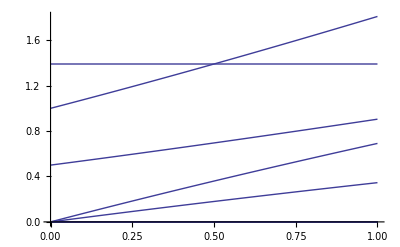

```mathematica
Show[Plot[1.3903882032022072,{i,0,1}],Table[Plot[λ/.charploy0sol[[i]]/.r->1/2/.R->1/2,{k,0,1}],{i,1,Length[charploy0sol]}],PlotRange->All]
```

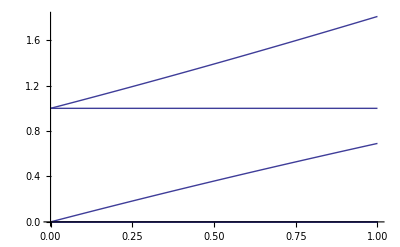

```mathematica
Show[Table[Plot[λ/.charploy0sol[[i]]/.r->1/2/.R->0,{k,0,1}],{i,1,Length[charploy0sol]}],PlotRange->All]
```

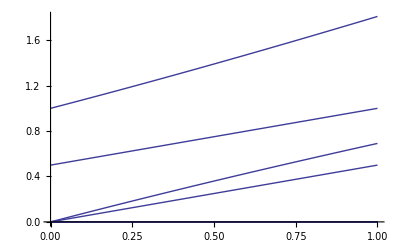

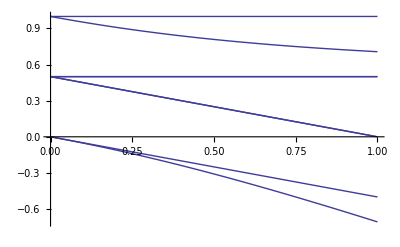

```mathematica
Show[Table[Plot[λ/.charploy0sol[[i]]/.r->0/.R->1/2,{k,0,1}],{i,1,Length[charploy0sol]}],PlotRange->All]
```

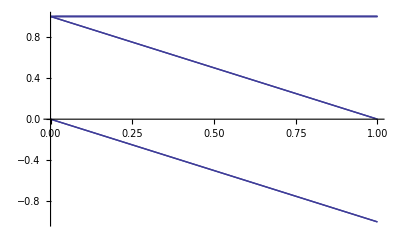

-Graphics-

```mathematica
Show[Table[Plot[λ/.charploy0sol[[i]]/.r->0/.R->0,{k,0,1}],{i,1,Length[charploy0sol]}],PlotRange->All]
```

On this order the leading eigenvalue is λ=1.

On the first order the eiganvalue is

```mathematica
Normal[Series[charpolyExt/.weaksel/.λ->1+δλ*ϵ/.frequenciessub/.sol0/.pXf0->pA,{ϵ,0,1}]]//Factor;
Solve[%==0,δλ]
```

{{δλ→0}}

And on the 2nd order (this takes a few minutes)

```mathematica
Normal[Series[charpolyExt/.weaksel/.λ->1+δλ2*ϵ^2/.frequenciessub/.sol0/.pXf0->pA/.pXm1->dpAXmXf+pXf1/.pYm1->dpAYmXf+pXf1,{ϵ,0,2}]]//Factor;
Solve[%==0,δλ2];
Collect[δλ2/.%,{dpAXmXf,dpAYmXf},Simplify]
```

{dpAXmXf ((1-h[2]+pA (-1+2 h[2])) sDip[2]+sHap[1])-1/R(-1+pA) pA ((1-h[2]+pA (-1+2 h[2])) sDip[2]+sHap[1]) ((1-h[2]+pA (-1+2 h[2])) sDip[2]+sHap[1]-R sHap[1]+R sHap[2])}

```mathematica
Normal[Series[charpolyExt/.weaksel/.λ->1+δλ2*ϵ^2/.frequenciessub/.sol0/.pXf0->pA/.pXm1->dpAXmXf+pXf1/.pYm1->dpAYmXf+pXf1,{ϵ,0,2}]]//Factor;
Solve[%==0,δλ2];
lambda2diffs=Collect[δλ2/.%,{dpAXmXf,dpAYmXf},Simplify]
```

{dpAXmXf ((1-h[2]+pA (-1+2 h[2])) sDip[2]+sHap[1])-1/R(-1+pA) pA ((1-h[2]+pA (-1+2 h[2])) sDip[2]+sHap[1]) ((1-h[2]+pA (-1+2 h[2])) sDip[2]+sHap[1]-R sHap[1]+R sHap[2])}

THIS DOES NOT DEPEND ON r OR k!!!!!

Then we can put in all the differences

```mathematica
tester=Collect[Normal[Series[lambda2diffs/.weaksel/.realsol[[3]],{ϵ,0,2}]],{dpAXmXf,dpAYmXf},Simplify]
```

{(sDip[2] ((-1+h[1]) sDip[1]+(-1+h[2]) sDip[2]-sHap[1]-sHap[2]) (h[1] sDip[1]+h[2] sDip[2]+sHap[1]+sHap[2]) (h[1] sDip[1]+sHap[1]+sHap[2]-h[2] (sDip[1]+2 (sHap[1]+sHap[2]))) (-(R (sDip[1]-sDip[2])-sDip[2]) (sHap[1]+sHap[2])+h[1] sDip[1] ((1+2 R) sDip[2]+2 R (sHap[1]+sHap[2]))-h[2] sDip[2] ((1+2 R) sDip[1]+2 (1+R) (sHap[1]+sHap[2]))))/(R (sDip[1]-2 h[1] sDip[1]+sDip[2]-2 h[2] sDip[2])^4)}

Under some situations this reduces to (dividing by genetic variance at the viability locus):

a) no competition among eggs (and equal dominance coefficients)

```mathematica
Collect[tester/(pA(1-pA))/.realsol[[3]]/.h[sex_]->h/.sHap[2]->0//Simplify,{sHap[male]},FullSimplify]
```

{(sDip[2] (sDip[2]+R (-sDip[1]+sDip[2])) sHap[1]^2)/(R (sDip[1]+sDip[2])^2)}

b) no competition among sperm (and equal dominance coefficients)

```mathematica
Collect[tester/(pA(1-pA))/.realsol[[3]]/.h[sex_]->h/.sHap[1]->0//Simplify,{sHap[male]},FullSimplify]
```

{(sDip[2] (-2 R sDip[1]+sDip[2]) sHap[2]^2)/(R (sDip[1]+sDip[2])^2)}

d) equal dominance coefficients only

```mathematica
Collect[tester/(pA(1-pA))/.realsol[[3]]/.h[sex_]->h//Simplify,{sHap[2],sHap[1]},Simplify]
```

{(sDip[1] (sDip[1]-2 R sDip[2]) sHap[1]^2)/(R (sDip[1]+sDip[2])^2)+(2 (-sDip[1] sDip[2]+R (sDip[1]^2+sDip[2]^2)) sHap[1] sHap[2])/(R (sDip[1]+sDip[2])^2)+(sDip[2] (-2 R sDip[1]+sDip[2]) sHap[2]^2)/(R (sDip[1]+sDip[2])^2)}

Offspring case copied for comparison:

```mathematica
testerOff=-(((-1+h[female]) sDip[female]+(-1+h[male]) sDip[male]-sHap[female]-sHap[male]) (h[female] sDip[female]+h[male] sDip[male]+sHap[female]+sHap[male]) (sDip[male] sHap[female]-h[male] sDip[male] (sDip[female]+2 sHap[female])-sDip[female] sHap[male]+h[female] sDip[female] (sDip[male]+2 sHap[male])) (-k^2 R sDip[female] sHap[female]+2 k^2 r R sDip[female] sHap[female]-2 r sDip[male] sHap[female]+8 k r sDip[male] sHap[female]-8 k^2 r sDip[male] sHap[female]+2 R sDip[male] sHap[female]-4 k R sDip[male] sHap[female]+3 k^2 R sDip[male] sHap[female]-8 k r R sDip[male] sHap[female]+10 k^2 r R sDip[male] sHap[female]+2 r sDip[female] sHap[male]-8 k r sDip[female] sHap[male]+8 k^2 r sDip[female] sHap[male]-2 R sDip[female] sHap[male]+4 k R sDip[female] sHap[male]-3 k^2 R sDip[female] sHap[male]+8 k r R sDip[female] sHap[male]-10 k^2 r R sDip[female] sHap[male]+k^2 R sDip[male] sHap[male]-2 k^2 r R sDip[male] sHap[male]-2 h[male] sDip[male] ((r (-1-4 k (-1+R)+4 k^2 (-1+R))+(1-2 k+2 k^2) R) sDip[female]+((2-4 k+3 k^2) R+2 r (-1-4 k (-1+R)+k^2 (-4+5 R))) sHap[female]+k^2 (1-2 r) R sHap[male])+2 h[female] sDip[female] ((r (-1-4 k (-1+R)+4 k^2 (-1+R))+(1-2 k+2 k^2) R) sDip[male]+k^2 (1-2 r) R sHap[female]+((2-4 k+3 k^2) R+2 r (-1-4 k (-1+R)+k^2 (-4+5 R))) sHap[male])))/(2 r R (sDip[female]-2 h[female] sDip[female]+sDip[male]-2 h[male] sDip[male])^4);
```

```mathematica
realsolOff={{dpAXmXf->0,dpAYmXf->0,pA->0},{dpAXmXf->0,dpAYmXf->0,pA->1},{dpAXmXf->-((-sDip[female]+h[female] sDip[female]-sDip[male]+h[male] sDip[male]-sHap[female]-sHap[male]) (h[female] sDip[female]+h[male] sDip[male]+sHap[female]+sHap[male]) (2 h[female] sDip[female] sDip[male]-2 h[male] sDip[female] sDip[male]-sDip[female] sHap[female]+2 h[female] sDip[female] sHap[female]+sDip[male] sHap[female]-2 h[male] sDip[male] sHap[female]-sDip[female] sHap[male]+2 h[female] sDip[female] sHap[male]+sDip[male] sHap[male]-2 h[male] sDip[male] sHap[male]))/(-sDip[female]+2 h[female] sDip[female]-sDip[male]+2 h[male] sDip[male])^3,dpAYmXf->-((-sDip[female]+h[female] sDip[female]-sDip[male]+h[male] sDip[male]-sHap[female]-sHap[male]) (h[female] sDip[female]+h[male] sDip[male]+sHap[female]+sHap[male]) (h[female] sDip[female] sDip[male]-h[male] sDip[female] sDip[male]-r sDip[female] sHap[female]+2 r h[female] sDip[female] sHap[female]+sDip[male] sHap[female]-r sDip[male] sHap[female]-2 h[male] sDip[male] sHap[female]+2 r h[male] sDip[male] sHap[female]-sDip[female] sHap[male]+r sDip[female] sHap[male]+2 h[female] sDip[female] sHap[male]-2 r h[female] sDip[female] sHap[male]+r sDip[male] sHap[male]-2 r h[male] sDip[male] sHap[male]))/(r (-sDip[female]+2 h[female] sDip[female]-sDip[male]+2 h[male] sDip[male])^3),pA->(-sDip[female]+h[female] sDip[female]-sDip[male]+h[male] sDip[male]-sHap[female]-sHap[male])/(-sDip[female]+2 h[female] sDip[female]-sDip[male]+2 h[male] sDip[male])}};
```

a) dominant feminizer with no competition among eggs and free recombination with VS locus (and equal dominance coefficients)

```mathematica
Collect[testerOff/(pA(1-pA))/.realsolOff[[3]]/.h[sex_]->h/.sHap[female]->0//Simplify,{sHap[male]},FullSimplify]
```

(sDip[female] ((2 (1-2 k)^2 r+(-2+k (4+8 r-k (3+10 r))) R) sDip[female]+k^2 (1-2 r) R sDip[male]) sHap[male]^2)/(2 r R (sDip[female]+sDip[male])^2)

b) dominant masculinizer with no competition among eggs  (and equal dominance coefficients)

```mathematica
Collect[tester/(pA(1-pA))/(1-2r)*r/.realsol[[3]]/.h[sex_]->h/.k->0/.sHap[female]->0//Simplify,{sHap[male]},FullSimplify]
```

{((-r+R) sDip[female]^2 sHap[male]^2)/((-1+2 r) R (sDip[female]+sDip[male])^2)}

c) ESD with no competition among eggs (and equal dominance coefficients)

```mathematica
Collect[tester/(pA(1-pA))/(1-2r)*r/.realsol[[3]]/.h[sex_]->h/.k->1/2/.sHap[female]->0//Simplify,{sHap[female],sHap[male]},Simplify]
```

{(sDip[female] (-3 sDip[female]+sDip[male]) sHap[male]^2)/(8 (sDip[female]+sDip[male])^2)}

#### Mike

There is a weird looking 3 in (c) above. I think this comes from averaging gains in males versus females:

```mathematica
selFeminizer=(sDip[female] (-sDip[female]+sDip[male]) sHap[male]^2)/(2 (sDip[female]+sDip[male])^2);
selMasculinizer=((-r+R) sDip[female]^2 sHap[male]^2)/((-1+2 r) R (sDip[female]+sDip[male])^2)/.R->1/2;
selESDsimp=(sDip[female] (-3 sDip[female]+sDip[male]) sHap[male]^2)/(8 (sDip[female]+sDip[male])^2);
```

```mathematica
Factor[1/2*(selFeminizer+selMasculinizer)/2]
%-selESDsimp//Factor
```

-(sDip[female] (3 sDip[female]-sDip[male]) sHap[male]^2)/(8 (sDip[female]+sDip[male])^2)

0

Interestingly, this does not involve R (but can be written as the average of the invasion of unlinked masculinizer and feminizer.

re-enter tester and realson because running all of the above is very slow:

```mathematica
tester={-(((-1+h[female]) sDip[female]+(-1+h[male]) sDip[male]-sHap[female]-sHap[male]) (h[female] sDip[female]+h[male] sDip[male]+sHap[female]+sHap[male]) (sDip[male] sHap[female]-h[male] sDip[male] (sDip[female]+2 sHap[female])-sDip[female] sHap[male]+h[female] sDip[female] (sDip[male]+2 sHap[male])) (-k^2 R sDip[female] sHap[female]+2 k^2 r R sDip[female] sHap[female]-2 r sDip[male] sHap[female]+8 k r sDip[male] sHap[female]-8 k^2 r sDip[male] sHap[female]+2 R sDip[male] sHap[female]-4 k R sDip[male] sHap[female]+3 k^2 R sDip[male] sHap[female]-8 k r R sDip[male] sHap[female]+10 k^2 r R sDip[male] sHap[female]+2 r sDip[female] sHap[male]-8 k r sDip[female] sHap[male]+8 k^2 r sDip[female] sHap[male]-2 R sDip[female] sHap[male]+4 k R sDip[female] sHap[male]-3 k^2 R sDip[female] sHap[male]+8 k r R sDip[female] sHap[male]-10 k^2 r R sDip[female] sHap[male]+k^2 R sDip[male] sHap[male]-2 k^2 r R sDip[male] sHap[male]-2 h[male] sDip[male] ((r (-1-4 k (-1+R)+4 k^2 (-1+R))+(1-2 k+2 k^2) R) sDip[female]+((2-4 k+3 k^2) R+2 r (-1-4 k (-1+R)+k^2 (-4+5 R))) sHap[female]+k^2 (1-2 r) R sHap[male])+2 h[female] sDip[female] ((r (-1-4 k (-1+R)+4 k^2 (-1+R))+(1-2 k+2 k^2) R) sDip[male]+k^2 (1-2 r) R sHap[female]+((2-4 k+3 k^2) R+2 r (-1-4 k (-1+R)+k^2 (-4+5 R))) sHap[male])))/(2 r R (sDip[female]-2 h[female] sDip[female]+sDip[male]-2 h[male] sDip[male])^4)};
realsol={{dpAXmXf->0,dpAYmXf->0,pA->0},{dpAXmXf->0,dpAYmXf->0,pA->1},{dpAXmXf->-((-sDip[female]+h[female] sDip[female]-sDip[male]+h[male] sDip[male]-sHap[female]-sHap[male]) (h[female] sDip[female]+h[male] sDip[male]+sHap[female]+sHap[male]) (2 h[female] sDip[female] sDip[male]-2 h[male] sDip[female] sDip[male]-sDip[female] sHap[female]+2 h[female] sDip[female] sHap[female]+sDip[male] sHap[female]-2 h[male] sDip[male] sHap[female]-sDip[female] sHap[male]+2 h[female] sDip[female] sHap[male]+sDip[male] sHap[male]-2 h[male] sDip[male] sHap[male]))/(-sDip[female]+2 h[female] sDip[female]-sDip[male]+2 h[male] sDip[male])^3,dpAYmXf->-((-sDip[female]+h[female] sDip[female]-sDip[male]+h[male] sDip[male]-sHap[female]-sHap[male]) (h[female] sDip[female]+h[male] sDip[male]+sHap[female]+sHap[male]) (h[female] sDip[female] sDip[male]-h[male] sDip[female] sDip[male]-r sDip[female] sHap[female]+2 r h[female] sDip[female] sHap[female]+sDip[male] sHap[female]-r sDip[male] sHap[female]-2 h[male] sDip[male] sHap[female]+2 r h[male] sDip[male] sHap[female]-sDip[female] sHap[male]+r sDip[female] sHap[male]+2 h[female] sDip[female] sHap[male]-2 r h[female] sDip[female] sHap[male]+r sDip[male] sHap[male]-2 r h[male] sDip[male] sHap[male]))/(r (-sDip[female]+2 h[female] sDip[female]-sDip[male]+2 h[male] sDip[male])^3),pA->(-sDip[female]+h[female] sDip[female]-sDip[male]+h[male] sDip[male]-sHap[female]-sHap[male])/(-sDip[female]+2 h[female] sDip[female]-sDip[male]+2 h[male] sDip[male])}};
```

R is involved if k =/= 1/2.

```mathematica
Collect[tester/(pA(1-pA))/(1-2r)*r/.realsol[[3]]/.h[sex_]->h/.sHap[female]->0//Simplify,{sHap[female],sHap[male]},Simplify]
```

{(sDip[female] (((2-4 k+3 k^2) R+2 r (-1-4 k (-1+R)+k^2 (-4+5 R))) sDip[female]+k^2 (-1+2 r) R sDip[male]) sHap[male]^2)/(2 (-1+2 r) R (sDip[female]+sDip[male])^2)}

## Numerical Check

#### First find the equilibrium frequency of residents (equil and sieve functions)

```mathematica
fHapNext[1,1,1,1,1]-
```

```mathematica
{XAfprime-XAf,Xafprime-Xaf,XAmprime-XAm,Xamprime-Xam,YAmprime-YAm,Yamprime-Yam}/.subequil//Simplify
```

{(-2 Faa (-1+pXf) pXf (-1+pXm) wa-2 FAA (-1+pXf) pXf pXm wA+FAa (-1+2 pXf) (-pXm wA+pXf ((-1+pXm) wa+pXm wA)))/(2 (Faa (-1+pXf) (-1+pXm) wa+FAA pXf pXm wA+FAa (pXm wA+pXf (wa-pXm wa-pXm wA)))),(2 Faa (-1+pXf) pXf (-1+pXm) wa+2 FAA (-1+pXf) pXf pXm wA-FAa (-1+2 pXf) (-pXm wA+pXf ((-1+pXm) wa+pXm wA)))/(2 (Faa (-1+pXf) (-1+pXm) wa+FAA pXf pXm wA+FAa (pXm wA+pXf (wa-pXm wa-pXm wA)))),((Maa (-1+pXf) pXm (-1+pYm) wa+MAA pXf (-1+pXm) pYm wA+MAa (pYm (pXm-r) wA+pXf (-(-1+pYm) (-1+pXm+r) wa+pYm (-pXm+r) wA))) (-1+α))/(Maa (-1+pXf) (-1+pYm) wa+MAA pXf pYm wA+MAa (pYm wA+pXf (wa-pYm wa-pYm wA))),((Maa pXm (-1+pXf+pYm-pXf pYm) wa-MAA pXf (-1+pXm) pYm wA+MAa (pYm (-pXm+r) wA+pXf ((-1+pYm) (-1+pXm+r) wa+pYm (pXm-r) wA))) (-1+α))/(Maa (-1+pXf) (-1+pYm) wa+MAA pXf pYm wA+MAa (pYm wA+pXf (wa-pYm wa-pYm wA))),-((Maa (-1+pXf) (-1+pYm) pYm wa+MAA pXf (-1+pYm) pYm wA+MAa (pYm (-1+pYm+r) wA-pXf (r wa+pYm^2 (wa+wA)-pYm (wa+r wa+wA-r wA)))) α)/(Maa (-1+pXf) (-1+pYm) wa+MAA pXf pYm wA+MAa (pYm wA+pXf (wa-pYm wa-pYm wA))),((Maa (-1+pXf) (-1+pYm) pYm wa+MAA pXf (-1+pYm) pYm wA+MAa (pYm (-1+pYm+r) wA-pXf (r wa+pYm^2 (wa+wA)-pYm (wa+r wa+wA-r wA)))) α)/(Maa (-1+pXf) (-1+pYm) wa+MAA pXf pYm wA+MAa (pYm wA+pXf (wa-pYm wa-pYm wA)))}

```mathematica
Clear[equil]
equil[FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,α_]:={pXf,pXm,pYm}/.NSolve[{(-2 Faa (-1+pXf) pXf (-1+pXm) wa-2 FAA (-1+pXf) pXf pXm wA+FAa (-1+2 pXf) (-pXm wA+pXf ((-1+pXm) wa+pXm wA)))/(2 (Faa (-1+pXf) (-1+pXm) wa+FAA pXf pXm wA+FAa (pXm wA+pXf (wa-pXm wa-pXm wA)))),(2 Faa (-1+pXf) pXf (-1+pXm) wa+2 FAA (-1+pXf) pXf pXm wA-FAa (-1+2 pXf) (-pXm wA+pXf ((-1+pXm) wa+pXm wA)))/(2 (Faa (-1+pXf) (-1+pXm) wa+FAA pXf pXm wA+FAa (pXm wA+pXf (wa-pXm wa-pXm wA)))),((Maa (-1+pXf) pXm (-1+pYm) wa+MAA pXf (-1+pXm) pYm wA+MAa (pYm (pXm-r) wA+pXf (-(-1+pYm) (-1+pXm+r) wa+pYm (-pXm+r) wA))) (-1+α))/(Maa (-1+pXf) (-1+pYm) wa+MAA pXf pYm wA+MAa (pYm wA+pXf (wa-pYm wa-pYm wA))),((Maa pXm (-1+pXf+pYm-pXf pYm) wa-MAA pXf (-1+pXm) pYm wA+MAa (pYm (-pXm+r) wA+pXf ((-1+pYm) (-1+pXm+r) wa+pYm (pXm-r) wA))) (-1+α))/(Maa (-1+pXf) (-1+pYm) wa+MAA pXf pYm wA+MAa (pYm wA+pXf (wa-pYm wa-pYm wA))),-((Maa (-1+pXf) (-1+pYm) pYm wa+MAA pXf (-1+pYm) pYm wA+MAa (pYm (-1+pYm+r) wA-pXf (r wa+pYm^2 (wa+wA)-pYm (wa+r wa+wA-r wA)))) α)/(Maa (-1+pXf) (-1+pYm) wa+MAA pXf pYm wA+MAa (pYm wA+pXf (wa-pYm wa-pYm wA))),((Maa (-1+pXf) (-1+pYm) pYm wa+MAA pXf (-1+pYm) pYm wA+MAa (pYm (-1+pYm+r) wA-pXf (r wa+pYm^2 (wa+wA)-pYm (wa+r wa+wA-r wA)))) α)/(Maa (-1+pXf) (-1+pYm) wa+MAA pXf pYm wA+MAa (pYm wA+pXf (wa-pYm wa-pYm wA)))}=={0,0,0,0,0,0},{pXf,pXm,pYm}]
```

this now sieves and excludes anything that is not 0 or 1.

```mathematica
cutoff=10^(-10);

Clear[sieve]
sieve[FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wA_,wa_,r_,α_]:=Block[{},For[i=1;write={},i≤(max=Length[eq=(equil[FAA,FAa,Faa,MAA,MAa,Maa,wA,wa,r,α])]),i++,If[Length[test=Cases[eq[[i]],x_/;((cutoff≤Re[x]≤1-cutoff)&&Abs[Im[x]]<cutoff)]]==3,write=Append[write,eq[[i]]]]];
Sort[write]]
```

```mathematica
equil[1,1.1,1.15,1,1.1,1.15,1,0.9,1/2,1/2]
```

{{1.,1.,1.},{0.181818,0.181818,0.181818},{0.,0.,0.}}

```mathematica
Flatten[sieve[1,1.1,1.15,1,1.1,1.15,1,0.9,1/2,1/2]]
```

{0.181818,0.181818,0.181818}

# playing with indices

## Recursions

We consider three loci: 1) a diallelic genetic sex-determining (GSD) locus, 2) a diallelic locus under viability selection (VS), and 3) a diallelic environmentally sex-determining (ESD) locus. We assume that initially, the ESD locus is fixed for a null allele E, that does nothing and thus sex is determined by the GSD locus. We will then look at the invasion of a rare mutant allele e at the ESD locus, which is dominant over E and the GSD locus. We will assume that the sex of diploids is determined by the maternal ESD genotype. A proportion k of offspring from mothers with Ee or ee genotypes will be female and a proportion 1-k will be male (i.e., e changes the “behaviour” of the mother that determines sex of her offspring, eg. epigenetic mark or burying eggs in the sand).

We will call the alleles at the GSD locus X and Y with Y masculinizing and dominant over X. We can easily convert to a ZW system by making Z=X and W=Y and male=female and female=male.

Haploid selection: starting with haploid genotype frequencies fHap in each sex, the frequencies after selection fHapSel are

```mathematica
(*mean fitness of haploids from a particular sex*)
Table[Subscript[wbarHap, sex]=
Sum[Subscript[wHap, x,y,z,sex,homhet] Subscript[fHap, x,y,z,sex,homhet],{x,1,2},{y,1,2},{z,1,2},{homhet,1,2}],{sex,1,2}];
(*frequency of haploids with genotype xyz from a parent of a particular sex who was homozygous or heterozygous at the ESD locus*)
Table[Subscript[fHapSel, x,y,z,sex,homhet]=
Subscript[wHap, x,y,z,sex,homhet] Subscript[fHap, x,y,z,sex,homhet]/Subscript[wbarHap, sex],{x,1,2},{y,1,2},{z,1,2},{sex,1,2},{homhet,1,2}];
(*check that the sum of all frequencies within a given sex sums to one*)
(*Sum[Subscript[fHapSel, x,y,z,sex,homhet],{x,1,2},{y,1,2},{z,1,2},{sex,1,1},{homhet,1,2}]//Factor*)
```

where x is the allele at the GSD locus, y is the allele at the VS locus, z is the allele at the ESD locus, and sex is male or female. homhet indicates whether the parental genotype at the ESD locus was homozygous or heterozygous. Notice that the fitness of a haploid genotype wHap depends on the sex of its parent and gametes of the opposite sex do not compete with one another (wbarHap is mean fitness of gametes in each sex).

Gametic union: haploid genotypes pair at random giving diploid genotype frequencies fDip

```mathematica
(*frequency of diploids with genotype xM,yM,zM,xP,yP,zP (M for maternal, P for paternal) from parents who were homozygous or heterozygous at the ESD locus*)
Table[Subscript[fDip, xM,yM,zM,xP,yP,zP,homhetM,homhetP]=
Subscript[fHapSel, xM,yM,zM,2,homhetM] Subscript[fHapSel, xP,yP,zP,1,homhetP],{xM,1,2},{yM,1,2},{zM,1,2},{xP,1,2},{yP,1,2},{zP,1,2},{homhetM,1,2},{homhetP,1,2}];
(*check that the sum of all frequencies sums to one*)
(*Sum[Subscript[fDip, xM,yM,zM,xP,yP,zP,homhetM,homhetP],{xM,1,2},{yM,1,2},{zM,1,2},{xP,1,2},{yP,1,2},{zP,1,2},{homhetM,1,2},{homhetP,1,2}]//Factor*)
```

Sex determination:

```mathematica
(*frequency of diploids with genotype xM,yM,zM,xP,yP,zP and of a particular sex*)
Table[Subscript[fDipSex, xM,yM,zM,xP,yP,zP,sex]=
Sum[Subscript[fDip, xM,yM,zM,xP,yP,zP,homhetM,homhetP] Subscript[psex, xM,yM,zM,xP,yP,zP,homhetM,homhetP,sex],{homhetP,1,2},{homhetM,1,2}],{xM,1,2},{yM,1,2},{zM,1,2},{xP,1,2},{yP,1,2},{zP,1,2},{sex,1,2}];
```

where an individual must be male or female

```mathematica
sumsex=Table[Subscript[psex, xM,yM,zM,xP,yP,zP,homhetM,homhetP,2]->1-Subscript[psex, xM,yM,zM,xP,yP,zP,homhetM,homhetP,1],{homhetP,1,2},{homhetM,1,2},{xM,1,2},{yM,1,2},{zM,1,2},{xP,1,2},{yP,1,2},{zP,1,2}];
```

Here we will be concerned with environmental sex determination invading male heterogamy:

```mathematica
ESDXY={
Table[Subscript[psex, xM,yM,1,2,yP,zP,1,homhetP,1]->1,{xM,1,2},{yM,1,2},{yP,1,2},{zP,1,2},{homhetP,1,2}],
Table[Subscript[psex, xM,yM,1,1,yP,zP,1,homhetP,1]->0,{xM,1,2},{yM,1,2},{yP,1,2},{zP,1,2},{homhetP,1,2}],
Table[Subscript[fHap, 2,y,1,2,1]->0,{y,1,2}],
Table[Subscript[psex, xM,yM,2,xP,yP,zP,homhetM,homhetP,1]->1-k,{xM,1,2},{yM,1,2},{xP,1,2},{yP,1,2},{zP,1,2},{homhetM,1,2},{homhetP,1,2}],
Table[Subscript[psex, xM,yM,1,xP,yP,zP,2,homhetP,1]->1-k,{xM,1,2},{yM,1,2},{xP,1,2},{yP,1,2},{zP,1,2},{homhetM,1,2},{homhetP,1,2}]};
```

Check that frequencies after sex determination sum to one (takes a long time, I haven’t let it finish, but we normalize in the next step anyways)

```mathematica
(*Sum[Subscript[fDipSex, xM,yM,zM,xP,yP,zP,sex],{xM,1,2},{yM,1,2},{zM,1,2},{xP,1,2},{yP,1,2},{zP,1,2},{sex,1,2}]/.sumsex/.ESDXY//Factor*)
```

Diploid selection: if all individuals compete with one another (i.e., for resources) then the frequencies of diploid genotypes after selection fDipSel are

```mathematica
(*wbarDip=Sum[wDip[xM,yM,zM,xP,yP,zP,sex]fDipSex[xM,yM,zM,xP,yP,zP,sex],{xM,1,2},{yM,1,2},{zM,1,2},{xP,1,2},{yP,1,2},{zP,1,2},{sex,1,2}];
fDipSel[xM_,yM_,zM_,xP_,yP_,zP_,sex_]:=fDipSel[xM,yM,zM,xP,yP,zP,sex]=
wDip[xM,yM,zM,xP,yP,zP,sex]fDipSex[xM,yM,zM,xP,yP,zP,sex]/wbarDip;*)
(*Sum[fDipSel[xM,yM,zM,xP,yP,zP,sex],{xM,1,2},{yM,1,2},{zM,1,2},{xP,1,2},{yP,1,2},{zP,1,2},{sex,{male,female}}]/.sumsex/.ESDXY//Factor*)
```

Alternatively, males could compete with males and female with females (ie. competition over mates). Then

```mathematica
(*mean diploid fitness of each sex*)
Table[Subscript[wbarDip, sex]=
Sum[Subscript[wDip, xM,yM,zM,xP,yP,zP,sex] Subscript[fDipSex, xM,yM,zM,xP,yP,zP,sex],{xM,1,2},{yM,1,2},{zM,1,2},{xP,1,2},{yP,1,2},{zP,1,2}],{sex,1,2}];
(*frequency of diploid types after selection*)
Table[Subscript[fDipSel, xM,yM,zM,xP,yP,zP,sex]=Subscript[wDip, xM,yM,zM,xP,yP,zP,sex] Subscript[fDipSex, xM,yM,zM,xP,yP,zP,sex]/Subscript[wbarDip, sex],{xM,1,2},{yM,1,2},{zM,1,2},{xP,1,2},{yP,1,2},{zP,1,2},{sex,1,2}];
(*check that the frequencies of diploids with a sex sum to one*)
(*Sum[Subscript[fDipSel, xM,yM,zM,xP,yP,zP,sex],{xM,1,2},{yM,1,2},{zM,1,2},{xP,1,2},{yP,1,2},{zP,1,2},{sex,1,1}]//Factor*)
```

Meiosis: if pseg is the probability that a diploid genotype of a particular sex produces a gamete of a given haploid genoytpe, then the frequencies of haploid genotypes (from a parent of a particular sex whose ESD locus was homozygous or heterozygous) in the next generation are

```mathematica
Table[Subscript[fHapNext, x,y,z,sex,homhet]=Sum[Subscript[fDipSel, xM,yM,zM,xP,yP,zP,sex] Subscript[pseg, xM,yM,zM,xP,yP,zP,sex,x,y,z,homhet],{xM,1,2},{yM,1,2},{zM,1,2},{xP,1,2},{yP,1,2},{zP,1,2}],{x,1,2},{y,1,2},{z,1,2},{sex,1,2},{homhet,1,2}];
```

And the frequency from each sex is

```mathematica
(*totalNum={Sum[fHapNextTot[x1,y1,z1,1,homhet1],{x1,1,2},{y1,1,2},{z1,1,2},{homhet1,1,2}],Sum[fHapNextTot[x1,y1,z1,2,homhet1],{x1,1,2},{y1,1,2},{z1,1,2},{homhet1,1,2}]};
fHapNext[x_,y_,z_,sex_,homhet_]:=fHapNext[x,y,z,sex,homhet]=
fHapNextTot[x,y,z,sex,homhet]/totalNum[[sex]]*)
```

With recombination and no meiotic drive (and with linear arrangement x-y-z with recombination probability r between x and y and probability R between y and z) we have

```mathematica
pseg0={
(*triple homozygote*)
Subscript[pseg, x1_,y1_,z1_,x1_,y1_,z1_,sex_,x1_,y1_,z1_,hom]->1
}/.hom->1/.het->2;
pseg1={
(*single heterozygotes*)
Subscript[pseg, x1_,y1_,z1_,x2_,y1_,z1_,sex_,x1_,y1_,z1_,hom]->1/2,
Subscript[pseg, x1_,y1_,z1_,x2_,y1_,z1_,sex_,x2_,y1_,z1_,hom]->1/2,
Subscript[pseg, x1_,y1_,z1_,x1_,y2_,z1_,sex_,x1_,y1_,z1_,hom]->1/2,
Subscript[pseg, x1_,y1_,z1_,x1_,y2_,z1_,sex_,x1_,y2_,z1_,hom]->1/2,
Subscript[pseg, x1_,y1_,z1_,x1_,y1_,z2_,sex_,x1_,y1_,z1_,het]->1/2,
Subscript[pseg, x1_,y1_,z1_,x1_,y1_,z2_,sex_,x1_,y1_,z2_,het]->1/2
}/.hom->1/.het->2;
pseg2={
(*double heterozygotes*)
Subscript[pseg, x1_,y1_,z1_,x2_,y2_,z1_,sex_,x1_,y1_,z1_,hom]->(1-r)/2,
Subscript[pseg, x1_,y1_,z1_,x2_,y2_,z1_,sex_,x2_,y2_,z1_,hom]->(1-r)/2,
Subscript[pseg, x1_,y1_,z1_,x2_,y2_,z1_,sex_,x2_,y1_,z1_,hom]->r/2,
Subscript[pseg, x1_,y1_,z1_,x2_,y2_,z1_,sex_,x1_,y2_,z1_,hom]->r/2,
Subscript[pseg, x1_,y1_,z1_,x1_,y2_,z2_,sex_,x1_,y1_,z1_,het]->(1-R)/2,
Subscript[pseg, x1_,y1_,z1_,x1_,y2_,z2_,sex_,x1_,y2_,z2_,het]->(1-R)/2,
Subscript[pseg, x1_,y1_,z1_,x1_,y2_,z2_,sex_,x1_,y2_,z1_,het]->R/2,
Subscript[pseg, x1_,y1_,z1_,x1_,y2_,z2_,sex_,x1_,y1_,z2_,het]->R/2,
Subscript[pseg, x1_,y1_,z1_,x2_,y1_,z2_,sex_,x1_,y1_,z1_,het]->((1-r)(1-R)+r R)/2,
Subscript[pseg, x1_,y1_,z1_,x2_,y1_,z2_,sex_,x2_,y1_,z2_,het]->((1-r)(1-R)+r R)/2,
Subscript[pseg, x1_,y1_,z1_,x2_,y1_,z2_,sex_,x2_,y1_,z1_,het]->(r(1-R)+(1-r)R)/2,
Subscript[pseg, x1_,y1_,z1_,x2_,y1_,z2_,sex_,x1_,y1_,z2_,het]->(r(1-R)+(1-r)R)/2
}/.hom->1/.het->2;
pseg3={
(*triple heterozygote*)
Subscript[pseg, x1_,y1_,z1_,x2_,y2_,z2_,sex_,x1_,y1_,z1_,het]->(1-r)(1-R)/2,
Subscript[pseg, x1_,y1_,z1_,x2_,y2_,z2_,sex_,x2_,y2_,z2_,het]->(1-r)(1-R)/2,
Subscript[pseg, x1_,y1_,z1_,x2_,y2_,z2_,sex_,x2_,y1_,z1_,het]->r(1-R)/2,
Subscript[pseg, x1_,y1_,z1_,x2_,y2_,z2_,sex_,x1_,y2_,z2_,het]->r(1-R)/2,
Subscript[pseg, x1_,y1_,z1_,x2_,y2_,z2_,sex_,x1_,y2_,z1_,het]->r R/2,
Subscript[pseg, x1_,y1_,z1_,x2_,y2_,z2_,sex_,x2_,y1_,z2_,het]->r R/2,
Subscript[pseg, x1_,y1_,z1_,x2_,y2_,z2_,sex_,x1_,y1_,z2_,het]->(1-r)R/2,
Subscript[pseg, x1_,y1_,z1_,x2_,y2_,z2_,sex_,x2_,y2_,z1_,het]->(1-r)R/2
}/.hom->1/.het->2;
pseg4=Subscript[pseg, x1_,y1_,z1_,x2_,y2_,z2_,sex_,x_,y_,z_,homhet_]->0;
```

Check that the frequencies of gametes from each sex in the next generation sum to one (this takes a long time, I haven’t let it finish)

```mathematica
(*Sum[Subscript[fHapNext, x,y,z,sex,homhet]/.sumsex/.ESDXY/.pseg0/.pseg1/.pseg2/.pseg3/.pseg4,{x,1,2},{y,1,2},{z,1,2},{sex,1,2},{homhet,1,2}]//Factor*)
```

## Recursions (simplified)

We consider three loci: 1) a diallelic genetic sex-determining (GSD) locus, 2) a diallelic locus under viability selection (VS), and 3) a diallelic environmentally sex-determining (ESD) locus. We assume that initially, the ESD locus is fixed for a null allele E, that does nothing and thus sex is determined by the GSD locus. We will then look at the invasion of a rare mutant allele e at the ESD locus, which is dominant over E and the GSD locus. We will assume that the sex of diploids is determined by the maternal ESD genotype. A proportion k of offspring from mothers with Ee or ee genotypes will be female and a proportion 1-k will be male (i.e., e changes the “behaviour” of the mother that determines sex of her offspring, eg. epigenetic mark or burying eggs in the sand).

We will call the alleles at the GSD locus X and Y with Y masculinizing and dominant over X. We can easily convert to a ZW system by making Z=X and W=Y and male=female and female=male.

Haploid selection: starting with haploid genotype frequencies fHap in each sex, the frequencies after selection fHapSel are

```mathematica
(*mean fitness of haploids from a particular sex*)
Table[Subscript[wbarHap, sex]=
Sum[Subscript[wHap, y,sex] Subscript[fHap, x,y,z,sex,zzPar],{x,{X,Y}},{y,{A,a}},{z,{M,m}},{zzPar,{MM,Mm,mm}}],{sex,{Male,Fem}}];
(*frequency of haploids with genotype xyz from a parent of a particular sex who was homozygous or heterozygous at the ESD locus*)
Table[Subscript[fHapSel, x,y,z,sex,zzPar]=
Subscript[wHap, y,sex] Subscript[fHap, x,y,z,sex,zzPar]/Subscript[wbarHap, sex],{x,{X,Y}},{y,{A,a}},{z,{M,m}},{sex,{Male,Fem}},{zzPar,{MM,Mm,mm}}];
(*check that the sum of all frequencies within a given sex sums to one*)
Table[Sum[Subscript[fHapSel, x,y,z,sex,zzPar],{x,{X,Y}},{y,{A,a}},{z,{M,m}},{zzPar,{MM,Mm,mm}}]//Factor,{sex,{Male,Fem}}]
```

{1,1}

where x is the allele at the GSD locus, y is the allele at the VS locus, z is the allele at the ESD locus, and sex is male or female. homhet indicates whether the parental genotype at the ESD locus was homozygous or heterozygous. Notice that the fitness of a haploid genotype wHap depends on the sex of its parent and gametes of the opposite sex do not compete with one another (wbarHap is mean fitness of gametes in each sex).

Gametic union: haploid genotypes pair at random giving diploid genotype frequencies fDip

```mathematica
(*frequency of diploids with genotype xM,yM,zM,xP,yP,zP (M for maternal, P for paternal) from parents who were homozygous or heterozygous at the ESD locus*)
Table[Subscript[fDip, xM,yM,zM,xP,yP,zP,zzM]=
Sum[Subscript[fHapSel, xM,yM,zM,Fem,zzM] Subscript[fHapSel, xP,yP,zP,Male,zzP],{xM,{X,Y}},{yM,{A,a}},{zM,{M,m}},{xP,{X,Y}},{yP,{A,a}},{zP,{M,m}},{zzM,{MM,Mm,mm}}],{zzP,{MM,Mm,mm}}];
(*check that the sum of all frequencies sums to one*)
Sum[Subscript[fDip, xM,yM,zM,xP,yP,zP,zzM],{xM,{X,Y}},{yM,{A,a}},{zM,{M,m}},{xP,{X,Y}},{yP,{A,a}},{zP,{M,m}},{zzM,{MM,Mm,mm}}]//Factor
```

fDip_(X,a,m,X,a,m,mm)+fDip_(X,a,m,X,a,m,Mm)+fDip_(X,a,m,X,a,m,MM)+fDip_(X,a,m,X,a,M,mm)+fDip_(X,a,m,X,a,M,Mm)+fDip_(X,a,m,X,a,M,MM)+fDip_(X,a,m,X,A,m,mm)+fDip_(X,a,m,X,A,m,Mm)+fDip_(X,a,m,X,A,m,MM)+fDip_(X,a,m,X,A,M,mm)+fDip_(X,a,m,X,A,M,Mm)+fDip_(X,a,m,X,A,M,MM)+fDip_(X,a,m,Y,a,m,mm)+fDip_(X,a,m,Y,a,m,Mm)+fDip_(X,a,m,Y,a,m,MM)+fDip_(X,a,m,Y,a,M,mm)+fDip_(X,a,m,Y,a,M,Mm)+fDip_(X,a,m,Y,a,M,MM)+fDip_(X,a,m,Y,A,m,mm)+fDip_(X,a,m,Y,A,m,Mm)+fDip_(X,a,m,Y,A,m,MM)+fDip_(X,a,m,Y,A,M,mm)+fDip_(X,a,m,Y,A,M,Mm)+fDip_(X,a,m,Y,A,M,MM)+fDip_(X,a,M,X,a,m,mm)+fDip_(X,a,M,X,a,m,Mm)+fDip_(X,a,M,X,a,m,MM)+fDip_(X,a,M,X,a,M,mm)+fDip_(X,a,M,X,a,M,Mm)+fDip_(X,a,M,X,a,M,MM)+fDip_(X,a,M,X,A,m,mm)+fDip_(X,a,M,X,A,m,Mm)+fDip_(X,a,M,X,A,m,MM)+fDip_(X,a,M,X,A,M,mm)+fDip_(X,a,M,X,A,M,Mm)+fDip_(X,a,M,X,A,M,MM)+fDip_(X,a,M,Y,a,m,mm)+fDip_(X,a,M,Y,a,m,Mm)+fDip_(X,a,M,Y,a,m,MM)+fDip_(X,a,M,Y,a,M,mm)+fDip_(X,a,M,Y,a,M,Mm)+fDip_(X,a,M,Y,a,M,MM)+fDip_(X,a,M,Y,A,m,mm)+fDip_(X,a,M,Y,A,m,Mm)+fDip_(X,a,M,Y,A,m,MM)+fDip_(X,a,M,Y,A,M,mm)+fDip_(X,a,M,Y,A,M,Mm)+fDip_(X,a,M,Y,A,M,MM)+fDip_(X,A,m,X,a,m,mm)+fDip_(X,A,m,X,a,m,Mm)+fDip_(X,A,m,X,a,m,MM)+fDip_(X,A,m,X,a,M,mm)+fDip_(X,A,m,X,a,M,Mm)+fDip_(X,A,m,X,a,M,MM)+fDip_(X,A,m,X,A,m,mm)+fDip_(X,A,m,X,A,m,Mm)+fDip_(X,A,m,X,A,m,MM)+fDip_(X,A,m,X,A,M,mm)+fDip_(X,A,m,X,A,M,Mm)+fDip_(X,A,m,X,A,M,MM)+fDip_(X,A,m,Y,a,m,mm)+fDip_(X,A,m,Y,a,m,Mm)+fDip_(X,A,m,Y,a,m,MM)+fDip_(X,A,m,Y,a,M,mm)+fDip_(X,A,m,Y,a,M,Mm)+fDip_(X,A,m,Y,a,M,MM)+fDip_(X,A,m,Y,A,m,mm)+fDip_(X,A,m,Y,A,m,Mm)+fDip_(X,A,m,Y,A,m,MM)+fDip_(X,A,m,Y,A,M,mm)+fDip_(X,A,m,Y,A,M,Mm)+fDip_(X,A,m,Y,A,M,MM)+fDip_(X,A,M,X,a,m,mm)+fDip_(X,A,M,X,a,m,Mm)+fDip_(X,A,M,X,a,m,MM)+fDip_(X,A,M,X,a,M,mm)+fDip_(X,A,M,X,a,M,Mm)+fDip_(X,A,M,X,a,M,MM)+fDip_(X,A,M,X,A,m,mm)+fDip_(X,A,M,X,A,m,Mm)+fDip_(X,A,M,X,A,m,MM)+fDip_(X,A,M,X,A,M,mm)+fDip_(X,A,M,X,A,M,Mm)+fDip_(X,A,M,X,A,M,MM)+fDip_(X,A,M,Y,a,m,mm)+fDip_(X,A,M,Y,a,m,Mm)+fDip_(X,A,M,Y,a,m,MM)+fDip_(X,A,M,Y,a,M,mm)+fDip_(X,A,M,Y,a,M,Mm)+fDip_(X,A,M,Y,a,M,MM)+fDip_(X,A,M,Y,A,m,mm)+fDip_(X,A,M,Y,A,m,Mm)+fDip_(X,A,M,Y,A,m,MM)+fDip_(X,A,M,Y,A,M,mm)+fDip_(X,A,M,Y,A,M,Mm)+fDip_(X,A,M,Y,A,M,MM)+fDip_(Y,a,m,X,a,m,mm)+fDip_(Y,a,m,X,a,m,Mm)+fDip_(Y,a,m,X,a,m,MM)+fDip_(Y,a,m,X,a,M,mm)+fDip_(Y,a,m,X,a,M,Mm)+fDip_(Y,a,m,X,a,M,MM)+fDip_(Y,a,m,X,A,m,mm)+fDip_(Y,a,m,X,A,m,Mm)+fDip_(Y,a,m,X,A,m,MM)+fDip_(Y,a,m,X,A,M,mm)+fDip_(Y,a,m,X,A,M,Mm)+fDip_(Y,a,m,X,A,M,MM)+fDip_(Y,a,m,Y,a,m,mm)+fDip_(Y,a,m,Y,a,m,Mm)+fDip_(Y,a,m,Y,a,m,MM)+fDip_(Y,a,m,Y,a,M,mm)+fDip_(Y,a,m,Y,a,M,Mm)+fDip_(Y,a,m,Y,a,M,MM)+fDip_(Y,a,m,Y,A,m,mm)+fDip_(Y,a,m,Y,A,m,Mm)+fDip_(Y,a,m,Y,A,m,MM)+fDip_(Y,a,m,Y,A,M,mm)+fDip_(Y,a,m,Y,A,M,Mm)+fDip_(Y,a,m,Y,A,M,MM)+fDip_(Y,a,M,X,a,m,mm)+fDip_(Y,a,M,X,a,m,Mm)+fDip_(Y,a,M,X,a,m,MM)+fDip_(Y,a,M,X,a,M,mm)+fDip_(Y,a,M,X,a,M,Mm)+fDip_(Y,a,M,X,a,M,MM)+fDip_(Y,a,M,X,A,m,mm)+fDip_(Y,a,M,X,A,m,Mm)+fDip_(Y,a,M,X,A,m,MM)+fDip_(Y,a,M,X,A,M,mm)+fDip_(Y,a,M,X,A,M,Mm)+fDip_(Y,a,M,X,A,M,MM)+fDip_(Y,a,M,Y,a,m,mm)+fDip_(Y,a,M,Y,a,m,Mm)+fDip_(Y,a,M,Y,a,m,MM)+fDip_(Y,a,M,Y,a,M,mm)+fDip_(Y,a,M,Y,a,M,Mm)+fDip_(Y,a,M,Y,a,M,MM)+fDip_(Y,a,M,Y,A,m,mm)+fDip_(Y,a,M,Y,A,m,Mm)+fDip_(Y,a,M,Y,A,m,MM)+fDip_(Y,a,M,Y,A,M,mm)+fDip_(Y,a,M,Y,A,M,Mm)+fDip_(Y,a,M,Y,A,M,MM)+fDip_(Y,A,m,X,a,m,mm)+fDip_(Y,A,m,X,a,m,Mm)+fDip_(Y,A,m,X,a,m,MM)+fDip_(Y,A,m,X,a,M,mm)+fDip_(Y,A,m,X,a,M,Mm)+fDip_(Y,A,m,X,a,M,MM)+fDip_(Y,A,m,X,A,m,mm)+fDip_(Y,A,m,X,A,m,Mm)+fDip_(Y,A,m,X,A,m,MM)+fDip_(Y,A,m,X,A,M,mm)+fDip_(Y,A,m,X,A,M,Mm)+fDip_(Y,A,m,X,A,M,MM)+fDip_(Y,A,m,Y,a,m,mm)+fDip_(Y,A,m,Y,a,m,Mm)+fDip_(Y,A,m,Y,a,m,MM)+fDip_(Y,A,m,Y,a,M,mm)+fDip_(Y,A,m,Y,a,M,Mm)+fDip_(Y,A,m,Y,a,M,MM)+fDip_(Y,A,m,Y,A,m,mm)+fDip_(Y,A,m,Y,A,m,Mm)+fDip_(Y,A,m,Y,A,m,MM)+fDip_(Y,A,m,Y,A,M,mm)+fDip_(Y,A,m,Y,A,M,Mm)+fDip_(Y,A,m,Y,A,M,MM)+fDip_(Y,A,M,X,a,m,mm)+fDip_(Y,A,M,X,a,m,Mm)+fDip_(Y,A,M,X,a,m,MM)+fDip_(Y,A,M,X,a,M,mm)+fDip_(Y,A,M,X,a,M,Mm)+fDip_(Y,A,M,X,a,M,MM)+fDip_(Y,A,M,X,A,m,mm)+fDip_(Y,A,M,X,A,m,Mm)+fDip_(Y,A,M,X,A,m,MM)+fDip_(Y,A,M,X,A,M,mm)+fDip_(Y,A,M,X,A,M,Mm)+fDip_(Y,A,M,X,A,M,MM)+fDip_(Y,A,M,Y,a,m,mm)+fDip_(Y,A,M,Y,a,m,Mm)+fDip_(Y,A,M,Y,a,m,MM)+fDip_(Y,A,M,Y,a,M,mm)+fDip_(Y,A,M,Y,a,M,Mm)+fDip_(Y,A,M,Y,a,M,MM)+fDip_(Y,A,M,Y,A,m,mm)+fDip_(Y,A,M,Y,A,m,Mm)+fDip_(Y,A,M,Y,A,m,MM)+fDip_(Y,A,M,Y,A,M,mm)+fDip_(Y,A,M,Y,A,M,Mm)+fDip_(Y,A,M,Y,A,M,MM)

Sex determination:

```mathematica
(*frequency of diploids with genotype xM,yM,zM,xP,yP,zP and of a particular sex*)
Table[Subscript[fDipSex, xM,yM,zM,xP,yP,zP,sex]=
Sum[Subscript[fDip, xM,yM,zM,xP,yP,zP,homhetM,homhetP] Subscript[psex, zM,xP,homhetM,sex],{homhetP,1,2},{homhetM,1,2}],{xM,1,2},{yM,1,2},{zM,1,2},{xP,1,2},{yP,1,2},{zP,1,2},{sex,1,2}];
```

where an individual must be male or female

```mathematica
sumsex=Table[Subscript[psex, zM,xP,homhetM,2]->1-Subscript[psex, zM,xP,homhetM,1],{zM,1,2},{xP,1,2},{homhetM,1,2}];
```

Here we will be concerned with environmental sex determination invading male heterogamy:

```mathematica
ESDXY={
Subscript[psex, 1,2,1,1]->1,(*always male if mother wildtype at ESD and get Y from father*)
Subscript[psex, 1,1,1,1]->0,(*always female if mother wildtype at ESD and get X from father*)
Table[Subscript[fHap, 2,y,1,2,1]->0,{y,1,2}],(*no Y chromosome from the mother if she was homozygous wildtype at ESD*)
Table[Subscript[psex, 2,xP,homhetM,1]->1-k,{xP,1,2},{homhetM,1,2}],(*female with probability k if mother had mutation at the ESD*)
Table[Subscript[psex, 1,xP,2,1]->1-k,{xP,1,2},{homhetM,1,2}](*female with probability k if mother had mutation at the ESD*)
}//Flatten;
```

Check that frequencies after sex determination sum to one (takes a long time, I haven’t let it finish, but we normalize in the next step anyways)

```mathematica
(*Sum[Subscript[fDipSex, xM,yM,zM,xP,yP,zP,sex],{xM,1,2},{yM,1,2},{zM,1,2},{xP,1,2},{yP,1,2},{zP,1,2},{sex,1,2}]/.sumsex/.ESDXY//Factor*)
```

Diploid selection: if all individuals compete with one another (i.e., for resources) then the frequencies of diploid genotypes after selection fDipSel are

```mathematica
(*wbarDip=Sum[wDip[xM,yM,zM,xP,yP,zP,sex]fDipSex[xM,yM,zM,xP,yP,zP,sex],{xM,1,2},{yM,1,2},{zM,1,2},{xP,1,2},{yP,1,2},{zP,1,2},{sex,1,2}];
fDipSel[xM_,yM_,zM_,xP_,yP_,zP_,sex_]:=fDipSel[xM,yM,zM,xP,yP,zP,sex]=
wDip[xM,yM,zM,xP,yP,zP,sex]fDipSex[xM,yM,zM,xP,yP,zP,sex]/wbarDip;*)
(*Sum[fDipSel[xM,yM,zM,xP,yP,zP,sex],{xM,1,2},{yM,1,2},{zM,1,2},{xP,1,2},{yP,1,2},{zP,1,2},{sex,{male,female}}]/.sumsex/.ESDXY//Factor*)
```

Alternatively, males could compete with males and female with females (ie. competition over mates). Then

```mathematica
(*mean diploid fitness of each sex*)
Table[Subscript[wbarDip, sex]=
Sum[Subscript[wDip, yM,yP,sex] Subscript[fDipSex, xM,yM,zM,xP,yP,zP,sex],{xM,1,2},{yM,1,2},{zM,1,2},{xP,1,2},{yP,1,2},{zP,1,2}],{sex,1,2}];
(*frequency of diploid types after selection*)
Table[Subscript[fDipSel, xM,yM,zM,xP,yP,zP,sex]=Subscript[wDip, yM,yP,sex] Subscript[fDipSex, xM,yM,zM,xP,yP,zP,sex]/Subscript[wbarDip, sex],{xM,1,2},{yM,1,2},{zM,1,2},{xP,1,2},{yP,1,2},{zP,1,2},{sex,1,2}];
(*check that the frequencies of diploids with a sex sum to one*)
(*Sum[Subscript[fDipSel, xM,yM,zM,xP,yP,zP,sex],{xM,1,2},{yM,1,2},{zM,1,2},{xP,1,2},{yP,1,2},{zP,1,2},{sex,1,1}]//Factor*)
```

Meiosis: if pseg is the probability that a diploid genotype of a particular sex produces a gamete of a given haploid genoytpe, then the frequencies of haploid genotypes (from a parent of a particular sex whose ESD locus was homozygous or heterozygous) in the next generation are

```mathematica
Table[Subscript[fHapNext, x,y,z,sex,homhet]=Sum[Subscript[fDipSel, xM,yM,zM,xP,yP,zP,sex] Subscript[pseg, xM,yM,zM,xP,yP,zP,sex,x,y,z,homhet],{xM,1,2},{yM,1,2},{zM,1,2},{xP,1,2},{yP,1,2},{zP,1,2}],{x,1,2},{y,1,2},{z,1,2},{sex,1,2},{homhet,1,2}];
```

And the frequency from each sex is

```mathematica
(*totalNum={Sum[fHapNextTot[x1,y1,z1,1,homhet1],{x1,1,2},{y1,1,2},{z1,1,2},{homhet1,1,2}],Sum[fHapNextTot[x1,y1,z1,2,homhet1],{x1,1,2},{y1,1,2},{z1,1,2},{homhet1,1,2}]};
fHapNext[x_,y_,z_,sex_,homhet_]:=fHapNext[x,y,z,sex,homhet]=
fHapNextTot[x,y,z,sex,homhet]/totalNum[[sex]]*)
```

With recombination and no meiotic drive (and with linear arrangement x-y-z with recombination probability r between x and y and probability R between y and z) we have

```mathematica
pseg0={
(*triple homozygote*)
Subscript[pseg, x1_,y1_,z1_,x1_,y1_,z1_,sex_,x1_,y1_,z1_,hom]->1
}/.hom->1/.het->2;
pseg1={
(*single heterozygotes*)
Subscript[pseg, x1_,y1_,z1_,x2_,y1_,z1_,sex_,x1_,y1_,z1_,hom]->1/2,
Subscript[pseg, x1_,y1_,z1_,x2_,y1_,z1_,sex_,x2_,y1_,z1_,hom]->1/2,
Subscript[pseg, x1_,y1_,z1_,x1_,y2_,z1_,sex_,x1_,y1_,z1_,hom]->1/2,
Subscript[pseg, x1_,y1_,z1_,x1_,y2_,z1_,sex_,x1_,y2_,z1_,hom]->1/2,
Subscript[pseg, x1_,y1_,z1_,x1_,y1_,z2_,sex_,x1_,y1_,z1_,het]->1/2,
Subscript[pseg, x1_,y1_,z1_,x1_,y1_,z2_,sex_,x1_,y1_,z2_,het]->1/2
}/.hom->1/.het->2;
pseg2={
(*double heterozygotes*)
Subscript[pseg, x1_,y1_,z1_,x2_,y2_,z1_,sex_,x1_,y1_,z1_,hom]->(1-r)/2,
Subscript[pseg, x1_,y1_,z1_,x2_,y2_,z1_,sex_,x2_,y2_,z1_,hom]->(1-r)/2,
Subscript[pseg, x1_,y1_,z1_,x2_,y2_,z1_,sex_,x2_,y1_,z1_,hom]->r/2,
Subscript[pseg, x1_,y1_,z1_,x2_,y2_,z1_,sex_,x1_,y2_,z1_,hom]->r/2,
Subscript[pseg, x1_,y1_,z1_,x1_,y2_,z2_,sex_,x1_,y1_,z1_,het]->(1-R)/2,
Subscript[pseg, x1_,y1_,z1_,x1_,y2_,z2_,sex_,x1_,y2_,z2_,het]->(1-R)/2,
Subscript[pseg, x1_,y1_,z1_,x1_,y2_,z2_,sex_,x1_,y2_,z1_,het]->R/2,
Subscript[pseg, x1_,y1_,z1_,x1_,y2_,z2_,sex_,x1_,y1_,z2_,het]->R/2,
Subscript[pseg, x1_,y1_,z1_,x2_,y1_,z2_,sex_,x1_,y1_,z1_,het]->((1-r)(1-R)+r R)/2,
Subscript[pseg, x1_,y1_,z1_,x2_,y1_,z2_,sex_,x2_,y1_,z2_,het]->((1-r)(1-R)+r R)/2,
Subscript[pseg, x1_,y1_,z1_,x2_,y1_,z2_,sex_,x2_,y1_,z1_,het]->(r(1-R)+(1-r)R)/2,
Subscript[pseg, x1_,y1_,z1_,x2_,y1_,z2_,sex_,x1_,y1_,z2_,het]->(r(1-R)+(1-r)R)/2
}/.hom->1/.het->2;
pseg3={
(*triple heterozygote*)
Subscript[pseg, x1_,y1_,z1_,x2_,y2_,z2_,sex_,x1_,y1_,z1_,het]->(1-r)(1-R)/2,
Subscript[pseg, x1_,y1_,z1_,x2_,y2_,z2_,sex_,x2_,y2_,z2_,het]->(1-r)(1-R)/2,
Subscript[pseg, x1_,y1_,z1_,x2_,y2_,z2_,sex_,x2_,y1_,z1_,het]->r(1-R)/2,
Subscript[pseg, x1_,y1_,z1_,x2_,y2_,z2_,sex_,x1_,y2_,z2_,het]->r(1-R)/2,
Subscript[pseg, x1_,y1_,z1_,x2_,y2_,z2_,sex_,x1_,y2_,z1_,het]->r R/2,
Subscript[pseg, x1_,y1_,z1_,x2_,y2_,z2_,sex_,x2_,y1_,z2_,het]->r R/2,
Subscript[pseg, x1_,y1_,z1_,x2_,y2_,z2_,sex_,x1_,y1_,z2_,het]->(1-r)R/2,
Subscript[pseg, x1_,y1_,z1_,x2_,y2_,z2_,sex_,x2_,y2_,z1_,het]->(1-r)R/2
}/.hom->1/.het->2;
pseg4=Subscript[pseg, x1_,y1_,z1_,x2_,y2_,z2_,sex_,x_,y_,z_,homhet_]->0;
```

Check that the frequencies of gametes from each sex in the next generation sum to one (this takes a long time, I haven’t let it finish)

```mathematica
Sum[Subscript[fHapNext, x,y,z,sex,homhet]/.sumsex/.ESDXY/.pseg0/.pseg1/.pseg2/.pseg3/.pseg4,{x,1,2},{y,1,2},{z,1,2},{sex,1,2},{homhet,1,2}]//Factor
```

$Aborted

```mathematica
Subscript[fHapNext, 1,1,1,1,1]/.sumsex/.ESDXY/.pseg0/.pseg1/.pseg2/.pseg3/.pseg4//N
```

{{(wDip_(1,1,1) (((1.-1. k) wHap_(1,1) wHap_(1,2) fHap_(1,1,1,1,1) fHap_(1,1,1,2,2))/((wHap_(1,1) fHap_(1,1,1,1,1)+«14»+wHap_(2,1) fHap_(2,2,2,1,2)) («1»))+(«1»)/((«1») («1»))))/(«1»)+(0.5 («4»)_(«1») ((«1»)/((«1») («1»))+(«1»)/((«1»)«1»«1»)))/(«1»)+(«1»)/(«1»)+«3»+(«1»)/(«1»)+(«1»)/(wDip_(«1») («1»)+«62»+«1»)+(0.5 «2» (((1.-1. k) («4»)_(«1») «1»«1»«1» fHap_(2,«3»,2))/((«1») («1»))+((«1») «4»)/((«1»)«1»(«1»«1»)))/(«1»),«1»},{«1»,«1»}}